## Basic Geometric formulas (Ricci etc)

```mathematica
InverseMetric[g_]:=Simplify[Inverse[g]]
ChristoffelSymbol[g_,xx_]:=Block[{n,ig,res},n=Length[xx](*4*);ig=InverseMetric[g];
res=Table[(1/2)*Sum[ig[[i,s]]*(-D[g[[j,k]],xx[[s]]]+D[g[[j,s]],xx[[k]]]+D[g[[s,k]],xx[[j]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}];
Simplify[res]]
RiemannTensor[g_,xx_]:=Block[{n,Chr,res},n=Length[xx](*4*);Chr=ChristoffelSymbol[g,xx];
res=Table[D[Chr[[i,k,m]],xx[[l]]]-D[Chr[[i,k,l]],xx[[m]]]+Sum[Chr[[i,s,l]]*Chr[[s,k,m]],{s,1,n}]-Sum[Chr[[i,s,m]]*Chr[[s,k,l]],{s,1,n}],{i,1,n},{k,1,n},{l,1,n},{m,1,n}];
Simplify[res]]
RicciTensor[g_,xx_]:=Block[{Rie,res,n},n=Length[xx](*4*);Rie=RiemannTensor[g,xx];
res=Table[Sum[Rie[[s,i,s,j]],{s,1,n}],{i,1,n},{j,1,n}];
Simplify[res]]
RicciScalar[g_,xx_]:=Block[{Ricc,ig,res,n},n=Length[xx](*4*);Ricc=RicciTensor[g,xx];ig=InverseMetric[g];
res=Sum[ig[[s,i]] Ricc[[s,i]],{s,1,n},{i,1,n}];
Simplify[res]]
```

## Potential from trained data

### The analytic results of 0807.4747 to compare with

```mathematica
distance[ζs_]=r/.Flatten[Simplify[Solve[0==Assuming[zH>0,Simplify[c0 r zH-(zmax √(zH^4-zmax^4) Hypergeometric2F1[1/2,3/4,5/4,zmax^4/zH^4])/zH/.zmax->zH ζs]]/.c0->Gamma[1/4]^2/(2 √2 π^(3/2)),r]]]
```

(2 π^(3/2) zH ζs √(2-2 ζs^4) Hypergeometric2F1[1/2,3/4,5/4,ζs^4])/Gamma[1/4]^2

```mathematica
2(-1/(21 zmax)(-21+1/Gamma[5/4] 7 √π (1+(2 zmax^4)/zH^4) Gamma[7/4] Hypergeometric2F1[1/2,3/4,5/4,zmax^4/zH^4]-1/(zH^4 Gamma[9/4])9 √π zmax^4 Gamma[11/4] Hypergeometric2F1[1/2,7/4,9/4,zmax^4/zH^4])-Integrate[1/z^2,{z,zmax,zH}]//Simplify);
VqqAnalytic[ζs_]=Assuming[(ζs/(-1+ζs)≠0&&Re[ζs/(1-ζs)]≥0)||Re[ζs/(1-ζs)]<-1||ζs/(1-ζs)∉Reals,%/.zmax-> zH ζs/.z-> zH ζ//FullSimplify]
```

ConditionalExpression[1/(3 zH)2 (3-1/(ζs Gamma[5/4])√π (-1+ζs^4) Gamma[7/4] (Hypergeometric2F1[1/2,3/4,5/4,ζs^4]-2 Hypergeometric2F1[3/4,3/2,5/4,ζs^4])), ]

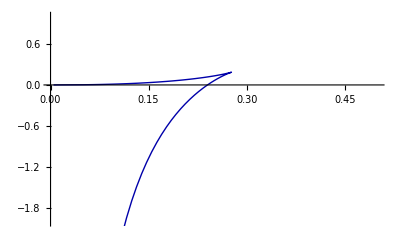

```mathematica
ParametricPlot[{(π zH)^-1 distance[ζs],zH VqqAnalytic[ζs]},{ζs,10^-6,1-10^-6},PlotStyle-> {Darker[Blue],Thick},
PlotRange->{{0,0.5},{-2,1}},AspectRatio->GoldenRatio^-1]
```

Now we add the value coming from the complex embeddings.

```mathematica
sameSpacedGrid[in_,fin_,NPoints_:100]:=Table[in+(k (fin-in))/NPoints,{k,1,NPoints}]
```

```mathematica
complexValuesPotential=Table[
Flatten[{π^-1 r,{ζs,zH VqqAnalytic[ζs]}}/.
FindRoot[(zH)^-1 distance[ζs]- r,{ζs,9/10+1/100 ⅈ}]],{r,sameSpacedGrid[869 10^-3,2]}];
```

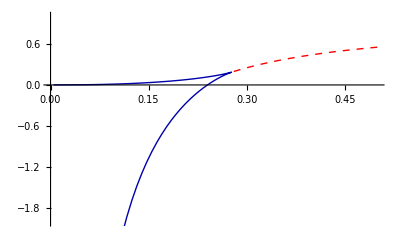

```mathematica
Show[ListLinePlot[Re[complexValuesPotential⟦All,{1,3}⟧],PlotStyle-> {Red,Thick,Dashed}],
ParametricPlot[{(π zH)^-1 distance[ζs],zH VqqAnalytic[ζs]},{ζs,10^-3,1-10^-6},PlotStyle-> {Darker[Blue],Thick}],
PlotRange->{{0,0.5},{-2,1}},AspectRatio->GoldenRatio^-1,AxesOrigin-> {0,0},AxesStyle->{{FontFamily->"Helvetica",FontSize-> 12},{FontFamily->"Helvetica",FontSize-> 12}}
]
```

### Load the data into two structs

The data is stored as columns
[1] = z_*
[2] = f(z_*)
[3] = g(z_*)
[4] = l(z_*)
[5] = V(z_*)

#### Data from python 1410.2546 data

```mathematica
resultdata14Re[280]=
```

```mathematica
resultdata14ReReg2[252]={{0.01,0.9999999246879127,1.0140006979100349,0.003835981046659246,-43.56877384936592},{0.0198989898989899,0.9999993070564661,1.0281916603510548,0.007677546935668591,-20.874633939691556},{0.029797979797979796,0.9999973405805784,1.042734115197328,0.011564225338796485,-13.419014474939287},{0.039696969696969696,0.9999929303399675,1.0576515769613533,0.015497096441794167,-9.657033000798023},{0.049595959595959596,0.9999846983885264,1.0729697137540386,0.019477323868602646,-7.373271382855791},{0.059494949494949496,0.9999709902817502,1.0887164138288379,0.023506160037368422,-5.831987604194137},{0.06939393939393938,0.9999498827209244,1.1049218575537108,0.027584951437144706,-4.717253182097422},{0.07929292929292929,0.9999191922627904,1.1216185955638205,0.031715143846476154,-3.870574459636959},{0.08919191919191918,0.9998764850326525,1.1388416338934388,0.03589828751488269,-3.2035663902072553},{0.09909090909090908,0.999819087367351,1.1566285269288423,0.04013604232725524,-2.6629902666726473},{0.10898989898989898,0.9997440973022278,1.175019479065424,0.04443018297022929,-2.2148331073444467},{0.11888888888888888,0.9996483968031076,1.1940574559922,0.04878260411744894,-1.8363300740715554},{0.12878787878787878,0.9995286646304603,1.2137883065657327,0.05319532564842252,-1.5116588628370575},{0.1386868686868687,0.9993813897082888,1.2342608962736212,0.057670497912308105,-1.2294734805510408},{0.1485858585858586,0.9992028848549711,1.2555272533254538,0.06221040704403374,-0.9814209488730641},{0.15848484848484848,0.9989893007173477,1.2776427284468415,0.06681748033549374,-0.7612120135906255},{0.16838383838383839,0.9987366397328307,1.300666169490082,0.07149429165836821,-0.5640183992173191},{0.1782828282828283,0.9984407699273716,1.3246601120133918,0.07624356692881777,-0.38607002348946073},{0.18818181818181817,0.9980974383398562,1.3496909870195752,0.08106818959574306,-0.22437875775387273},{0.19808080808080808,0.9977022838460156,1.3758293470845397,0.08597120612510381,-0.07654460795931506},{0.207979797979798,0.9972508491374739,1.4031501121460752,0.09095583144236456,0.05938304693564378},{0.21787878787878787,0.996738591594175,1.4317328362636526,0.09602545428195276,0.1850066022016823},{0.22777777777777777,0.9961608927714298,1.4616619967001863,0.10118364237931743,0.3016551556688225},{0.23767676767676768,0.9955130662063134,1.4930273067163073,0.10643414742423138,0.410440827033169},{0.24757575757575756,0.9947903632323987,1.5259240535059233,0.11178090967598132,0.5123016515676166},{0.25747474747474747,0.9939879764770242,1.5604534627377733,0.11722806212049557,0.6080346427196224},{0.2673737373737374,0.9931010407017268,1.5967230912001822,0.1227799340253612,0.6983215571760666},{0.2772727272727273,0.9921246306343532,1.6348472490738506,0.12844105372258224,0.7837491749875873},{0.2871717171717172,0.9910537554309944,1.6749474533786388,0.13421615041956408,0.8648254093602672},{0.29707070707070704,0.989883349397519,1.7171529141529602,0.140110154804287,0.9419922116056338},{0.30696969696969695,0.9886082585944783,1.7616010549263406,0.14612819817481476,1.0156359886038753},{0.31686868686868686,0.9872232229457957,1.808438069034439,0.15227560978041346,1.0860960715136132},{0.32676767676767676,0.9857228534713963,1.857819513298428,0.15855791201629862,1.1536716443569488},{0.33666666666666667,0.9841016042671662,1.9099109405440766,0.16498081306229206,1.2186274452928751},{0.3465656565656566,0.9823537388628862,1.964888572366622,0.17155019649976935,1.2811984821054927},{0.3564646464646465,0.9804732906006839,2.0229400134520072,0.17827210737940974,1.3415939498844385},{0.36636363636363634,0.9784540166937649,2.0842650086394,0.18515273414543226,1.4000004982911263},{0.37626262626262624,0.9762893456486195,2.149076243750162,0.19219838574907985,1.4565849647886875},{0.38616161616161615,0.9739723177645636,2.2176001910107335,0.19941546320690431,1.5114966663281804},{0.39606060606060606,0.9714955184636086,2.290077999657552,0.20681042477808315,1.564869323459022},{0.40595959595959596,0.9688510042527706,2.366766432027887,0.21438974384893913,1.6168226763742028},{0.41585858585858587,0.9660302211818304,2.447938845108861,0.2221598585272749,1.6674638410591238},{0.4257575757575757,0.9630239157343595,2.5338862171368266,0.23012711186233184,1.7168884447754453},{0.43565656565656563,0.9598220381811441,2.624918218410957,0.23829768152418251,1.7651815730553375},{0.44555555555555554,0.9564136385359348,2.7213643250114687,0.2466774977034497,1.8124185548072334},{0.45545454545454545,0.952786755387286,2.823574973600598,0.25527214792980324,1.8586656077458008},{0.46535353535353535,0.9489282980412284,2.9319227549438907,0.2640867674709779,1.9039803629339733},{0.47525252525252526,0.9448239226023243,3.046803643237353,0.27312591396065067,1.9484122845920313},{0.4851515151515151,0.9404579028506804,3.1686382577866747,0.28239342493533903,1.9920029993644714},{0.495050505050505,0.9358129970456911,3.297873153092378,0.29189225704235744,2.03478654784242},{0.5049494949494949,0.9308703121103361,3.434982132995976,0.30162430582894295,2.0767895702463166},{0.5148484848484849,0.9256091670298975,3.5804675843001776,0.31159020525677655,2.118031437723531},{0.5247474747474747,0.9200069577436583,3.734861825273649,0.3217891064218792,2.1585243406636963},{0.5346464646464646,0.914039026325328,3.898728464796674,0.33221843541202994,2.198273345736622},{0.5445454545454546,0.9076785378453958,4.072663768738837,0.3428736308324069,2.2372764339733533},{0.5544444444444444,0.9008963689935829,4.257298031664108,0.35374786227565314,2.2755245330886162},{0.5643434343434344,0.8936610133181754,4.4532969543633705,0.3648317319356552,2.313001558320742},{0.5742424242424242,0.8859385088154204,4.661363031312596,0.3761129626520181,2.3496844772651673},{0.5841414141414141,0.8776923945775017,4.882236957318382,0.3875760769333748,2.385543415395639},{0.594040404040404,0.8688837042786008,5.116699069811394,0.39920207291796406,2.420541820077514},{0.6039393939393939,0.8594710054357961,5.36557085307618,0.410968104746695,2.4546367017218995},{0.6138383838383838,0.8494104946074403,5.629716543913662,0.42284717639402103,2.487778971127775},{0.6237373737373737,0.8386561599577348,5.9100448957702,0.43480785953797135,2.51991389180718},{0.6336363636363637,0.8271600238803078,6.207511181441316,0.44681404743111097,2.550981664972219},{0.6435353535353535,0.8148724795763237,6.523119544605903,0.4588247578416031,2.580918162677327},{0.6534343434343434,0.8017427365436276,6.8579258496399325,0.47079399879258754,2.609655821178427},{0.6633333333333333,0.7877193907474628,7.213041229939515,0.48267071089108143,2.637124701774474},{0.6732323232323232,0.7727511356761434,7.589636600660387,0.49439879934274217,2.6632537202101876},{0.6831313131313131,0.7567876303702886,7.988948486696549,0.5059172671729201,2.6879720382323953},{0.693030303030303,0.7397805396502605,8.412286626634296,0.517160458636256,2.711210602346444},{0.702929292929293,0.7216847599161397,8.861043956054214,0.52805841830252,2.732903805604585},{0.7128282828282828,0.7024598407869775,9.336709759399458,0.5385373669391148,2.7529912389169153},{0.7227272727272727,0.6820716081825827,9.840887023102812,0.5485202902655182,2.771419489566722},{0.7326262626262626,0.6604939879173297,10.375315343856306,0.5579276312259112,2.788143937050204},{0.7425252525252525,0.637711020160256,10.941901173193164,0.5666780709857981,2.8031304907493295},{0.7524242424242424,0.6137190439400914,11.542757753587887,0.5746893788128902,2.8163572108749406},{0.7623232323232323,0.588529017030889,12.180257881165716,0.5818793067666067,2.8278157539815383},{0.7722222222222221,0.5621689199616268,12.857103703067956,0.588166502010285,2.83751258727953},{0.7821212121212121,0.5346861736608896,13.576419254293702,0.5934714077658454,2.8454699217719175},{0.792020202020202,0.5061499787549215,14.341873558693568,0.5977171234383638,2.851726322428765},{0.8019191919191919,0.4766534615218176,15.157845170745592,0.6008301949472858,2.856336963443865},{0.8118181818181818,0.4463154881533871,16.029643507058577,0.602741307227831,2.8593735071815716},{0.8217171717171717,0.4152819870081368,16.963808996411135,0.6033858512250236,2.8609235957655366},{0.8316161616161616,0.3837266002627191,17.968524261839487,0.602704336016147,2.861089953496838},{0.8415151515151514,0.35185047469534364,19.054184427915416,0.6006426108204869,2.8599891056990296},{0.8514141414141414,0.3198809997126561,20.23420001789898,0.5971518483048205,2.857749724666181},{0.8613131313131313,0.28806931298287686,21.52614754953215,0.5921882145331877,2.8545106158271674},{0.8712121212121212,0.25668642405307474,22.953453371431994,0.5857121033088281,2.8504183567919674},{0.8811111111111111,0.22601785760350754,24.54791948819056,0.577686727584583,2.8456245981737553},{0.891010101010101,0.19635679299633713,26.353624050775103,0.5680757080753945,2.8402830268344528},{0.9009090909090909,0.16799577616907135,28.433154483699298,0.5568390194935756,2.834545976645276},{0.9108080808080807,0.14121720167805105,30.87798139984405,0.5439261230475272,2.8285606424891157},{0.9207070707070707,0.11628290124432766,33.826586985116094,0.5292640530028788,2.822464795575687},{0.9306060606060605,0.0934233207104447,37.49808526571513,0.5127359776510458,2.8163817794579313},{0.9405050505050505,0.07282690562833312,42.25937075846877,0.49414062714901097,2.8104143087846194},{0.9504040404040404,0.054630428451753366,48.772632066129866,0.47311014154192976,2.8046359975422614},{0.9603030303030302,0.03891105645078655,58.36350281529909,0.448927632911159,2.7990780390141383},{0.9702020202020202,0.02568095761451022,74.1229162257053,0.4200650280719611,2.7937041356131838},{0.98010101010101,0.014885153710950031,105.29758153131068,0.3827478671378993,2.788351633136051},{0.99,0.006403144489517773,197.7568990221382,0.3244755623346581,2.7825418294018776}};
resultdata14ImagReg2[280]={{0.01,0.9999998340088696,1.0126864524077996,0.003833875897005625,-42.10886017028633},{0.0198989898989899,0.9999986024304351,1.0258308141431236,0.007669951247500793,-20.22771758192878},{0.029797979797979796,0.9999950103450307,1.0395883229280025,0.011548863953025273,-13.04389385405684},{0.039696969696969696,0.9999875115771077,1.0539908748114977,0.015472817854787666,-9.42017052372488},{0.049595959595959596,0.9999743190536713,1.0690723819420669,0.019444110855992333,-7.220354127915652},{0.059494949494949496,0.9999534156879755,1.0848688697062934,0.02346513786200015,-5.735311655860614},{0.06939393939393938,0.9999225657263989,1.1014185819001112,0.027538393782398217,-4.660663573081584},{0.07929292929292929,0.9998793264889302,1.1187620943529546,0.03166647660297157,-3.843770567882869},{0.08919191919191918,0.9998210604255315,1.1369424374388204,0.03585209053315424,-3.1995457521267197},{0.09909090909090908,0.9997449474019944,1.1560052279202497,0.040098049231536405,-2.6767571576480957},{0.10898989898989898,0.9996479971197679,1.1759988105813557,0.0444072791089773,-2.2426867310100285},{0.11888888888888888,0.9995270615647192,1.1969744101139135,0.04878282270468668,-1.8754449992309272},{0.12878787878787878,0.9993788473698578,1.218986293725642,0.05322784212650412,-1.5598241589228201},{0.1386868686868687,0.9991999279668694,1.2420919449416474,0.05774562254135548,-1.28492330509901},{0.1485858585858586,0.9989867553908501,1.2663522490678176,0.06233957569600916,-1.0427204679809692},{0.15848484848484848,0.9987356715920661,1.2918316907780445,0.0670132434417793,-0.827178194986327},{0.16838383838383839,0.9984429190979062,1.3185985642745224,0.07177030122885174,-0.6336635580944026},{0.1782828282828283,0.9981046508576102,1.3467251964510247,0.07661456152784211,-0.45856066311933397},{0.18818181818181817,0.9977169390919008,1.3762881834617797,0.08154997712575042,-0.29900496219169836},{0.19808080808080808,0.9972757829594519,1.4073686410619828,0.08658064423294387,-0.15269688313591256},{0.207979797979798,0.9967771148423188,1.440052469038572,0.0917108053250524,-0.017768433207700163},{0.21787878787878787,0.9962168050431386,1.474430629989942,0.09694485162968891,0.10731401253015482},{0.22777777777777777,0.9955906646782248,1.5105994426388458,0.10228732515220537,0.22382170505075338},{0.23767676767676768,0.9948944465427663,1.5486608897717489,0.10774292011665071,0.3328176199306583},{0.24757575757575756,0.9941238437173193,1.5887229407879941,0.11331648367897018,0.4351976475320609},{0.25747474747474747,0.9932744856788245,1.6308998887108146,0.11901301574679722,0.5317223324496116},{0.2673737373737374,0.992341931674625,1.675312701356726,0.1248376677160823,0.6230415989779301},{0.2772727272727273,0.9913216611145929,1.7220893861772006,0.13079573990726456,0.7097142056580323},{0.2871717171717172,0.990209060734658,1.771365368073695,0.13689267745424838,0.7922231928960581},{0.29707070707070704,0.9889994082849998,1.8232838792407362,0.14313406436513404,0.8709882518449081},{0.30696969696969695,0.9876878524981251,1.8779963598085758,0.14952561543868056,0.946375704105094},{0.31686868686868686,0.9862693890962934,1.935662867733419,0.1560731656796546,1.0187066100499318},{0.32676767676767676,0.9847388326045738,1.9964524960160759,0.162782656813557,1.0882633985029098},{0.33666666666666667,0.9830907837455902,2.060543794915836,0.1696601204540638,1.1552953184050319},{0.3465656565656566,0.9813195922051691,2.1281251963624443,0.1767116574271744,1.2200229446127708},{0.3564646464646465,0.9794193145751875,2.1993954372528144,0.1839434127021036,1.2826419185333},{0.36636363636363634,0.977383667301503,2.274563977748668,0.19136154532365596,1.3433260653396963},{0.37626262626262624,0.9752059744917445,2.3538514100658374,0.19897219268193136,1.402229999750894},{0.38616161616161615,0.9728791104707638,2.4374898525658093,0.2067814283965854,1.459491309461075},{0.39606060606060606,0.9703954370118001,2.5257233232274756,0.2147952130338992,1.5152323875640692},{0.40595959595959596,0.967746735220116,2.618808085795992,0.2230193368161215,1.5695619714921958},{0.41585858585858587,0.9649241321044698,2.7170129610834106,0.23145935343144955,1.6225764351622793},{0.4257575757575757,0.9619180219420224,2.820619595042497,0.24012050400525622,1.6743608725108594},{0.43565656565656563,0.958717982626106,2.929922674365723,0.24900763025767236,1.7249900038983756},{0.44555555555555554,0.9553126872859569,3.045230079495499,0.258125075855069,1.7745289315855524},{0.45545454545454545,0.951689811585652,3.166862964095563,0.2674765749600711,1.8230337663450147},{0.46535353535353535,0.9478359372489715,3.2951557492605006,0.2770651270179783,1.8705521440491897},{0.47525252525252526,0.9437364525210112,3.430456020073437,0.28689285687805466,1.9171236486029526},{0.4851515151515151,0.9393754504696528,3.573124311614285,0.2969608594590687,1.9627801557399056},{0.495050505050505,0.9347356262543313,3.7235337712383716,0.3072690283322761,2.0075461108726933},{0.5049494949494949,0.9297981747500805,3.8820696839685347,0.3178158678233201,2.0514387533027385},{0.5148484848484849,0.9245426902158185,4.04912884827079,0.3285982885424528,2.094468298586734},{0.5247474747474747,0.9189470700416312,4.225118790432232,0.3396113866496988,2.136638090670915},{0.5346464646464646,0.9129874250045772,4.410456807371396,0.3508482076548164,2.1779447354851595},{0.5445454545454546,0.9066379989100518,4.605568830154114,0.3622994961626004,2.218378227984817},{0.5544444444444444,0.899871100999102,4.810888103961587,0.37395343369004236,2.257922085081013},{0.5643434343434344,0.8926570550631486,5.026853684998476,0.3857953675236284,2.296553497442286},{0.5742424242424242,0.8849641698265843,5.253908761116045,0.39780753453194734,2.3342435137065216},{0.5841414141414141,0.8767587358324381,5.492498811088587,0.40996878488961286,2.370957271120509},{0.594040404040404,0.8680050547913104,5.743069627909666,0.42225431178535155,2.4066542869211323},{0.6039393939393939,0.8586655081193237,6.00606524463038,0.43463539432229686,2.4412888247700124},{0.6138383838383838,0.8487006721816764,6.281925817695439,0.4470791619332447,2.4748103501239216},{0.6237373737373737,0.838069488552332,6.571085543105724,0.45954838964615513,2.5071640874362577},{0.6336363636363637,0.8267294983667218,6.87397070585082,0.47200133435900443,2.538291690411943},{0.6435353535353535,0.8146371505419775,7.190997993896259,0.48439162282588616,2.568132034068934},{0.6534343434343434,0.8017481942148731,7.522573245805034,0.4966682022008423,2.5966221340185784},{0.6633333333333333,0.7880181661338617,7.869090847371505,0.5087753636363355,2.6236981941300472},{0.6732323232323232,0.7734029838549058,8.230934049444164,0.5206528484906424,2.649296778630757},{0.6831313131313131,0.7578596553303324,8.608476549021884,0.5322360450909864,2.673356098827993},{0.693030303030303,0.741347114726488,9.002085762201071,0.5434562816999813,2.695817398223462},{0.702929292929293,0.7238271929220024,9.41212832533129,0.5542412183498644,2.7166264131278526},{0.7128282828282828,0.7052657289698727,9.838978496266318,0.5645153366288531,2.735734879341503},{0.7227272727272727,0.6856338256859968,10.28303029989032,0.574200522448692,2.753102049489113},{0.7326262626262626,0.66490924828023,10.744714483897262,0.5832167325076633,2.7686961806327512},{0.7425252525252525,0.6430779594024889,11.224521640361736,0.5914827308052285,2.782495948278019},{0.7524242424242424,0.6201357769822938,11.72303323244165,0.5989168774387573,2.7944917411923953},{0.7623232323232323,0.596090132678473,12.240962782505944,0.605437948248614,2.8046867918076965},{0.7722222222222221,0.5709618985714916,12.779210185992314,0.6109659608638001,2.8130980994593333},{0.7821212121212121,0.5447872379621327,13.338933101748934,0.615422980415131,2.819757108205318},{0.792020202020202,0.5176194229553448,13.921640768284757,0.6187338765550252,2.8247101071711898},{0.8019191919191919,0.48953054724740575,14.52931761437927,0.6208270021686738,2.828018328816599},{0.8118181818181818,0.4606130477547479,15.164587001377592,0.6216347627366963,2.8297577286314812},{0.8217171717171717,0.4309809342391991,15.830929885020161,0.6210940428194975,2.8300184378974245},{0.8316161616161616,0.40077061300623235,16.532979993634957,0.6191464511757346,2.8289038886478233},{0.8415151515151514,0.370141180502288,17.27692776734861,0.6157383364839679,2.826529616227154},{0.8514141414141414,0.3392740569429372,18.071082355984416,0.6108205081636612,2.8230217493534973},{0.8613131313131313,0.3083718309550249,18.926669013677465,0.6043475659384098,2.818515199833085},{0.8712121212121212,0.2776561957661671,19.85898671280737,0.5962766882965285,2.8131515634988253},{0.8811111111111111,0.24736487787898132,20.889133930979675,0.5865656372484983,2.807076739685327},{0.891010101010101,0.21774749234538626,22.04666173129536,0.5751695737264211,2.800438267003769},{0.9009090909090909,0.18906030608042937,23.3738004362169,0.5620359835836118,2.793382355093124},{0.9108080808080807,0.16155995256688366,24.932480353980836,0.5470964624242035,2.7860505586693494},{0.9207070707070707,0.1354962168858155,26.816586425714597,0.5302530226500265,2.778575977287126},{0.9306060606060605,0.11110409656550675,29.174671764599854,0.5113543224052071,2.771078740237635},{0.9405050505050505,0.08859543643246728,32.25531090264389,0.49015213267634083,2.763660277038284},{0.9504040404040404,0.06815052729772897,36.506724609440546,0.4662158393453644,2.7563952917721335},{0.9603030303030302,0.04991013947701472,42.825412869728936,0.43874801007828557,2.7493189171693913},{0.9702020202020202,0.03396852156551703,53.30030988538005,0.406130223410899,2.742402432966987},{0.98010101010101,0.0203679204072948,74.17799875560937,0.36455167227118074,2.7354967083655364},{0.99,0.009095158180758152,136.43939517159671,0.30198854301863226,2.728152131075233}};
resultdata14ReReg2[315]={{0.01,0.9999983889324504,1.0210100460030027,0.003847035904363787,-38.68442318535082},{0.0198989898989899,0.9999873308678902,1.042280608369794,0.007721348381328039,-18.264556587385847},{0.029797979797979796,0.9999575692842241,1.0640431894980853,0.011662456290682416,-11.517161342489299},{0.039696969696969696,0.9999000035888524,1.086320541622504,0.015671359509642456,-8.094342824285766},{0.049595959595959596,0.9998057459076808,1.1091366181200148,0.019749068015398028,-6.005957811834575},{0.059494949494949496,0.9996661763280614,1.1325166349410662,0.02389660523349616,-4.589755865495533},{0.06939393939393938,0.9994729962245428,1.1564871361359736,0.028115012250526625,-3.5608236115100693},{0.07929292929292929,0.9992182792755716,1.1810760637898199,0.032405352886606564,-2.775961983829559},{0.08919191919191918,0.9988945197609741,1.2063128327056811,0.03676871961378341,-2.1551698624875018},{0.09909090909090908,0.9984946777162761,1.2322284102051126,0.041206240296137155,-1.6501721492509454},{0.10898989898989898,0.9980122205110546,1.2588554014468243,0.04571908571671785,-1.2300721631490505},{0.11888888888888888,0.9974411604148339,1.28622814069962,0.05030847784484637,-0.8741542045379962},{0.12878787878787878,0.9967760877156707,1.3143827890443924,0.05497569878530152,-0.5679947080230603},{0.1386868686868687,0.9960121989635748,1.343357439022543,0.05972210033839109,-0.30123230904259923},{0.1485858585858586,0.9951453199231389,1.373192226795211,0.06454911408697987,-0.06622521962355776},{0.15848484848484848,0.9941719228370244,1.4039294524295285,0.06945826191320466,0.14279082345272043},{0.16838383838383839,0.9930891376238592,1.435613708985429,0.07445116683362392,0.3302492909581858},{0.1782828282828283,0.991894756660215,1.4682920211399482,0.07952956402787742,0.49961859073532766},{0.18818181818181817,0.9905872328260055,1.5020139941561694,0.08469531192084737,0.6536531451550229},{0.19808080808080808,0.9891656705252259,1.5368319740818976,0.08995040316335101,0.7945697275058241},{0.207979797979798,0.9876298094286413,1.5728012201496453,0.09529697534059421,0.924173826290934},{0.21787878787878787,0.98598000072098,1.60998009044578,0.10073732122065786,1.0439518389641527},{0.22777777777777777,0.9842171756715399,1.6484302420238472,0.10627389833778562,1.1551394260880565},{0.23767676767676768,0.9823428063829729,1.688216846756658,0.11190933768524422,1.2587729302484663},{0.24757575757575756,0.9803588586074983,1.729408824355263,0.11764645127212137,1.355728566175153},{0.25747474747474747,0.9782677365521263,1.7720790941323252,0.12348823827469417,1.4467526482870143},{0.2673737373737374,0.9760722196238935,1.8163048472548082,0.12943788948724766,1.5324851596223295},{0.2772727272727273,0.973775391092053,1.862167841418704,0.13549878974822924,1.6134783117259972},{0.2871717171717172,0.97138055866619,1.909754720089652,0.14167451798557318,1.6902112927745914},{0.29707070707070704,0.9688911670071013,1.9591573586909814,0.14796884448791442,1.7631020839210034},{0.30696969696969695,0.9663107022010686,2.010473240388718,0.1543857249686219,1.8325169981640244},{0.31686868686868686,0.9636425882380998,2.0638058644258788,0.16092929094419273,1.8987784334836377},{0.32676767676767676,0.9608900755415449,2.1192651903009825,0.16760383589820627,1.9621712134929614},{0.33666666666666667,0.9580561216011669,2.17696812147412,0.17441379664770792,2.0229478015400555},{0.3465656565656566,0.9551432637657565,2.2370390327250522,0.18136372927031455,2.081332609191157},{0.3564646464646465,0.9521534842566081,2.2996103457897528,0.18845827888697,2.1375255711773944},{0.36636363636363634,0.9490880674720924,2.364823158474135,0.19570214253114673,2.1917051218583667},{0.37626262626262624,0.9459474496691456,2.4328279330974385,0.20310002426851612,2.2440306799638767},{0.38616161616161615,0.9427310611334069,2.503785250866175,0.21065658166825496,2.294644726608161},{0.39606060606060606,0.9394371609902742,2.577866639638086,0.2183763626687965,2.34367454472525},{0.40595959595959596,0.9360626648693593,2.655255483522547,0.22626373183209655,2.3912336749773107},{0.41585858585858587,0.9326029657205361,2.7361480239011615,0.2343227849506197,2.4374231329813876},{0.4257575757575757,0.9290517481976232,2.820754462765735,0.2425572509625348,2.4823324247435226},{0.43565656565656563,0.9254007971832449,2.9093001807912806,0.2509703801578937,2.5260403910110627},{0.44555555555555554,0.9216398012339234,3.002027084326308,0.2595648177323372,2.568615906499382},{0.45545454545454545,0.9177561519871529,3.0991950975355436,0.268342461874067,2.6101184563506252},{0.46535353535353535,0.9137347409021244,3.201083818325038,0.27730430578007376,2.6505986095401295},{0.47525252525252526,0.9095577551134809,3.3079943594806767,0.2864502632947324,2.690098407102446},{0.4851515151515151,0.9052044746740806,3.4202513997366335,0.2957789782758741,2.72865168188014},{0.495050505050505,0.9006510740594218,3.5382054733553496,0.3052876183347254,2.766284325900667},{0.5049494949494949,0.8958704315139596,3.6622355313608868,0.31497165428153345,2.8030145213621704},{0.5148484848484849,0.8908319506478778,3.7927518129651707,0.324824627454941,2.8388529514621177},{0.5247474747474747,0.8855013996499592,3.930199072135916,0.3348379081271783,2.873803007828167},{0.5346464646464646,0.879840774573024,4.075060211891329,0.34500044934278756,2.9078610119830817},{0.5445454545454546,0.8738081943734801,4.227860388036643,0.35529854186459875,2.941016468951939},{0.5544444444444444,0.8673578367401166,4.38917165501321,0.3657155773049694,2.973252371623322},{0.5643434343434344,0.8604399252150295,4.559618239727073,0.37623182797106886,3.004545574609101},{0.5742424242424242,0.853000779665967,4.7398825451817075,0.38682425333556525,3.034867255883766},{0.5841414141414141,0.8449829437744424,4.930712005116553,0.39746634425812666,3.0641834831922665},{0.594040404040404,0.8363254047998466,5.132926934482785,0.408128016971045,3.0924558998666156},{0.6039393939393939,0.8269639223866775,5.347429549533655,0.41877556924106507,3.1196425410950575},{0.6138383838383838,0.8168314844942837,5.575214366931729,0.4293717108612124,3.14569878672199},{0.6237373737373737,0.8058589095105787,5.817380235336518,0.4398756795546951,3.1705784503054346},{0.6336363636363637,0.7939756140941319,6.07514430771349,0.45024345136727856,3.1942349965501675},{0.6435353535353535,0.7811105660682273,6.349858331074816,0.4604280516396291,3.216622870669149},{0.6534343434343434,0.767193440524979,6.643027716435392,0.47037996872388393,3.2376989141876207},{0.6633333333333333,0.7521559949125481,6.95633396062003,0.48004766790158326,3.257423832842348},{0.6732323232323232,0.7359336749713641,7.291661130091308,0.48937819774708574,3.27576367432089},{0.6831313131313131,0.7184674576376883,7.6511272944545,0.498317875857324,3.2926912674479367},{0.693030303030303,0.6997059291293959,8.037122026298471,0.5068130358978207,3.3081875708221293},{0.702929292929293,0.6796075860842853,8.45235138171612,0.5148108138087479,3.3222428784234057},{0.7128282828282828,0.6581433346178197,8.899892165890018,0.5222599482305492,3.334857832656102},{0.7227272727272727,0.6352991464026609,9.38325780350296,0.5291115691107414,3.346044201622946},{0.7326262626262626,0.6110788124186405,9.906478820839697,0.5353199492467915,3.355825386708724},{0.7425252525252525,0.5855067141931164,10.474201871313092,0.5408431961784164,3.3642366380181006},{0.7524242424242424,0.5586305097782718,11.091812493839981,0.5456438661650296,3.371324967834778},{0.7623232323232323,0.5305236084135919,11.765588522628503,0.5496894875280992,3.3771487649052014},{0.7722222222222221,0.5012872852711076,12.502893472406338,0.5529529868503482,3.3817771239048073},{0.7821212121212121,0.47105226784392973,13.312422612198336,0.5554130177452146,3.3852889140061633},{0.792020202020202,0.4399796108744248,14.204519281614205,0.5570541974651486,3.387771617429214},{0.8019191919191919,0.40826067012061096,15.191586021748526,0.5578672608525638,3.3893199729595587},{0.8118181818181818,0.3761159899153958,16.28862543355417,0.5578491434042339,3.3900344607720245},{0.8217171717171717,0.34379293862466914,17.513961184782186,0.5570030048860284,3.390019663888915},{0.8316161616161616,0.3115619627003702,18.89021330015076,0.5553382011399004,3.3893825388298566},{0.8415151515151514,0.27971138623317965,20.445638913385746,0.5528702032679169,3.388230624136351},{0.8514141414141414,0.24854075959312194,22.21600891506249,0.5496204481013242,3.3866702110820883},{0.8613131313131313,0.218352856829114,24.247288250440516,0.5456160778931692,3.384804496390853},{0.8712121212121212,0.18944453338856063,26.59955226450575,0.5408894831332739,3.382731732160427},{0.8811111111111111,0.16209677685847212,29.352859511851996,0.5354774860027438,3.3805433827667515},{0.891010101010101,0.13656440411806017,32.61632490417094,0.5294198647144218,3.378322290549951},{0.9009090909090909,0.11306596591856757,36.542631152694184,0.5227566615955892,3.3761408379283666},{0.9108080808080807,0.0917744997365504,41.35220350634091,0.51552321159516,3.374059066005768},{0.9207070707070707,0.07280980834887804,47.37549240595754,0.5077407777955706,3.372122654016759},{0.9306060606060605,0.05623292086377347,55.131445623008545,0.499398363101952,3.3703605484828505},{0.9405050505050505,0.04204330469691166,65.48431927878508,0.4904157615655277,3.3687817823656574},{0.9504040404040404,0.030179237559936366,79.98827882550363,0.4805635785071375,3.3673704553876966},{0.9603030303030302,0.020521523254719776,101.74758623304928,0.4692739303296682,3.366076417875183},{0.9702020202020202,0.012900459742742917,137.99132981549343,0.4551306159166104,3.364795100436947},{0.98010101010101,0.007105668877457702,210.3331345805191,0.43418997087021877,3.3633155606937697},{0.99,0.002898109164446257,425.9673344344498,0.3919606185612,3.3611448654285843}};
resultdata14ReReg2[360]={{0.01,0.9999996403288445,1.021600858350933,0.003847971243202624,-35.73401183743394},{0.0198989898989899,0.9999970812709138,1.0434362831866086,0.007724988833109141,-16.850478607104375},{0.029797979797979796,0.9999899171341032,1.0657368716267024,0.011670488080600989,-10.607895195890432},{0.039696969696969696,0.9999755000462942,1.0885186776168072,0.01568539922704568,-7.4398603737274955},{0.049595959595959596,0.9999509469524626,1.1117992108097796,0.01977067648468004,-5.506178402562917},{0.059494949494949496,0.9999131476747475,1.1355974973664456,0.023927300341896256,-4.194391413043423},{0.06939393939393938,0.9998587740381585,1.1599341413795936,0.02815627983550151,-3.2409653810976735},{0.07929292929292929,0.9997842900571876,1.1848313870036928,0.032458654801267965,-2.5134264662075543},{0.08919191919191918,0.9996859631697456,1.2103131813888233,0.03683549811444092,-1.9377549388570525},{0.09909090909090908,0.9995598764948606,1.2364052385314006,0.04128791793194451,-1.4692793707957872},{0.10898989898989898,0.9994019420794823,1.263135104166154,0.04581705994793778,-1.0794064054928638},{0.11888888888888888,0.9992079150875114,1.2905322218332471,0.05042410967365648,-0.7489631384169089},{0.12878787878787878,0.9989734088708445,1.3186280002611892,0.05511029475132683,-0.46459958983705274},{0.1386868686868687,0.9986939108478297,1.347455882210021,0.0598768873103883,-0.21672561768349397},{0.1485858585858586,0.998364799099102,1.377051414920008,0.06472520637183059,0.001731374492333071},{0.15848484848484848,0.997981359574393,1.4074523223084832,0.06965662030341942,0.19610564584381285},{0.16838383838383839,0.9975388037866584,1.4386985790514075,0.07467254932494105,0.37049910396015173},{0.1782828282828283,0.997032286851851,1.4708324866764237,0.07977446805778798,0.5281198192864034},{0.18818181818181817,0.9964569257140069,1.5038987517805344,0.08496390810738533,0.6715144515277753},{0.19808080808080808,0.9958078173761339,1.5379445664678464,0.09024246066057731,0.8027315134335593},{0.207979797979798,0.9950800569378798,1.5730196910809182,0.09561177907189561,0.923438389516138},{0.21787878787878787,0.994268755221243,1.6091765392730306,0.10107358140355416,1.0350067310175155},{0.22777777777777777,0.9933690557459066,1.6464702654379555,0.10662965287371214,1.1385757870613387},{0.23767676767676768,0.9923761507962632,1.6849588544784926,0.11228184815473059,1.2351000614010976},{0.24757575757575756,0.9912852963031282,1.7247032138550333,0.1180320934506678,1.3253856504624482},{0.25747474747474747,0.9900918252446652,1.765767267810649,0.12388238826678355,1.410118285657167},{0.2673737373737374,0.9887911592534211,1.8082180536197132,0.12983480676706635,1.4898852124821294},{0.2772727272727273,0.9873788180998092,1.852125819652825,0.13589149859647426,1.5651924333292433},{0.2871717171717172,0.9858504267070789,1.8975641249920276,0.1420546890230941,1.6364784223614297},{0.29707070707070704,0.9842017193390147,1.9446099402671786,0.14832667823110152,1.7041251271632238},{0.30696969696969695,0.9824285405895117,1.9933437493171642,0.154709839570119,1.7684668630222296},{0.31686868686868686,0.9805268427929834,2.0438496512090922,0.16120661653668572,1.8297975552547854},{0.32676767676767676,0.978492679466491,2.096215462075241,0.16781951823208882,1.8883766753374143},{0.33666666666666667,0.9763221943887279,2.1505328161524853,0.1745511130054871,1.9444341358014108},{0.3465656565656566,0.974011605917773,2.2068972653334096,0.18140401995433816,1.9981743486920636},{0.3564646464646465,0.9715571861490638,2.2654083764641,0.18838089791088103,2.0497796071776833},{0.36636363636363634,0.9689552345175733,2.3261698255528236,0.1954844315009501,2.0994129156030668},{0.37626262626262624,0.9662020454540103,2.389289487989252,0.2027173138104654,2.1472203670568284},{0.38616161616161615,0.9632938697143346,2.4548795238190153,0.21008222514550934,2.1933331473088},{0.39606060606060606,0.9602268690154079,2.523056457077524,0.21758180731571516,2.237869228279199},{0.40595959595959596,0.9569970636277487,2.5939412481654474,0.22521863281291657,2.280934801933035},{0.41585858585858587,0.9536002725997879,2.6676593582526316,0.2329951681977956,2.322625495845241},{0.4257575757575757,0.950032046317597,2.744340804735487,0.2409137309452295,2.3630274040518153},{0.43565656565656563,0.9462875911409037,2.8241202068547824,0.24897643893706728,2.4022179607422314},{0.44555555555555554,0.9423616859016826,2.907136820718135,0.25718515173416634,2.440266679519132},{0.45545454545454545,0.9382485901074472,2.9935345631784998,0.2655414027016998,2.477235777094879},{0.46535353535353535,0.933941943759745,3.083462024313926,0.2740463210172819,2.5131806972201356},{0.47525252525252526,0.9294346587818639,3.177072468655254,0.28270054255604377,2.548150548195445},{0.4851515151515151,0.9247188021516395,3.2745238258422336,0.29150410862982734,2.5821884653931955},{0.495050505050505,0.919785470959331,3.3759786720843876,0.30045635156750744,2.615331908729076},{0.5049494949494949,0.9146246597614291,3.4816042046965525,0.3095557661642721,2.6476129039035303},{0.5148484848484849,0.9092251207843443,3.591572213113152,0.31879986611352923,2.67905823543943},{0.5247474747474747,0.9035742177535219,3.7060590512113256,0.3281850246791975,2.7096895990335},{0.5346464646464646,0.8976577743908661,3.8252456175528264,0.3377062990747837,2.7395237204902525},{0.5445454545454546,0.891459918944652,3.9493173523626712,0.3473572383160726,2.76857244849625},{0.5544444444444444,0.8849629265005362,4.078464262789122,0.3571296747122727,2.796842828698909},{0.5643434343434344,0.8781470612799344,4.212880991344154,0.36701349968121383,2.8243371669590234},{0.5742424242424242,0.8709904216737364,4.352766946539955,0.37699642522857907,2.851053090225394},{0.5841414141414141,0.8634687913963761,4.498326519779489,0.38706373323539567,2.876983614201988},{0.594040404040404,0.8555555008890493,4.649769418730136,0.39719801566470136,2.902117227800761},{0.6039393939393939,0.8472213039622033,4.8073111549619325,0.40737890991698256,2.9264380052392447},{0.6138383838383838,0.8384342756557229,4.971173732881797,0.41758283483926084,2.949925757475378},{0.6237373737373737,0.8291597384173695,5.141586598342564,0.4277827342843298,2.972556235375807},{0.6336363636363637,0.8193602249586527,5.31878791926122,0.43794783658336117,2.994301397468031},{0.6435353535353535,0.808995487538934,5.503026287800395,0.4480434397655999,3.0151297551895953},{0.6534343434343434,0.7980225649408617,5.694562955005007,0.45803073372651554,3.0350068080617105},{0.6633333333333333,0.7863959200088582,5.89367473536022,0.4678666716881031,3.0538955800110354},{0.6732323232323232,0.7740676622870027,6.100657752030811,0.4775039040511008,3.071757265983085},{0.6831313131313131,0.7609878719522709,6.315832235538209,0.486890787934768,3.088551994897367},{0.693030303030303,0.7471050428066304,6.539548642009543,0.49597148515016654,3.1042397108037005},{0.702929292929293,0.7323666634477938,6.772195425549904,0.5046861598919449,3.11878116880638},{0.7128282828282828,0.7167199567258206,7.014208887787775,0.5129712849171603,3.1321390360269716},{0.7227272727272727,0.7001127980087519,7.2660856432516825,0.5207600613479092,3.1442790808106675},{0.7326262626262626,0.6824948323720436,7.528398391854672,0.5279829524985856,3.1551714259111745},{0.7425252525252525,0.6638188092863155,7.801815893500525,0.5345683264320176,3.1647918340194776},{0.7524242424242424,0.6440421503431712,8.087128315025371,0.5404431955387358,3.1731229873351854},{0.7623232323232323,0.6231287606157561,8.385279496058526,0.5455340346915731,3.1801557175631023},{0.7722222222222221,0.601051086945901,8.697408201896126,0.5497676528909247,3.185890139374262},{0.7821212121212121,0.5777924163119265,9.024901164149576,0.5530720872522656,3.1903366394898414},{0.792020202020202,0.5533493940067983,9.36946175443981,0.5553774830897978,3.1935166754157436},{0.8019191919191919,0.5277347242619174,9.733199648901708,0.5566169199290939,3.1954633424697163},{0.8118181818181818,0.5009799949470747,10.118749068376774,0.5567271404431755,3.1962216747793293},{0.8217171717171717,0.47313854306081116,10.529426518337857,0.5556491370353285,3.1958486547465994},{0.8316161616161616,0.4442882492544041,10.969444058427952,0.5533285479215602,3.194412915177949},{0.8415151515151514,0.41453411846101124,11.444202108585385,0.5497158091498017,3.191994127795782},{0.8514141414141414,0.38401047133163524,11.960698561326293,0.5447659978001812,3.1886820800524163},{0.8613131313131313,0.35288253990999924,12.528111935280135,0.5384382794727622,3.184575447945355},{0.8712121212121212,0.32134723402322013,13.15865178051263,0.5306948314951369,3.1797802748111623},{0.8811111111111111,0.28963282640992677,13.868831615136925,0.5214990370631926,3.174408163706895},{0.891010101010101,0.25799729975510083,14.68143249129747,0.5108126071765332,3.168574182416521},{0.9009090909090909,0.22672511335258386,15.628639557452193,0.49859103302464036,3.162394462629198},{0.9108080808080807,0.19612218712773077,16.75726230066902,0.4847762908882438,3.1559834429299416},{0.9207070707070707,0.16650897181704027,18.13785873921399,0.4692847730836308,3.1494506470794454},{0.9306060606060605,0.13821158032853473,19.88166122184389,0.4519864365193134,3.142896777991544},{0.9405050505050505,0.11155109802080725,22.17438970554414,0.43266670834449694,3.136408680589075},{0.9504040404040404,0.08683136588672738,25.35054641482781,0.41095172439432787,3.130052221108216},{0.9603030303030302,0.06432573168639028,30.078853883957326,0.38614703603796324,3.1238608826518015},{0.9702020202020202,0.04426347426317567,37.91729218628751,0.35684028597259815,3.1178143417381037},{0.98010101010101,0.026816802495299275,53.52476744796191,0.3197013065502262,3.1117890108478994},{0.99,0.012089482802535034,100.00869985236797,0.26421640833463983,3.1054018570752655}};
resultdata14ReReg2[420]={{0.01,0.9999995983920633,1.0162399043304498,0.003839516764041083,-35.97596153265356},{0.0198989898989899,0.9999967823442004,1.032692252940105,0.007691571120016584,-17.15679801276218},{0.029797979797979796,0.9999890164284808,1.0495457478671217,0.011595733148920434,-10.96258613261987},{0.039696969696969696,0.999973607069872,1.0668284826779453,0.0155531315409027,-7.831594065722448},{0.049595959595959596,0.9999477019135179,1.0845701919276494,0.01956498176100222,-5.927654649887436},{0.059494949494949496,0.999908289204516,1.1028022885068414,0.02363258811294065,-4.6405851279401205},{0.06939393939393938,0.999852197191819,1.1215579034610001,0.027757345517278154,-3.7082129834498536},{0.07929292929292929,0.9997760935674641,1.1408719284305524,0.03194074099123683,-2.9989354062493847},{0.08919191919191918,0.99967648495154,1.1607810608215545,0.03618435481620546,-2.439321454165131},{0.09909090909090908,0.9995497164325351,1.1813238517727231,0.04048986137717678,-1.985115677679794},{0.10898989898989898,0.9993919711719612,1.2025407569344304,0.04485902965689119,-1.608029326409814},{0.11888888888888888,0.9991992700814424,1.224474190018689,0.04929372336479869,-1.2891192357738288},{0.12878787878787878,0.9989674715797657,1.2471685790156057,0.05379590067907801,-1.0152130539961988},{0.1386868686868687,0.9986922714367454,1.2706704249006706,0.058367613576799204,-0.7768609200239598},{0.1485858585858586,0.9983692027101263,1.2950283625779297,0.06301100672451686,-0.5671030858902615},{0.15848484848484848,0.9979936357811773,1.3202932237157414,0.0677283158981267,-0.38069756415778544},{0.16838383838383839,0.9975607784940703,1.346518101033646,0.07252186589720082,-0.21361900526801136},{0.1782828282828283,0.9970656764036306,1.37375841348991,0.07739406791500646,-0.06272371051313197},{0.18818181818181817,0.9965032131355838,1.4020719716985162,0.08234741632107904,0.07448018492984243},{0.19808080808080808,0.9958681108629792,1.4315190427707107,0.08738448480862432,0.19999401132562244},{0.207979797979798,0.9951549309020983,1.4621624136284614,0.09250792185406544,0.3154440808708623},{0.21787878787878787,0.9943580744307999,1.4940674516742127,0.09772044543063878,0.42216591764201805},{0.22777777777777777,0.9934717833319624,1.527302161521853,0.10302483691287502,0.5212666737497873},{0.23767676767676768,0.9924901411644252,1.5619372362966704,0.10842393410204894,0.6136720592443754},{0.24757575757575756,0.9914070742636225,1.5980461017960865,0.11392062329755029,0.7001620968840285},{0.25747474747474747,0.9902163529739466,1.6357049515670252,0.11951783033215768,0.7813986921626466},{0.2673737373737374,0.9889115930147586,1.674992770698992,0.1252185104828342,0.8579471270012928},{0.2772727272727273,0.9874862569819037,1.7159913458535838,0.13102563716175708,0.9302929859931663},{0.2871717171717172,0.9859336559865722,1.758785258750764,0.13694218928600313,0.9988556099314638},{0.29707070707070704,0.9842469514333761,1.803461860009861,0.14297113721670382,1.0639988809507381},{0.30696969696969695,0.9824191569395984,1.8501112198992924,0.14911542715203666,1.126039937178995},{0.31686868686868686,0.980443140397698,1.8988260521846747,0.15537796385189892,1.1852562661794144},{0.32676767676767676,0.9783116261833429,1.9497016068821396,0.1617615915650312,1.2418915181990284},{0.33666666666666667,0.976017197511458,2.0028355273253076,0.1682690730236932,1.296160300509973},{0.3465656565656566,0.9735522989430713,2.0583276665445434,0.17490306636482428,1.3482521548073365},{0.3564646464646465,0.9709092390460572,2.116279857541407,0.18166609983229332,1.398334875068922},{0.36636363636363634,0.9680801932132521,2.176795631626879,0.18856054410994846,1.4465572895128291},{0.37626262626262624,0.9650572066418489,2.239979878588114,0.19558858213208208,1.493051604482423},{0.38616161616161615,0.9618321974784405,2.3059384420667484,0.20275217621646208,1.5379353882113325},{0.39606060606060606,0.9583969601346044,2.374777643186273,0.21005303236444864,1.5813132569994601},{0.40595959595959596,0.954743168778485,2.44660372517374,0.2174925615736244,1.6232783142829272},{0.41585858585858587,0.9508623810084452,2.521522211502663,0.22507183801318564,1.6639133836075373},{0.4257575757575757,0.9467460417155112,2.5996371699635197,0.23279155391711318,1.7032920690213227},{0.43565656565656563,0.9423854871420377,2.6810503750740735,0.2406519710591891,1.7414796704398636},{0.44555555555555554,0.937771949144779,2.7658603614064514,0.24865286868728378,1.7785339767707993},{0.45545454545454545,0.9328965596713265,2.8541613607689813,0.2567934878076557,1.8145059557509586},{0.46535353535353535,0.9277503554597264,2.946042116780346,0.26507247173260606,1.8494403563567907},{0.47525252525252526,0.9223242829719651,3.0415845712590914,0.2734878028260478,1.8833762371396363},{0.4851515151515151,0.9166092035729336,3.1408624180750158,0.2820367354128068,1.9163474317951332},{0.495050505050505,0.9105958989674549,3.2439395217276,0.29071572485114966,1.948382961607643},{0.5049494949494949,0.9042750769089684,3.350868199991677,0.29952035280699907,1.9795074030414916},{0.5148484848484849,0.8976373771945219,3.461687372566985,0.3084452488149842,2.0097412176241773},{0.5247474747474747,0.8906733779618169,3.57642058085384,0.31748400826411494,2.039101050335779},{0.5346464646464646,0.8833736023052028,3.695073887820687,0.3266291070020348,2.067600001945414},{0.5445454545454546,0.875728525228691,3.817633671499674,0.335871812818303,2.095247880091085},{0.5544444444444444,0.8677285809553016,3.9440643310094265,0.34520209413576564,2.1220514333571594},{0.5643434343434344,0.8593641706133098,4.074305930221797,0.3546085263165729,2.1480145721449704},{0.5742424242424242,0.8506256703212964,4.208271811314801,0.3640781960693255,2.1731385797380347},{0.5841414141414141,0.8415034396952428,4.345846218531397,0.37359660452721655,2.197422316621751},{0.594040404040404,0.8319878308023302,4.486881981523058,0.38314756965569324,2.220862420813641},{0.6039393939393939,0.8220691975875349,4.6311983177136655,0.39271312873336184,2.2434535066849794},{0.6138383838383838,0.811737905800601,4.778578824170677,0.40227344173288637,2.2651883644983792},{0.6237373737373737,0.8009843434524981,4.928769741497913,0.41180669650932195,2.2860581626405545},{0.6336363636363637,0.7897989318320366,5.081478585234136,0.4212890167665689,2.3060526542863866},{0.6435353535353535,0.7781721371149184,5.2363732541121415,0.4306943738288078,2.325160389985597},{0.6534343434343434,0.7660944825991388,5.39308173926706,0.4399945032689557,2.3433689374083486},{0.6633333333333333,0.7535565616023345,5.551192574066014,0.44915882744615987,2.360665109217159},{0.6732323232323232,0.7405490510583704,5.710256180707474,0.45815438496107286,2.3770351997449644},{0.6831313131313131,0.727062725852196,5.869787287253554,0.46694576794312476,2.3924652308485284},{0.693030303030303,0.7130884739337534,6.029268607635835,0.47549506791564017,2.406941206969943},{0.702929292929293,0.6986173122534857,6.1881559980176455,0.48376183073790724,2.42044937907439},{0.7128282828282828,0.6836404035637826,6.345885326740028,0.491703020754172,2.4329765167359514},{0.7227272727272727,0.6681490741324696,6.501881323615807,0.49927299377926143,2.4445101872180426},{0.7326262626262626,0.6521348324162316,6.655568710234604,0.5064234778640657,2.455039039935671},{0.7425252525252525,0.6355893887436104,6.806385960326217,0.5131035598717664,2.464553094197578},{0.7524242424242424,0.6185046760589388,6.953802104390365,0.5192596746870268,2.4730440276068175},{0.7623232323232323,0.6008728717802545,7.097337085274075,0.524835592286772,2.4805054619483053},{0.7722222222222221,0.5826864208258408,7.236586305609475,0.5297723958046575,2.4869332428143522},{0.7821212121212121,0.5639380598655853,7.37125020598381,0.5340084409392727,2.4923257086108648},{0.792020202020202,0.5446208428547601,7.501170008091758,0.5374792833634301,2.4966839439456505},{0.8019191919191919,0.524728167909126,7.626371202209356,0.5401175558041844,2.5000120117158544},{0.8118181818181818,0.5042538055814026,7.74711703556718,0.5418527696740557,2.502317157467338},{0.8217171717171717,0.483191928600085,7.863975299995358,0.542611006719925,2.5036099787595454},{0.8316161616161616,0.4615371431323139,7.977903340888768,0.5423144528682339,2.5039045512804172},{0.8415151515151514,0.43928452163294873,8.090358780624065,0.5408807073010423,2.5032185022163334},{0.8514141414141414,0.41642963734213956,8.203447599873769,0.5382217715741854,2.501573019729753},{0.8613131313131313,0.39296860049347343,8.320128075619758,0.5342425809107586,2.4989927850507767},{0.8712121212121212,0.3688980962941208,8.444500710148516,0.5288388734835887,2.495505810176215},{0.8811111111111111,0.3442154247373093,8.582234673439237,0.5218940872172643,2.491143158660712},{0.891010101010101,0.31891854230577293,8.74121836002684,0.5132747974856976,2.485938518001988},{0.9009090909090909,0.2930061056225608,8.932592087602192,0.5028239057037277,2.4799275769303533},{0.9108080808080807,0.26647751710259804,9.172461727108733,0.49035024295023477,2.473147134226834},{0.9207070707070707,0.2393329726546367,9.484890933412949,0.47561221909551954,2.4656338167857577},{0.9306060606060605,0.21157351147858086,9.907452160303249,0.4582910676594609,2.4574221903112328},{0.9405050505050505,0.18320106799753044,10.502321060901735,0.43794472782977106,2.448541852264046},{0.9504040404040404,0.1542185259571715,11.380664793456422,0.41392268024698375,2.4390126652424637},{0.9603030303030302,0.12462977471716644,12.763536405608072,0.38519326322554087,2.4288362213357875},{0.9702020202020202,0.09443976774991625,15.164176405875018,0.3499437817976342,2.417978573885505},{0.98010101010101,0.06365458335127083,20.114501950646112,0.3044438110554325,2.4063284547331887},{0.99,0.032281487555337975,35.20663962235855,0.23834725780712093,2.3935600391695595}};
resultdata14ReReg2[503]={{0.01,0.9999996011578125,1.0018618405855813,0.0038167318719398366,-44.31836854376623},{0.0198989898989899,0.9999967754720127,1.0039885986709651,0.00760145675478689,-21.761984912866424},{0.029797979797979796,0.9999888993748768,1.0064104671549197,0.011393870173037534,-14.42739823844156},{0.039696969696969696,0.9999731136649893,1.0091414610402694,0.015195188401165198,-10.76196621119751},{0.049595959595959596,0.999946328346341,1.012196798655798,0.01900667533897986,-8.557479898366605},{0.059494949494949496,0.9999052277900273,1.0155928813711024,0.022829645596593517,-7.083194703761314},{0.06939393939393938,0.9998462762294001,1.0193472784225148,0.026665467300978345,-6.026396707954335},{0.07929292929292929,0.9997657235980943,1.0234787169328508,0.030515564635265436,-5.2307275856931135},{0.08919191919191918,0.9996596117183034,1.0280070772009633,0.03438142012098972,-4.609279689613355},{0.09909090909090908,0.9995237808443572,1.0329533933263555,0.038264576652334896,-4.109874797611787},{0.10898989898989898,0.9993538765641261,1.0383398592197763,0.042166639290306625,-3.6992854491316614},{0.11888888888888888,0.9991453570579724,1.0441898400330574,0.04608927682316819,-3.3553443636405476},{0.12878787878787878,0.9988935007119468,1.0505278890206304,0.05003422309799751,-3.0626942444536516},{0.1386868686868687,0.9985934140786625,1.0573797698212566,0.05400327812614437,-2.8103580907248618},{0.1485858585858586,0.9982400401757799,1.0647724841215052,0.05799830896348877,-2.590280733820047},{0.15848484848484848,0.9978281671083312,1.07273430463229,0.062021250363895594,-2.396416881524984},{0.16838383838383839,0.9973524369971911,1.081294813276108,0.0660741052016927,-2.224140760676805},{0.1782828282828283,0.9968073551919023,1.0904849444451716,0.07015894465606444,-2.06985236965636},{0.18818181818181817,0.9961872997417885,1.1003370331489677,0.07427790814703027,-1.9307079547312735},{0.19808080808080808,0.9954865310948694,1.1108848678233354,0.0784332030093076,-1.8044312636815372},{0.207979797979798,0.9946992019895569,1.1221637475213209,0.08262710388607698,-1.6891786718898336},{0.21787878787878787,0.9938193674994692,1.1342105431480263,0.08686195182097814,-1.5834410537555372},{0.22777777777777777,0.9928409951870191,1.1470637623366062,0.0911401530217175,-1.4859712257697417},{0.23767676767676768,0.9917579753166955,1.1607636174894838,0.09546417726349275,-1.3957295096665452},{0.24757575757575756,0.9905641310742556,1.1753520964267132,0.09983655589551269,-1.3118423469271725},{0.25747474747474747,0.9892532287333641,1.190873034991051,0.10425987940750962,-1.2335704544097599},{0.2673737373737374,0.9878189877066482,1.2073721908555184,0.10873679450711539,-1.1602840501843803},{0.2772727272727273,0.9862550904136699,1.224897317662734,0.11327000065171647,-1.0914433841031332},{0.2871717171717172,0.9845551918940461,1.2434982384947728,0.1178622459717085,-1.0265832942913289},{0.29707070707070704,0.9827129290898796,1.2632269175264452,0.1225163225133322,-0.9653008515010524},{0.30696969696969695,0.9807219297178585,1.2841375285523442,0.12723506072131155,-0.907245395161312},{0.31686868686868686,0.9785758206478866,1.3062865188975905,0.1320213230727408,-0.852110438865264},{0.32676767676767676,0.9762682357019627,1.3297326670227432,0.13687799676310164,-0.7996270495461173},{0.33666666666666667,0.973792822784276,1.3545371319139397,0.14180798533608263,-0.7495583976389222},{0.3465656565656566,0.9711432502511678,1.3807634921092775,0.1468141991374254,-0.701695244661644},{0.3564646464646465,0.9683132124277936,1.4084777719514732,0.15189954446200143,-0.6558521865127172},{0.36636363636363634,0.9652964341769938,1.4377484523751087,0.15706691125117972,-0.6118645100383087},{0.37626262626262624,0.9620866744251457,1.4686464632350955,0.1623191591850615,-0.5695855503857281},{0.38616161616161615,0.9586777285496093,1.5012451538629876,0.16765910200127557,-0.5288844597112812},{0.39606060606060606,0.9550634295328607,1.5356202382020772,0.17308948985891884,-0.48964431567632194},{0.40595959595959596,0.9512376477895501,1.5718497105246163,0.17861298955206747,-0.4517605121086057},{0.41585858585858587,0.947194289574553,1.6100137273804376,0.18423216236395198,-0.4151393851593781},{0.4257575757575757,0.9429272938826463,1.650194451072825,0.1899494393391678,-0.3796970369436288},{0.43565656565656563,0.9384306277537454,1.6924758496140533,0.19576709373626594,-0.34535832553305035},{0.44555555555555554,0.9336982799017336,1.7369434477914538,0.20168721041260998,-0.31205599567020137},{0.45545454545454545,0.9287242525897939,1.783684023690074,0.20771165187721458,-0.2797299289891164},{0.46535353535353535,0.9235025516808966,1.8327852447882569,0.21384202073969485,-0.24832649608951707},{0.47525252525252526,0.9180271747986781,1.8843352375901763,0.2200796182699006,-0.21779799569626945},{0.4851515151515151,0.9122920975414414,1.9384220847112663,0.22642539877726586,-0.18810216847969152},{0.495050505050505,0.90629125770045,1.9951332434205873,0.2328799195125439,-0.15920177502123223},{0.5049494949494949,0.9000185374431117,2.054554879906005,0.23944328579182372,-0.13106422896792602},{0.5148484848484849,0.8934677434321209,2.116771114007515,0.24611509104463794,-0.10366127769231803},{0.5247474747474747,0.8866325848632388,2.181863169911752,0.2528943514947194,-0.07696872381477693},{0.5346464646464646,0.8795066494171767,2.249908429374669,0.2597794351924308,-0.05096618179456369},{0.5445454545454546,0.8720833771351767,2.320979385505342,0.2667679851379039,-0.025636864485544475},{0.5544444444444444,0.864356032243419,2.395142497075902,0.2738568362581206,-0.0009673951117494806},{0.5643434343434344,0.8563176729685218,2.472456945803116,0.2810419260376356,0.02305235943387074},{0.5742424242424242,0.84796111940529,2.5529733021675143,0.28831819864631886,0.04642943770833874},{0.5841414141414141,0.8392789195187184,2.6367321091964433,0.29567950246255476,0.06916791871672845},{0.594040404040404,0.8302633133853417,2.7237623983473087,0.30311848095875077,0.09126904603853192},{0.6039393939393939,0.8209061958045784,2.814080157305791,0.31062645699617514,0.11273134417162356},{0.6138383838383838,0.8111990774391181,2.9076867762900562,0.31819331066826595,0.13355073006903306},{0.6237373737373737,0.8011330446749939,3.004567507467245,0.32580735094081126,0.1537206227652732},{0.6336363636363637,0.7906987184272005,3.1046899814982765,0.3334551814554685,0.17323205393715257},{0.6435353535353535,0.7798862121560556,3.208002836206322,0.34112156099620367,0.19207378221187055},{0.6534343434343434,0.7686850894034686,3.314434525115648,0.3487892592579855,0.2102324140120604},{0.6633333333333333,0.7570843212075158,3.423892388374029,0.35643890870385186,0.2276925337056359},{0.6732323232323232,0.7450722438088432,3.536262085658894,0.3640488534399466,0.24443684579646652},{0.6831313131313131,0.7326365171241752,3.6514075104742796,0.3715949961748453,0.260446331839874},{0.693030303030303,0.7197640845313711,3.7691713283172983,0.37905064443813213,0.27570042468101486},{0.702929292929293,0.7064411345878666,3.889376308294943,0.3863863573103385,0.29017720248347234},{0.7128282828282828,0.6926530653908632,4.011827650006534,0.3935697939221295,0.30385360482083745},{0.7227272727272727,0.6783844523841781,4.136316546485709,0.400565564900413,0.3167056728335611},{0.7326262626262626,0.6636190205242087,4.262625272100586,0.4073350877208384,0.3287088150866565},{0.7425252525252525,0.6483396218369105,4.390534145090422,0.4138364465217226,0.33983810028303396},{0.7524242424242424,0.6325282195299661,4.519830793190305,0.4200242562697316,0.350068577373602},{0.7623232323232323,0.6161658799702847,4.650322255580938,0.42584953014769594,0.3593756228372369},{0.7722222222222221,0.5992327739973415,4.781850597371013,0.43125954753128315,0.36773531396350845},{0.7821212121212121,0.5817081892182462,4.914312912602709,0.4361977177519097,0.37512482583467743},{0.792020202020202,0.5635705551211357,5.047686877164292,0.44060343177340794,0.38152284835469386},{0.8019191919191919,0.5447974830495396,5.182063429069077,0.4444118895749564,0.38691001808438374},{0.8118181818181818,0.5253658233013652,5.317688771911419,0.447553884941172,0.39126935779077165},{0.8217171717171717,0.5052517418510931,5.4550188336633365,0.44995552074874495,0.39458671446606586},{0.8316161616161616,0.48443081944101185,5.594790758199794,0.4515378155601948,0.3968511840628083},{0.8415151515151514,0.46287817604424086,5.738118283194382,0.4522161445882932,0.39805550823288016},{0.8514141414141414,0.4405686239652755,5.886621523453535,0.4518994319683409,0.3981964247855101},{0.8613131313131313,0.41747685310777943,6.042607729273242,0.45048897194268933,0.3972749491040328},{0.8712121212121212,0.39357765219775637,6.209329862051044,0.44787669576320255,0.3952965578603893},{0.8811111111111111,0.3688461699945284,6.391367842244484,0.44394260420410064,0.3922712380947645},{0.891010101010101,0.34325822074128626,6.595210108539529,0.43855092566430065,0.38821335233884036},{0.9009090909090909,0.31679063828799053,6.830175435380604,0.4315442853390309,0.3831412506547822},{0.9108080808080807,0.2894216834455758,7.109939550318232,0.42273467808530424,0.37707652679189996},{0.9207070707070707,0.26113150918191524,7.455195719387665,0.4118891053523015,0.37004275494218175},{0.9306060606060605,0.23190268822309607,7.898582863982833,0.3987058610843233,0.3620634272523042},{0.9405050505050505,0.20172080745032364,8.494524227432791,0.38277338605741246,0.3531585737885573},{0.9504040404040404,0.17057513315083256,9.340840515888475,0.3634939357119426,0.34333901603947314},{0.9603030303030302,0.13845935065328024,10.632695121377413,0.3399283202987305,0.3325958926897137},{0.9702020202020202,0.1053723811123607,12.824064304151305,0.31043558099423235,0.3208793461911852},{0.98010101010101,0.0713192771570992,17.27117075984244,0.2716469941939125,0.30804699518059},{0.99,0.03631219773168761,30.697569314171748,0.2142178293779398,0.29369533225169453}};
resultdata14ReReg2[629]={{0.01,0.9999993379913411,1.0068603062876145,0.0038246570530638953,-34.45952463976457},{0.0198989898989899,0.9999946550513542,1.0140853592828682,0.00763318062426786,-16.751681424106998},{0.029797979797979796,0.9999816204948221,1.0217693608901437,0.011465806562621769,-10.96756492304706},{0.039696969696969696,0.999955525219076,1.0299411924324757,0.015324331038477931,-8.064123729373803},{0.049595959595959596,0.9999112837640011,1.0386316422392878,0.019210637525711033,-6.310065184248184},{0.059494949494949496,0.9998434370828663,1.0478734628507098,0.023126699199184315,-5.131633453886915},{0.06939393939393938,0.9997461560919161,1.0577014383244638,0.027074581058485713,-4.282953380409257},{0.07929292929292929,0.999613246068878,1.0681524621408907,0.031056441787613187,-3.6409184546100106},{0.08919191919191918,0.999438151971701,1.079265626203105,0.03507453535911837,-3.1370111293185365},{0.09909090909090908,0.9992139647494874,1.0910823214283913,0.0391312123894948,-2.7300396667516664},{0.10898989898989898,0.9989334287177067,1.1036463504235963,0.04322892125130738,-2.393738365547346},{0.11888888888888888,0.998588950069294,1.1170040527311156,0.04737020894519912,-2.110561578742209},{0.12878787878787878,0.9981726065920852,1.1312044431225703,0.051557721733033766,-1.8683381834281811},{0.1386868686868687,0.9976761586611788,1.1462993634036551,0.05579420553097131,-1.6583575085859845},{0.1485858585858586,0.9970910615721693,1.1623436481749172,0.06008250605828088,-1.4742194538292108},{0.15848484848484848,0.9964084792777167,1.1793953049681116,0.0644255687351085,-1.3111149097791355},{0.16838383838383839,0.995619299585555,1.1975157091447184,0.06882643831868268,-1.1653595648166317},{0.1782828282828283,0.9947141508707539,1.216769813900294,0.07328825826398769,-1.034082724118981},{0.18818181818181817,0.9936834203487831,1.2372263756633497,0.07781426979098413,-0.9150141354970112},{0.19808080808080808,0.9925172739486501,1.2589581951077706,0.08240781063567984,-0.8063345872190393},{0.207979797979798,0.991205677817098,1.2820423739103444,0.08707231345797066,-0.7065690653072667},{0.21787878787878787,0.9897384214754835,1.3065605872763175,0.0918113038735186,-0.6145089590481747},{0.22777777777777777,0.988105142640564,1.3325993721219707,0.0966283980715274,-0.5291544949987914},{0.23767676767676768,0.9862953537089699,1.360250430639537,0.10152729997344304,-0.4496715143668697},{0.24757575757575756,0.9842984698926596,1.389610948771245,0.10651179788145407,-0.375358588302251},{0.25747474747474747,0.9821038389791951,1.4207839288801307,0.11158576055760906,-0.30562169563062436},{0.2673737373737374,0.9797007726762516,1.4538785356192196,0.11675313266667753,-0.2399545082103205},{0.2772727272727273,0.9770785794844984,1.4890104536606823,0.12201792950682348,-0.17792288640067433},{0.2871717171717172,0.9742265990269077,1.5263022555449524,0.1273842309430414,-0.11915257178172256},{0.29707070707070704,0.9711342377457671,1.5658837774382381,0.132856174447418,-0.06331933372920373},{0.30696969696969695,0.9677910058613454,1.6078925000363513,0.13843794714003105,-0.010141017827787424},{0.31686868686868686,0.9641865554683725,1.6524739312138197,0.14413377671195904,0.04062891823695414},{0.32676767676767676,0.9603107196284553,1.6997819862798174,0.1499479210990814,0.08920669547853133},{0.33666666666666667,0.9561535522983846,1.7499793608562446,0.1558846567621087,0.13578257155004625},{0.3465656565656566,0.9517053689162311,1.8032378904279054,0.16194826541383012,0.18052445147045648},{0.3564646464646465,0.9469567874493466,1.859738889520003,0.1681430190193924,0.22358089565163608},{0.36636363636363634,0.941898769691124,1.9196734622245033,0.17447316287940648,0.2650836385957527},{0.37626262626262624,0.9365226625768519,1.9832427744158725,0.1809428965890751,0.3051497078502614},{0.38616161616161615,0.930820239273453,2.0506582764615904,0.18755635264909218,0.3438832145045325},{0.39606060606060606,0.9247837397835855,2.1221418635396168,0.19431757248722828,0.3813768723220623},{0.40595959595959596,0.9184059107917475,2.1979259588231113,0.2012304796300788,0.4177132915243904},{0.41585858585858587,0.9116800444689108,2.2782535027866233,0.2082988497479171,0.4529660845392589},{0.4257575757575757,0.9046000159430535,2.363377829738167,0.2155262772767563,0.4872008141449724},{0.43565656565656563,0.8971603191360107,2.4535624104068297,0.22291613830415377,0.5204758089742403},{0.44555555555555554,0.889356100662533,2.549080437044441,0.23047154939062672,0.5528428669703276},{0.45545454545454545,0.881183191485514,2.650214225073373,0.23819532198046822,0.5843478638796518},{0.46535353535353535,0.8726381360222455,2.757254402886755,0.2460899120453117,0.6150312810356873},{0.47525252525252526,0.8637182184003833,2.8704988590561635,0.25415736459143284,0.6449286643983991},{0.4851515151515151,0.8544214855692197,2.990251414020121,0.26239925265397784,0.6740710249530852},{0.495050505050505,0.8447467669819105,3.1168201814341403,0.2708166103983862,0.702485189056614},{0.5049494949494949,0.8346936905775808,3.250515582906856,0.2794098599487481,0.7301941060808441},{0.5148484848484849,0.8242626948086867,3.391647979006515,0.28817873157017815,0.757217119690325},{0.5247474747474747,0.8134550364786464,3.5405248794114974,0.29712217684467174,0.7835702082604725},{0.5346464646464646,0.8022727941774453,3.697447696150118,0.3062382745000779,0.8092661992613057},{0.5445454545454546,0.7907188671285529,3.8627080063210313,0.31552412858053847,0.8343149618719732},{0.5544444444444444,0.7787969692888522,4.036583294840591,0.32497575868507605,0.85872358163098},{0.5643434343434344,0.7665116185741625,4.219332154003604,0.3345879820502585,0.8824965205479772},{0.5742424242424242,0.7538681211160237,4.411188925384843,0.3443542873129431,0.9056357657898448},{0.5841414141414141,0.7408725504903977,4.612357781302935,0.35426669985986337,0.9281409697939116},{0.594040404040404,0.7275317218954398,4.8230062581961315,0.36431563875919204,0.9500095844434248},{0.6039393939393939,0.71385316129311,5.043258273322077,0.37448976536387507,0.9712369917555385},{0.6138383838383838,0.6998450695676706,5.273186679697096,0.3847758237879989,0.9918166333711793},{0.6237373737373737,0.6855162817926038,5.512805442631518,0.39515847358084405,1.0117401409926763},{0.6336363636363637,0.6708762217357022,5.762061555063935,0.40562011505051204,1.0309974697802549},{0.6435353535353535,0.6559348517695082,6.020826848567774,0.41614070783379464,1.0495770365880412},{0.6534343434343434,0.6407026183904574,6.288889902748992,0.42669758344236997,1.0674658647862505},{0.6633333333333333,0.6251903935844916,6.565948308042182,0.4372652526572778,1.0846497372733623},{0.6732323232323232,0.6094094123090843,6.851601595826012,0.4478152087656733,1.10111335912526},{0.6831313131313131,0.5933712063911206,7.14534521542892,0.45831572773323864,1.1168405311507172},{0.693030303030303,0.5770875351664783,7.446566010071212,0.4687316664668592,1.1318143354202403},{0.702929292929293,0.5605703132100813,7.754539723255697,0.4790242603206976,1.1460173336015762},{0.7128282828282828,0.5438315355243359,8.068431153995798,0.48915092091239243,1.1594317786659496},{0.7227272727272727,0.5268832005689258,8.387297674529366,0.49906503510329675,1.1720398402193064},{0.7326262626262626,0.5097372315257573,8.710096929805129,0.5087157656183112,1.183823843357127},{0.7425252525252525,0.49240539619925516,9.0356996578137,0.5180478531656056,1.194766520535604},{0.7524242424242424,0.47489922595416834,9.362908710448414,0.5270014189910001,1.204851275492357},{0.7623232323232323,0.45722993409058393,9.690485527393351,0.5355117654424913,1.2140624577288557},{0.7722222222222221,0.43940833404904217,10.017185539353706,0.5435091701874747,1.222385645482893},{0.7821212121212121,0.4214447578277238,10.341804282312893,0.5509186669876937,1.229807934462881},{0.792020202020202,0.4033489749788692,10.663236440576766,0.557659802108227,1.2363182288782153},{0.8019191919191919,0.3851301125332728,10.980550682058498,0.5636463500675776,1.241907530469216},{0.8118181818181818,0.3667965761803031,11.293084131788328,0.5687859648852538,1.2465692202931302},{0.8217171717171717,0.34835597300692084,11.600561856168017,0.5729797322863683,1.2502993269266707},{0.8316161616161616,0.32981503607324086,11.903249143593415,0.576121572978142,1.2530967734458223},{0.8415151515151514,0.31117955107491685,12.202148244773529,0.5780974247805165,1.2549635939478176},{0.8514141414141414,0.29245428531481144,12.499257578187489,0.5787840982655835,1.2559051083397443},{0.8613131313131313,0.27364291917881356,12.797921993013324,0.5780476503205756,1.2559300413768741},{0.8712121212121212,0.2547479802841562,13.103320791484093,0.5757410419028369,1.2550505680589104},{0.8811111111111111,0.23577078044413455,13.423172113538548,0.5717007210577519,1.253282261722295},{0.891010101010101,0.21671135557166468,13.768790494154072,0.5657415649170489,1.2506439121361486},{0.9009090909090909,0.19756840862677874,14.156745165487012,0.557649257592626,1.247157166077027},{0.9108080808080807,0.1783392557009973,14.611588258884387,0.54716853927591,1.242845917298878},{0.9207070707070707,0.1590197753257813,15.170592720163135,0.5339845472035392,1.2377353264874564},{0.9306060606060605,0.13960436109419025,15.892514651074968,0.5176920243649767,1.231850262941386},{0.9405050505050505,0.12008587769580582,16.875079102129313,0.49774187037149875,1.2252127775716484},{0.9504040404040404,0.10045562048638923,18.293394094849294,0.47334188858197146,1.2178378112472363},{0.9603030303030302,0.08070327874709665,20.495847475332777,0.443254668676102,1.2097253378185768},{0.9702020202020202,0.06081690283510451,24.291191308293588,0.40532794455078297,1.2008442628204543},{0.98010101010101,0.04078287548988821,32.09262218070097,0.3551556405467735,1.1910931865387235},{0.99,0.020585887639105478,55.85732331889816,0.2805255496064655,1.180170986241948}};
resultdata14ReReg2[839]={{0.01,0.9999992206553918,1.010494577634631,0.003830403547036764,-26.801684426745194},{0.0198989898989899,0.9999937276541617,1.0214742626521176,0.007656274132929484,-12.932558893198093},{0.029797979797979796,0.9999784961070514,1.0330748069378395,0.011518352693787199,-8.387385867442863},{0.039696969696969696,0.9999481121995443,1.0453312362566027,0.015418941417542503,-6.098482731615531},{0.049595959595959596,0.9998967738850822,1.0582810593459844,0.019360431596197127,-4.711181036953087},{0.059494949494949496,0.9998182923895875,1.0719643782809778,0.02334530632407153,-3.7760713814585274},{0.06939393939393938,0.9997060946102448,1.0864240110972296,0.02737614292248683,-3.1003731279955997},{0.07929292929292929,0.9995532264946987,1.1017056273158201,0.03145561509185706,-2.587469297851497},{0.08919191919191918,0.9993523574888133,1.1178578970311,0.035586494790567254,-2.183533977216558},{0.09909090909090908,0.9990957861426117,1.1349326542378988,0.0397716538378649,-1.8561770849255481},{0.10898989898989898,0.9987754469648943,1.15298507508481,0.04401406523623932,-1.5847258258794645},{0.11888888888888888,0.9983829186172593,1.172073871745392,0.04831680420601282,-1.355357777664289},{0.12878787878787878,0.9979094335377121,1.1922615025978802,0.05268304892285991,-1.1584757007805147},{0.1386868686868687,0.9973458890827048,1.213614399394979,0.05711608094562092,-0.9872047277455791},{0.1485858585858586,0.9966828602741795,1.2362032120867965,0.06161928531929922,-0.8364890312404767},{0.15848484848484848,0.9959106142349456,1.2601030719299138,0.06619615033444899,-0.7025262107186192},{0.16838383838383839,0.9950191263914216,1.285393873471513,0.07085026692066784,-0.5824006424965287},{0.1782828282828283,0.9939980985173154,1.3121605759364698,0.07558532764824336,-0.4738386063052962},{0.18818181818181817,0.9928369786851925,1.3404935244640324,0.08040512530726689,-0.3750404417722224},{0.19808080808080808,0.9915249831849704,1.3704887915351356,0.0853135510293461,-0.2845628511376397},{0.207979797979798,0.9900511204591609,1.402248538797117,0.09031459191186676,-0.2012346837706238},{0.21787878787878787,0.9884042170941215,1.4358813993243351,0.09541232809912377,-0.12409558378908847},{0.22777777777777777,0.9865729458946189,1.4715028801451244,0.10061092926922342,-0.05235056642584568},{0.23767676767676768,0.9845458560556657,1.5092357846109907,0.10591465046831472,0.014664105813837258},{0.24757575757575756,0.9823114054308492,1.5492106538754653,0.11132782722777305,0.07750689898128749},{0.25747474747474747,0.9798579948802467,1.5915662263792971,0.11685486989153268,0.13665102031488185},{0.2673737373737374,0.977174004663581,1.636449913796447,0.12250025707302431,0.19250000710328297},{0.2772727272727273,0.9742478328255219,1.684018291371471,0.1282685281519783,0.24539999277460933},{0.2871717171717172,0.9710679355001385,1.734437599962329,0.13416427471188264,0.295649448490938},{0.29707070707070704,0.9676228690404802,1.7878842563814565,0.1401921308087189,0.34350698639001753},{0.30696969696969695,0.9639013338573262,1.844545367789334,0.14635676194966565,0.3891976598993929},{0.31686868686868686,0.9598922198283812,1.9046192449253745,0.15266285264991608,0.4329180881010537},{0.32676767676767676,0.955584653115853,1.9683159078467471,0.15911509242161928,0.4748406521690314},{0.33666666666666667,0.9509680442065922,2.0358575765726448,0.1657181600360767,0.5151169537841422},{0.3465656565656566,0.946032136965075,2.1074791375854733,0.17247670588606173,0.5538806822122129},{0.3564646464646465,0.9407670584657236,2.1834285755081853,0.1793953322602715,0.5912500042860174},{0.36636363636363634,0.9351633693476379,2.263967357446416,0.18647857132583298,0.6273295669536443},{0.37626262626262624,0.9292121144121355,2.3493707554454253,0.193730860598743,0.6622121832834535},{0.38616161616161615,0.9229048731617944,2.4399280902582805,0.2011565156659142,0.6959802583634669},{0.39606060606060606,0.9162338099593983,2.535942877151162,0.20875969990591375,0.7287070003254572},{0.40595959595959596,0.9091917234665656,2.637732851787769,0.21654439093761418,0.7604574529722623},{0.41585858585858587,0.9017720950053223,2.745629851349338,0.2245143435118935,0.7912893796091296},{0.4257575757575757,0.8939691354717466,2.8599795229815754,0.23267304854365128,0.8212540222416584},{0.43565656565656563,0.88577783041949,2.981140828449195,0.24102368796815526,0.8503967559797169},{0.44555555555555554,0.8771939829227249,3.109485310572966,0.24956908509365913,0.8787576550312023},{0.45545454545454545,0.8682142538232712,3.2453960836923637,0.2583116501092371,0.9063719838947774},{0.46535353535353535,0.858836198965561,3.3892665071306536,0.26725332040197153,0.9332706251232421},{0.47525252525252526,0.8490583030259876,3.5414984975574786,0.27639549533076063,0.959480453216659},{0.4851515151515151,0.8388800095502821,3.7025004333962137,0.28573896510571134,0.9850246627325047},{0.495050505050505,0.8283017468240182,3.8726846021949384,0.29528383342681075,1.0099230574992184},{0.5049494949494949,0.8173249492173155,4.052464140396196,0.3050294335470129,1.0341923068383876},{0.5148484848484849,0.8059520736653295,4.242249414471536,0.31497423744265857,1.0578461738961082},{0.5247474747474747,0.794186610971194,4.442443793249779,0.3251157578028673,1.0808957205228036},{0.5346464646464646,0.782033091647649,4.653438763831525,0.3354504425822067,1.1033494925955012},{0.5445454545454546,0.7694970860474998,4.875608348167623,0.3459735619103048,1.1252136892259765},{0.5544444444444444,0.7565851985710892,5.1093027846585155,0.35667908720522756,1.1464923189235021},{0.5643434343434344,0.74330505578084,5.354841449526269,0.3675595624110767,1.1671873454682147},{0.5742424242424242,0.7296652882982781,5.612505006786269,0.378605967357711,1.1872988259870292},{0.5841414141414141,0.7156755064073191,5.882526793998037,0.38980757333713817,1.2068250434990304},{0.594040404040404,0.7013462693385137,6.165083474221244,0.4011517910998729,1.2257626360016913},{0.6039393939393939,0.6866890482618087,6.460285013359195,0.412624011592044,1.2441067239951504},{0.6138383838383838,0.6717161830695683,6.768164076929886,0.4242074398892705,1.2618510381830585},{0.6237373737373737,0.6564408330864588,7.088664981802114,0.435882922922863,1.278988048938165},{0.6336363636363637,0.6408769218975833,7.421632387024404,0.44762877174132243,1.2955090989733922},{0.6435353535353535,0.6250390765402603,7.766799963889454,0.45942057920454643,1.311404540510197},{0.6534343434343434,0.6089425613572834,8.123779348997727,0.47123103414855294,1.3266638780801925},{0.6633333333333333,0.5926032068596612,8.492049755312024,0.4830297331988395,1.3412759179291118},{0.6732323232323232,0.5760373339939282,8.87094869484703,0.4947829915192806,1.3552289248112421},{0.6831313131313131,0.5592616742524743,9.2596643523593,0.5064536538582576,1.3685107867622408},{0.693030303030303,0.5422932861042473,9.657230241735084,0.5180009072724786,1.3811091882175703},{0.702929292929293,0.5251494682570341,10.062522875283358,0.529380096850107,1.3930117915987386},{0.7128282828282828,0.5078476702907688,10.474263280662797,0.5405425455805795,1.4042064272175958},{0.7227272727272727,0.4904054012234663,10.891023311196173,0.5514353791997504,1.4146812910500561},{0.7326262626262626,0.4728401365870577,11.311237814627825,0.5620013563138061,1.4244251496013836},{0.7425252525252525,0.45516922459931186,11.733223856978224,0.5721787033101419,1.4334275507256298},{0.7524242424242424,0.4374097920200013,12.155208349777716,0.5819009524102483,1.4416790388727088},{0.7623232323232323,0.4195786502744178,12.575365614311183,0.5910967795796654,1.4491713728140578},{0.7722222222222221,0.40169220241532483,12.99186665867226,0.5996898367269521,1.455897743445512},{0.7821212121212121,0.38376635147560917,13.402942280264732,0.607598569456971,1.461852988778578},{0.792020202020202,0.3658164107385262,13.80696259899665,0.61473600728116,1.4670338027070444},{0.8019191919191919,0.3478570164209278,14.202536372851652,0.6210095071422866,1.4714389335681486},{0.8118181818181818,0.3299020432276989,14.588634605574194,0.6263204227033311,1.4750693678907667},{0.8217171717171717,0.31196452319341056,14.964744782134476,0.6305636600311466,1.4779284940163069},{0.8316161616161616,0.2940565681806039,15.331064984061662,0.6336270634515323,1.4800222394477545},{0.8415151515151514,0.2761892963539138,15.68875185511173,0.6353905509358958,1.4813591747601398},{0.8514141414141414,0.2583727628962754,16.040244136431397,0.6357248822637049,1.4819505755729654},{0.8613131313131313,0.2406158951785941,16.38969645395584,0.6344898885273171,1.4818104322415917},{0.8712121212121212,0.222926432538468,16.743580238082963,0.631531906576006,1.4809553942282296},{0.8811111111111111,0.20531087076780266,17.11154776852319,0.6266800258708456,1.4794046319646073},{0.891010101010101,0.18777441135441897,17.5077266990213,0.6197405297315467,1.477179592343621},{0.9009090909090909,0.17032091547009814,17.952748182128488,0.6104885247346649,1.4743036127851155},{0.9108080808080807,0.1529528626478856,18.477083261787502,0.5986550535021743,1.4708013392552086},{0.9207070707070707,0.1356713140459638,19.126838896108143,0.5839066629044614,1.4666978578337435},{0.9306060606060605,0.11847588015498602,19.974481905072437,0.5658117348448449,1.4620173804370564},{0.9405050505050505,0.10136469277145121,21.140247687070836,0.5437821050011818,1.4567811834901738},{0.9504040404040404,0.08433438103252398,22.839185603123763,0.5169647241875353,1.451004182215586},{0.9603030303030302,0.0673800512886272,25.49862281304435,0.48402109252725467,1.4446887397378287},{0.9702020202020202,0.05049527058022154,30.109842263987407,0.4426146724116433,1.437812065421782},{0.98010101010101,0.03367205348542616,39.629624668211214,0.38794876968723757,1.4302955921014915},{0.99,0.016900852116616894,68.70657832687395,0.3066983261937333,1.4219040432070067}};
```

```mathematica
resultdata14Imag[280]
```

resultdata14Imag[280]

```mathematica
resultdata14ImagReg2[252]={{(0.8216499107256533+0j),0.4154948,16.957232,0.6033858818383429,2.860917856871993},{(0.8224834588800457+0.034117656927039657j),0.41604698,16.629341,0.6113181641797625,2.868827807284345},{(0.8232915264224944+0.04808122033627737j),0.41677976,16.32003,0.6192504465647425,2.8766724219252238},{(0.8240751870135443+0.05868381971920618j),0.4176994,16.027613,0.6271827302565143,2.884454970158215},{(0.824835437652962+0.0675307034516371j),0.418812,15.750584,0.6351150114194797,2.8921786012459685},{(0.8255732011184121+0.07524651255870456j),0.42012414,15.487572,0.6430472936780333,2.8998463660356615},{(0.8262893387785645+0.08215308104250503j),0.421642,15.237347,0.6509795760239616,2.9074612103625954},{(0.826984653229824+0.08844250185869147j),0.42337218,14.9988165,0.6589118583831653,2.9150259875390505},{(0.8276598938676176+0.0942405436042068j),0.42532098,14.770963,0.6668441407451542,2.9225434632061704},{(0.8283157614958842+0.09963499941594325j),0.4274948,14.552887,0.6747764231078366,2.9300163206218075},{(0.8289529124511986+0.10469011307574962j),0.4298999,14.343769,0.6827087054708719,2.937447165583296},{(0.8295719623093487+0.1094546299382149j),0.43254316,14.142859,0.6906409878340081,2.944838530976289},{(0.8301734892213648+0.11396661329925893j),0.43543032,13.949467,0.6985732701972581,2.952192880973464},{(0.8307580369170317+0.11825648677063516j),0.4385682,13.762989,0.7065055525603287,2.959512614916157},{(0.8313261174117644+0.12234904214784924j),0.44196323,13.582824,0.7144378349234811,2.966800070904},{(0.8318782134494148+0.1262648132605406j),0.44562143,13.408478,0.7223701172868882,2.9740575291158304},{(0.8324147807075307+0.1300210449260484j),0.4495489,13.23945,0.7303023996500202,2.981287214886333},{(0.8329362497930296+0.13363239420377085j),0.45375255,13.0753145,0.7382346820132862,2.9884913015578616},{(0.8334430280482666+0.13711144933050246j),0.45823786,12.915656,0.7461669643765155,2.99567191312378},{(0.8339355011897233+0.14046912126312475j),0.46301168,12.760102,0.7540992467396987,3.002831126682524},{(0.8344140347956972+0.1437149441860546j),0.4680796,12.608302,0.7620315291029834,3.0099709747150616},{(0.8348789756601266+0.14685730966695817j),0.47344723,12.459942,0.7699638114661548,3.017093447198607},{(0.8353306530246039+0.14990365159373606j),0.47912097,12.314721,0.7778960938293354,3.0242004935733506},{(0.8357693797038005+0.15286059402162683j),0.48510695,12.172347,0.785828376192706,3.031294024565303},{(0.8361954531122525+0.15573407067382097j),0.49140987,12.032582,0.7937606585561922,3.0383759138851913},{(0.836609156205146+0.15852942249564975j),0.4980359,11.895168,0.8016929409192867,3.0454479998021893},{(0.8370107583393664+0.16125147802054945j),0.5049909,11.759892,0.8096252232822967,3.0525120866103586},{(0.8374005160644694+0.16390462012843474j),0.51227933,11.626538,0.8175575056457042,3.0595699459888914},{(0.8377786738490552+0.16649284192523908j),0.51990664,11.494914,0.8254897880091056,3.0666233182643876},{(0.8381454647493483+0.16901979384854318j),0.52787787,11.364831,0.8334220703721378,3.0736739135849547},{(0.838501111025296+0.17148882363538742j),0.5361984,11.236111,0.8413543527351837,3.0807234130083416},{(0.8388458247089511+0.1739030104393381j),0.544872,11.108605,0.8492866350986944,3.0877734695095427},{(0.8391798081295737+0.17626519411787564j),0.5539038,10.982142,0.8572189174617189,3.0948257089144255},{(0.8395032553912547+0.17857800309515973j),0.563298,10.856582,0.865151209096662,3.101881736618255},{(0.8398163488111037+0.18084386564280247j),0.5730581,10.731793,0.873083490661573,3.1089431141819497},{(0.8401192654183911+0.18306504537536808j),0.58318883,10.607639,0.8810157723036783,3.1160113976345474},{(0.8404121732416989+0.18524364669161036j),0.59369296,10.484006,0.8889480540135563,3.12308811219589},{(0.8406952327037482+0.18738163235373384j),0.6045748,10.360765,0.8968803357828805,3.130174759635664},{(0.8409685969551498+0.18948083642600144j),0.615837,10.23782,0.9048126176054528,3.1372728188424697},{(0.841232412184471+0.191542975724351j),0.62748235,10.115052,0.912744899475008,3.1443837463432525},{(0.841486817906842+0.19356965998321987j),0.6395137,9.992365,0.9206771813861571,3.1515089767766837},{(0.8417319472328025+0.1955624009120886j),0.6519332,9.869677,0.9286094633347416,3.158649923321945},{(0.8419679271186812+0.1975226202869829j),0.66474277,9.746876,0.9365417453171967,3.1658079780841},{(0.8421948785998917+0.1994516572009921j),0.6779445,9.623881,0.944474027329726,3.172984512439816},{(0.8424129170083323+0.20135077457883235j),0.69153976,9.500619,0.9524063093695906,3.1801808773456854},{(0.8426221521754891+0.20322116504523943j),0.70552844,9.377008,0.9603385914341475,3.187398403607781},{(0.842822688621245+0.2050639562241521j),0.7199127,9.252966,0.9682708735208067,3.194638402118351},{(0.843014625730297+0.2068802155355106j),0.7346922,9.128424,0.9762031556281063,3.2019021640584704},{(0.8431980579163484+0.20867095454621412j),0.74986714,9.003312,0.9841354377537985,3.2091909610677956},{(0.8433730747752985+0.21043713292610203j),0.7654368,8.877561,0.9920677198963571,3.216506045385069},{(0.8435397612277055+0.2121796620512198j),0.7814003,8.751116,1.000000002054723,3.2238486499587355}}/.j->ⅈ;
resultdata14ImagReg2[280]={{(0.8128698753193021+0j),0.4574967,15.23383,0.6216423997112942,2.8298539273885415},{(0.8136783086763276+0.03297464400646251j),0.4590551,15.117132,0.6292095516748448,2.8377513779989014},{(0.814465240533701+0.04648717462429807j),0.4607439,15.00908,0.6367767037228548,2.8455882445631},{(0.8152314202888489+0.0567581138255353j),0.46256503,14.909026,0.6443438569383678,2.853367000429247},{(0.8159775564172241+0.06533677634576908j),0.46452135,14.816367,0.6519110078494039,2.8610900270020494},{(0.8167043156992602+0.0728256571894092j),0.4666145,14.73057,0.659478159761047,2.868759631694748},{(0.8174123320013111+0.07953496877466261j),0.46884707,14.65113,0.6670453117515297,2.8763780396015477},{(0.8181022056629833+0.08564973231208724j),0.4712209,14.577564,0.6746124637535704,2.8839474033398975},{(0.8187745060980411+0.0912909933251501j),0.4737381,14.5094795,0.6821796157582627,2.891469805905313},{(0.8194297738121533+0.09654318109520843j),0.47640103,14.446452,0.689746767763647,2.898947264124942},{(0.8200685222556642+0.10146802834018441j),0.47921127,14.388142,0.6973139197691658,2.9063817319354257},{(0.8206912395416834+0.10611233776568332j),0.48217124,14.334202,0.7048810717749293,2.913775103453691},{(0.8212983900409608+0.1105126271685212j),0.4852826,14.284322,0.7124482237806751,2.9211292158541116},{(0.821890415861469+0.11469806283128368j),0.488547,14.238228,0.7200153757863902,2.9284458520626107},{(0.8224677382217875+0.1186923948875121j),0.49196666,14.195633,0.7275825277920733,2.935726743281824},{(0.8230307587251144+0.12251528112492789j),0.4955433,14.156295,0.7351496797978078,2.942973571359345},{(0.8235798605417598+0.12618322030176993j),0.49927846,14.119986,0.7427168318037317,2.950187971009524},{(0.8241154095067901+0.1297102273399227j),0.5031736,14.08648,0.7502839838093913,2.9573715319001304},{(0.824637755139223+0.13310833275980438j),0.5072307,14.055596,0.7578511358152076,2.964525800612069},{(0.8251472315890986+0.1363879593335017j),0.5114513,14.027122,0.7654182878208754,2.971652282481298},{(0.8256441585172206+0.13955821102198582j),0.51583636,14.000894,0.7729854398267708,2.9787524433325046},{(0.8261288419136454+0.1426270979960716j),0.52038765,13.976744,0.7805525918325737,2.985827711107753},{(0.8266015748593442+0.14560171426151294j),0.5251065,13.954512,0.788119743838284,2.9928794774027176},{(0.8270626382348639+0.14848837957890895j),0.52999383,13.93407,0.7956868958440962,2.999909098912604},{(0.8275123013811756+0.1512927541047016j),0.53505147,13.915247,0.8032540478496891,3.006917898793992},{(0.8279508227151514+0.15401993192222233j),0.5402803,13.897943,0.8108211998556393,3.0139071679510594},{(0.8283784503046674+0.15667451804428104j),0.5456811,13.882019,0.8183883518613112,3.0208781662458914},{(0.8287954224045149+0.15926069233825946j),0.5512549,13.867366,0.825955503867334,3.027832123645108},{(0.8292019679581392+0.16178226299942405j),0.5570027,13.853876,0.8335226558729929,3.0347702412967044},{(0.8295983070658313+0.16424271160021228j),0.5629259,13.841441,0.8410898078786578,3.041693692554335},{(0.8299846514238007+0.16664523128809824j),0.56902397,13.829963,0.8486569598844637,3.0486036239388583},{(0.8303612047344598+0.1689927593719628j),0.57529885,13.819354,0.8562241118902312,3.0555011560506298},{(0.8307281630917663+0.1712880052785648j),0.58175004,13.809514,0.8637912638959108,3.062387384432073},{(0.8310857160875919+0.17353347753438067j),0.58837885,13.800369,0.8713584258402378,3.0692633884598113},{(0.8314340441440948+0.17573149289576756j),0.5951853,13.791832,0.8789255771144346,3.0761301990272103},{(0.831773323377035+0.17788421263128537j),0.60217005,13.783828,0.8864927284577616,3.0829888501626233},{(0.8321037228416779+0.17999364604808463j),0.609333,13.776279,0.8940598798618105,3.0898403448994163},{(0.8324254055830252+0.18206166764159964j),0.6166745,13.769123,0.9016270313193144,3.0966856648805825},{(0.8327385289007341+0.18409002940448593j),0.6241946,13.762286,0.9091941828241842,3.10352577098027},{(0.8330432445986674+0.18608037171369354j),0.631893,13.755704,0.9167613343712127,3.1103616038916995},{(0.8333396992198533+0.1880342329935094j),0.6397699,13.74932,0.9243284859557457,3.117194084686605},{(0.8336280342684073+0.1899530583192822j),0.64782476,13.74308,0.9318956375736042,3.124024115344007},{(0.8339083864190602+0.19183820710173308j),0.65605783,13.736897,0.9394627892217,3.130852579251796},{(0.8341808877144781+0.19369095996999205j),0.66446817,13.730749,0.9470299408969102,3.1376803416847583},{(0.8344456657526298+0.195512524953663j),0.67305547,13.724565,0.9545970925961853,3.144508250254316},{(0.8347028438630583+0.19730404305053198j),0.6818191,13.718301,0.9621642443179427,3.151337135340647},{(0.8349525412744503+0.19906659325236614j),0.6907586,13.711898,0.9697313960595516,3.1581678104969937},{(0.8351948732725609+0.2008011970935507j),0.6998727,13.705322,0.9772985478192286,3.1650010728391904},{(0.8354299513505379+0.20250882277643273j),0.7091608,13.69851,0.984865699595497,3.171837703411093},{(0.8356578833508311+0.2041903889210272j),0.7186221,13.691426,0.992432851386962,3.178678467534287},{(0.835878773600152+0.20584676798048848j),0.728255,13.684031,1.0000000031923941,3.185524115138612},{(0.836092723037163+0.20747878935825295j),0.738059,13.676271,1.0075671550102525,3.1923753810781466}}/.j->ⅈ;
resultdata14ImagReg2[315]={{(0.8066512827649711+0j),0.39293274,15.701255,0.5579622484424576,3.3897592054345904},{(0.8065271099990173+0.045363706465345106j),0.39713994,14.515611,0.5668030034735979,3.3970451525388183},{(0.8064093659943934+0.06374673782913412j),0.40230602,13.475688,0.575643758504886,3.404299394724764},{(0.8062963262323074+0.07759293549949073j),0.40847546,12.555441,0.5844845157844942,3.411528484313659},{(0.8061860968218626+0.08906191461665051j),0.4156935,11.734645,0.5933252688021011,3.4187387591133893},{(0.806076778565164+0.09899803453895639j),0.42400438,10.997433,0.6021660236436155,3.425936412133715},{(0.8059665514119371+0.10783818959200624j),0.43345156,10.331173,0.611006778641863,3.4331275072027125},{(0.8058537160861347+0.1158441013178862j),0.44407743,9.725687,0.6198475336649901,3.4403180055825873},{(0.805736709749944+0.12318762930184762j),0.45592263,9.172694,0.6286882886936122,3.4475137762638566},{(0.8056141077311982+0.12998900154152662j),0.46902594,8.6653805,0.6375290437235718,3.4547206024456907},{(0.8054846177765417+0.1363363201023695j),0.4834239,8.198084,0.6463697987543773,3.4619441849397052},{(0.8053470706181253+0.142296476578044j),0.49914837,7.7660904,0.6552105537853614,3.4691901434808496},{(0.8052004090338548+0.1479217002496555j),0.51623166,7.3653975,0.6640513088162522,3.476464016578073},{(0.8050436766326678+0.15325370578570963j),0.5346991,6.9926167,0.6728920638472914,3.4837712602939392},{(0.8048760070371057+0.15832643793146728j),0.5545737,6.6448474,0.6817328188786786,3.4911172461947917},{(0.8046966138045925+0.16316795432740555j),0.57587427,6.319599,0.6905735739097573,3.4985072586211468},{(0.8045047812344057+0.16780175662212266j),0.5986136,6.0147095,0.6994143289409634,3.5059464913822955},{(0.8042998561017669+0.17224775595896438j),0.6228006,5.728302,0.7082550839721318,3.5134400439273623},{(0.8040812402926556+0.17652298887828233j),0.648437,5.4587307,0.7170958390032051,3.5209929170473013},{(0.8038483842867632+0.18064215842763387j),0.67552215,5.2045574,0.72593659403431,3.528610008131082},{(0.8036007814164163+0.18461805009875773j),0.70404553,4.964506,0.7347773490654471,3.5362961060131335},{(0.8033379628294781+0.18846185633799672j),0.73399043,4.737456,0.7436181040964941,3.544055885424505},{(0.8030594930811414+0.19218343310849118j),0.76533544,4.5223994,0.7524588591280178,3.551893901083415},{(0.8027649662869114+0.19579150515374974j),0.79805136,4.318447,0.7612996141589731,3.559814581442348},{(0.8024540027733658+0.1992938319896926j),0.8320987,4.1247973,0.7701403691897567,3.5678222221248967},{(0.8021262461699202+0.2026973434452925j),0.86743486,3.9407332,0.778981124221188,3.575920979076992},{(0.8017813608907188+0.20600825132006734j),0.904006,3.7656069,0.7878218792522936,3.5841148614696277},{(0.8014190299615678+0.20923214211175348j),0.9417527,3.598836,0.7966626342833462,3.5924077243905135},{(0.8010389531530855+0.21237405459437675j),0.98060554,3.4398901,0.8055033893148545,3.6008032613610315},{(0.8006408453849226+0.21543854516378763j),1.0204896,3.2882938,0.8143441443458859,3.6093049967215363},{(0.8002244353707684+0.21842974322899428j),1.0613195,3.1436071,0.8231848993769487,3.617916277938058},{(0.7997894644777767+0.2213513984367867j),1.1030046,3.0054314,0.8320256544079486,3.626640267872614},{(0.799335685777183+0.224206921152917j),1.1454463,2.8734045,0.8408664094393318,3.6354799370744804},{(0.7988628632659145+0.22699941733822376j),1.1885355,2.747193,0.8497071644705314,3.644438056148812},{(0.7983707712412974+0.22973171873618944j),1.232161,2.6264932,0.8585479195013798,3.6535171882600754},{(0.7978591938132537+0.23240640911849975j),1.2762032,2.511023,0.8673886745327912,3.6627196818357457},{(0.797327924541543+0.23502584719663006j),1.3205367,2.4005208,0.8762294295638526,3.6720476635247272},{(0.7967767661842127+0.23759218670154825j),1.3650302,2.2947528,0.8850701845952981,3.681503031489256},{(0.7962055305487916+0.24010739404579315j),1.4095476,2.193496,0.8939109396260484,3.691087449085332},{(0.7956140384362499+0.24257326391290407j),1.453952,2.0965466,0.9027516946574418,3.700802339005349},{(0.7950021223593761+0.2449914325832415j),1.4980992,2.0037177,0.9115924456172034,3.7106488599350453},{(0.7943696157463779+0.24736339195520532j),1.5418459,1.914831,0.9204332000616826,3.7206279739344454},{(0.7937163697048507+0.24969049808176544j),1.5850456,1.8297226,0.9292739545519991,3.7307403341287038},{(0.7930422420545157+0.25197398234373947j),1.627554,1.7482439,0.9381147090831197,3.740986353527912},{(0.7923471004838634+0.2542149598878223j),1.6692245,1.670251,0.9469554636513179,3.7513661844260997},{(0.791630822921138+0.2564144374777021j),1.7099141,1.5956119,0.9557962182512538,3.7618797166861064},{(0.7908932979637208+0.25857332056148935j),1.7494826,1.524202,0.9646369728808039,3.7725265769195753},{(0.7901344253635618+0.2606924196490944j),1.7877929,1.4559083,0.9734777275363918,3.7833061286172294},{(0.7893541165680208+0.26277245607841926j),1.8247149,1.390619,0.9823184822146644,3.7942174732684566},{(0.788552295315395+0.2648140672422903j),1.8601216,1.328234,0.9911592369145489,3.805259452517226},{(0.7877288982869202+0.2668178113340371j),1.8938942,1.2686577,0.9999999916322664,3.816430651369824}}/.j->ⅈ;
resultdata14ImagReg2[360]={{(0.8078281872346998+0j),0.51189834,9.960527,0.5568224409942258,3.1960555899240877},{(0.8090676730696532+0.03841103286285926j),0.51707673,9.835544,0.56568599217295,3.2042025939895575},{(0.8102625229542005+0.05404684677003579j),0.5225339,9.72051,0.5745495433545225,3.212287726386628},{(0.8114144274943473+0.06586256980181768j),0.5282689,9.614484,0.5834130961371075,3.2203155081893997},{(0.8125249815734306+0.07567528116948385j),0.53428084,9.51665,0.592276645876816,3.228290217688457},{(0.81359567977871+0.08419347063927458j),0.54056853,9.42625,0.6011401969263189,3.2362159226500955},{(0.8146279342336548+0.09178288276854064j),0.5471299,9.342632,0.6100037480838121,3.2440964794631246},{(0.8156230762913552+0.09866223374629375j),0.5539633,9.265194,0.6188672992581833,3.2519355535511156},{(0.8165823633209451+0.10497498670453888j),0.56106585,9.193385,0.6277308504364764,3.259736630458812},{(0.8175069842359213+0.1108214634126691j),0.56843483,9.126734,0.6365944016158833,3.267503026891431},{(0.8183980644941773+0.11627519867544317j),0.5760667,9.0647955,0.6454579527957741,3.2752379008681904},{(0.8192566706536268+0.12139207506385914j),0.58395797,9.007174,0.6543215039757656,3.2829442610249475},{(0.8200838145274849+0.12621579233932922j),0.59210473,8.953499,0.6631850551557353,3.290624975144683},{(0.820880456979368+0.13078132537367437j),0.60050213,8.903453,0.6720486063358044,3.298282777988202},{(0.8216475113922541+0.13511720831188814j),0.60914594,8.856723,0.6809121575158379,3.3059202784925894},{(0.822385846843617+0.1392470989098694j),0.6180307,8.813044,0.6897757086960342,3.3135399663981095},{(0.8230962910160514+0.14319088287328746j),0.62715095,8.772163,0.6986392598761426,3.3211442183551423},{(0.823779632868216+0.14696547386218073j),0.63650066,8.733852,0.7075028110562499,3.32873530356254},{(0.824436625090755+0.15058540608541024j),0.64607406,8.697898,0.7163663622362224,3.3363153889782278},{(0.8250679863667608+0.1540632818671403j),0.6558639,8.664107,0.7252299134165195,3.343886544143297},{(0.8256744034566836+0.15741011550309394j),0.665864,8.632301,0.7340934645965148,3.3514507456520954},{(0.8262565331238628+0.16063560147141115j),0.67606694,8.602313,0.7429570157766306,3.359009881302704},{(0.8268150039156607+0.1637483264885307j),0.6864649,8.573993,0.751820566956846,3.3665657539556477},{(0.8273504178139108+0.16675593921667586j),0.6970503,8.5472,0.7606841181369063,3.3741200851257447},{(0.8278633517666731+0.1696652875796259j),0.70781523,8.521804,0.769547669317076,3.3816745183315984},{(0.8283543591120084+0.17248253098160557j),0.718751,8.497679,0.7784112204970621,3.389230622223205},{(0.8288239709030557+0.17521323285355764j),0.72984916,8.47472,0.787274771677331,3.396789893509415},{(0.8292726971443947+0.1778624376120331j),0.7411008,8.452821,0.7961383228574699,3.4043537596971887},{(0.8297010279457604+0.18043473514736136j),0.75249666,8.431878,0.8050018740372777,3.4119235816645594},{(0.8301094346011265+0.182934315244028j),0.7640276,8.411809,0.8138654252176449,3.419500656080976},{(0.8304983705999724+0.18536501380324333j),0.7756837,8.392523,0.8227289763976394,3.4270862176808294},{(0.8308682725747576+0.1877303523425662j),0.7874561,8.3739395,0.8315925275776637,3.4346814414152598},{(0.831219561191727+0.1900335719382334j),0.79933375,8.355993,0.8404560787579851,3.4422874444808302},{(0.8315526419882914+0.19227766254544185j),0.81130755,8.338606,0.8493196299381137,3.449905288241019},{(0.8318679061616661+0.1944653884507291j),0.82336617,8.321726,0.8581831811182787,3.4575359800522305},{(0.8321657313130839+0.1965993104662732j),0.8355007,8.305276,0.8670467322981269,3.4651804749946122},{(0.8324464821499387+0.19868180536749686j),0.8477,8.289208,0.8759102834784706,3.4728396775249024},{(0.8327105111502375+0.20071508298402466j),0.8599535,8.273467,0.8847738346586803,3.4805144430497292},{(0.8329581591915929+0.20270120128523583j),0.87225103,8.258008,0.8936373858386576,3.4882055794328295},{(0.8331897561471009+0.2046420797424317j),0.8845816,8.242777,0.9025009370189543,3.4959138484382195},{(0.8334056214515717+0.20653951120508995j),0.8969349,8.227731,0.9113644881986498,3.5036399671141765},{(0.8336060646391072+0.2083951724901674j),0.9092998,8.212833,0.9202280393790245,3.5113846091272896},{(0.8337913858547417+0.2102106338519435j),0.9216663,8.198042,0.9290915905591092,3.519148406045349},{(0.833961876341809+0.21198736747622135j),0.93402344,8.183325,0.9379551417391778,3.5269319485795836},{(0.8341178189068493+0.21372675511917358j),0.9463609,8.168641,0.9468186929190681,3.534735787783921},{(0.8342594883632101+0.2154300949955415j),0.95866793,8.153966,0.9556822440994198,3.542560436219529},{(0.8343871519554247+0.2170986080051998j),0.97093433,8.1392565,0.9645457952796164,3.550406369083742},{(0.8345010697646624+0.21873344337566736j),0.98315,8.124507,0.9734093464594908,3.5582740253143257},{(0.8346014950980487+0.22033568378583565j),0.9953046,8.109672,0.9822728976394911,3.566163808656839},{(0.8346886748608393+0.22190635003033202j),1.0073882,8.094731,0.9911364488199058,3.5740760887166902},{(0.8347628499144466+0.22344640527347148j),1.0193911,8.079669,1.0000000000000826,3.5820112019807024}}/.j->ⅈ;
resultdata14ImagReg2[420]={{(0.8239895844385029+0j),0.47827348,7.8903446,0.5426391130768866,2.5037652954957994},{(0.8260871049193297+0.04073020932187911j),0.4787496,7.9412246,0.5517863308154378,2.5117357942156278},{(0.8281346836835485+0.05739719236655019j),0.47926617,7.9986663,0.5609335485537716,2.5195812356262586},{(0.830133852462756+0.07005071529560915j),0.4798216,8.062335,0.5700807670727011,2.5273063687785458},{(0.8320861023089711+0.08060736607790574j),0.48041508,8.131939,0.5792279840936374,2.53491567959401},{(0.833992868145269+0.08981281699416448j),0.48104528,8.207207,0.5883752017791561,2.54241341796925},{(0.835855544720948+0.09805113752606527j),0.48171097,8.287896,0.5975224195101034,2.549803605746281},{(0.8376754812079417+0.10555145172082088j),0.4824111,8.37378,0.6066696372468692,2.5570900559164764},{(0.8394539835658896+0.11246367249902506j),0.48314413,8.464667,0.6158168549847975,2.564276385953187},{(0.8411923158530412+0.11889236029489268j),0.4839093,8.560352,0.6249640727231782,2.5713660305981225},{(0.8428917014422272+0.12491395489024244j),0.48470512,8.660684,0.634111290461533,2.578362253656147},{(0.8445533241972153+0.13058639323431626j),0.48553047,8.765491,0.6432585082000042,2.5852681588671382},{(0.8461783296180592+0.1359548637508297j),0.48638406,8.874645,0.6524057259384572,2.5920866999347796},{(0.8477678259578781+0.1410554414493916j),0.48726502,8.988011,0.6615529436769139,2.5988206897932464},{(0.8493228853148552+0.14591748706468433j),0.488172,9.10547,0.6707001614153112,2.6054728091769643},{(0.8508445446995729+0.15056528860434842j),0.48910397,9.226909,0.6798473791538296,2.612045614558218},{(0.8523338070798079+0.15501921901623292j),0.49005976,9.35223,0.6889945968922991,2.618541545505779},{(0.8537916424032116+0.15929657389300886j),0.49103823,9.481344,0.6981418146307985,2.624962931516051},{(0.8552189885990564+0.16341219123952266j),0.49203843,9.614164,0.707289032369176,2.6313119983605406},{(0.8566167525589482+0.16737891894199963j),0.49305934,9.750611,0.7164362501075953,2.6375908739904146},{(0.8579858110966297+0.17120797339831972j),0.4940998,9.890615,0.7255834678461707,2.6438015940345445},{(0.8593270118878091+0.17490921881691937j),0.495159,10.034105,0.7347306855846526,2.649946106923857},{(0.8606411743894901+0.17849138766886935j),0.49623588,10.181024,0.7438779033231564,2.656026278672761},{(0.8619290907383242+0.18196225679800157j),0.49732956,10.331326,0.7530251210615477,2.662043897343675},{(0.8631915266294995+0.18532878964470456j),0.49843922,10.484935,0.762172338800083,2.6680006772191773},{(0.8644292221740937+0.18859725224080923j),0.4995638,10.64182,0.7713195565384271,2.6738982627057046},{(0.8656428927364889+0.19177330866606904j),0.5007026,10.801941,0.7804667742767941,2.6797382319878595},{(0.8668332297509475+0.1948621002504293j),0.50185484,10.965244,0.7896139920154526,2.685522100452113},{(0.8680009015173099+0.19786831178802133j),0.5030196,11.131705,0.7987612097538707,2.6912513238970712},{(0.8691465539764102+0.20079622727969573j),0.5041962,11.30128,0.8079084274923349,2.6969273015465953},{(0.870270811464273+0.20364977716243193j),0.5053838,11.473936,0.8170556452308761,2.702551378878866},{(0.8713742774462314+0.20643257856599917j),0.5065818,11.649652,0.8262028629693253,2.7081248502847295},{(0.8724575352300419+0.20914796981744704j),0.50778925,11.828397,0.8353500807077711,2.713648961568463},{(0.8735211486588478+0.21179904016891174j),0.509006,12.010137,0.8444972984462608,2.7191249123001384},{(0.8745656627838402+0.21438865553468606j),0.510231,12.194867,0.8536445161846208,2.72455385803109},{(0.8755916045167325+0.21691948087493168j),0.5114639,12.382553,0.8627917339230572,2.7299369123817523},{(0.8765994832625897+0.21939399974606202j),0.51270384,12.573178,0.8719389516615312,2.7352751490093232},{(0.8775897915327083+0.22181453144556676j),0.51395047,12.766724,0.8810861693999462,2.7405696034650044},{(0.8785630055387037+0.22418324610445095j),0.51520306,12.963175,0.8902333871385837,2.7458212749464055},{(0.8795195857672367+0.2265021780205489j),0.5164613,13.162518,0.899380604876944,2.7510311279528388},{(0.8804599780386899+0.22877323998763036j),0.51772445,13.364734,0.9085278320524202,2.756200100514575},{(0.8813846120181825+0.23099822359500674j),0.5189923,13.569813,0.9176750493369605,2.761329078619974},{(0.882293904800608+0.23317882419885608j),0.5202642,13.777749,0.9268222666538358,2.7664189388157316},{(0.8831882593532837+0.23531663871836375j),0.5215398,13.988519,0.9359694839999685,2.771470521624975},{(0.8840680655203298+0.2374131758630691j),0.5228187,14.202118,0.9451167013723546,2.7764846398950858},{(0.8849337004908154+0.2394698629030978j),0.5241003,14.418547,0.9542639187689612,2.7814620799875747},{(0.8857855292515189+0.24148805177436358j),0.52538437,14.637779,0.9634111361872317,2.786403602903381},{(0.8866239050227401+0.24346902459802416j),0.52667063,14.859833,0.9725583536255835,2.791309945353634},{(0.8874491696796419+0.2454139986812423j),0.5279586,15.08467,0.9817055710822779,2.7961818207723446},{(0.8882616541578804+0.24732413105870166j),0.52924776,15.3123,0.9908527885556205,2.8010199202802397},{(0.8890616788452006+0.2492005226256319j),0.53053814,15.542725,1.0000000060444925,2.8058249135993103}}/.j->ⅈ;
resultdata14ImagReg2[503]={{(0.8434538509622217+0j),0.45856935,5.766733,0.4522354538030691,0.39816687557575414},{(0.8467758902597631+0.04573904659477327j),0.45934042,5.763682,0.4631907447270486,0.40961630355237444},{(0.8499799305879926+0.06427629726744048j),0.46026173,5.772617,0.47414603565081315,0.42082653469319176},{(0.8530711529434691+0.07823489648287849j),0.4613286,5.7924848,0.48510132699940584,0.4318124924293243},{(0.8560545064524085+0.08978954473767219j),0.46253636,5.822343,0.49605661752557545,0.4425878617638498},{(0.8589346962631476+0.0997896244934642j),0.46387967,5.861376,0.50701190842683,0.4531652276940583},{(0.8617162179805555+0.10867419585767797j),0.46535367,5.9088507,0.5179671993479253,0.4635561762578039},{(0.8644033574285377+0.11670605440554796j),0.46695286,5.9641366,0.5289224902711321,0.4737713974486496},{(0.867000202114819+0.12405765946296488j),0.4686717,6.0266566,0.5398777811948529,0.4838207709279144},{(0.8695106504890596+0.13084961976595275j),0.47050503,6.0958996,0.5508330721187019,0.493713442435218},{(0.8719384205789279+0.13717031671507035j),0.47244725,6.171419,0.5617883630424478,0.503457891585369},{(0.8742870581522456+0.14308687787241883j),0.4744928,6.252798,0.572743653966556,0.5130619921577843},{(0.8765599444677805+0.14865175506218856j),0.47663632,6.339676,0.5836989448904295,0.5225330658440366},{(0.8787603036609035+0.15390688791784438j),0.47887272,6.4317217,0.5946542358144081,0.5318779302853223},{(0.8808912097989186+0.1588864570133985j),0.48119655,6.528634,0.6056095267382715,0.5411029421039212},{(0.8829555936368677+0.16361877110058926j),0.48360267,6.6301475,0.6165648176622509,0.5502140355411662},{(0.8849562490944928+0.16812760039319724j),0.48608625,6.736014,0.6275201085860873,0.5592167572234443},{(0.8868958394741102+0.17243314295384618j),0.48864207,6.846004,0.638475399510027,0.5681162975094562},{(0.8887769034329837+0.17655274076662664j),0.4912659,6.959917,0.6494306904338908,0.5769175188101577},{(0.8906018607213462+0.18050142060588292j),0.4939527,7.077566,0.6603859813579396,0.5856249812247933},{(0.8923730176957956+0.1842923095001596j),0.49669814,7.1987762,0.67134127228184,0.5942429657855419},{(0.8940925726157489+0.1879369586542748j),0.49949816,7.3233833,0.6822965632057159,0.6027754955734008},{(0.8957626207286109+0.19144559937099334j),0.5023483,7.45125,0.6932518541297508,0.611226354931558},{(0.8973851591499554+0.19482734766684584j),0.505245,7.5822287,0.7042071450536534,0.6195991069751838},{(0.8989620915445655+0.19809036963287643j),0.50818413,7.7162027,0.7151624359776207,0.6278971095727696},{(0.9004952326111342+0.2012420163785851j),0.5111622,7.8530436,0.7261177269014057,0.6361235299561526},{(0.9019863123779891+0.2042889351358956j),0.5141757,7.992652,0.7370730178254461,0.6442813580936657},{(0.9034369803130369+0.20723716148102891j),0.5172213,8.134917,0.7480283087493705,0.6523734189475495},{(0.904848809253115+0.2100921964590427j),0.5202957,8.279748,0.7589835996734516,0.660402383727055},{(0.9062232991579613+0.2128590715284811j),0.52339625,8.427035,0.769938890597234,0.6683707802280079},{(0.9075618806938374+0.21554240360208382j),0.5265197,8.576715,0.7808941815212801,0.6762810023488952},{(0.9088659186518381+0.21814644197144484j),0.52966344,8.728703,0.7918494724452115,0.6841353188552188},{(0.9101367152064439+0.22067510853659322j),0.53282505,8.882911,0.8028047633690947,0.6919358814650369},{(0.9113755130193936+0.22313203247473307j),0.5360016,9.039274,0.8137600542931452,0.6996847323141032},{(0.9125834981948283+0.22552058026322866j),0.53919137,9.197723,0.8247153452170147,0.7073838108552524},{(0.9137618030908212+0.2278438817992386j),0.5423918,9.358187,0.835670636140901,0.7150349602437659},{(0.9149115089931286+0.23010485322148935j),0.54560065,9.520606,0.8466259270647134,0.7226399332497233},{(0.9160336486562627+0.23230621693302675j),0.54881626,9.684914,0.8575812179888272,0.7302003977424925},{(0.9171292087179675+0.2344505192352821j),0.5520366,9.851064,0.8685365089125533,0.7377179417772015},{(0.9181991319919813+0.23654014591640768j),0.55526,10.01898,0.8794917998367316,0.7451940783223372},{(0.9192443196447063+0.23857733607847822j),0.5584846,10.188632,0.8904470907607507,0.7526302496533989},{(0.9202656332608669+0.24056419444325688j),0.5617091,10.359962,0.9014023816846768,0.7600278314413169},{(0.9212638968032751+0.2425027023389854j),0.5649318,10.532915,0.9123576726088153,0.7673881365623599},{(0.9222398984719895+0.24439472753795805j),0.5681515,10.707445,0.9233129635325904,0.7747124186462713},{(0.9231943924670175+0.24624203309109724j),0.5713667,10.883504,0.934268254456373,0.7820018753887158},{(0.9241281006599559+0.2480462852829555j),0.5745764,11.061046,0.9452235453801462,0.7892576516425097},{(0.9250417141787117+0.24980906081356277j),0.5777793,11.240029,0.9561788363041674,0.7964808423063825},{(0.9259358949094247+0.2515318532982428j),0.58097434,11.420413,0.9671341272283245,0.8036724950266795},{(0.9268112769206415+0.2532160791640928j),0.5841607,11.602152,0.9780894181520804,0.8108336127234721},{(0.9276684678123945+0.2548630830115318j),0.5873372,11.785213,0.9890447090760421,0.8179651559592024},{(0.928508049995555+0.2564741424996433j),0.5905033,11.969549,0.9999999999997549,0.8250680451549137}}/.j->ⅈ;
resultdata14ImagReg2[629]={{(0.8514032466188074+0j),0.292475,12.49893,0.5787840991266563,1.2559045778667894},{(0.8533058525564394+0.033958269362453844j),0.28936183,12.55355,0.5872084171576326,1.2612401169574365},{(0.8551705816819699+0.047861454503712875j),0.28629127,12.618243,0.5956327351614341,1.266486913510637},{(0.8569984240621064+0.058422004418404304j),0.28326282,12.692578,0.6040570537092746,1.2716477742616568},{(0.8587903448837897+0.06723718981133171j),0.28027603,12.776124,0.6124813712323168,1.2767253725531376},{(0.8605472730933921+0.07492838721770036j),0.27733046,12.868495,0.620905689218499,1.2817222612979338},{(0.8622701151522151+0.08181562029177518j),0.27442577,12.969326,0.6293300072324277,1.2866408756546361},{(0.8639597501615898+0.0880897907705879j),0.2715614,13.0783,0.6377543252490937,1.2914835420490887},{(0.8656170317387185+0.09387579314029473j),0.2687368,13.195106,0.6461786432665466,1.2962524841753025},{(0.8672427889529358+0.09926072987174164j),0.26595175,13.319457,0.6546029612839586,1.30094982886952},{(0.8688378271607685+0.10430827047379561j),0.26320538,13.451099,0.6630272793012597,1.3055776115884217},{(0.8704029287909831+0.10906666559606937j),0.2604975,13.589778,0.6714515973188203,1.3101377815086357},{(0.8719388540858236+0.11357354171487483j),0.2578273,13.735282,0.6798759153360882,1.314632206277345},{(0.8734463418055483+0.11785892999693184j),0.25519428,13.887406,0.6883002333536911,1.3190626764435407},{(0.8749261098973949+0.12194726532869657j),0.25259793,14.04593,0.6967245513711716,1.3234309095926273},{(0.8763788561339712+0.12585875413224534j),0.2500376,14.210695,0.7051488693886203,1.3277385542109488},{(0.8778052587231618+0.1296103390313563j),0.24751282,14.381532,0.7135731874061214,1.3319871932991012},{(0.8792059768915244+0.13321639694424534j),0.24502283,14.558277,0.7219975054235624,1.3361783477541351},{(0.8805816514444261+0.13668925560744727j),0.24256735,14.740792,0.730421823441026,1.3403134795380434},{(0.8819329053036811+0.14003958321705934j),0.24014565,14.928934,0.7388461414584387,1.3443939946488777},{(0.8832603440261063+0.14327668739307317j),0.2377571,15.122582,0.7472704594758126,1.3484212459083076},{(0.8845645563022312+0.1464087480487452j),0.23540114,15.321606,0.7556947774933719,1.352396535580218},{(0.8858461144386957+0.14944300122862667j),0.23307733,15.525907,0.7641190955108913,1.3563211178305137},{(0.8871055748242983+0.15238588600055372j),0.23078506,15.735373,0.7725434135284989,1.3601962010426885},{(0.8883434783809493+0.1552431631078089j),0.22852375,15.949909,0.780967731545878,1.3640229499951217},{(0.8895603510011426+0.15802001176301175j),0.22629268,16.16943,0.7893920495633441,1.3678024879135013},{(0.8907567039713035+0.1607211093217914j),0.22409144,16.39383,0.7978163675806909,1.371535898404916},{(0.8919330343838189+0.1633506974063526j),0.2219197,16.62306,0.8062406855982197,1.3752242272818722},{(0.8930898255361697+0.1659126371985517j),0.21977654,16.857006,0.8146650036157749,1.378868484283632},{(0.8942275473193426+0.1684104559998966j),0.21766157,17.095644,0.8230893216331475,1.382469644702809},{(0.8953466565957628+0.17084738668972757j),0.21557446,17.338848,0.8315136396507204,1.3860286509216144},{(0.8964475975659818+0.17322640136469938j),0.21351439,17.586617,0.8399379576680422,1.3895464138648101},{(0.8975308021267697+0.17555024017716123j),0.211481,17.838842,0.8483622756856058,1.3930238143741365},{(0.8985966902183801+0.17782143618528914j),0.2094738,18.095512,0.8567865937030376,1.3964617045101848},{(0.8996456701632477+0.18004233686986104j),0.20749232,18.356535,0.8652109117204991,1.399860908784881},{(0.9006781393000677+0.18221512554031105j),0.20553595,18.621868,0.8736352387957786,1.4032222304623896},{(0.9016944830976475+0.1843418267045304j),0.20360439,18.891493,0.8820595563127583,1.4065464317726182},{(0.9026950772597048+0.1864243372114685j),0.2016971,19.165327,0.8904838738716281,1.4098342668828616},{(0.9036802868498321+0.18846442742016764j),0.19981351,19.44335,0.8989081914682133,1.4130864612025194},{(0.9046504668773433+0.1904637552756835j),0.19795334,19.725533,0.9073325090977935,1.4163037178648272},{(0.9056059625861927+0.1924238761895805j),0.19611596,20.011803,0.9157568267572478,1.4194867186279798},{(0.9065471097358403+0.19434625182374946j),0.19430108,20.302177,0.9241811444432082,1.4226361247294146},{(0.9074742348744348+0.19623225792522617j),0.19250834,20.596548,0.9326054621530275,1.425752577701291},{(0.9083876556051979+0.19808319133252753j),0.19073711,20.894955,0.9410297798847035,1.4288367001438864},{(0.9092876808451708+0.19990027625928877j),0.18898724,21.197346,0.9494540976356498,1.4318890964633948},{(0.9101746110772206+0.2016846699439518j),0.18725805,21.50366,0.9578784154044795,1.4349103535739882},{(0.911048738595355+0.20343746774198807j),0.18554945,21.813921,0.9663027331893265,1.4379010415663838},{(0.9119103477428275+0.20515970772687236j),0.18386072,22.128065,0.974727050988763,1.4408617143463514},{(0.9127597151443922+0.206852374856076j),0.18219177,22.446064,0.983151368802019,1.4437929102421196},{(0.9135971099313254+0.20851640475158637j),0.18054214,22.767942,0.9915756866271047,1.4466951525847809},{(0.9144227939608538+0.21015268713800878j),0.17891139,23.093628,1.000000004463646,1.4495689502620936}}/.j->ⅈ;
resultdata14ImagReg2[839]={{(0.8486908222958446+0j),0.26326877,15.943953,0.6357832231138808,1.4818614611269503},{(0.8501463257246109+0.030484878317758077j),0.26036867,16.016994,0.6430675587617433,1.485265942067075},{(0.8515789337544027+0.0430057504432484j),0.2574936,16.098106,0.6503518941893415,1.4886216165916772},{(0.8529891062947837+0.05254239738875797j),0.25464332,16.187004,0.6576362303072502,1.4919296466612049},{(0.8543772970311752+0.0605239493105865j),0.2518175,16.283476,0.6649205653080261,1.4951911510153881},{(0.8557439438485016+0.06750566724877836j),0.24901617,16.387262,0.6722049008086696,1.498407210701505},{(0.8570894787086335+0.07377317230974421j),0.24623933,16.498123,0.6794892363414745,1.5015788676829582},{(0.8584143233929518+0.07949664057635888j),0.24348651,16.615898,0.6867735718783489,1.5047071280629845},{(0.8597188904780779+0.08478727842634215j),0.24075787,16.740362,0.6940579074158163,1.5077929634945488},{(0.861003583617415+0.08972255624678903j),0.23805319,16.871332,0.7013422429534664,1.5108373127191128},{(0.8622687977723483+0.09435904315805761j),0.23537219,17.00865,0.708626578491153,1.5138410830312574},{(0.8635149194288019+0.0987395663395355j),0.23271479,17.152155,0.7159109140287809,1.516805151663492},{(0.8647423268026211+0.1028974918511849j),0.23008066,17.301685,0.7231952495665775,1.519730367096058},{(0.8659513900363776+0.10685942728220821j),0.2274698,17.457102,0.7304795851042201,1.5226175502956687},{(0.8671424713870898+0.110647004404652j),0.22488187,17.618282,0.7377639206419848,1.5254674958887968},{(0.8683159254066913+0.11427809818440168j),0.22231683,17.78511,0.7450482561796191,1.528280973272158},{(0.8694720991154404+0.1177676859680184j),0.21977435,17.957426,0.7523325917175367,1.5310587276665721},{(0.8706113321687445+0.12112846885325337j),0.21725428,18.135174,0.7596169272551432,1.533801481114991},{(0.8717339570184433+0.12437133115899732j),0.21475632,18.318214,0.7669012627929088,1.5365099334307655},{(0.8728402990681976+0.12750568681129515j),0.21228027,18.50648,0.774185598330705,1.539184763097334},{(0.8739306768244017+0.13053974495583823j),0.20982595,18.699844,0.7814699338682902,1.5418266281231907},{(0.875005402042273+0.13348071672425268j),0.20739317,18.898249,0.7887542694058962,1.5444361668546396},{(0.8760647798678625+0.13633497836958589j),0.20498176,19.101595,0.7960386049437781,1.5470139987483698},{(0.8771091089760915+0.13910820154163714j),0.2025914,19.309824,0.803322940481442,1.5495607251069257},{(0.8781386817050859+0.1418054584609283j),0.2002219,19.522848,0.8106072760192659,1.552076929778951},{(0.8791537841874072+0.14443130767154916j),0.19787292,19.74061,0.8178916115568406,1.554563179825804},{(0.8801546964780049+0.14698986459259455j),0.19554448,19.963032,0.8251759470945775,1.5570200261569376},{(0.8811416926791233+0.14948486004359238j),0.19323611,20.19007,0.8324602826322487,1.5594480041358065},{(0.8821150410627028+0.15191968916334164j),0.19094767,20.421656,0.8397446181701166,1.5618476341576772},{(0.8830750041899853+0.15429745258515473j),0.1886791,20.65776,0.8470289537078746,1.5642194222007664},{(0.884021838857839+0.15662099456514286j),0.18642999,20.898298,0.8543132978695108,1.5665638644861157},{(0.8849557969560197+0.15889291942692108j),0.18420003,21.14324,0.8615976328083178,1.5688814311065358},{(0.885877124367484+0.1611156374555222j),0.18198927,21.392536,0.8688819678105755,1.5711725923662783},{(0.8867860619621092+0.16329137287828666j),0.17979729,21.64614,0.8761663028677523,1.5734378016043462},{(0.887682845461936+0.16542218645590276j),0.17762394,21.904032,0.8834506379715635,1.575677500151421},{(0.888567705548711+0.16750999200518213j),0.175469,22.166159,0.890734973117279,1.5778921177497807},{(0.889440867967772+0.16955657082742967j),0.17333211,22.43247,0.8980193082985047,1.58008207295462},{(0.8903025536311482+0.17156358436080318j),0.17121334,22.702969,0.9053036435117257,1.5822477735194975},{(0.8911529787184486+0.17353258531505936j),0.1691123,22.9776,0.9125879787525082,1.584389616764236},{(0.8919923547758788+0.175465027507064j),0.1670288,23.256344,0.9198723140183925,1.586507989928331},{(0.8928208888139337+0.17736227457699968j),0.16496253,23.539154,0.927156649306175,1.5886032705086808},{(0.8936387834027739+0.17922560773837742j),0.16291344,23.826023,0.934440984613346,1.5906758265849286},{(0.8944462367666964+0.18105623268824672j),0.16088118,24.11692,0.9417253199378539,1.5927260171295492},{(0.8952434428761443+0.1828552857880563j),0.1588657,24.411829,0.9490096552784704,1.5947541923074464},{(0.896030591538711+0.1846238396052026j),0.15686671,24.710693,0.9562939906333636,1.5967606937612975},{(0.896807868488189+0.18636290789631643j),0.15488404,25.013563,0.9635783260007239,1.598745854887372},{(0.8975754554723738+0.18807345009822904j),0.15291746,25.320364,0.9708626613798927,1.600710001099337},{(0.8983335303388655+0.18975637538523843j),0.15096672,25.631065,0.978146996769864,1.602653450082204},{(0.8990822671196657+0.19141254634254004j),0.14903185,25.945707,0.9854313321689036,1.6045765120354645},{(0.8998218361141153+0.19304278230048572j),0.14711232,26.264235,0.992715667577097,1.6064794899087111},{(0.9005524039704871+0.19464786236482864j),0.14520815,26.58662,1.0000000029927572,1.608362679625251},{(0.9012741337656822+0.19622852817914935j),0.14331919,26.912891,1.0072843384161856,1.6102263703004047}}/.j->ⅈ;
```

#### Data from python 1607.04049 data

```mathematica
resultdata16Re[338]={{0.01,0.9999999652717598,1.0194719165498483,0.0038445773761155307,-45.54554397316468},{0.0198989898989899,0.9999996485507461,1.0395693505209525,0.007712670300019168,-23.902168081307856},{0.029797979797979796,0.9999985585493931,1.0605299124948506,0.011645455470145586,-16.536319634374742},{0.039696969696969696,0.9999959739691985,1.0823999800867765,0.015645704027914653,-12.782293972109143},{0.049595959595959596,0.9999909434233529,1.105227422330873,0.01971630404352426,-10.48741449326311},{0.059494949494949496,0.9999822853632605,1.1290616602969028,0.023860256467211165,-8.928654647874641},{0.06939393939393938,0.999968588010031,1.1539537248788299,0.028080670825354766,-7.794059639107909},{0.07929292929292929,0.9999482092920643,1.179956310852415,0.0323807606197499,-6.926681430061592},{0.08919191919191918,0.9999192767898415,1.207123826211772,0.036763838384676846,-6.23881261091578},{0.09909090909090908,0.9998796876890435,1.2355124356984222,0.04123331035256596,-5.677530658391549},{0.10898989898989898,0.9998271087431279,1.2651800973305587,0.045792670675398564,-5.2089728352971125},{0.11888888888888888,0.9997589762465012,1.2961865906249528,0.050445495145238516,-4.810443468556736},{0.12878787878787878,0.9996724960194384,1.3285935350791365,0.0551954343534841,-4.466148367622137},{0.1386868686868687,0.9995646434059111,1.362464397347448,0.060046206224751576,-4.1647486572135985},{0.1485858585858586,0.9994321632855088,1.397864485401557,0.06500158785768158,-3.8978879797602137},{0.15848484848484848,0.9992715701006508,1.4348609278147757,0.07006540660131973,-3.659268870535211},{0.16838383838383839,0.999079147900308,1.4735226361506915,0.07524153029225411,-3.4440531271977717},{0.1782828282828283,0.9988509504014812,1.5139202482715357,0.08053385657433056,-3.248460747553924},{0.18818181818181817,0.9985828010696987,1.5561260502117593,0.08594630121967359,-3.069494634798407},{0.19808080808080808,0.9982702932198377,1.6002138740894043,0.09148278536679796,-2.9047472802838934},{0.207979797979798,0.9979087901385885,1.646258969354425,0.09714722158887609,-2.752262248924961},{0.21787878787878787,0.997493425229923,1.6943378445019688,0.10294349870323452,-2.6104331320744496},{0.22777777777777777,0.9970191021849647,1.7445280762132993,0.10887546523121447,-2.4779286351919803},{0.23767676767676768,0.9964804951776818,1.7969080827315975,0.11494691141600012,-2.3536362272386855},{0.24757575757575756,0.9958720490878806,1.8515568581391686,0.12116154970595519,-2.236619189965454},{0.25747474747474747,0.995187979753005,1.908553664082227,0.12752299361058395,-2.12608348516503},{0.2673737373737374,0.994422274250301,1.9679776753958538,0.13403473483722078,-2.0213519134092177},{0.2772727272727273,0.993568691210942,2.029907576022313,0.14070011861873,-1.9218437554355063},{0.2871717171717172,0.9926207611677699,2.094421101598877,0.1475223171450877,-1.827058583301693},{0.29707070707070704,0.991571786938347,2.16159452512599,0.15450430101587911,-1.7365632762856078},{0.30696969696969695,0.9904148440450792,2.2315020822231513,0.16164880863684578,-1.6499815238472777},{0.31686868686868686,0.9891427811742134,2.3042153326495494,0.1689583134897243,-1.566985276123314},{0.32676767676767676,0.9877482206755827,2.3798024550214043,0.17643498921461484,-1.4872877322027676},{0.33666666666666667,0.9862235591050241,2.4583274720110837,0.1840806724528839,-1.410637552085252},{0.3465656565656566,0.9845609678114627,2.5398494037781827,0.1918968234132251,-1.3368140493581875},{0.3564646464646465,0.9827523935707184,2.624421347974107,0.19988448413664558,-1.2656231751253535},{0.36636363636363634,0.9807895592681635,2.7120894853940523,0.20804423445360035,-1.1968941442451555},{0.37626262626262624,0.9786639646324221,2.802892011238195,0.21637614564615001,-1.1304765859290904},{0.38616161616161615,0.9763668870223853,2.896857993002013,0.2248797318490076,-1.0662381246369586},{0.39606060606060606,0.9738893822698844,2.9940061572574357,0.2335538992500407,-1.0040623157207775},{0.40595959595959596,0.9712222855804434,3.094343609024595,0.2423968931744444,-0.9438468747962345},{0.41585858585858587,0.9683562124946193,3.1978644890787047,0.2514062431714733,-0.8855021511800589},{0.4257575757575757,0.9652815599125111,3.3045485763962725,0.2605787062515129,-0.8289498048053552},{0.43565656565656563,0.9619885071841109,3.4143598450238577,0.2699102084582183,-0.7741216532024529},{0.44555555555555554,0.9584670172682601,3.5272449869517395,0.2793957850001684,-0.7209586608994907},{0.45545454545454545,0.954706837963059,3.643131915089373,0.2890295192041951,-0.6694100482679763},{0.46535353535353535,0.950697503210674,3.761928263158846,0.2988044805973535,-0.619432500592416},{0.47525252525252526,0.9464283344795837,3.883519902229232,0.30871266246939316,-0.5709894612261612},{0.4851515151515151,0.9418884422274002,4.007769496683018,0.31874491931056226,-0.5240504952321394},{0.495050505050505,0.937066727447506,4.134515125601703,0.32889090457158704,-0.4785907119656939},{0.5049494949494949,0.9319518833028471,4.263568998837169,0.33913900923426915,-0.43459023681666},{0.5148484848484849,0.9265323968503287,4.394716300344999,0.34947630173079386,-0.3920337237661863},{0.5247474747474747,0.9207965508593734,4.52771419463142,0.35988846979397404,-0.3509099016345688},{0.5346464646464646,0.9147324257282989,4.662291035333215,0.37035976486156097,-0.31121114794845994},{0.5445454545454546,0.9083279015023041,4.798145817926421,0.3808729496960924,-0.27293308525151405},{0.5544444444444444,0.901570659996947,4.9349479212536895,0.3914092499129736,-0.2360741954606821},{0.5643434343434344,0.8944481870311283,5.0723371848752,0.40194831013621574,-0.20063544855479742},{0.5742424242424242,0.8869477747737152,5.209924371083863,0.4124681555132988,-0.16661994250442824},{0.5841414141414141,0.879056524208044,5.347292061685042,0.42294515932649024,-0.13403255189541374},{0.594040404040404,0.870761347718687,5.48399604023267,0.4333540174272286,-0.10287958320878421},{0.6039393939393939,0.8620489718049784,5.619567210262287,0.44366773019260897,-0.07316843519044536},{0.6138383838383838,0.8529059399259221,5.753514099114233,0.45385759265473513,-0.04490726318227034},{0.6237373737373737,0.8433186154812443,5.885325995180147,0.46389319338614426,-0.018104646702658322},{0.6336363636363637,0.8332731849334669,6.014476763865817,0.47374242262246075,0.007230740032434402},{0.6435353535353535,0.8227556610760286,6.1404293843420925,0.48337148997870677,0.031090454581184757},{0.6534343434343434,0.8117518864525968,6.262641245442418,0.4927449519443865,0.05346660929579905},{0.6633333333333333,0.8002475369328578,6.3805702351650595,0.5018257491371868,0.07435219009339433},{0.6732323232323232,0.7882281254502098,6.493681654607806,0.510575253033827,0.09374136983286463},{0.6831313131313131,0.7756790059069077,6.601455984457758,0.5189533215810176,0.11162981482253109},{0.693030303030303,0.7625853772523613,6.7033975312921985,0.5269183627011532,0.12801498265836286},{0.702929292929293,0.7489322877404139,6.799043983174427,0.5344274042429181,0.14289640929669978},{0.7128282828282828,0.7347046393715727,6.887976911064873,0.541436168356781,0.15627598297336098},{0.7227272727272727,0.7198871925262975,6.969833266751279,0.5478991475889912,0.16815820231904083},{0.7326262626262626,0.7044645707955928,7.044317952538351,0.5537696791484668,0.17855041577026554},{0.7425252525252525,0.6884212660152855,7.111217577262121,0.5590000127689568,0.18746303915655715},{0.7524242424242424,0.6717416435105096,7.1704155735218364,0.5635413663120151,0.19490974814122258},{0.7623232323232323,0.6544099475570443,7.221908941192477,0.5673439616498822,0.20090764200839512},{0.7722222222222221,0.6364103070663053,7.265827015091706,0.5703570313263895,0.20547737512478675},{0.7821212121212121,0.6177267415008975,7.302452849004881,0.572528783852505,0.2086432522361611},{0.792020202020202,0.5983431670277906,7.332248092525292,0.5738063120236376,0.2104332835863959},{0.8019191919191919,0.5782434029162891,7.355882654980527,0.5741354239970021,0.21087919563066165},{0.8118181818181818,0.5574111781881028,7.374271070570319,0.5734603705220588,0.21001639281759688},{0.8217171717171717,0.5358301385269428,7.388618410647921,0.5717234328906123,0.20788386548411097},{0.8316161616161616,0.5134838534551873,7.400480013456904,0.5688643236206102,0.20452403822414275},{0.8415151515151514,0.4903558237852694,7.411841523000088,0.5648193336693688,0.19998255202212645},{0.8514141414141414,0.46642948935355905,7.425229274361455,0.5595201329116783,0.19430797173557576},{0.8613131313131313,0.4416882370446026,7.44386687395263,0.5528920894339828,0.18755140776366652},{0.8712121212121212,0.4161154091136873,7.471903636966652,0.5448519088652443,0.1797660363211307},{0.8811111111111111,0.3896943118157927,7.514757689348511,0.5353042914813181,0.17100649549086366},{0.891010101010101,0.36240822434906417,7.579647672511222,0.5241371328779665,0.1613281222074795},{0.9009090909090909,0.33424040812103456,7.676446074195081,0.5112144974840881,0.1507859748280389},{0.9108080808080807,0.3051741163458713,7.819105271129664,0.4963660603905586,0.13943354991904633},{0.9207070707070707,0.2751926039810013,8.02815803524324,0.4793707022916866,0.12732103592683858},{0.9306060606060605,0.24427913801150408,8.335366684839366,0.45992990952192586,0.11449281922326429},{0.9405050505050505,0.2124170080907008,8.793024622105744,0.43762222905189424,0.10098369649492403},{0.9504040404040404,0.17958953754540538,9.494411466461663,0.411819568703848,0.08681266319595773},{0.9603030303030302,0.14578009475429943,10.62487181960118,0.3815180908473567,0.07197169346863655},{0.9702020202020202,0.11097210490791051,12.614731062981063,0.3449477357819727,0.05640272904709428},{0.98010101010101,0.07514906215865072,16.74866810084709,0.29846529773672026,0.03994101840888737},{0.99,0.03829454216933857,29.394465867668863,0.23199422972441294,0.022124209025910703}};
resultdata16Re[369]={{0.01,0.9999988678064607,1.017427251342137,0.0038413505256094083,-42.98398326474906},{0.0198989898989899,0.9999911308628212,1.0354694093489516,0.007699890765635851,-22.493124517874513},{0.029797979797979796,0.9999703955730107,1.0543440023292787,0.01161677388238797,-15.531120097224106},{0.039696969696969696,0.9999304308677068,1.0740978504596332,0.015594723479623186,-11.988535970775256},{0.049595959595959596,0.9998651744065167,1.0947793227166809,0.019636558570814425,-9.826253928674305},{0.059494949494949496,0.9997687383639304,1.1164384252450128,0.023745192566253414,-8.359783494132206},{0.06939393939393938,0.9996354147341164,1.1391268891379438,0.027923632235467944,-7.293959430912611},{0.07929292929292929,0.9994596800889519,1.1628982568983923,0.032174976609995284,-6.480359986899719},{0.08919191919191918,0.9992361997222968,1.1878079667729233,0.03650241578814393,-5.836085417122533},{0.09909090909090908,0.9989598311126108,1.2139134340674662,0.04090922959920281,-5.3111391527276},{0.10898989898989898,0.9986256266356012,1.2412741284574897,0.04539878608084557,-4.873546014382953},{0.11888888888888888,0.9982288354586388,1.269951646198161,0.04997453971859813,-4.5018852217508085},{0.12878787878787878,0.9977649045492084,1.3000097760207825,0.05464002939189396,-4.181256205945708},{0.1386868686868687,0.9972294787306564,1.3315145573703664,0.05939887596587668,-3.9009658811223007},{0.1485858585858586,0.9966183997199313,1.3645343294953853,0.06425477946289983,-3.653136630273846},{0.15848484848484848,0.9959277040838884,1.3991397697444947,0.06921151574166323,-3.4318336158836007},{0.16838383838383839,0.9951536200530025,1.4354039192565622,0.07427293260604671,-3.232498394042814},{0.1782828282828283,0.9942925631340014,1.473402194050004,0.07944294525896278,-3.051570204925164},{0.18818181818181817,0.9933411304659465,1.5132123793259185,0.08472553100959328,-2.8862261011324715},{0.19808080808080808,0.9922960938676378,1.5549146045977567,0.09012472313532736,-2.73419851677842},{0.207979797979798,0.9911543915278545,1.5985912970496734,0.09564460379169586,-2.59364459322361},{0.21787878787878787,0.9899131182938523,1.644327110308048,0.10128929585583878,-2.4630508810600444},{0.22777777777777777,0.988569514517665,1.6922088255882595,0.10706295358049682,-2.3411627122742154},{0.23767676767676768,0.9871209534240829,1.7423252219546128,0.11296975192676241,-2.226931089919934},{0.24757575757575756,0.9855649269686895,1.7947669122088505,0.1190138744351267,-2.119472221139796},{0.25747474747474747,0.9838990301589573,1.849626140706415,0.12519949948474665,-2.0180363120550124},{0.2673737373737374,0.9821209438161806,1.906996539194644,0.13153078478215663,-1.9219832399812549},{0.2772727272727273,0.980228415760864,1.966972836579672,0.13801184991040874,-1.8307633962233731},{0.2871717171717172,0.9782192404091525,2.0296505183660387,0.1446467567617706,-1.7439024609637048},{0.29707070707070704,0.9760912367729351,2.095125431383316,0.15143948766622314,-1.6609892001802522},{0.30696969696969695,0.9738422248614076,2.163493329326866,0.15839392102114644,-1.5816656079776596},{0.31686868686868686,0.9714700004871701,2.234849354605991,0.16551380421867878,-1.5056188858378665},{0.32676767676767676,0.9689723084853781,2.3092874520243374,0.17280272366003444,-1.4325748727489258},{0.33666666666666667,0.9663468143601405,2.3868997099277838,0.18026407164066915,-1.3622926303863006},{0.3465656565656566,0.9635910743783113,2.467775624659195,0.18790100988514602,-1.2945599546157172},{0.3564646464646465,0.9607025041371517,2.5520012844731177,0.19571642950890403,-1.2291896350153508},{0.36636363636363634,0.9576783456391572,2.639658469504271,0.20371290718325877,-1.1660163223012803},{0.37626262626262624,0.9545156329147713,2.7308236649696576,0.21189265728330628,-1.1048938927407888},{0.38616161616161615,0.9512111562419077,2.825566985534547,0.22025747980509755,-1.045693221101578},{0.39606060606060606,0.947761425020364,2.923951009707063,0.22880870384879912,-0.9883002911194736},{0.40595959595959596,0.944162629369497,3.0260295242646076,0.2375471264809082,-0.932614586066751},{0.41585858585858587,0.9404106005292578,3.1318461800772712,0.24647294681058093,-0.8785477126883572},{0.4257575757575757,0.9365007701580229,3.241433062297513,0.2555856951435385,-0.8260222202133124},{0.43565656565656563,0.9324281286359806,3.3548091797487705,0.26488415711385577,-0.7749705828369896},{0.44555555555555554,0.9281871825004328,3.471978880482903,0.27436629274125696,-0.7253343194140598},{0.45545454545454545,0.923771911159591,3.5929302028993106,0.28402915041540505,-0.6770632283689765},{0.46535353535353535,0.9191757230547224,3.717633174533757,0.2938687758797642,-0.6301147192563994},{0.47525252525252526,0.9143914114671997,3.8460380736350093,0.30388011636528584,-0.5844532251678951},{0.4851515151515151,0.9094111101976277,3.978073671946961,0.3140569201208606,-0.5400496824002609},{0.495050505050505,0.904226249379191,4.113645480691184,0.3243916316975578,-0.4968810655953244},{0.5049494949494949,0.8988275117272201,4.25263402557844,0.3348752834678748,-0.45492996802466423},{0.5148484848484849,0.8932047895722067,4.394893180736739,0.3454973840056963,-0.41418421786102744},{0.5247474747474747,0.8873471430746448,4.540248595686369,0.35624580411272266,-0.37463652223854127},{0.5346464646464646,0.8812427600776425,4.688496253866026,0.36710666145244014,-0.3362841316962282},{0.5445454545454546,0.8748789181177764,4.839401205654277,0.3780642049478757,-0.29912851824159725},{0.5544444444444444,0.8682419491866119,4.992696523261725,0.38910070030366817,-0.26317506083481235},{0.5643434343434344,0.8613172079151354,5.148082529205914,0.400196318236788,-0.22843273255767405},{0.5742424242424242,0.8540890439414217,5.30522635423012,0.4113290272217077,-0.19491378418847927},{0.5841414141414141,0.8465407793184249,5.463761884390941,0.4224744927881646,-0.16263341931045605},{0.594040404040404,0.838654691924048,5.623290160521019,0.43360598563238795,-0.13160945651706213},{0.6039393939393939,0.8304120059495002,5.78338029628213,0.4446943010119906,-0.10186197472825154},{0.6138383838383838,0.8217928906642002,5.943570983486966,0.4557076920777544,-0.0734129381420876},{0.6237373737373737,0.8127764687856062,6.103372655240221,0.46661181994161005,-0.04628579792091925},{0.6336363636363637,0.8033408359194179,6.262270378731124,0.47736972336821515,-0.020505068377449698},{0.6435353535353535,0.7934630926784381,6.419727550264342,0.4879418109947389,0.0039041238074702944},{0.6534343434343434,0.7831193912351129,6.575190465502145,0.49828587890697845,0.026916517920158256},{0.6633333333333333,0.7722849982111142,6.728093838189339,0.5083571562079351,0.048507224680673366},{0.6732323232323232,0.760934375954219,6.8778673412999325,0.5181083808860218,0.06865225729562985},{0.6831313131313131,0.749041284394299,7.023943246267229,0.5274899078027533,0.08732908531284644},{0.693030303030303,0.7365789058017661,7.165765239736946,0.5364498499415664,0.10451720714609081},{0.702929292929293,0.7235199948874691,7.302798504541905,0.5449342531838894,0.12019873572830142},{0.7128282828282828,0.7098370567759056,7.434541164340795,0.5528873037714133,0.13435899029704035},{0.7227272727272727,0.6955025554454622,7.560537212401187,0.5602515662556202,0.1469870858552113},{0.7326262626262626,0.680489155250633,7.6803910782704765,0.5669682481264716,0.15807651047301846},{0.7425252525252525,0.6647699981107507,7.793784037105855,0.5729774853991043,0.16762567930658606},{0.7524242424242424,0.6483190188551102,7.9004927430898295,0.5782186412323551,0.17563845313804033},{0.7623232323232323,0.6311113010413941,8.000410281944163,0.5826306070857609,0.1821246083859066},{0.7722222222222221,0.6131234752974338,8.09357030455021,0.5861520929547479,0.187100245017978},{0.7821212121212121,0.5943341618586436,8.180175048505637,0.5887218897397926,0.1905881186122365},{0.792020202020202,0.5747244584669003,8.26062841393404,0.5902790826458535,0.19261788302629895},{0.8019191919191919,0.5542784741423719,8.33557579067385,0.5907631893832441,0.19322623072012796},{0.8118181818181818,0.5329839085187604,8.405953125059785,0.5901141903986103,0.1924569187056056},{0.8217171717171717,0.5108326754259068,8.473048908624838,0.5882724096738582,0.19036066928300688},{0.8316161616161616,0.48782156819434824,8.538584602696474,0.5851781925878947,0.18699493601024209},{0.8415151515151514,0.46395296272925163,8.604821877105778,0.5807713100285524,0.18242352650330365},{0.8514141414141414,0.4392355527450123,8.674709622145533,0.5749899921818178,0.17671607434812936},{0.8613131313131313,0.4136851096609864,8.752091211245633,0.5677694558960679,0.16994735207390577},{0.8712121212121212,0.387325257534998,8.84200520016716,0.5590397270898051,0.16219641503707272},{0.8811111111111111,0.36018825106565916,8.951134862480286,0.5487224581096473,0.1535455608944694},{0.891010101010101,0.33231574215039267,9.088502308156446,0.5367262695168107,0.1440790790271984},{0.9009090909090909,0.3037595177812304,9.266579520866873,0.5229398494056701,0.13388174502541997},{0.9108080808080807,0.27458218925004,9.503141697332289,0.5072215062526149,0.12303698005682177},{0.9207070707070707,0.24485780979391894,9.824513226041407,0.4893828488581553,0.1116245293580523},{0.9306060606060605,0.21467239503733726,10.271598722522816,0.46916220130330094,0.09971738744396269},{0.9405050505050505,0.1841243180017857,10.91194477298936,0.4461788702834346,0.08737743842677759},{0.9504040404040404,0.15332454820303862,11.866260214278311,0.4198486744020111,0.07464870478986443},{0.9603030303030302,0.12239670261286659,13.374635082075361,0.3892123381595294,0.06154567685270094},{0.9702020202020202,0.09147687522227356,15.994776489908341,0.3525368975581202,0.04803012052813756},{0.98010101010101,0.06071321182357771,21.391977046155393,0.30617859884303916,0.03395521554935538},{0.99,0.03026519766013603,37.8211049351951,0.23986439845385685,0.018880329367781085}};
resultdata16Re[406]={{0.01,0.9999999185492946,1.0205278535468196,0.0038462364118990035,-36.37802277306072},{0.0198989898989899,0.9999992798998727,1.0417405230862096,0.00771937137870779,-19.139515486795332},{0.029797979797979796,0.9999973190015017,1.063887568564697,0.011660772795017175,-13.26732674127106},{0.039696969696969696,0.9999930394325046,1.087017171166041,0.015673396823420272,-10.271802803184999},{0.049595959595959596,0.9999852134242042,1.1111791753949425,0.019760310726819837,-8.438919761169782},{0.059494949494949496,0.999972381897388,1.136425150692772,0.02392468896263848,-7.192815410592547},{0.06939393939393938,0.9999528545141384,1.1628084494942972,0.02816980898051419,-6.284960603382314},{0.07929292929292929,0.9999247097484569,1.1903842607754918,0.032499046678391076,-5.590283407668305},{0.08919191919191918,0.9998857949791236,1.219209658043979,0.036915871468439256,-5.038871088663964},{0.09909090909090908,0.9998337266082479,1.2493436406156841,0.041423840900528114,-4.588527320167655},{0.10898989898989898,0.9997658902089789,1.280847166903718,0.04602659478771015,-4.212245594279311},{0.11888888888888888,0.9996794407058417,1.31378317831841,0.050727848774282436,-3.8919208546508672},{0.12878787878787878,0.9995713025911943,1.3482166122408235,0.05553138728381302,-3.6149504275337634},{0.1386868686868687,0.9994381701812922,1.3842144023863587,0.060441055780763794,-3.3722844567790924},{0.1485858585858586,0.99927650791546,1.421845464720662,0.06546075227598393,-3.1572519155703085},{0.15848484848484848,0.9990825507018779,1.4611806669277587,0.07059441800321971,-2.9648242555737996},{0.16838383838383839,0.9988523043134854,1.5022927792611611,0.07584602719014688,-2.791137282727592},{0.1782828282828283,0.9985815458375228,1.5452564044340151,0.08121957584501943,-2.633171314755697},{0.18818181818181817,0.9982658241822108,1.590147884025923,0.08671906947662772,-2.488531603002193},{0.19808080808080808,0.9979004606440914,1.6370451787040805,0.09234850966323292,-2.355294116879878},{0.207979797979798,0.9974805495395274,1.6860277193775064,0.09811187938366618,-2.2318950293720143},{0.21787878787878787,0.997000958903873,1.7371762262286892,0.10401312702230757,-2.117050083896319},{0.22777777777777777,0.9964563312618113,1.7905724924007778,0.1100561489584399,-2.009694807019825},{0.23767676767676768,0.9958410844723424,1.8462991289651447,0.11624477064933005,-1.9089395283751283},{0.24757575757575756,0.995149412651908,1.9044392676590023,0.12258272611729017,-1.8140350913359578},{0.25747474747474747,0.9943752871791132,1.9650762177720207,0.12907363575129313,-1.7243463976451672},{0.2673737373737374,0.9935124577844973,2.0282930734814895,0.13572098233561938,-1.639331770724625},{0.2772727272727273,0.9925544537287838,2.094172267895589,0.14252808522056018,-1.558526694697555},{0.2871717171717172,0.9914945850730262,2.162795070072535,0.14949807255515568,-1.481530881645752},{0.29707070707070704,0.9903259440440297,2.234241021349826,0.15663385150576517,-1.4079978971005322},{0.30696969696969695,0.9890414064984229,2.308587307453284,0.1639380763921853,-1.337626771038507},{0.31686868686868686,0.9876336334887037,2.3859080630719136,0.17141311468109294,-1.270155163777968},{0.32676767676767676,0.986095072934569,2.466273605894624,0.1790610107861367,-1.205353759720515},{0.33666666666666667,0.9844179614027937,2.5497495975219104,0.18688344763652945,-1.14302163818234},{0.3465656565656566,0.982594325998889,2.6363961292040394,0.19488170598977173,-1.082982427347198},{0.3564646464646465,0.9806159863737317,2.7262667310315285,0.2030566214800806,-1.0250810900472003},{0.36636363636363634,0.9784745568483096,2.8194073040288017,0.21140853941325827,-0.9691812224329952},{0.37626262626262624,0.9761614486596808,2.915854975592236,0.21993726733843041,-0.915162771333177},{0.38616161616161615,0.9736678723311923,3.0156368798837416,0.22864202545118104,-0.8629200951674691},{0.39606060606060606,0.9709848401699551,3.1187688661534723,0.23752139490941943,-0.8123603080696902},{0.40595959595959596,0.9681031688945054,3.2252541395318306,0.24657326416930947,-0.763401858470089},{0.41585858585858587,0.9650134823955303,3.3350818406108305,0.255794773483206,-0.7159733024701965},{0.4257575757575757,0.9617062146324599,3.448225572134422,0.2651822577326495,-0.6700122395815173},{0.43565656565656563,0.9581716126686671,3.564641883338997,0.2747311878061002,-0.6254643841461027},{0.44555555555555554,0.9543997398479412,3.684268724926879,0.2844361107723317,-0.582282750358338},{0.45545454545454545,0.9503804791148195,3.807023890309337,0.29429058913684475,-0.5404269325537822},{0.46535353535353535,0.9461035364812882,3.93280346160718,0.3042871395152848,-0.4998624654225078},{0.47525252525252526,0.9415584446422702,4.061480281924609,0.31441717109898343,-0.4605602512927629},{0.4851515151515151,0.9367345667422335,4.192902478585363,0.32467092433409467,-0.42249604363975624},{0.495050505050505,0.931621100295162,4.326892065300021,0.33503741028034756,-0.3856499776528819},{0.5049494949494949,0.9262070812600237,4.4632436545704,0.3455043511602157,-0.3500061400891724},{0.5148484848484849,0.9204813882737815,4.601723314971968,0.3560581226522287,-0.31555217180457085},{0.5247474747474747,0.9144327470438762,4.742067611218462,0.366683698524185,-0.2822788973401066},{0.5346464646464646,0.9080497349020074,4.883982868025243,0.37736459823768814,-0.2501799767882592},{0.5445454545454546,0.9013207855209142,5.027144701660782,0.388082838190165,-0.21925157588149202},{0.5544444444444444,0.8942341937957533,5.171197865614024,0.3988188872830209,-0.1894920508832585},{0.5643434343434344,0.8867781208915283,5.3157564589088615,0.4095516275268094,-0.1609016454110852},{0.5742424242424242,0.8789405994579197,5.460404547164222,0.4202583203988376,-0.13348219682045126},{0.5841414141414141,0.8707095390127075,5.604697247431872,0.4309145796630071,-0.10723685022650753},{0.594040404040404,0.8620727314948646,5.748162328055551,0.4414943513468969,-0.08216977864191344},{0.6039393939393939,0.8530178569882434,5.890302374213691,0.45196990152922345,-0.05828590809380674},{0.6138383838383838,0.8435324896166335,6.030597568390611,0.4623118125354768,-0.03559064693075864},{0.6237373737373737,0.8336041036108304,6.168509132762136,0.4724889880601253,-0.014089618860848807},{0.6336363636363637,0.8232200795481832,6.30348347743156,0.48246866762142326,0.006211600418904228},{0.6435353535353535,0.8123677107649457,6.434957094730695,0.4922164506182792,0.0253077428482833},{0.6534343434343434,0.801034209941587,6.562362235625737,0.5016963300796774,0.04319410343989194},{0.6633333333333333,0.7892067158610434,6.685133399976651,0.5108707359763778,0.05986679080849455},{0.6732323232323232,0.7768723003397424,6.802714668490573,0.5197005876995863,0.07532297181684033},{0.6831313131313131,0.7640179753310261,6.914567901388967,0.5281453549814608,0.08956110911155629},{0.693030303030303,0.7506307002004501,7.020181828048263,0.5361631261393199,0.10258119008704819},{0.702929292929293,0.7366973891722308,7.1190820545041,0.5437106820516056,0.11438494560071966},{0.7128282828282828,0.722204918945937,7.210842023534804,0.5507435736997204,0.12497605655669047},{0.7227272727272727,0.7071401364823258,7.2950949775135,0.5572162004164812,0.13436034629164834},{0.7326262626262626,0.6914898669570333,7.3715470006951564,0.5630818851409615,0.14254595653195407},{0.7425252525252525,0.6752409218806275,7.439991259718691,0.5682929419420951,0.1495435045421834},{0.7524242424242424,0.6583801073833323,7.500323625341491,0.5728007297959128,0.15536621896102615},{0.7623232323232323,0.6408942326625243,7.552559954010103,0.5765556849868191,0.16003005170164414},{0.7722222222222221,0.6227701185908987,7.596855448163512,0.5795073224594564,0.16355376319901255},{0.7821212121212121,0.603994606482987,7.633526718873862,0.5816041937896685,0.1659589781793448},{0.792020202020202,0.5845545670174971,7.663077473223704,0.5827937859552473,0.1672702090213771},{0.8019191919191919,0.5644369093127266,7.686229187294552,0.5830223404007682,0.16751484363031038},{0.8118181818181818,0.5436285901520834,7.703958775385032,0.5822345654892008,0.16672309453058895},{0.8217171717171717,0.5221166233565263,7.717546242015498,0.5803732065125882,0.16492790555611092},{0.8316161616161616,0.49988808930050976,7.7286367943138,0.5773784247355478,0.1621648119814367},{0.8415151515151514,0.47693014456779415,7.739324216936246,0.5731869184971436,0.15847174908745004},{0.8514141414141414,0.4532300317432578,7.752266021365067,0.5677306919724053,0.15388880278931566},{0.8613131313131313,0.4287750893366096,7.770846960922038,0.5609353354372897,0.1484578937509836},{0.8712121212121212,0.40355276183367456,7.799417769546105,0.5527176156203039,0.14222238286456235},{0.8811111111111111,0.37755060987069583,7.843653918659669,0.5429820697196194,0.13522658016833186},{0.891010101010101,0.3507563205268532,7.911111754489,0.5316161221504533,0.1275151296496545},{0.9009090909090909,0.3231577177299766,8.012121191869333,0.5184829420805318,0.11913222599741663},{0.9108080808080807,0.29474277277018696,8.161277656296898,0.50341071786284,0.11012059059658508},{0.9207070707070707,0.2654996149159699,8.380058212840837,0.4861759982361734,0.10052008142885879},{0.9306060606060605,0.2354165421269524,8.701685699312792,0.4664766857931643,0.09036571014963313},{0.9405050505050505,0.2044820318574088,9.180860297565069,0.4438857972015506,0.07968463119713559},{0.9504040404040404,0.17268475194430688,9.91516016299221,0.41776647991584276,0.0684912023637116},{0.9603030303030302,0.1400135715734495,11.098480837883448,0.38710028612409436,0.0567780580288395},{0.9702020202020202,0.10645757231705578,13.181017566378259,0.3500905632944889,0.04449779373895657},{0.98010101010101,0.07200605923588367,17.50679718095749,0.3030378478630038,0.03151785890337625},{0.99,0.036648572038765974,30.737837000611353,0.23570520994723773,0.017468584374306508}};
```

```mathematica
resultdata16Imag[338]={{(0.800299390785396+0j),0.581582,7.3524017,0.5741487829601823,0.21089676728211304},{(0.8018806486964465+0.04086193582241514j),0.5845618,7.4041324,0.5826658073009493,0.22207762348492677},{(0.803427259334165+0.05764623366389182j),0.5875752,7.4590964,0.5911828316417258,0.2331050702521988},{(0.8049401862585256+0.07043049221973882j),0.59062076,7.517134,0.5996998569423799,0.24398419846471864},{(0.8064203706909415+0.08112991770488848j),0.5936966,7.578104,0.6082168804068221,0.25471984691268146},{(0.8078687208896207+0.09048851984318314j),0.5968011,7.6418715,0.6167339046781288,0.26531663290549634},{(0.809286123722997+0.09888894663443813j),0.5999327,7.7083178,0.6252509290084068,0.2757789517172512},{(0.8106734402075761+0.10655914365929293j),0.60309,7.7773323,0.6337679533468646,0.28611099642833393},{(0.8120315069134013+0.11364804170768969j),0.606271,7.8488073,0.6422849776868809,0.29631676897345893},{(0.8133611365933096+0.1202593734876106j),0.6094747,7.9226513,0.6508020020274327,0.3064000913136118},{(0.8146631187583113+0.12646887317184033j),0.6126992,7.9987707,0.6593190263682809,0.31636461586204384},{(0.8159382202383597+0.1323338699424991j),0.61594313,8.077088,0.6678360507090088,0.3262138351818057},{(0.8171871857330703+0.13789902394940637j),0.6192054,8.15752,0.6763530750498306,0.33595109101171394},{(0.8184107383547599+0.14319994736053746j),0.62248445,8.240003,0.6848700993906337,0.34557958267089295},{(0.8196095801627546+0.14826559256462019j),0.6257788,8.324468,0.6933871237312338,0.35510237489457663},{(0.8207843926911009+0.1531198850868034j),0.6290875,8.4108515,0.701904148072136,0.3645224051476385},{(0.8219358374685144+0.15778287435025348j),0.632409,8.499098,0.7104211724129781,0.37384249045153733},{(0.8230645565317887+0.16227156578956684j),0.6357421,8.589151,0.7189381967536408,0.3830653337688231},{(0.8241711729318287+0.16660053604188954j),0.63908565,8.680969,0.7274552210944688,0.392193529976463},{(0.8252562912329054+0.17078239663357186j),0.6424386,8.7745,0.7359722454353896,0.40122957145645016},{(0.8263204980044351+0.17482814945779596j),0.6457999,8.869691,0.7444892697759857,0.4101758533359397},{(0.8273643623058918+0.17874746342487835j),0.6491683,8.96652,0.7530062941168465,0.41903467840370767},{(0.8283884361638726+0.1825488926725784j),0.6525429,9.064937,0.7615233184577869,0.42780826172041336},{(0.8293932550415974+0.1862400507679563j),0.6559226,9.164908,0.7700403427983891,0.43649873495127095},{(0.8303793383009657+0.18982775129699112j),0.65930665,9.266405,0.7785573671393888,0.4451081504398758},{(0.8313471896558045+0.19331812245135754j),0.6626941,9.369396,0.7870743914801699,0.4536384850353884},{(0.8322972976178206+0.19671670126671764j),0.66608375,9.473844,0.7955914158210252,0.4620916436997382},{(0.8332301359335204+0.20002851176583694j),0.6694752,9.579723,0.8041084401616814,0.4704694629024565},{(0.8341461640128515+0.20325813024724448j),0.6728674,9.687015,0.8126254645024088,0.4787737138208433},{(0.835045827349204+0.2064097402162938j),0.67625964,9.795693,0.8211424888432552,0.48700610535866323},{(0.8359295579303613+0.20948717890010823j),0.67965114,9.905728,0.8296595131840139,0.49516828699396903},{(0.8367977746410712+0.21249397687303015j),0.683041,10.017108,0.8381765375249364,0.5032618514690521},{(0.8376508836558413+0.2154333920007598j),0.686429,10.129793,0.8466935618657029,0.5112883373318637},{(0.8384892788236443+0.21830843866981872j),0.68981427,10.243794,0.8552105862064392,0.5192492313384889},{(0.8393133420425674+0.22112191307951876j),0.69319594,10.359079,0.863727610547286,0.5271459707268251},{(0.8401234440442813+0.22387641841343553j),0.69657385,10.475626,0.8722446444048114,0.5349799555885454},{(0.8409199430710028+0.22657437103209468j),0.69994724,10.593427,0.8807616681951401,0.5427525093042437},{(0.84170318775297+0.22921803719685757j),0.70331556,10.712454,0.8892786920331864,0.5504649440178244},{(0.8424735157554282+0.23180953431215243j),0.7066781,10.83272,0.8977957159135271,0.5581185192911187},{(0.8432312545325584+0.2343508474625862j),0.7100346,10.954177,0.9063127398316763,0.5657144548532622},{(0.8439767216478791+0.2368438409908718j),0.7133846,11.076838,0.9148297637830284,0.5732539322467147},{(0.8447102250867394+0.23929026879025372j),0.71672785,11.200677,0.9233467877645571,0.5807380963943282},{(0.8454320635593059+0.2416917834800423j),0.7200635,11.325696,0.9318638117726588,0.5881680570820527},{(0.8461425267956273+0.24404994461085405j),0.72339135,11.451869,0.9403808358048799,0.5955448903733557},{(0.8468418958314938+0.24636622602179295j),0.72671115,11.5792,0.9488978598590654,0.6028696399511125},{(0.8475304432865803+0.24864202245505876j),0.73002243,11.707668,0.957414883933136,0.6101433183955288},{(0.8482084336337666+0.2508786555175773j),0.7333248,11.83727,0.9659319080252209,0.6173669083990047},{(0.8488761234609515+0.2530773790676865j),0.73661786,11.967999,0.9744489321329898,0.6245413639251736},{(0.8495337617244226+0.25523938409322106j),0.7399016,12.099849,0.9829659562560177,0.6316676113112103},{(0.8501815899946707+0.2573658031385986j),0.7431755,12.232795,0.9914829803926924,0.6387465503192467},{(0.8508198426949402+0.25945771433161835j),0.7464395,12.366854,1.000000004541708,0.6457790551370731}}/.j->ⅈ;
resultdata16Imag[369]={{(0.8012849529162049+0j),0.5556137,8.330923,0.5907655099536538,0.19322906112020988},{(0.8025359815346188+0.037574011363817876j),0.55913323,8.375705,0.5989501997538526,0.20318626103218523},{(0.8037561487503802+0.05297792804323189j),0.5627219,8.42364,0.6071348895554377,0.21303902498177535},{(0.8049463975685796+0.06469029811673718j),0.56637806,8.474545,0.6153195804768259,0.22279115341087258},{(0.8061076427511199+0.07447543502818295j),0.57009995,8.528271,0.623504269260467,0.2324462670356538},{(0.8072407629328434+0.08301918411439312j),0.57388544,8.584664,0.631688958976634,0.2420078324619899},{(0.8083466107865135+0.09067451593724792j),0.5777327,8.643585,0.639873648763978,0.25147915652571046},{(0.8094260095079577+0.09765184569666387j),0.58164006,8.704909,0.6480583385617618,0.2608634018054796},{(0.8104797543254065+0.10408875341505129j),0.5856057,8.76852,0.6562430283617111,0.2701635935962848},{(0.8115086133634728+0.11008114184563644j),0.58962744,8.834298,0.664427718162343,0.2793826273442925},{(0.812513328468709+0.11569908731272005j),0.59370375,8.90215,0.6726124079630783,0.2885232756411661},{(0.8134946160272196+0.120995682907135j),0.5978327,8.971968,0.6807970977638692,0.29758819476325415},{(0.8144531677748397+0.1260123269305657j),0.60201246,9.043675,0.6889817875648088,0.3065799307865992},{(0.8153896515983291+0.13078206212525784j),0.6062412,9.117179,0.6971664773657203,0.3155009253083907},{(0.8163047123251878+0.13533177845464647j),0.61051726,9.192401,0.7053511671668711,0.32435352080620117},{(0.8171989725003772+0.13968371954361194j),0.61483866,9.269267,0.7135358569676665,0.33313996566046933},{(0.818073033148993+0.14385654452727575j),0.61920387,9.347705,0.7217205467685902,0.34186241886789165},{(0.8189274745227773+0.1478660960320374j),0.623611,9.427658,0.7299052365694573,0.35052295446369974},{(0.8197628568297568+0.1517259680777294j),0.6280584,9.509049,0.7380899263702947,0.35912356567979176},{(0.8205797209461847+0.15544793421913367j),0.63254446,9.591831,0.7462746161711737,0.36766616885139014},{(0.8213785891096772+0.1590422758553461j),0.63706714,9.675958,0.7544593059722835,0.37615260709608855},{(0.8221599655939532+0.16251803780260396j),0.64162534,9.761365,0.7626439957731753,0.3845846537754708},{(0.8229243373635027+0.16588322993958288j),0.64621717,9.847994,0.7708286855739239,0.39296401575937334},{(0.8236721747087645+0.16914498823482446j),0.65084076,9.935821,0.7790133753751182,0.40129233650367024},{(0.8244039318619917+0.17230970474823576j),0.65549505,10.024789,0.7871980651759042,0.40957119895047417},{(0.8251200475925229+0.17538313362986208j),0.6601781,10.1148615,0.7953827549768876,0.4178021282743769},{(0.8258209457831779+0.17837047832948716j),0.66488874,10.2059965,0.8035674447779002,0.4259865944684738},{(0.8265070359866641+0.18127646394534414j),0.6696252,10.298153,0.8117521345787716,0.4341260147955358},{(0.8271787139625423+0.18410539770080478j),0.67438596,10.391303,0.8199368243794983,0.44222175610381104},{(0.8278363621956912+0.18686121985394452j),0.6791699,10.485406,0.8281215141805298,0.4502751370205092},{(0.8284803503956203+0.18954754683217015j),0.68397516,10.580433,0.8363062039816126,0.45828743002782146},{(0.8291110359781256+0.19216770800005256j),0.6888009,10.6763525,0.8444908937823628,0.4662598634297658},{(0.829728764528102+0.1947247771771937j),0.6936451,10.773142,0.8526755835832286,0.4741936232217797},{(0.8303338702461178+0.197221599796775j),0.69850695,10.87076,0.8608602733841533,0.48208985485806816},{(0.830926676377204+0.1996608164231295j),0.7033853,10.969188,0.8690449631851992,0.4899496649333345},{(0.8315074956234623+0.20204488321009897j),0.70827806,11.068399,0.8772296529861577,0.4977741227782058},{(0.8320766305409417+0.2043760897752896j),0.71318465,11.168364,0.8854143427869832,0.5055642619765621},{(0.8326343739208709+0.20665657487980305j),0.7181037,11.269069,0.8935990325879143,0.5133210818071624},{(0.8331810091557048+0.20888834023638286j),0.7230339,11.370483,0.9017837223887648,0.5210455486141565},{(0.833716811128601+0.21107326528806325j),0.7279742,11.472591,0.909968421856098,0.5287386065003025},{(0.8342420443852194+0.21321310755009937j),0.7329234,11.575362,0.9181531111911885,0.5364011404663098},{(0.8347569667319804+0.21530952824498403j),0.7378802,11.678786,0.9263378005612736,0.5440340356262691},{(0.8352618273486345+0.21736409002250978j),0.7428438,11.78283,0.9345224899632084,0.5516381390282225},{(0.8357568676412122+0.21937826742470598j),0.74781317,11.88749,0.9427071793932909,0.5592142707192471},{(0.8362423215288383+0.22135345379023247j),0.75278693,11.9927435,0.9508918688494036,0.5667632247760868},{(0.83671841571962+0.2232909674679837j),0.7577641,12.098571,0.9590765583284951,0.5742857702782173},{(0.8371853699749657+0.2251920574232596j),0.7627439,12.204951,0.9672612478293434,0.5817826522466564},{(0.8376433973630637+0.22705790830831554j),0.76772535,12.311882,0.9754459373492774,0.5892545925337394},{(0.8380927045032829+0.22888964505903722j),0.7727074,12.41933,0.983630626887165,0.5967022906755675},{(0.8385334917990456+0.23068833707090133j),0.777689,12.527288,0.9918153164405364,0.6041264247078953},{(0.8389659536629029+0.23245500200149802j),0.78266937,12.635751,1.0000000060089547,0.6115276519460578},{(0.8393902787315468+0.2341906092394084j),0.78764766,12.744678,1.0081846955915248,0.6189066097287383}}/.j->ⅈ;
resultdata16Imag[406]={{(0.7992669987455011+0j),0.56989425,7.680606,0.5830584540891776,0.1675522408885943},{(0.8007780902978717+0.040308230229170426j),0.5725051,7.733361,0.591397285007419,0.17619588904099467},{(0.802257060421666+0.05687341902590013j),0.57514733,7.7892833,0.5997361159255901,0.18472230720669017},{(0.8037047687315136+0.06949630713829075j),0.57781947,7.848221,0.608074947792779,0.19313521342101964},{(0.8051220578399239+0.0800651804849089j),0.5805202,7.9100447,0.6164137778445576,0.20143814847240038},{(0.806509741597425+0.08931345014049485j),0.5832482,7.9746222,0.6247526086940471,0.20963449805485632},{(0.8078686160083501+0.09761824240055347j),0.5860019,8.041846,0.6330914396018448,0.21772749099892794},{(0.8091994548760679+0.10520417178370628j),0.58878,8.111606,0.6414302705177594,0.225720213377367},{(0.810503011041853+0.11221796566480809j),0.5915811,8.183811,0.6497691014352869,0.2336156159310886},{(0.8117800168887352+0.11876180342282909j),0.59440404,8.258351,0.6581079323533283,0.24141652169164274},{(0.8130311847969095+0.12491027174697607j),0.5972478,8.335161,0.6664467632714309,0.24912563311861033},{(0.8142572075888476+0.1307198211908007j),0.60011065,8.414157,0.6747855941895893,0.25674553875663336},{(0.8154587589679057+0.13623441976297826j),0.6029915,8.49526,0.6831244251077749,0.26427871944449793},{(0.8166364939522733+0.14148912168746317j),0.60588944,8.578404,0.6914632560259487,0.2717275541130136},{(0.8177910493036904+0.14651242092493552j),0.6088029,8.663531,0.6998020869442506,0.2790943252028961},{(0.8189230439521937+0.1513278602413222j),0.6117312,8.750578,0.708140917862496,0.2863812237312903},{(0.820033079416468+0.1559551650712813j),0.61467296,8.839488,0.7164797487806267,0.2935903540353143},{(0.8211217402202283+0.16041106334463887j),0.617627,8.930207,0.7248185796989686,0.3007237382154815},{(0.8221895943035576+0.16470989154385013j),0.62059283,9.0226965,0.7331574106169921,0.30778332030093336},{(0.8232371934312234+0.16886405147157912j),0.6235688,9.116905,0.7414962415353115,0.31477097015968614},{(0.8242650735950066+0.17288436039443672j),0.62655425,9.2127905,0.7498350724535232,0.3216884871681794},{(0.8252737554124729+0.1767803235219579j),0.6295483,9.310316,0.7581739033716557,0.32853760366102136},{(0.8262637445204639+0.1805603489110186j),0.63254994,9.40944,0.7665127342900314,0.3353199881751269},{(0.8272355319632889+0.1842319190151273j),0.63555825,9.510134,0.7748515652081255,0.3420372485010069},{(0.8281895945760299+0.18780172912340345j),0.6385725,9.612368,0.7831903961264102,0.34869093455892447},{(0.8291263953618744+0.1912758001870172j),0.64159167,9.716101,0.7915292270444695,0.3552825411063718},{(0.8300463838643264+0.19465957160283773j),0.6446154,9.821313,0.799868057962837,0.3618135102932922},{(0.8309499965324872+0.19795797814485017j),0.6476425,9.927973,0.8082068888810576,0.36828523407118846},{(0.8318376570813254+0.20117551423724078j),0.6506724,10.036054,0.8165457197991858,0.37469905646931706},{(0.8327097768449393+0.2043162880262566j),0.65370435,10.145547,0.824884550717612,0.38105627574438006},{(0.8335667551232986+0.20738406716495125j),0.65673774,10.256412,0.8332233816354583,0.3873581464120359},{(0.8344089795228157+0.21038231781457228j),0.65977186,10.368632,0.8415622125539898,0.39360588117000145},{(0.8352368262898354+0.21331423805053645j),0.66280615,10.482196,0.849901043472153,0.3998006527150496},{(0.8360506606372908+0.21618278662821488j),0.66583997,10.597076,0.858239874390254,0.4059435954680331},{(0.8368508374481333+0.21899071119505517j),0.66887295,10.713263,0.8665787148378229,0.41203581537526573},{(0.8376377000504851+0.22174055635463366j),0.67190397,10.830735,0.874917545182826,0.4180783581775033},{(0.8384115828328947+0.224434703336398j),0.6749331,10.949476,0.8832563755797546,0.4240722617430691},{(0.8391728100031873+0.2270753723744703j),0.6779598,11.069476,0.8915952060224271,0.4300185228709146},{(0.839921696263922+0.22966464089537134j),0.68098295,11.190721,0.8999340365053338,0.43591810744459203},{(0.8406585470975203+0.23220445637295523j),0.6840029,11.313185,0.9082728670237051,0.4417719516865396},{(0.8413836590430152+0.23469664771711388j),0.6870188,11.436875,0.9166116975742148,0.44758096335269104},{(0.8420973199669097+0.2371429353951443j),0.69003016,11.561772,0.9249505281530616,0.453346022864992},{(0.8427998093258587+0.23954494045599858j),0.6930369,11.6878605,0.9332893587574012,0.4590679843925482},{(0.8434913984237818+0.24190419259812165j),0.6960382,11.815138,0.9416281893851105,0.46474767687739327},{(0.8441723506605723+0.24422213740329218j),0.6990341,11.943589,0.9499670200331528,0.47038590501240646},{(0.8448429217751976+0.2465001428396013j),0.7020242,12.0732,0.9583058507000302,0.4759834501742869},{(0.8455033600814073+0.24873950512177298j),0.70500785,12.20398,0.9666446813839501,0.48154107130967055},{(0.8461539066973603+0.2509414540054604j),0.7079851,12.335898,0.974983512082933,0.48705950578102786},{(0.846794795767854+0.25310715758171576j),0.7109555,12.468968,0.9833223427964007,0.49253947017664235},{(0.8474262546810741+0.2552377266269059j),0.7139186,12.603173,0.9916611735227864,0.4979816610775448},{(0.8480485042784093+0.2573342185595857j),0.7168746,12.738497,1.0000000042608086,0.5033867557942181},{(0.8486617590583997+0.259397641045677j),0.71982276,12.874945,1.0083388350095022,0.5087554130693221}}/.j->ⅈ;
```

```mathematica
resultdata16ReReg2[226]={{0.01,0.9999994729850313,1.0176650139490233,0.003841727848074001,-60.34157188113591},{0.0198989898989899,0.9999957672571845,1.035939975990677,0.007701373262161976,-28.68658749411927},{0.029797979797979796,0.9999855254039866,1.0550599568512704,0.011620139645098547,-18.248583813056314},{0.039696969696969696,0.99996517804988,1.0750904029328219,0.015600900759430375,-12.961150531932839},{0.049595959595959596,0.9999309635136266,1.096102127279253,0.01964673950008723,-9.737785279067863},{0.059494949494949496,0.999878949113141,1.1181717157561946,0.023760961309132824,-7.55242994427617},{0.06939393939393938,0.9998050540301904,1.1413819791324045,0.027947108356466282,-5.9640687264622425},{0.07929292929292929,0.9997050736225028,1.1658224562313013,0.032208974587629995,-4.751244229525824},{0.08919191919191918,0.9995747050433529,1.191589973880951,0.036550621744463524,-3.790341733631652},{0.09909090909090908,0.9994095739992763,1.218789270020078,0.04097639646827685,-3.0068301604666257},{0.10898989898989898,0.999205262445357,1.2475336870259055,0.04549094859925717,-2.353046217040789},{0.11888888888888888,0.9989573369846929,1.2779459431276667,0.05009925078854812,-1.7970561057123016},{0.12878787878787878,0.9986613777044333,1.3101589906695157,0.05480661954231315,-1.3166406944189513},{0.1386868686868687,0.9983130071454237,1.3443169710018104,0.05961873781840362,-0.8958483603105085},{0.1485858585858586,0.9979079190662793,1.3805762769255048,0.06454167929705194,-0.5229205744365535},{0.15848484848484848,0.9974419066259762,1.419106734907647,0.06958193444609462,-0.18899155582149607},{0.16838383838383839,0.996910889572087,1.4600929207458326,0.07474643849915111,0.1127556113029522},{0.1782828282828283,0.9963109399849892,1.5037356240073403,0.08004260146102148,0.3876532195835578},{0.18818181818181817,0.9956383060920626,1.5502534784286437,0.0854783402478317,0.6399361292939325},{0.19808080808080808,0.9948894336304033,1.599884777560122,0.09106211306037873,0.8730135925816676},{0.207979797979798,0.9940609842022987,1.6528894973094732,0.09680295607615835,1.0896639780935793},{0.21787878787878787,0.9931498500348606,1.7095515497097131,0.10271052252843325,1.2921767989064676},{0.22777777777777777,0.9921531645241535,1.7701812952520197,0.10879512421868126,1.482457991870791},{0.23767676767676768,0.9910683079150736,1.8351183445231136,0.11506777547976318,1.662109102264302},{0.24757575757575756,0.9898929074413209,1.904734683719447,0.1215402395717436,1.832487632973523},{0.25747474747474747,0.9886248312252469,1.9794381629302622,0.12822507744592765,1.9947535936229959},{0.2673737373737374,0.9872621752151893,2.059676390948795,0.1351356987570956,2.1499057997028124},{0.2772727272727273,0.985803242418256,2.1459410858530013,0.14228641493305783,2.298810461850574},{0.2871717171717172,0.9842465136693795,2.238772936769138,0.14969249402520474,2.4422239075569823},{0.29707070707070704,0.982590609162913,2.3387670391769673,0.15737021695746978,2.580810788004171},{0.30696969696969695,0.9808342399611519,2.4465789739268815,0.16533693466331884,2.7151587745132675},{0.31686868686868686,0.9789761486851094,2.562931608919615,0.1736111254445739,2.845790498142811},{0.32676767676767676,0.9770150385869661,2.6886227122618487,0.1822124516974636,2.9731733029388634},{0.33666666666666667,0.9749494902014003,2.824533476780757,0.19116181492676118,3.097727248274145},{0.3465656565656566,0.972777864775313,2.9716380681946863,0.2004814076997174,3.219831694945224},{0.3564646464646465,0.9704981936836169,3.1310143231456338,0.21019476087247402,3.339830733715881},{0.36636363636363634,0.9681080530545849,3.3038557388656646,0.22032678404627218,3.458037657106138},{0.37626262626262624,0.9656044228543744,3.491484913651443,0.230903796770629,3.574738630678696},{0.38616161616161615,0.9629835297202763,3.695368616750483,0.24195354750061762,3.6901956854572218},{0.39606060606060606,0.960240672890674,3.917134687926138,0.253505216729881,3.804649125962813},{0.40595959595959596,0.957370032662713,4.158590991086576,0.26558940005333204,3.9183194268937704},{0.41585858585858587,0.9543644609240769,4.421746673171313,0.2782380661681238,4.031408674409142},{0.4257575757575757,0.9512152534627867,4.708836009236713,0.29148448399629,4.144101594381445},{0.43565656565656563,0.9479119039707379,5.0223451476316,0.30536311222236423,4.256566199215228},{0.44555555555555554,0.9444418399375315,5.365042105581596,0.31990944360436535,4.368954076450169},{0.45545454545454545,0.940790140998876,5.740010405694414,0.33515979546326835,4.481400336129573},{0.46535353535353535,0.93693924077963,6.150686788158937,0.35115103684645993,4.594023229707414},{0.47525252525252526,0.9328686138801793,6.600903482054679,0.36792024204758067,4.706923451104895},{0.4851515151515151,0.9285544504248688,7.094935572547583,0.3855042595625565,4.820183130531198},{0.495050505050505,0.9239693215549133,7.6375540591808395,0.40393918527800293,4.933864534063383},{0.5049494949494949,0.9190818404412779,8.23408526436642,0.42325972889263896,5.048008486999471},{0.5148484848484849,0.913856324853886,8.890477320990843,0.4434984634419275,5.162632546953805},{0.5247474747474747,0.9082524690920175,9.613374544293244,0.46468494956745227,5.277728963821005},{0.5346464646464646,0.9022250351961661,10.410200576509917,0.4868447290511981,5.3932624782667915},{0.5445454545454546,0.8957235758595387,11.289251284051858,0.5099981863931895,5.509168028306468},{0.5544444444444444,0.8886922043653156,12.259798487326181,0.5341592830147025,5.625348454496698},{0.5643434343434344,0.881069430207219,13.332205714290929,0.5593341761841202,5.741672317575107},{0.5742424242424242,0.872788082797042,14.518057292636293,0.5855197439584178,5.857971966765455},{0.5841414141414141,0.8637753497820533,15.830302235213809,0.6127020481441782,5.974042020505905},{0.594040404040404,0.8539529609000642,17.283414533388708,0.6408547790443627,6.089638441443316},{0.6039393939393939,0.8432375528405451,18.893571659622605,0.6699377378158785,6.20447840090707},{0.6138383838383838,0.8315412550252337,20.67885330266693,0.6998954235139686,6.3182411310345366},{0.6237373737373737,0.8187725402367794,22.659462628783025,0.7306558009532943,6.430569951498503},{0.6336363636363637,0.8048373871485829,24.857972698033475,0.7621293307314997,6.541075629121092},{0.6435353535353535,0.7896408034340773,27.299601090637186,0.7942083425453847,6.649341180505655},{0.6534343434343434,0.7730887574831045,30.012516349225443,0.826766825851584,6.754928160126701},{0.6633333333333333,0.7550905628738156,33.02818056680277,0.859660697222454,6.857384391679101},{0.6732323232323232,0.7355617515167517,36.38173341445261,0.8927285814555624,6.9562530044874125},{0.6831313131313131,0.7144274575391986,40.11242420076955,0.9257931148539873,7.051082537797676},{0.693030303030303,0.6916263131746792,44.26410031670765,0.9586627464836235,7.141437784199541},{0.702929292929293,0.6671148288686165,48.88576282636767,0.9911339800760942,7.226910970173915},{0.7128282828282828,0.6408721914311191,54.03220326982933,1.022993969625142,7.30713282643519},{0.7227272727272727,0.6129053657580924,59.7647403047667,1.0540233596750144,7.381783089726279},{0.7326262626262626,0.5832543276035546,66.15208113273471,1.0839992501790987,7.4506000027153165},{0.7425252525252525,0.5519971885310342,73.27134145056448,1.1126981676925896,7.513388435997682},{0.7524242424242424,0.5192549025802518,81.20926996736118,1.1398989398940338,7.570026337400409},{0.7623232323232323,0.4851951725620381,90.06374082951488,1.1653853976282889,7.6204693068809854},{0.7722222222222221,0.450035109940959,99.94560180097265,1.1889488649297075,7.664753187184771},{0.7821212121212121,0.41404215633769204,110.98100103763376,1.2103904389190174,7.702994639168585},{0.792020202020202,0.37753275957285215,123.31436575081537,1.2295231038463736,7.735389727808187},{0.8019191919191919,0.34086832731517386,137.11227965376344,1.2461737627995404,7.762210576726101},{0.8118181818181818,0.30444807131693097,152.56861490133954,1.2601853032300854,7.783800157382361},{0.8217171717171717,0.2686985171001937,169.9114376545832,1.2714188357250777,7.800565270803298},{0.8316161616161616,0.2340596943206744,189.41245628086514,1.2797562570830152,7.812967765979925},{0.8415151515151514,0.20096833879587528,211.40017118645252,1.2851032867999668,7.8215140335833375},{0.8514141414141414,0.16983881164422202,236.27850824057796,1.2873931080856844,7.826742830884815},{0.8613131313131313,0.14104284072992285,264.55373937242825,1.2865907068948876,7.829211546672751},{0.8712121212121212,0.11488956361823506,296.87421987817055,1.2826979388706237,7.829481112305895},{0.8811111111111111,0.0916076336426414,334.0904878269956,1.275759252173305,7.828099908405142},{0.891010101010101,0.07133126841223555,377.3487472582992,1.2658678281756581,7.825587197039871},{0.9009090909090909,0.054092005916408656,428.2411505178183,1.2531716128255908,7.822416803529039},{0.9108080808080807,0.039817543264944244,489.0570626379812,1.2378781553118392,7.81900193980569},{0.9207070707070707,0.028338364878531967,563.2235822183897,1.220255975997365,7.815682142008875},{0.9306060606060605,0.01940197543398463,656.1242800165464,1.2006273348388312,7.812713201774777},{0.9405050505050505,0.012693555024936964,776.736564224941,1.1793397732592525,7.810260570376616},{0.9504040404040404,0.007860918359267314,941.2312002600397,1.1566820045255988,7.808395748794964},{0.9603030303030302,0.004540977443908692,1181.958612030046,1.1326383083378866,7.807092952907023},{0.9702020202020202,0.0023846470245203694,1574.3477843444944,1.1061004126914358,7.8062174227202155},{0.98010101010101,0.001077390462245008,2344.092259565762,1.0718019437512927,7.805476084247813},{0.99,0.00035336439237503307,4610.952820074976,1.0029314886317569,7.804193768806339}};
resultdata16ReReg2[254]={{0.01,0.999999338811003,1.005645700188828,0.003822696401922739,-58.64506864825152},{0.0198989898989899,0.9999947457998578,1.0119972020387364,0.007626340748858676,-28.574858982208827},{0.029797979797979796,0.9999822148390867,1.0191496663944812,0.01145258694668786,-18.757273358418708},{0.039696969696969696,0.9999576311671597,1.0271488148869354,0.015304719004278527,-13.829323680715843},{0.049595959595959596,0.999916788912414,1.036044452870383,0.019186187863396927,-10.851073333665253},{0.059494949494949496,0.999855409789948,1.045890741124618,0.023100624600868203,-8.8486038513898},{0.06939393939393938,0.9997691628538028,1.056746507492784,0.02705185417709144,-7.404709980377633},{0.07929292929292929,0.9996536851665788,1.0686756019818062,0.03104390982981758,-6.310574319582888},{0.08919191919191918,0.9995046032265679,1.0817472992966695,0.03508104821345142,-5.450011564967093},{0.09909090909090908,0.9993175549692628,1.0960367532770678,0.03916776538563144,-4.753191974241247},{0.10898989898989898,0.999088212135923,1.1116255082626074,0.04330881374396723,-4.175598834312725},{0.11888888888888888,0.9988123027768981,1.1286020730389834,0.047509220016455314,-3.6874992422704835},{0.12878787878787878,0.9984856336318184,1.147062563721349,0.05177430440972075,-3.2682692638645534},{0.1386868686868687,0.9981041121027915,1.1671114227224286,0.05610970101888964,-2.9031479068812525},{0.1485858585858586,0.9976637675106012,1.1888622218427913,0.06052137960199676,-2.581287483047619},{0.15848484848484848,0.9971607712978124,1.2124385585212454,0.0650156688200886,-2.2945338045623975},{0.16838383838383839,0.9965914558169124,1.2379750554081725,0.06959928104104492,-2.0366360688569234},{0.1782828282828283,0.9959523313163491,1.265618474688714,0.07427933880097093,-1.8027195617037144},{0.18818181818181817,0.9952401007128195,1.2955289600028477,0.07906340301026775,-1.588924497199947},{0.19808080808080808,0.9944516717146052,1.3278814204040124,0.08395950298338378,-1.3921529417653171},{0.207979797979798,0.9935841658383442,1.3628670725875716,0.08897616835958293,-1.2098878575008043},{0.21787878787878787,0.9926349238405197,1.4006951596277808,0.09412246296740419,-1.0400613612069214},{0.22777777777777777,0.991601507065297,1.4415948667119722,0.09940802066635242,-0.8809572509220391},{0.23767676767676768,0.9904816941922284,1.4858174568809601,0.1048430831749559,-0.7311378274752807},{0.24757575757575756,0.9892734728508709,1.533638652605236,0.11043853986400562,-0.5893882251524718},{0.25747474747474747,0.9879750255545721,1.5853612921802038,0.11620596945547751,-0.45467355058302195},{0.2673737373737374,0.9865847093926008,1.6413182934460344,0.12215768351988789,-0.3261055199640692},{0.2772727272727273,0.9851010289084736,1.7018759612670316,0.128306771606758,-0.2029162293491087},{0.2871717171717172,0.9835226015827964,1.7674376795826103,0.13466714777073863,-0.08443734471565545},{0.29707070707070704,0.9818481153312597,1.838448033710472,0.14125359816808164,0.02991654466862359},{0.30696969696969695,0.9800762774227847,1.9153974139877898,0.1480818292922826,0.14066134153671594},{0.31686868686868686,0.9782057542193974,1.9988271578250438,0.15516851628904765,0.24825432297520988},{0.32676767676767676,0.9762351011387064,2.0893352938673333,0.16253135063629276,0.3531030181226531},{0.33666666666666667,0.9741626822424101,2.1875829592566496,0.17018908629108062,0.4555724841495623},{0.3465656565656566,0.9719865788610536,2.294301569011256,0.1781615831863172,0.5559912900960726},{0.3564646464646465,0.969704486677547,2.410300825326467,0.18646984670220831,0.6546564478791432},{0.36636363636363634,0.9673136007115356,2.5364776641902638,0.19513606143416257,0.7518374763681859},{0.37626262626262624,0.9648104876759566,2.6738262471232237,0.20418361722697212,0.8477797434320968},{0.38616161616161615,0.962190945219133,2.8234491171081153,0.2136371250376269,0.9427071991013536},{0.39606060606060606,0.9594498476245515,2.9865696498650838,0.22352241972479125,1.0368245881732507},{0.40595959595959596,0.9565809776210953,3.1645459445247512,0.23386654633504625,1.130319211048806},{0.41585858585858587,0.953576844065285,3.3588863113945653,0.24469772587104688,1.2233622861176956},{0.4257575757575757,0.9504284854017688,3.571266528805348,0.25604529587748404,1.3161099547258184},{0.43565656565656563,0.9471252589983258,3.8035490558192993,0.26793962048706993,1.4087039600447095},{0.44555555555555554,0.9436546166983175,4.057804402673207,0.28041196383663486,1.501272023580523},{0.45545454545454545,0.9400018672502087,4.336334875946361,0.2934943200168557,1.5939279373326194},{0.46535353535353535,0.9361499266761368,4.641700930223139,0.3072191920008883,1.6867713855802968},{0.47525252525252526,0.9320790581475272,4.976750372010261,0.3216193113447002,1.779887507882906},{0.4851515151515151,0.927766603565875,5.344650674302587,0.33672728994019074,1.8733462141511417},{0.495050505050505,0.923186709823739,5.748924670780536,0.3525751948157648,1.9672012636763594},{0.5049494949494949,0.9183100536694468,6.193489906345231,0.36919403701850284,2.0614891229300527},{0.5148484848484849,0.9131035702451403,6.682701924595291,0.3866131661193483,2.1562276219312535},{0.5247474747474747,0.9075301917381371,7.22140177182573,0.4048595629939494,2.2514144361766273},{0.5346464646464646,0.9015486042057568,7.814967989968501,0.4239570254160385,2.3470254306451275},{0.5445454545454546,0.895113032526074,8.469373356286223,0.4439252438280319,2.4430129142237407},{0.5544444444444444,0.8881730656077612,9.191246604232555,0.4647787685567996,2.539303866887925},{0.5643434343434344,0.8806735364672712,9.98793932641171,0.48652587485702437,2.6357982177020665},{0.5742424242424242,0.8725544745415491,10.86759821590044,0.5091673384985534,2.732367268453486},{0.5841414141414141,0.8637511506174477,11.839242745615493,0.5326951421105514,2.828852374396404},{0.594040404040404,0.8541942379624627,12.912848316848963,0.5570911409167306,2.9250640086292323},{0.6039393939393939,0.8438101165316994,14.099434828527333,0.5823257254156801,3.0207813481301615},{0.6138383838383838,0.832521350346599,15.411160530703606,0.6083565273490609,3.115752525177442},{0.6237373737373737,0.8202473710689228,16.86142093405061,0.6351272231049324,3.209695685389922},{0.6336363636363637,0.8069054031251359,18.46495245965103,0.6625664945046779,3.302300980691953},{0.6435353535353535,0.7924116670732265,20.237940442543415,0.6905872096245742,3.3932336004192285},{0.6534343434343434,0.7766828977408898,22.19813106666892,0.719085884857153,3.4821379057810726},{0.6633333333333333,0.7596382113816476,24.364946834571793,0.7479424830457674,3.5686426826081785},{0.6732323232323232,0.741201350961591,26.75960529985243,0.7770205908586653,3.652367467054995},{0.6831313131313131,0.7213033298734958,29.405241065932938,0.8061680019045057,3.732929832756989},{0.693030303030303,0.6998854809822602,32.32703155262388,0.8352177114220054,3.809953461446253},{0.702929292929293,0.6769028990380684,35.55232784981855,0.8639893054796829,3.883076758688058},{0.7128282828282828,0.6523282393461489,39.1107932480775,0.8922907048156803,3.951961728703405},{0.7227272727272727,0.6261558035797756,43.03455393947316,0.9199202034086034,4.016302792597004},{0.7326262626262626,0.5984058046073655,47.35836916539567,0.9466687271479053,4.075835226029547},{0.7425252525252525,0.5691286566650166,52.11983209016243,0.9723222306584999,4.130342905940379},{0.7524242424242424,0.5384090865545857,57.359618371429086,0.9966641516308253,4.1796650887783064},{0.7623232323232323,0.506369808411761,63.12180744442398,1.0194778520612837,4.223701989576987},{0.7722222222222221,0.47317445308760997,69.45431288790381,1.0405489936371153,4.262418985090115},{0.7821212121212121,0.4390293991324916,76.40947428405339,1.0596678181542176,4.295849317550043},{0.792020202020202,0.4041841233109838,84.0448857931456,1.0766313307204773,4.324095221796294},{0.8019191919191919,0.3689296835784665,92.42456939524457,1.0912454105755631,4.347327432998408},{0.8118181818181818,0.33359497651040454,101.62064833825676,1.103326898632197,4.365783053373644},{0.8217171717171717,0.2985404841449665,111.71574666794028,1.1127057294298173,4.379761765854054},{0.8316161616161616,0.26414935016059266,122.806446756966,1.1192271852211115,4.389620385371847},{0.8415151515151514,0.23081580642031796,135.00830033173122,1.122754348460532,4.395765741580529},{0.8514141414141414,0.19893120587577295,148.4631474650135,1.1231708122212267,4.398645899177926},{0.8613131313131313,0.16886819531757244,163.34991998643468,1.1203836703466405,4.398739752519716},{0.8712121212121212,0.1409638591171777,179.90081570141496,1.1143267408021753,4.3965450875105105},{0.8811111111111111,0.11550294877975593,198.4259673070481,1.1049638586370636,4.392565290179904},{0.891010101010101,0.09270253832953249,219.3519742890527,1.0922918737471983,4.387294996716554},{0.9009090909090909,0.07269956183918654,243.2839239454399,1.076342628627291,4.381205114578978},{0.9108080808080807,0.05554264812196714,271.10903508003526,1.0571825064157674,4.3747277772805155},{0.9207070707070707,0.04118943250100392,304.1781223864957,1.034906735173343,4.368241887858045},{0.9306060606060605,0.029510085038278643,344.6423378380002,1.0096225045112337,4.362059890872983},{0.9405050505050505,0.020297172638446947,396.12569342255085,0.9814073118529284,4.3564161661444185},{0.9504040404040404,0.013281234844422082,465.2020421104088,0.9502082851477003,4.351456689521929},{0.9603030303030302,0.008150705141642973,565.0801338135151,0.9155847854801445,4.347227627311446},{0.9702020202020202,0.004574182188871517,726.6306647738967,0.8759663172739585,4.343654846868546},{0.98010101010101,0.002222680440623745,1042.3207771208208,0.8260269967121834,4.340486140631647},{0.99,0.0007894674804880803,1971.079630026695,0.743071390320902,4.337064699803616}};
resultdata16ReReg2[271]={{0.01,0.9999977209558986,0.9967858103659437,0.0038086373697253325,-88.90343885604503},{0.0198989898989899,0.9999819407902522,0.9939939200166484,0.0075696567000593865,-44.0918954519551},{0.029797979797979796,0.9999390360301229,0.9916122559523186,0.011323121233541424,-29.583346751184163},{0.039696969696969696,0.9998551428877738,0.9896647567561392,0.015070611433420604,-22.36186884787862},{0.049595959595959596,0.9997162060741954,0.9881769930137749,0.018813754536467688,-18.03550388015985},{0.059494949494949496,0.9995080329512372,0.9871761787076295,0.022554231624330626,-15.153070063257728},{0.06939393939393938,0.9992163529459619,0.9866912004835722,0.026293784978509368,-13.094459116190862},{0.07929292929292929,0.99882688208536,0.9867526655258073,0.030034225815090413,-11.550057514103928},{0.08919191919191918,0.9983253924356437,0.9873929688340118,0.033777442493623674,-10.348016430076559},{0.09909090909090908,0.9976977861509713,0.9886463807661249,0.03752540929201157,-9.385302358118423},{0.10898989898989898,0.9969301737525709,0.990549155792506,0.04128019583649616,-8.596391394541904},{0.11888888888888888,0.9960089561719367,0.9931396635047184,0.04504397727189834,-7.937627475239704},{0.12878787878787878,0.9949209100023458,0.9964585430370092,0.04881904525332312,-7.378804309431537},{0.1386868686868687,0.9936532753129513,1.0005488821926076,0.05260781983549515,-6.898357170937446},{0.1485858585858586,0.9921938452907626,1.005456422722206,0.05641286233057894,-6.480479130782975},{0.15848484848484848,0.9905310568898082,1.011229793380342,0.06023688919938841,-6.113319398895919},{0.16838383838383839,0.9886540815856022,1.0179207725888118,0.06408278703461537,-5.787817991912828},{0.1782828282828283,0.9865529152587383,1.02558458276674,0.06795362868801953,-5.496929145100989},{0.18818181818181817,0.9842184661660286,1.034280218646553,0.0718526905866497,-5.235090171301153},{0.19808080808080808,0.981642639903097,1.0440708121861006,0.07578347127600235,-4.997849811506736},{0.207979797979798,0.9788184202206284,1.055024037011844,0.07974971122083861,-4.781602880542339},{0.21787878787878787,0.9757399445292522,1.0672125556888945,0.0837554138873202,-4.5833973643799535},{0.22777777777777777,0.9724025729168272,1.0807145135134446,0.0878048681224703,-4.4007919031180425},{0.23767676767676768,0.9688029495078118,1.0956140829646346,0.09190267183968795,-4.231748952926908},{0.24757575757575756,0.9649390550182697,1.1120020634392833,0.09605375701134089,-4.0745536291345195},{0.25747474747474747,0.960810249402194,1.1299765414274054,0.1002634159611647,-3.927751310799919},{0.2673737373737374,0.9564173035450992,1.1496436168726003,0.1045373289399089,-3.7900991387660676},{0.2772727272727273,0.9517624190385215,1.1711182021028295,0.10888159295772037,-3.6605279310574375},{0.2871717171717172,0.9468492351629612,1.1945249004176146,0.11330275183367498,-3.5381119991929713},{0.29707070707070704,0.9416828223150501,1.2199989721811497,0.11780782740782163,-3.4220450206526767},{0.30696969696969695,0.9362696612349773,1.2476873971010967,0.12240435184182259,-3.3116205993332626},{0.31686868686868686,0.9306176075195326,1.2777500422737145,0.127100400909426,-3.206216488360435},{0.32676767676767676,0.9247358410411526,1.3103609465509989,0.1319046281464201,-3.1052816987543914},{0.33666666666666667,0.9186348000302881,1.3457097328378929,0.1368262996890132,-3.008325900676904},{0.3465656565656566,0.9123260997131429,1.3840031610599983,0.1418753295773656,-2.9149106601795083},{0.3564646464646465,0.90582243552508,1.4254668357563909,0.14706231523502988,-2.8246421566208384},{0.36636363636363634,0.8991374710373589,1.4703470835489267,0.15239857275057342,-2.7371651034292794},{0.37626262626262624,0.89228571083709,1.5189130171181928,0.15789617148219703,-2.6521576541945926},{0.38616161616161615,0.885282358683272,1.5714588037746637,0.16356796737390703,-2.569327121877337},{0.39606060606060606,0.8781431613218933,1.62830615824716,0.16942763420914178,-2.488406374633901},{0.40595959595959596,0.8708842383771978,1.6898070809122343,0.1754896918249332,-2.4091507998628705},{0.41585858585858587,0.8635218987420371,1.756346864347352,0.18176953006518645,-2.3313357504293686},{0.4257575757575757,0.8560724438663506,1.8283473927938918,0.18828342695190206,-2.2547544049882435},{0.43565656565656563,0.8485519582889872,1.906270760844898,0.1950485591934389,-2.1792159889356846},{0.44555555555555554,0.8409760876754353,1.9906232394047214,0.20208300272055965,-2.104544314544878},{0.45545454545454545,0.8333598045152261,2.0819596186754366,0.2094057204290277,-2.0305766088691426},{0.46535353535353535,0.8257171615023832,2.180887959575558,0.2170365337121495,-1.9571626064627237},{0.47525252525252526,0.8180610324769452,2.288074786552297,0.22499607367062113,-1.884163891194476},{0.4851515151515151,0.8104028406544181,2.404250756167116,0.23330570709199222,-1.8114534776351272},{0.495050505050505,0.8027522737250001,2.530216837070256,0.2419874313953481,-1.738915627823061},{0.5049494949494949,0.7951169852808861,2.6668510379865698,0.25106373174322194,-1.6664459037091381},{0.5148484848484849,0.7875022819470688,2.8151157210685676,0.26055739245360593,-1.593951459221069},{0.5247474747474747,0.779910795572538,2.976065538396615,0.2704912537349034,-1.5213515785577958},{0.5346464646464646,0.7723421399136081,3.1508560295004697,0.2808879036665672,-1.4485784688070367},{0.5445454545454546,0.7647925514443149,3.3407529175467316,0.29176929435470794,-1.3755783149581988},{0.5544444444444444,0.7572545143023754,3.547142141332524,0.3031562704226619,-1.3023126034170998},{0.5643434343434344,0.7497163699728908,3.771540659559055,0.31506799763471904,-1.2287597156626417},{0.5742424242424242,0.7421619131840348,4.0156080632358,0.3275212797238105,-1.154916786049149},{0.5841414141414141,0.734569976706738,4.281159031825275,0.3405297527004567,-1.0808018061990046},{0.594040404040404,0.7269140093901365,4.570176669403396,0.3541029484244092,-1.006455942177428},{0.6039393939393939,0.7191616539108334,4.884826759460537,0.3682452234226536,-0.9319460090119156},{0.6138383838383838,0.7112743334575174,5.227472982131203,0.38295455527971,-0.8573670196845189},{0.6237373737373737,0.7032068600062374,5.6006931472150105,0.3982212177911135,-0.7828446925575103},{0.6336363636363637,0.6949070810545956,6.00729651257243,0.41402635773369717,-0.7085377631633138},{0.6435353535353535,0.6863155867503272,6.4503422834303885,0.43034051058120815,-0.6346399054340364},{0.6534343434343434,0.6773655053177687,6.933159428039888,0.4471221093855045,-0.5613810273045581},{0.6633333333333333,0.6679824215524977,7.459368004738063,0.4643160593928178,-0.489027671491455},{0.6732323232323232,0.6580844608417579,8.032902282576256,0.48185246905968065,-0.41788223116749124},{0.6831313131313131,0.6475825894863823,8.658036062832018,0.49964564352455115,-0.3482806905687441},{0.693030303030303,0.6363811907026661,9.339410786208934,0.5175934560738461,-0.2805886309390049},{0.702929292929293,0.6243789840145751,10.082067259726724,0.5355772132253747,-0.21519530989204938},{0.7128282828282828,0.6114703629826367,10.891482184630675,0.5534621164371021,-0.15250573091156538},{0.7227272727272727,0.5975472311984111,11.773611148343495,0.5710983959519962,-0.09293076697194036},{0.7326262626262626,0.5825014176556498,12.734940409672536,0.5883231497620985,-0.03687557797068486},{0.7425252525252525,0.5662277480159615,13.78255072724833,0.6049628657596536,0.015273252667983295},{0.7524242424242424,0.5486278355145408,14.924197755675566,0.6208365435724474,0.06316126634860297},{0.7623232323232323,0.5296146315332446,16.168415304451305,0.6357592726923418,0.10647963908318081},{0.7722222222222221,0.5091177382389741,17.52465022882682,0.6495460748728049,0.1449778686857155},{0.7821212121212121,0.48708943128806764,19.003441207097023,0.6620157901906559,0.178474876834827},{0.792020202020202,0.46351126717329855,20.616658619853972,0.6729947835702782,0.2068678672666573},{0.8019191919191919,0.4384010563848787,22.377829898805626,0.6823202733066186,0.2301384522827099},{0.8118181818181818,0.41181987145600146,24.302585180032622,0.6898431314776086,0.24835576969438655},{0.8217171717171717,0.3838786328196034,26.40927368498165,0.6954300699955052,0.2616765266298251},{0.8316161616161616,0.3547436844476995,28.719824931675028,0.698965194545264,0.27034209204302817},{0.8415151515151514,0.32464065036887274,31.260965655804732,0.7003509703048802,0.27467289162331565},{0.8514141414141414,0.293855773519547,34.06596187329953,0.6995086875199898,0.2750604255453004},{0.8613131313131313,0.2627339070527132,37.177151335993635,0.6963785324620703,0.2719572336305647},{0.8712121212121212,0.231672386311227,40.64969332324806,0.6909193508861077,0.2658650883297482},{0.8811111111111111,0.20111018833054106,44.55724509343444,0.6831081239413518,0.2573216251918069},{0.891010101010101,0.17151210971923442,49.000787005630706,0.6729390364590473,0.24688554689422149},{0.9009090909090909,0.1433481725940951,54.12279142553537,0.6604217530542329,0.23512048037513034},{0.9108080808080807,0.11706908594925837,60.13087514927018,0.6455780137304521,0.22257753635807398},{0.9207070707070707,0.09307929532864566,67.33920425329512,0.6284346506999565,0.20977660442288815},{0.9306060606060605,0.07170985503662923,76.24535056804966,0.6090089529534971,0.19718635928316597},{0.9405050505050505,0.05319392402876377,87.68385103569462,0.5872772020912121,0.18520270227872548},{0.9504040404040404,0.03764796492117675,103.1635817464994,0.5631039470017365,0.17412451267180984},{0.9603030303030302,0.02506156639271631,125.70973043949228,0.5360704958350148,0.16412297698809053},{0.9702020202020202,0.015298111017526846,162.3836706867333,0.5050046387045513,0.15519250451029754},{0.98010101010101,0.008107266012631042,234.32343255736316,0.4664031028028622,0.14704078158519174},{0.99,0.0031486088486584137,446.41691025976314,0.4067159418230447,0.138720263765717}};
resultdata16ReReg2[290]={{0.01,0.9999994098809847,1.0006737777855683,0.0038148259990042808,-69.92739324476754},{0.0198989898989899,0.9999952657758902,1.0017843240630306,0.007594350322951473,-34.41568808084138},{0.029797979797979796,0.9999838247895387,1.0033610128895611,0.011378961906293618,-22.877194442933757},{0.039696969696969696,0.9999611118126585,1.0054303683671997,0.01517062513677005,-17.113837890460974},{0.049595959595959596,0.9999229331813009,1.0080207266317347,0.01897140867554082,-13.648617767891652},{0.059494949494949496,0.9998648915588939,1.011162278819616,0.02278349088716364,-11.331348553317085},{0.06939393939393938,0.9997824020244941,1.0148871293953914,0.026609165224057995,-9.669997215119242},{0.07929292929292929,0.999670709339456,1.0192293704497157,0.03045084561454499,-8.41863042765181},{0.08919191919191918,0.9995249063516581,1.0242251726164435,0.03431107190238081,-7.4405987604472585},{0.09909090909090908,0.999339953482166,1.0299128933001287,0.03819251538409632,-6.653886471519581},{0.10898989898989898,0.9991106992238796,1.0363332029531207,0.042097984488773076,-6.00628172104934},{0.11888888888888888,0.9988319015653341,1.043529230194937,0.0460304306423675,-5.462962352318279},{0.12878787878787878,0.9984982502354978,1.0515467266260388,0.04999295435610961,-4.999810482143859},{0.1386868686868687,0.9981043896472643,1.060434252253614,0.05398881157514304,-4.599591482787587},{0.1485858585858586,0.9976449423984651,1.070243382518381,0.05802142031972714,-4.249660820742494},{0.15848484848484848,0.9971145331698237,1.0810289379883358,0.062094367646893245,-3.940530469745703},{0.16838383838383839,0.9965078128394748,1.0928492378671704,0.06621141695511498,-3.664941061473002},{0.1782828282828283,0.995819482613674,1.1057663785507523,0.07037651564870061,-3.4172431666055703},{0.18818181818181817,0.9950443179533613,1.1198465385533483,0.07459380317133837,-3.192973860076519},{0.19808080808080808,0.9941771920564709,1.135160311214474,0.0788676194106481,-2.988560249558827},{0.207979797979798,0.9932130986366027,1.1517830666852626,0.08320251346590993,-2.801107665021442},{0.21787878787878787,0.9921471737200419,1.1697953447774876,0.08760325276078486,-2.628245584629405},{0.22777777777777777,0.9909747161654336,1.1892832803356437,0.09207483247089258,-2.4680137341467345},{0.23767676767676768,0.9896912065938701,1.2103390628590212,0.09662248522122327,-2.318776649243783},{0.24757575757575756,0.9882923244019709,1.2330614321518587,0.10125169099372157,-2.1791587362260114},{0.25747474747474747,0.986773962516941,1.257556211810049,0.10596818716548137,-2.047994316524033},{0.2673737373737374,0.9851322395407613,1.2839368823559951,0.11077797857790694,-1.9242887737964667},{0.2772727272727273,0.9833635089207652,1.312325195801503,0.11568734751222594,-1.807188031152287},{0.2871717171717172,0.9814643647760491,1.342851833343109,0.12070286341939597,-1.6959543507342665},{0.29707070707070704,0.9794316440035352,1.3756571077646076,0.125831392219943,-1.5899469833270952},{0.30696969696969695,0.9772624242841801,1.4108917119256137,0.13108010495317196,-1.488606575713506},{0.31686868686868686,0.9749540176088284,1.4487175144389006,0.13645648551322043,-1.3914425167405646},{0.32676767676767676,0.9725039589446055,1.4893084032668522,0.1419683371610816,-1.2980226018342274},{0.33666666666666667,0.9699099896665364,1.532851177480452,0.14762378744792679,-1.2079645419147274},{0.3465656565656566,0.9671700353852742,1.579546486801947,0.15343129112198992,-1.1209289513297076},{0.3564646464646465,0.9642821778104302,1.629609817771374,0.15939963052182518,-1.036613530967088},{0.36636363636363634,0.9612446203000419,1.683272524411393,0.16553791287750652,-0.9547482244643781},{0.37626262626262624,0.9580556467602491,1.7407829000855164,0.17185556385244924,-0.8750911726013402},{0.38616161616161615,0.954713573575393,1.8024072858203397,0.17836231655640172,-0.7974253272870158},{0.39606060606060606,0.9512166942677062,1.8684312086587598,0.18506819514802847,-0.7215556147390467},{0.40595959595959596,0.947563216607863,1.9391605415923,0.19198349201857115,-0.6473065594815237},{0.41585858585858587,0.943751191923386,2.014922674248968,0.19911873741163097,-0.574520298118721},{0.4257575757575757,0.9397784363819548,2.0960676807504197,0.20648466018114187,-0.5030549255553121},{0.43565656565656563,0.935642444062019,2.182969467961233,0.21409213822619907,-0.4327831272401146},{0.44555555555555554,0.9313402916650265,2.2760268836990045,0.22195213696911578,-0.36359105971203176},{0.45545454545454545,0.9268685347737381,2.3756647603269836,0.23007563405616163,-0.29537744867983573},{0.46535353535353535,0.9222230956216205,2.4823348644891947,0.23847352827613996,-0.22805287941135166},{0.47525252525252526,0.9173991424118801,2.5965167185617917,0.24715653050133338,-0.161539258594396},{0.4851515151515151,0.9123909603145769,2.7187182536907186,0.25613503427648593,-0.0957694302492671},{0.495050505050505,0.9071918143804827,2.8494762480949047,0.26541896351946503,-0.030686930852764416},{0.5049494949494949,0.9017938047456893,2.9893564976962987,0.2750175946661686,0.0337541293334751},{0.5148484848484849,0.8961877146671311,3.1389536591927394,0.2849393505101201,0.09758907059154875},{0.5247474747474747,0.8903628521328127,3.2988906985655184,0.29519156297564686,0.16084254510734297},{0.5346464646464646,0.8843068860392995,3.4698178709203567,0.3057802021468599,0.22352834689564327},{0.5445454545454546,0.8780056782316789,3.6524111507831036,0.3167095690902055,0.28564914263518304},{0.5544444444444444,0.8714431130675503,3.8473700258839094,0.3279819503816867,0.3471961372311996},{0.5643434343434344,0.864600926607445,4.055414562546287,0.3395972328419576,0.40814869007230525},{0.5742424242424242,0.8574585380611001,4.277281647654444,0.35155247781312854,0.4684739007747447},{0.5841414141414141,0.8499928867445006,4.513720311549555,0.3638414554521236,0.5281261866955862},{0.594040404040404,0.8421782785390405,4.7654860390088,0.37645414099316593,0.5870468785952034},{0.6039393939393939,0.8339862467036537,5.033333982774096,0.3893761767944022,0.645163865439542},{0.6138383838383838,0.825385432884188,5.318011007197205,0.40258830624591946,0.7023913242875659},{0.6237373737373737,0.8163414953000682,5.620246509938627,0.41606578828918617,0.7586295762593225},{0.6336363636363637,0.8068170523708836,5.940741999001613,0.42977780433550083,0.8137651143745137},{0.6435353535353535,0.7967716714733307,6.280159442625645,0.44368687271271084,0.8676708531327908},{0.6534343434343434,0.7861619140816715,6.639108462862317,0.45774828926141803,0.9202066525022627},{0.6633333333333333,0.774941450220301,7.018132512398095,0.47190961616857163,0.9712201698246701},{0.6732323232323232,0.7630612569069375,7.4176942610045185,0.48611024428140953,1.0205480912996103},{0.6831313131313131,0.750469917030355,7.838160525780667,0.5002810566613239,1.0680177894319176},{0.693030303030303,0.7371140368021983,8.279787211316991,0.5143442226255146,1.1134494434503328},{0.702929292929293,0.7229388014303596,8.742704885694298,0.5282131515671122,1.1566586457421124},{0.7128282828282828,0.7078886898246858,9.226905810111807,0.5417926340382366,1.1974594986162201},{0.7227272727272727,0.6919083697615028,9.732233469206989,0.5549791935986956,1.2356681824558176},{0.7326262626262626,0.6749437947468885,10.25837592274258,0.5676616665704796,1.2711069493222071},{0.7425252525252525,0.6569435225188168,10.804864627006163,0.5797220180973814,1.3036084666925547},{0.7524242424242424,0.6378602723466992,11.371080770251112,0.5910363920194575,1.3330204061674717},{0.7623232323232323,0.6176527336009713,11.956271652516708,0.601476379548176,1.35921014403081},{0.7722222222222221,0.5962876310096928,12.559580250071553,0.6109104783026337,1.3820694170484498},{0.7821212121212121,0.5737420421063111,13.180091892189363,0.6192056998531812,1.4015187603248567},{0.792020202020202,0.5500059491285305,13.816903028891646,0.6262292714579656,1.417511546407151},{0.8019191919191919,0.5250849906436038,14.469218521401888,0.6318503669736505,1.430037447351316},{0.8118181818181818,0.4990033571792358,15.13648596846701,0.6359417934007513,1.4391251543043575},{0.8217171717171717,0.47180675009440826,15.81857866422572,0.6383815530634154,1.4448442113055902},{0.8316161616161616,0.44356529414673235,16.516043490591972,0.6390541959939054,1.4473058493665063},{0.8415151515151514,0.41437626251155835,17.230437441697436,0.6378518705729367,1.4466627404938823},{0.8514141414141414,0.384366439838321,17.964788410998143,0.6346749691023486,1.4431076257106898},{0.8613131313131313,0.3536939165429293,18.724235656151713,0.6294322426192205,1.4368708027272095},{0.8712121212121212,0.322549079102856,19.516939111378218,0.6220402158233429,1.4282164842871625},{0.8811111111111111,0.2911545407969672,20.35540616292521,0.6124216512255664,1.4174380541014133},{0.891010101010101,0.2597637502039429,21.258493061391732,0.6005026604325371,1.4048522501094634},{0.9009090909090909,0.22865802665834087,22.254544949562735,0.58620778017634,1.3907922893806104},{0.9108080808080807,0.19814180887860727,23.386552616515964,0.5694517997211727,1.375599905486338},{0.9207070707070707,0.1685359708440883,24.72108436392214,0.550126080931578,1.3596161766624069},{0.9306060606060605,0.14016916202833554,26.36476264112261,0.5280749388119361,1.3431708338443462},{0.9405050505050505,0.11336726893666764,28.497078944552477,0.5030527972573043,1.3265693374238783},{0.9504040404040404,0.08844126903892688,31.442389356847734,0.4746409579371277,1.3100761053594172},{0.9603030303030302,0.06567394848862472,35.849511573159894,0.44207004439667413,1.293890015542552},{0.9702020202020202,0.04530616649206107,43.22919369780466,0.4037875105735345,1.278101853898433},{0.98010101010101,0.02752354948982859,58.09574003286189,0.35616544189744087,1.2626007997023534},{0.99,0.01244465836657995,102.82867242484353,0.2878866705694592,1.2467844201189116}};
resultdata16ReReg2[312]={{0.01,0.9999977805056035,0.9970227082754227,0.003809023053387173,-75.52326944606295},{0.0198989898989899,0.999982552624585,0.9943869485576105,0.007570969598139499,-37.43978843653833},{0.029797979797979796,0.9999415575968594,0.9920842832651844,0.011325591173856949,-25.108602296305833},{0.039696969696969696,0.9998621804359308,0.9901389956577366,0.015074165945574865,-18.97094112783371},{0.049595959595959596,0.999731970520831,0.9885764985915705,0.01881802917214954,-15.294207306674437},{0.059494949494949496,0.9995386658302453,0.9874233354756606,0.022558580792880423,-12.844979724638506},{0.06939393939393938,0.9992702206092251,0.9867071949405379,0.02629729291839821,-11.096158815462102},{0.07929292929292929,0.9989148362335104,0.9864569396484371,0.030035717296718528,-9.784547998529163},{0.08919191919191918,0.9984609950063917,0.9867026496758027,0.03377549282257094,-8.764050136375385},{0.09909090909090908,0.9978974965909951,0.9874756809093903,0.03751835315505536,-7.9470645123677786},{0.10898989898989898,0.9972134967473847,0.988808738915727,0.04126613450554953,-7.277877498939582},{0.11888888888888888,0.9963985480095316,0.9907359687714954,0.045020783654149674,-6.719366702483247},{0.12878787878787878,0.9954426419025969,0.9932930613801406,0.04878436624904434,-6.2458450857691235},{0.1386868686868687,0.9943362522667877,0.9965173768482165,0.05255907543929673,-5.8389735076951474},{0.1485858585858586,0.9930703792209585,1.000448085554093,0.056347240886812394,-5.485309122312081},{0.15848484848484848,0.9916365932678393,1.0051263276118636,0.06015133819847766,-5.17477365328296},{0.16838383838383839,0.9900270790140184,1.0105953915148023,0.06397399881456882,-4.899662614685365},{0.1782828282828283,0.9882346779522808,1.0169009128354949,0.06781802038384041,-4.653985018853121},{0.18818181818181817,0.986252929732293,1.0240910939637602,0.07168637764970825,-4.433011756188173},{0.19808080808080808,0.9840761113285895,1.0322169459784427,0.07558223386604827,-4.23295957491645},{0.207979797979798,0.9816992735029143,1.0413325538748044,0.07950895275391347,-4.05076543609239},{0.21787878787878787,0.9791182739517182,1.0514953665051243,0.08347011100342218,-3.8839224711352336},{0.22777777777777777,0.9763298065294091,1.0627665127356352,0.08746951131704245,-3.7303587814900645},{0.23767676767676768,0.9733314259440676,1.0752111454773676,0.09151119598132355,-3.588346576494046},{0.24757575757575756,0.9701215673349212,1.08889881541091,0.09559946094468297,-3.4564331489063402},{0.25747474747474747,0.9666995601599229,1.1039038763943396,0.09973887036743256,-3.3333878046416867},{0.2673737373737374,0.9630656358470945,1.1203059247182674,0.10393427159749186,-3.218160607629711},{0.2772727272727273,0.9592209286945557,1.1381902745502654,0.10819081051052601,-3.1098499841801384},{0.2871717171717172,0.9551674695408389,1.1576484720907898,0.11251394713623791,-3.007677047260283},{0.29707070707070704,0.9509081717684567,1.1787788511414627,0.11690947147176692,-2.9109650722124147},{0.30696969696969695,0.9464468092489154,1.20168713296101,0.12138351936014517,-2.81912296069032},{0.31686868686868686,0.9417879858853921,1.2264870734504785,0.12594258828243435,-2.731631820839998},{0.32676767676767676,0.9369370964589652,1.2533011608628952,0.13059355287900043,-2.6480340035568926},{0.33666666666666667,0.9319002785343271,1.2822613673677985,0.13534367997457922,-2.567924090403907},{0.3465656565656566,0.9266843552299564,1.3135099579114646,0.14020064283414602,-2.4909414445007863},{0.3564646464646465,0.9212967687043708,1.3472003598914584,0.14517253431868754,-2.416764022529879},{0.36636363636363634,0.9157455042529582,1.383498097200251,0.15026787854270734,-2.3451032117640986},{0.37626262626262624,0.9100390049476108,1.4225817921765647,0.15549564055357099,-2.275699506268976},{0.38616161616161615,0.9041860767827855,1.4646442389226229,0.1608652334579751,-2.2083188751496987},{0.39606060606060606,0.8981957843156134,1.5098935512868037,0.166386522309082,-2.1427497057967164},{0.40595959595959596,0.8920773368035071,1.558554388558543,0.17206982393461978,-2.0788002286456537},{0.41585858585858587,0.8858399648499363,1.6108692615582845,0.17792590173572814,-2.0162963485668923},{0.4257575757575757,0.8794927875675795,1.6670999213104531,0.18396595430628285,-1.9550798227978512},{0.43565656565656563,0.8730446702584778,1.7275288318409094,0.1902015965198918,-1.8950067371903192},{0.44555555555555554,0.8665040725941736,1.792460727819843,0.19664483149882328,-1.8359462421193937},{0.45545454545454545,0.8598788872570113,1.8622242567534935,0.20330801161432752,-1.7777795171767514},{0.46535353535353535,0.8531762689795638,1.9371737041901969,0.21020378637534412,-1.7203989401180375},{0.47525252525252526,0.8464024538962888,2.017690798926022,0.21734503473517214,-1.6637074407237866},{0.4851515151515151,0.8395625691050336,2.104186593453086,0.22474477899377435,-1.6076180244649811},{0.495050505050505,0.8326604323322605,2.197103412874779,0.2324160770993858,-1.5520534542751103},{0.5049494949494949,0.8256983416128795,2.2969168632093235,0.24037188976322207,-1.4969460814077187},{0.5148484848484849,0.8186768549432184,2.4041378874204393,0.2486249184195271,-1.44223781834244},{0.5247474747474747,0.8115945599559017,2.5193148546714643,0.25718740970391246,-1.3878802479963428},{0.5346464646464646,0.8044478338126703,2.6430356652396667,0.26607092182034336,-1.3338348640627231},{0.5445454545454546,0.7972305937325244,2.7759298503230534,0.275286047967741,-1.280073437065841},{0.5544444444444444,0.7899340388880735,2.918670642735655,0.284842091949436,-1.226578499583507},{0.5643434343434344,0.7825463848359285,3.071976991383825,0.29474669127405967,-1.1733439419200609},{0.5742424242424242,0.7750525922240229,3.23661548967864,0.3050053835512526,-1.1203757061634674},{0.5841414141414141,0.7674340922699677,3.413402185987968,0.3156211129050498,-1.0676925618801776},{0.594040404040404,0.7596685124632562,3.6032042432966187,0.326593674583916,-1.0153269405593917},{0.6039393939393939,0.7517294071462952,3.8069414159951855,0.33791909806414655,-0.9633257982333079},{0.6138383838383838,0.7435859991126004,4.025587314904598,0.34958897185023025,-0.9117514664839956},{0.6237373737373737,0.7352029401627974,4.2601704382330166,0.3615897169679696,-0.8606824414609442},{0.6336363636363637,0.7265401007156452,4.511774957402317,0.37390182088673585,-0.8102140489493721},{0.6435353535353535,0.7175524011111896,4.781541264171435,0.3864990492686171,-0.7604589116026874},{0.6534343434343434,0.7081897001840795,5.070666311266176,0.39934765939244615,-0.7115471331786489},{0.6633333333333333,0.6983967600261197,5.38040381540741,0.41240564604534996,-0.6636261053765014},{0.6732323232323232,0.6881133095695136,5.7120644425470894,0.42562205761605393,-0.6168598374129044},{0.6831313131313131,0.6772742336372506,6.067016164555395,0.4389364263738359,-0.5714277088361686},{0.693030303030303,0.6658099183011346,6.446685070084707,0.4522783615508591,-0.5275225544067974},{0.702929292929293,0.6536467875646561,6.852557037078984,0.46556735581599185,-0.4853480081186081},{0.7128282828282828,0.640708070257543,7.286180839911516,0.4787128539383042,-0.4451150629439191},{0.7227272727272727,0.6269148391855786,7.749173483137606,0.49161462593124944,-0.4070378439219895},{0.7326262626262626,0.6121873664785275,8.243228843615166,0.5041634751536096,-0.37132864349860917},{0.7425252525252525,0.5964468390169397,8.770131087151386,0.5162422947155851,-0.33819232643494135},{0.7524242424242424,0.5796174749185895,9.33177483848782,0.5277274638893209,-0.3078202721305039},{0.7623232323232323,0.5616290752775441,9.93019477256222,0.5384905516976977,-0.28038407833629675},{0.7722222222222221,0.5424200334712864,10.567608231116534,0.548400269881426,-0.25602929479829295},{0.7821212121212121,0.52194080608315,11.246475757026763,0.5573245949115602,-0.23486948171545818},{0.792020202020202,0.500157823527486,11.969586239088363,0.5651329615226542,-0.216980891251078},{0.8019191919191919,0.4770577836702552,12.740175920222352,0.5716984206740238,-0.20239804896938707},{0.8118181818181818,0.4526522273526318,13.562094234058593,0.5768996540394001,-0.19111046795774733},{0.8217171717171717,0.4269822406938246,14.440034931360337,0.5806227446183321,-0.18306066711110414},{0.8316161616161616,0.4001230664074994,15.379859283336458,0.5827626165803387,-0.1781435948895187},{0.8415151515151514,0.37218833769801185,16.38905106979613,0.5832240729336531,-0.17620749030901606},{0.8514141414141414,0.34333357821963695,17.47736364260738,0.581922371209132,-0.1770561529803969},{0.8613131313131313,0.3137585471485479,18.657753080280944,0.5787832772426403,-0.18045255065327215},{0.8712121212121212,0.2837079594064111,19.94774844279061,0.5737425145227235,-0.18612367005363972},{0.8811111111111111,0.2534700898909044,21.37150980681155,0.56674446488675,-0.19376651605188067},{0.891010101010101,0.22337279164328278,22.963005924948348,0.5577398470095651,-0.20305518476502193},{0.9009090909090909,0.1937765363313328,24.771087488698583,0.5466818472173697,-0.21364897795086657},{0.9108080808080807,0.16506423479616425,26.86792005146784,0.5335196887135786,-0.22520159351112334},{0.9207070707070707,0.13762782447030644,29.36370217558234,0.5181876475871349,-0.23737153740545702},{0.9306060606060605,0.11185191918102434,32.43393273114225,0.500585456178678,-0.24983410390209548},{0.9405050505050505,0.08809519199304955,36.37382942285765,0.48054132730335863,-0.26229568820739835},{0.9504040404040404,0.06667057310993157,41.717817902758924,0.45773706471036923,-0.27451215852783717},{0.9603030303030302,0.047825743247742955,49.53765991067495,0.43154150559934285,-0.28631548382911964},{0.9702020202020202,0.03172572155757244,62.33461784072772,0.4005878927736218,-0.29766001864472913},{0.98010101010101,0.018439508141552877,87.59422057335976,0.3614593600435235,-0.30872535897883246},{0.99,0.00793266757172048,162.45358656363467,0.30274474096639714,-0.32023987348594585}};
resultdata16ReReg2[338]={{0.01,0.9999991270280485,0.9995561765696915,0.003813053558941803,-65.75285688052357},{0.0198989898989899,0.9999930844644265,0.999494359860027,0.007587146276212184,-32.43348169978658},{0.029797979797979796,0.9999766548165374,0.9998306273873971,0.011362379186808266,-21.619183708854116},{0.039696969696969696,0.9999445143573027,1.0005884083926193,0.015140411297352245,-16.223657137777984},{0.049595959595959596,0.99989123658121,1.0017921714319293,0.01892298587597856,-12.98348122502062},{0.059494949494949496,0.9998112967016068,1.00346744727006,0.02271193339349436,-10.819472532933748},{0.06939393939393938,0.999699077176087,1.0056408613418155,0.026509174266649827,-9.27011698160442},{0.07929292929292929,0.9995488742431274,1.0083401758770492,0.03031672143397753,-8.104807605658678},{0.08919191919191918,0.9993549054479891,1.0115943417724527,0.03413668279282154,-7.195451111391991},{0.09909090909090908,0.9991113181301363,1.015433560283243,0.03797126352376327,-6.4651916363370585},{0.10898989898989898,0.9988121988381283,1.0198893545984489,0.04182276832661001,-5.865118223610564},{0.11888888888888888,0.9984515836310698,1.0249946513546515,0.04569360358888131,-5.362621333891662},{0.12878787878787878,0.9980234692183498,1.0307838721341815,0.04958627950524059,-4.935123642597457},{0.1386868686868687,0.9975218248815485,1.0372930349841736,0.05350341216256546,-4.5664975558620995},{0.1485858585858586,0.9969406051141237,1.044559865981638,0.057447725602024664,-4.244915595565201},{0.15848484848484848,0.996273762905855,1.0526239208557349,0.06142205386514979,-3.9615067963995405},{0.16838383838383839,0.995515263590063,1.0615267166604714,0.06542934302680524,-3.7094872553749028},{0.1782828282828283,0.9946590991624417,1.0713118734676024,0.06947265321272553,-3.4835804616946637},{0.18818181818181817,0.993699302970987,1.0820252660189131,0.07355516059416287,-3.279620659424857},{0.19808080808080808,0.9926299646670861,1.093715185237423,0.07768015934601735,-3.094275190205931},{0.207979797979798,0.9914452452984243,1.1064325094461611,0.08185106354862458,-2.924846161596982},{0.21787878787878787,0.9901393924150711,1.1202308850786677,0.08607140900576976,-2.769126204760161},{0.22777777777777777,0.9887067550510396,1.1351669165845442,0.09034485494419439,-2.6252918620313914},{0.23767676767676768,0.9871417984348569,1.1513003651332068,0.09467518555032726,-2.491823630819482},{0.24757575757575756,0.9854391182743584,1.1686943555962026,0.09906631129132636,-2.3674452014804803},{0.25747474747474747,0.9835934544531391,1.187415591139325,0.10352226995628007,-2.2510767227437514},{0.2673737373737374,0.981599703968954,1.2075345745763393,0.10804722734190596,-2.1417984589774015},{0.2772727272727273,0.9794529329379652,1.2291258354220165,0.11264547749454401,-2.038822242333585},{0.2871717171717172,0.9771483874832058,1.2522681613286042,0.11732144240596648,-1.9414688392326775},{0.29707070707070704,0.9746815033210202,1.2770448322918144,0.12207967104464698,-1.8491498521636758},{0.30696969696969695,0.9720479138557004,1.3035438556643952,0.1269248375877207,-1.761353133710081},{0.31686868686868686,0.9692434565900626,1.3318581996117245,0.13186173869964418,-1.6776309455498215},{0.32676767676767676,0.9662641776584563,1.3620860221787021,0.13689528968300937,-1.5975902812509633},{0.33666666666666667,0.9631063342886522,1.3943308926045432,0.14203051930459987,-1.5208849085101133},{0.3465656565656566,0.9597663950003035,1.4287020009158784,0.14727256307494915,-1.4472087881272795},{0.3564646464646465,0.9562410373502325,1.4653143511432178,0.15262665473318057,-1.3762906032499629},{0.36636363636363634,0.9525271430386981,1.504288932736049,0.1580981156592806,-1.3078891901160663},{0.37626262626262624,0.9486217901960432,1.5457528638932787,0.16369234190454526,-1.241789705557989},{0.38616161616161615,0.9445222426757143,1.5898394995752643,0.1694147884970339,-1.1778004004028075},{0.39606060606060606,0.9402259361876004,1.6366884959199242,0.17527095064175754,-1.1157498941514532},{0.40595959595959596,0.9357304611149084,1.6864458216494598,0.18126634139672915,-1.0554848668040546},{0.41585858585858587,0.93103354186842,1.7392637058302003,0.1874064653643035,-0.996868099786371},{0.4257575757575757,0.9261330126439092,1.7953005100443669,0.19369678789317768,-0.9397768106454794},{0.43565656565656563,0.9210267894617967,1.8547205116624816,0.20014269924109246,-0.8841012362826912},{0.44555555555555554,0.9157128383827724,1.9176935834886115,0.2067494731018477,-0.829743427557069},{0.45545454545454545,0.9101891398092086,1.984394753615261,0.2135222188506827,-0.7766162245593209},{0.46535353535353535,0.9044536487998094,2.0550036279075106,0.22046582681677684,-0.7246423870584544},{0.47525252525252526,0.8985042513442327,2.1297036561852796,0.2275849058430798,-0.6737538588196617},{0.4851515151515151,0.892338716565608,2.208681221949638,0.23488371235091812,-0.6238911478767899},{0.495050505050505,0.885954644842215,2.292124534480544,0.24236607008805747,-0.5750028075723246},{0.5049494949494949,0.8793494118654995,2.380222301412941,0.25003527970615996,-0.5270450053679336},{0.5148484848484849,0.8725201086805319,2.4731621595891555,0.2578940172912135,-0.4799811681721604},{0.5247474747474747,0.8654634777876116,2.571128842222431,0.2659442209636044,-0.433781694300557},{0.5346464646464646,0.858175845420727,2.6743020613470287,0.27418696467044235,-0.38842372323060737},{0.5445454545454546,0.850653050160947,2.7828540863565356,0.2826223183273591,-0.343890955084045},{0.5544444444444444,0.8428903680916593,2.8969470023514003,0.29124919352380546,-0.3001735122925997},{0.5643434343434344,0.8348824347592281,3.016729636261026,0.3000651741048679,-0.2572678362084866},{0.5742424242424242,0.8266231642687083,3.142334144531352,0.309066331076934,-0.21517661152428125},{0.5841414141414141,0.8181056659215299,3.2738722638524904,0.31824702147512257,-0.1739087112883888},{0.594040404040404,0.8093221588927259,3.411431236236737,0.3275996710807822,-0.1334791550530905},{0.6039393939393939,0.8002638855516793,3.5550694320498963,0.33711454119369383,-0.09390907228932521},{0.6138383838383838,0.7909210241552872,3.7048117096562017,0.3467794800632025,-0.055225662659571295},{0.6237373737373737,0.7812826017889043,3.8606445684603847,0.35657966006762293,-0.017462144078793873},{0.6336363636363637,0.7713364086018011,4.022511173603239,0.3664973023119034,0.019342321263670748},{0.6435353535353535,0.7610689145838256,4.1903063556440205,0.3765113909958389,0.05514273356657062},{0.6534343434343434,0.7504651903623825,4.363871717459741,0.38659738068427973,0.08988840624632077},{0.6633333333333333,0.7395088337678807,4.542991013476933,0.396726900492385,0.12352317321827355},{0.6732323232323232,0.7281819042256357,4.727386003350368,0.4068674601545053,0.1559856656102525},{0.6831313131313131,0.7164648673870228,4.916713023407945,0.41698216396788373,0.18720967139279598},{0.693030303030303,0.7043365528163977,5.1105605646884955,0.42702943963791906,0.21712459162173148},{0.702929292929293,0.6917741280063359,5.308448196379795,0.43696279005902694,0.24565600678510124},{0.7128282828282828,0.6787530925046923,5.50982722828218,0.4467305769591643,0.2727263659958814},{0.7227272727272727,0.6652472965041017,5.714083566336449,0.4562758460255343,0.2982558103317072},{0.7326262626262626,0.6512289888672043,5.920543282729107,0.4655362034842683,0.3221631393436748},{0.7425252525252525,0.6366689002358813,6.128481499289184,0.47444375398043764,0.3443669265068341},{0.7524242424242424,0.6215363675933777,6.337135274440433,0.4829251088136817,0.3647867850449915},{0.7623232323232323,0.6057995074030271,6.545721297615892,0.49090147191742495,0.3833447800642267},{0.7722222222222221,0.5894254452191707,6.753459343456165,0.4982888081929278,0.3999669762581044},{0.7821212121212121,0.5723806104300898,6.959602641748173,0.5049980946420208,0.4145851026723886},{0.792020202020202,0.5546311055154828,7.163476610666094,0.5109356488916785,0.4271383073050248},{0.8019191919191919,0.5361431598372235,7.364527832864451,0.5160035217822625,0.43757496494437853},{0.8118181818181818,0.5168836784734406,7.562385810683386,0.5200999302553662,0.44585449199743654},{0.8217171717171717,0.4968208968785046,7.7569410553480544,0.5231196931702927,0.4519491126032149},{0.8316161616161616,0.47592515211358594,7.948444672313871,0.5249546149345438,0.4558455115808939},{0.8415151515151514,0.4541697809325953,8.137637183357072,0.5254937383796658,0.4575463022203181},{0.8514141414141414,0.43153215399382727,8.32591853731152,0.5246233564781673,0.4570712309352942},{0.8613131313131313,0.4079948537438417,8.515578283917854,0.5222266276188039,0.4544580364221422},{0.8712121212121212,0.38354700091125893,8.710116889025706,0.5181825729339521,0.44976287771616397},{0.8811111111111111,0.3581857308600779,8.91471030455868,0.512364131442459,0.4430602420409826},{0.891010101010101,0.33191781607783083,9.136908459868325,0.5046347812082081,0.4344422367162335},{0.9009090909090909,0.30476142460295175,9.387731692408586,0.4948429474172239,0.4240171541010995},{0.9108080808080807,0.2767479960282476,9.683475868109355,0.4828129002194103,0.4119071640705845},{0.9207070707070707,0.24792420668414386,10.048848605486766,0.4683298592692423,0.398244914061624},{0.9306060606060605,0.2183539835948406,10.522770799757673,0.45111502689512756,0.3831686585261924},{0.9405050505050505,0.18812051279368472,11.169955160160397,0.4307819266968082,0.36681519762894443},{0.9504040404040404,0.1573281716978458,12.106343703908674,0.4067550472526331,0.3493091261268655},{0.9603030303030302,0.12610429778072116,13.562610380898365,0.37810384142447256,0.33074495237892676},{0.9702020202020202,0.09460068729251994,16.074266977670586,0.34315632338875485,0.3111530970436962},{0.98010101010101,0.06299469912045033,21.239265074253698,0.2983953412485418,0.2904211770594385},{0.99,0.031489821270789434,36.97549709900139,0.23387341642287499,0.26804234639078595}};
resultdata16ReReg2[369]={{0.01,0.9999994269871143,1.0095884054615616,0.0038289916893095998,-47.886367886331556},{0.0198989898989899,0.9999953972320068,1.019435709664317,0.007650067620518515,-23.151349915897498},{0.029797979797979796,0.9999842534223204,1.0296670746985006,0.011503066527732288,-15.05440663074131},{0.039696969696969696,0.99996209108116,1.0403145580108877,0.015389406423570739,-10.982170593731563},{0.049595959595959596,0.9999247682723021,1.0514122993100332,0.01931061398800339,-8.517640327184061},{0.059494949494949496,0.9998679162653434,1.062996572548194,0.023268329022779574,-6.859161818806289},{0.06939393939393938,0.9997869511694143,1.075105847390672,0.0272643087442852,-5.662928435023919},{0.07929292929292929,0.9996770865378825,1.087780860874527,0.0313004319378319,-4.756668422414506},{0.08919191919191918,0.99953334693887,1.1010646999406577,0.03537870299568151,-4.0444272352741875},{0.09909090909090908,0.9993505824779947,1.1150028955014375,0.03950125586026802,-3.468474539489601},{0.10898989898989898,0.9991234842504921,1.1296435286803443,0.043670357892669626,-2.9919707606746018},{0.11888888888888888,0.9988466006898464,1.1450373498301498,0.04788841368440791,-2.5902878528403144},{0.12878787878787878,0.9985143547692333,1.161237910901721,0.05215796882845804,-2.2463283578309987},{0.1386868686868687,0.9981210620005521,1.1783017116955814,0.05648171366220548,-1.9478460989519664},{0.1485858585858586,0.997660949163609,1.1962883604820436,0.06086248699157851,-1.6858358621410532},{0.15848484848484848,0.9971281736852212,1.2152607494215553,0.06530327980147209,-1.4535252307355804},{0.16838383838383839,0.9965168435746935,1.235285245153149,0.06980723895234599,-1.2457211357046112},{0.1782828282828283,0.9958210378084058,1.256431894843419,0.07437767085738742,-1.0583734884004858},{0.18818181818181817,0.9950348270422354,1.2787746478986692,0.07901804512783678,-0.8882761151585528},{0.19808080808080808,0.994152294516355,1.302391593435765,0.08373199816656428,-0.7328570659487501},{0.207979797979798,0.9931675570027425,1.3273652134792007,0.08852333668124371,-0.5900285907393825},{0.21787878787878787,0.9920747856316514,1.3537826516988936,0.09339604107885936,-0.45807785624821484},{0.22777777777777777,0.9908682264194817,1.3817359973205203,0.09835426869222805,-0.33558604408280157},{0.23767676767676768,0.9895422203071285,1.411322583622547,0.10340235677637977,-0.22136758096218223},{0.24757575757575756,0.9880912225051393,1.4426453001754604,0.10854482519952245,-0.11442388477532406},{0.25747474747474747,0.9865098209300385,1.4758129176724515,0.11378637873665048,-0.013907733714313864},{0.2673737373737374,0.9847927535051688,1.5109404238395039,0.11913190885737772,0.08090448405307837},{0.2772727272727273,0.9829349240895046,1.5481493684884258,0.12458649487923963,0.1706346013590645},{0.2871717171717172,0.9809314167892711,1.5875682152799457,0.13015540433662368,0.25582000540980454},{0.29707070707070704,0.9787775084000102,1.629332697186044,0.13584409239090595,0.33692751729916104},{0.30696969696969695,0.9764686787211065,1.6735861719710312,0.14165820008095414,0.41436459285301375},{0.31686868686868686,0.9740006184808303,1.7204799732387772,0.14760355118326582,0.4884884267671583},{0.32676767676767676,0.9713692346077942,1.7701737517078486,0.15368614741842193,0.5596134013225353},{0.33666666666666667,0.9685706525844309,1.822835800365864,0.15991216170437794,0.6280172174080798},{0.3465656565656566,0.965601215619747,1.8786433560079856,0.1662879291173518,0.6939459685732561},{0.3564646464646465,0.9624574803822478,1.9377828683715892,0.17281993517812244,0.7576183610119114},{0.36636363636363634,0.9591362090395898,2.000450226630258,0.17951480103359196,0.819229238576177},{0.37626262626262624,0.955634357359229,2.0668509313976093,0.18637926505183838,0.8789525384538703},{0.38616161616161615,0.9519490586340732,2.137200198609911,0.19342016029350484,0.9369437773735152},{0.39606060606060606,0.948077603208978,2.211722979704484,0.20064438726227535,0.9933421482114642},{0.40595959595959596,0.9440174133977847,2.2906538803919045,0.20805888127177752,1.0482722912616684},{0.41585858585858587,0.9397660135965794,2.374236958043887,0.21567057370033685,1.1018457921554186},{0.4257575757575757,0.9353209954169464,2.4627253753035716,0.22348634633046296,1.1541624487147637},{0.43565656565656563,0.9306799776833233,2.556380884999263,0.23151297789762196,1.205311341313508},{0.44555555555555554,0.9258405611612571,2.655473118847826,0.23975708189614056,1.2553717351658888},{0.45545454545454545,0.9208002779086407,2.7602786498269976,0.24822503461217857,1.304413838038233},{0.46535353535353535,0.9155565351701922,2.8710797955523275,0.25692289228111004,1.3524994329295466},{0.47525252525252526,0.910106553766947,2.988163127612346,0.26585629619341355,1.399682402102312},{0.4851515151515151,0.9044473009679613,3.1118176497180943,0.2750303645114337,1.4460091563172432},{0.495050505050505,0.8985754178715106,3.242332605863331,0.28444956950743383,1.491518981123173},{0.5049494949494949,0.892487141368805,3.3799948786555065,0.2941175988975597,1.5362443104908012},{0.5148484848484849,0.8861782208158001,3.5250859377872996,0.30403719993642625,1.5802109368892967},{0.5247474747474747,0.8796438295995814,3.6778782995363986,0.314210004956681,1.62343816604209},{0.5346464646464646,0.8728784718568163,3.8386314605107086,0.32463633709637546,1.665938924023412},{0.5445454545454546,0.8658758846850726,4.007587272943525,0.3353149950731548,1.7077198240448221},{0.5544444444444444,0.8586289362859276,4.184964735076376,0.34624301603622093,1.7487812002115737},{0.5643434343434344,0.8511295205947287,4.370954178972316,0.35741541578781055,1.7891171156861647},{0.5742424242424242,0.8433684490890233,4.5657108499380445,0.3688249060132929,1.828715353069974},{0.5841414141414141,0.8353353406299833,4.7693478870807695,0.3804615886241719,1.867557395390422},{0.594040404040404,0.8270185103829949,4.981928733874301,0.3923126279144026,1.9056184068476316},{0.6039393939393939,0.8184048590898528,5.203459031438596,0.4043619019711935,1.9428672234117739},{0.6138383838383838,0.8094797642310395,5.43387807599262,0.41658963569125934,1.9792663644441704},{0.6237373737373737,0.8002269749280994,5.673049956004514,0.4289720188391967,2.0147720777038685},{0.6336363636363637,0.7906285127991499,5.920754524221433,0.4414808138532016,2.0493344313458888},{0.6435353535353535,0.7806645814012281,6.176678405166659,0.4540829595584684,2.0828974677449184},{0.6534343434343434,0.7703134873774505,6.44040628982703,0.4667401785619554,2.115399435100437},{0.6633333333333333,0.7595515769803745,6.711412825898507,0.47940859785909484,2.1467731136757955},{0.6732323232323232,0.748353192270083,6.989055473665527,0.4920383940089341,2.176946254056239},{0.6831313131313131,0.7366906519894313,7.272568763682814,0.5045734760629411,2.205842144808681},{0.693030303030303,0.724534262900253,7.561060462027055,0.516951221138769,2.2333803262036396},{0.702929292929293,0.7118523682205117,7.853510220986733,0.5291022789730545,2.2594774650123437},{0.7128282828282828,0.6986114407260747,8.14877136669001,0.5409504627778353,2.2840484026180343},{0.7227272727272727,0.6847762290585442,8.445576549660425,0.5524127440443525,2.307007384595959},{0.7326262626262626,0.6703099667908132,8.742548059695759,0.5633993683513696,2.3282694743758787},{0.7425252525252525,0.6551746548129092,9.038213684244836,0.5738141074667903,2.347752146535816},{0.7524242424242424,0.639331428567455,9.331029073488164,0.5835546598354439,2.365377046717086},{0.7623232323232323,0.6227410225262165,9.619407673454988,0.5925132066828471,2.381071895264399},{0.7722222222222221,0.6053643449771995,9.90175941489126,0.6005771242298161,2.394772500811316},{0.7821212121212121,0.5871631765839153,10.176539524317992,0.6076298437823555,2.406424838645695},{0.792020202020202,0.5681010061576125,10.442309094466141,0.6135518406549983,2.4159871374712023},{0.8019191919191919,0.5481440164941753,10.697809478386862,0.6182217199758215,2.4234319079274425},{0.8118181818181818,0.5272622317847246,10.942053258973882,0.621517352368631,2.4287478378136003},{0.8217171717171717,0.5054308357970474,11.174435662294691,0.6233169951433605,2.4319414732297266},{0.8316161616161616,0.4826316664999877,11.39487210707444,0.6235003144214759,2.4330386025214703},{0.8415151515151514,0.45885488779832445,11.603970580805512,0.6219491993876074,2.4320852614276056},{0.8514141414141414,0.4341008322827217,11.803252509234111,0.6185482290712109,2.4291482832173905},{0.8613131313131313,0.40838200010381426,11.995444166940871,0.6131846099283701,2.424315326342655},{0.8712121212121212,0.38172518800634736,12.18487508221633,0.60574734010711,2.417694322996045},{0.8811111111111111,0.3541737090271854,12.378045321362999,0.596125257195243,2.4094123028500087},{0.891010101010101,0.3257896472974993,12.584469973266394,0.5842034597965028,2.39961355382677},{0.9009090909090909,0.29665607388877346,12.817997510003208,0.5698573002687534,2.3884570807682874},{0.9108080808080807,0.2668791290339558,13.09897539502018,0.5529426071320294,2.376113304574729},{0.9207070707070707,0.23658985398305848,13.458011489164262,0.5332797566999503,2.3627598926800952},{0.9306060606060605,0.2059456332588507,13.942936413861533,0.5106270936342078,2.348576493861887},{0.9405050505050505,0.1751310866845321,14.632710860731326,0.4846345582484219,2.3337378921318264},{0.9504040404040404,0.14435823232890518,15.668001837771213,0.4547572504369716,2.318404508441758},{0.9603030303030302,0.11386572910308951,17.32755121254653,0.42007859772751854,2.302707728575494},{0.9702020202020202,0.08391700435401966,20.25685796437266,0.37889701982461804,2.286723412502612},{0.98010101010101,0.05479708110012972,26.379613435327247,0.32753954754488673,2.2704124423701684},{0.99,0.026807945456621737,45.2229629460143,0.255409183186893,2.2534337329927676}};
resultdata16ReReg2[406]={{0.01,0.9999984834046913,1.0001597425660675,0.003814024964185944,-59.06373752419402},{0.0198989898989899,0.9999880338740377,1.0005807008101686,0.007590663114771748,-29.100808738540948},{0.029797979797979796,0.9999597680761917,1.0012869947214134,0.011369513357756003,-19.37280308886287},{0.039696969696969696,0.9999047668248014,1.0023036607665503,0.015151717584853152,-14.518507157148239},{0.049595959595959596,0.9998140852346946,1.0036569849738695,0.018938489542845438,-11.603346659091496},{0.059494949494949496,0.9996787641743372,1.0053744896781742,0.022731120131870997,-9.656691273557037},{0.06939393939393938,0.999489842984679,1.0074849312367802,0.02653098239227908,-8.263369250322793},{0.07929292929292929,0.9992383734265899,1.0100183090857824,0.03033953621311064,-7.215889597241065},{0.08919191919191918,0.9989154348095668,1.0130058864691875,0.034158332794340135,-6.398976548530476},{0.09909090909090908,0.998512150244345,1.0164802231381296,0.03798901889380366,-5.743450990540242},{0.10898989898989898,0.9980197039515537,1.0204752202838736,0.04183334088837788,-5.205278457801471},{0.11888888888888888,0.9974293595477178,1.0250261779370353,0.04569314867694367,-4.755094451878719},{0.12878787878787878,0.9967324792187869,1.0301698650365192,0.04957039945064182,-4.372563931070383},{0.1386868686868687,0.9959205436801112,1.0359446023449235,0.0534671613533096,-4.043157730213979},{0.1485858585858586,0.9949851728104624,1.0423903583621668,0.05738561705190827,-3.7562180865804207},{0.15848484848484848,0.9939181468364678,1.04954885836514,0.06132806723346589,-3.5037493756725007},{0.16838383838383839,0.9927114279327881,1.057463706677329,0.06529693404117992,-3.279635505151276},{0.1782828282828283,0.9913571820926973,1.066180522247251,0.06929476445799963,-3.0791180865897956},{0.18818181818181817,0.9898478011135186,1.0757470875867385,0.07332423364110044,-2.8984393362363563},{0.19808080808080808,0.9881759245318096,1.0862135110876008,0.07738814820547807,-2.734592067177884},{0.207979797979798,0.9863344613343951,1.0976324026958806,0.08148944944877395,-2.585141087238691},{0.21787878787878787,0.9843166112634727,1.1100590628742388,0.08563121650305536,-2.4480932902703816},{0.22777777777777777,0.9821158855272015,1.1235516847219829,0.08981666939198288,-2.321801626369014},{0.23767676767676768,0.979726126721544,1.1381715690457035,0.09404917196369302,-2.2048930734022507},{0.24757575757575756,0.9771415277648189,1.1539833520775786,0.098332234661494,-2.0962138922332936},{0.25747474747474747,0.9743566496435161,1.1710552454190417,0.10266951708404241,-1.9947875144536684},{0.2673737373737374,0.971366437766541,1.1894592876400003,0.10706483027714589,-1.8997817892275766},{0.2772727272727273,0.9681662367252702,1.2092716067829952,0.11152213868669669,-1.8104832508926818},{0.2871717171717172,0.9647518032586685,1.2305726928018497,0.11604556169033844,-1.7262767138953996},{0.29707070707070704,0.9611193172262794,1.2534476786992703,0.12063937461100843,-1.6466289531433997},{0.30696969696969695,0.9572653903971913,1.2779866288106052,0.12530800910006262,-1.5710755483160501},{0.31686868686868686,0.9531870728700476,1.3042848323041776,0.13005605276139415,-1.4992102010290418},{0.32676767676767676,0.9488818569478459,1.332443099524285,0.13488824786852982,-1.4306760012981403},{0.33666666666666667,0.9443476783015274,1.3625680582826445,0.13980948900702111,-1.3651582429592213},{0.3465656565656566,0.9395829142681676,1.3947724465988933,0.14482481945182374,-1.3023784792402993},{0.3564646464646465,0.9345863791427961,1.4291753976915602,0.149939426065168,-1.2420895783442392},{0.36636363636363634,0.9293573163373915,1.4659027122185289,0.15515863247372222,-1.1840715908665491},{0.37626262626262624,0.9238953872962384,1.5050871118513753,0.1604878902543962,-1.128128280536723},{0.38616161616161615,0.9182006570734411,1.5468684672326554,0.16593276782722471,-1.0740842002845084},{0.39606060606060606,0.9122735764957689,1.5913939922018774,0.1714989367192704,-1.0217822192820871},{0.40595959595959596,0.9061149608519565,1.6388183948787804,0.17719215482604436,-0.9710814250717088},{0.41585858585858587,0.8997259650678887,1.6893039747584422,0.18301824625848934,-0.9218553393903688},{0.4257575757575757,0.8931080553455621,1.7430206534017811,0.18898307731985658,-0.8739903977666821},{0.43565656565656563,0.8862629772621078,1.8001459246020386,0.19509252811212152,-0.8273846520790555},{0.44555555555555554,0.8791927203433063,1.860864708083522,0.20135245922514763,-0.7819466625479614},{0.45545454545454545,0.8718994791437188,1.92536908886192,0.20776867291055476,-0.7375945514837612},{0.46535353535353535,0.8643856108826583,1.9938579223939177,0.2143468680920824,-0.6942551958271015},{0.47525252525252526,0.8566535897015942,2.066536283607964,0.22109258851219443,-0.6518635393328924},{0.4851515151515151,0.8487059576241353,2.143614735892579,0.2280111632612259,-0.6103620083417465},{0.495050505050505,0.8405452723144198,2.2253083941957836,0.23510763888532288,-0.5697000175921862},{0.5049494949494949,0.8321740517436006,2.3118357546519013,0.24238670222052208,-0.5298335545621438},{0.5148484848484849,0.8235947158871837,2.4034172617169736,0.2498525930546925,-0.4907248324730831},{0.5247474747474747,0.8148095255884522,2.5002735828056117,0.2575090056844189,-0.45234200341038866},{0.5346464646464646,0.805820518735306,2.6026235600553083,0.2653589784029324,-0.41465892406047034},{0.5445454545454546,0.7966294439099116,2.710681809308426,0.27340476994253804,-0.37765496737964055},{0.5544444444444444,0.7872376916830035,2.8246559379432594,0.28164772189592374,-0.3413148741209717},{0.5643434343434344,0.7776462237380944,2.944743356088673,0.29008810616631975,-0.3056286385795106},{0.5742424242424242,0.7678555000258949,3.071127660346562,0.29872495654707976,-0.2705914231902191},{0.5841414141414141,0.7578654041667132,3.20397457578626,0.30755588361641867,-0.2362034967428437},{0.594040404040404,0.747675167339537,3.3434274510650352,0.3165768722619777,-0.20247019097290941},{0.6039393939393939,0.7372832909219217,3.489602313499707,0.32578206132221266,-0.16940187016114305},{0.6138383838383838,0.726687468176141,3.6425825062200285,0.33516350506665193,-0.13701390812963288},{0.6237373737373737,0.7158845053156987,3.802412948639988,0.34471091653558444,-0.10532666667471302},{0.6336363636363637,0.7048702423340073,3.969094084850677,0.35441139313190434,-0.07436546903091656},{0.6435353535353535,0.6936394740357015,4.142575612609507,0.3642491253180121,-0.04416056143298852},{0.6534343434343434,0.6821858717827864,4.322750118776778,0.37420508981396294,-0.014747055248118146},{0.6633333333333333,0.6705019065550218,4.5094467856746485,0.38425672933698224,0.013835158487121024},{0.6732323232323232,0.6585787740291511,4.702425377183509,0.394377621655684,0.04154153094443913},{0.6831313131313131,0.6464063225076637,4.901370763634056,0.40453714155974757,0.06832302324502182},{0.693030303030303,0.6339729846777427,5.105888300818589,0.4147001202441092,0.09412633007221305},{0.702929292929293,0.621265714358099,5.315500440823761,0.42482650756019424,0.11889416959151933},{0.7128282828282828,0.6082699295989537,5.529645021035598,0.4348710435509388,0.1425656503353916},{0.7227272727272727,0.5949694637418783,5.747675752976196,0.4447829466023843,0.16507672564309206},{0.7326262626262626,0.5813465263250632,5.968865515511345,0.4545056263383344,0.1863607457837939},{0.7425252525252525,0.5673816760391027,6.192413149319076,0.46397642993226307,0.20634911692918223},{0.7524242424242424,0.5530538083016003,6.417454554963188,0.47312643067957033,0.22497207455463886},{0.7623232323232323,0.5383401604282627,6.643079022000038,0.48188026725505956,0.2421595765181619},{0.7722222222222221,0.5232163378352874,6.868351872512706,0.49015604084896724,0.25784231787538503},{0.7821212121212121,0.5076563652131778,7.092344708157603,0.49786527499547917,0.27195286533946117},{0.792020202020202,0.4916327671643402,7.314174836252381,0.5049129390073217,0.2844269041161369},{0.8019191919191919,0.4751166833923577,7.533055868276013,0.5111975299741464,0.2952045836112982},{0.8118181818181818,0.4580780241630964,7.748362116007059,0.5166111996125649,0.3042319412521941},{0.8217171717171717,0.440485672416258,7.959710391975961,0.5210398999469069,0.3114623754788801},{0.8316161616161616,0.4223077395752453,8.1670643772177,0.5243635045263061,0.31685813001411023},{0.8415151515151514,0.4035118827616226,8.370869231578533,0.5264558376816798,0.32039174201284326},{0.8514141414141414,0.3840656917389601,8.572228249948834,0.5271845100506729,0.3220473968435751},{0.8613131313131313,0.36393715445122565,8.773140287115682,0.5264104090761611,0.32182212218150363},{0.8712121212121212,0.3430952104342298,8.976828547974035,0.5239866194966277,0.3197267436667881},{0.8811111111111111,0.32151040160356315,9.188212304477675,0.5197564350175705,0.3157865129092601},{0.891010101010101,0.2991556298833789,9.414611410425803,0.5135499387723671,0.31004130431107746},{0.9009090909090909,0.2760070307460334,9.666846447066437,0.5051783196188601,0.30254525608897564},{0.9108080808080807,0.25204497087475014,9.961043360204242,0.4944245380320326,0.29336569477405483},{0.9207070707070707,0.22725517671448098,10.321761681704992,0.4810279121461725,0.28258111410915765},{0.9306060606060605,0.20162999849727545,10.787773984534502,0.46465809715140616,0.27027784112199726},{0.9405050505050505,0.1751698112598386,11.423593683219691,0.444869382788166,0.25654472693890673},{0.9504040404040404,0.14788455024334196,12.34479593492426,0.42101540296657786,0.24146452504192895},{0.9603030303030302,0.11979537270479723,13.781227177086032,0.3920752465109848,0.22509892462827352},{0.9702020202020202,0.09093643140632744,16.266237412947447,0.35624966177940004,0.20745932265981104},{0.98010101010101,0.06135673673331711,21.39081632115304,0.3098114521817958,0.1884380598921651},{0.99,0.03112207441260345,37.037092554383264,0.24234813235138405,0.16758617020657174}};
```

```mathematica
resultdata16ImagReg2[271]={{(0.8427704302296043+0j),0.32076794,31.60128,0.7003689434437773,0.27493148815168333},{(0.8430308394750914+0.02285605002631172j),0.3217334,30.966465,0.7063615645748732,0.28548480984017943},{(0.8432846028625693+0.032253049653350664j),0.32280082,30.351664,0.7123541857060263,0.29602387910037176},{(0.8435318899165509+0.039416955144098584j),0.32397363,29.755585,0.7183468078031899,0.30655042487612594},{(0.8437728639529758+0.04541832169516178j),0.3252545,29.176998,0.7243394280585417,0.3170661472877352},{(0.8440076773085462+0.05067300979596431j),0.32664633,28.614855,0.7303320491152341,0.32757273497803086},{(0.8442364740156981+0.05539490795701694j),0.3281521,28.068167,0.73632467023472,0.33807185013124275},{(0.8444593896214045+0.059711448956486474j),0.32977483,27.535923,0.7423172913632214,0.3485651369312308},{(0.8446765519581592+0.06370591159243533j),0.33151776,27.017288,0.748309912493282,0.3590542213944754},{(0.8448880817207096+0.06743631880505982j),0.3333835,26.511478,0.7543025336239966,0.36954071223594687},{(0.8450940929803563+0.07094504846442094j),0.33537582,26.017673,0.7602951547550625,0.38002620174300006},{(0.8452946936505069+0.07426419354269688j),0.33749694,25.535234,0.7662877758862178,0.390512266608497},{(0.8454899859072332+0.07741876666753805j),0.33975074,25.063469,0.7722803970170797,0.40100046872042405},{(0.8456800665717843+0.08042872297345484j),0.34214023,24.601774,0.7782730181485447,0.41149235590362965},{(0.8458650274575003+0.08331029416542862j),0.34466848,24.149574,0.7842656392795904,0.4219894626199221},{(0.846044955685564+0.08607690064650914j),0.34733874,23.706335,0.7902582604107278,0.4324933106331279},{(0.8462199339729226+0.08873979431593129j),0.35015434,23.271555,0.7962508815415963,0.4430054096284144},{(0.8463900408946138+0.09130852339008982j),0.35311836,22.844776,0.8022435026730097,0.4535272578034455},{(0.8465553511232022+0.09379127607140918j),0.3562347,22.425503,0.8082361238040231,0.4640603424189311},{(0.846715935648612+0.09619513961089553j),0.3595061,22.013369,0.8142287449349352,0.4746061403205477},{(0.8468718619783938+0.09852629894382874j),0.3629359,21.607975,0.8202213660662635,0.48516611842847146},{(0.8470231943218731+0.10079019130936535j),0.36652744,21.208952,0.8262139871973975,0.4957417341962158},{(0.8471699937592959+0.1029916282401509j),0.37028435,20.815928,0.8322066083284247,0.5063344360432034},{(0.8473123183969573+0.10513489297841318j),0.37420934,20.42863,0.8381992294593446,0.5169456637560808},{(0.8474502235101485+0.10722381912507142j),0.3783068,20.04669,0.8441918505907002,0.5275768488682604},{(0.8475837616745309+0.10926185476892572j),0.38257864,19.66984,0.8501844717218409,0.5382294150098539},{(0.8477129833635727+0.1112521184216692j),0.38702956,19.297804,0.8561771025564332,0.5489047944124246},{(0.8478379351398687+0.1131974297207359j),0.3916619,18.930313,0.8621697226571556,0.5596043616099742},{(0.8479586626638439+0.11510036630285111j),0.39647937,18.567131,0.8681623428924032,0.5703295367218602},{(0.8480752088363449+0.11696328060523871j),0.40148535,18.208017,0.8741549632393838,0.5810817147703959},{(0.8481876143789888+0.11878832961887703j),0.4066832,17.852766,0.8801475836819501,0.5918622842914187},{(0.8482959179155471+0.12057749714616282j),0.41207552,17.501122,0.8861402042055914,0.6026726275487584},{(0.8484001560479049+0.12233261288285492j),0.41766593,17.152914,0.8921328247979335,0.6135141207270991},{(0.8485003634258593+0.12405536886353084j),0.42345828,16.807943,0.8981254454503318,0.6243881341108819},{(0.8485965728119487+0.12574733370286312j),0.42945457,16.466036,0.9041180661535289,0.6352960322350791},{(0.8486888151418234+0.1274099649871089j),0.43565837,16.127003,0.9101106869016286,0.6462391740247291},{(0.848777119579449+0.1290446201007994j),0.44207296,15.790683,0.9161033076888141,0.6572189129149628},{(0.8488615135688649+0.13065256572480696j),0.44870105,15.456942,0.9220959285098381,0.6682365969462638},{(0.8489420228820769+0.13223498620181479j),0.45554584,15.125589,0.9280885493604353,0.6792935688481543},{(0.8490186716627868+0.13379299092998878j),0.46261016,14.79652,0.9340811702382944,0.690391166106787},{(0.8490914824673638+0.1353276209192828j),0.46989724,14.469575,0.9400737911391547,0.70153072100572},{(0.8491604763027005+0.13683985462571618j),0.4774085,14.144622,0.9460664120604763,0.7127135606564154},{(0.8492256726606036+0.1383306131583075j),0.48514786,13.821538,0.9520590330005807,0.7239410070159269},{(0.8492870895500584+0.1398007649380129j),0.49311832,13.500217,0.9580516539572229,0.735214376872358},{(0.8493447435265673+0.14125112988091276j),0.5013211,13.180534,0.9640442749287561,0.7465349818293086},{(0.8493986497191364+0.142682483161299j),0.5097587,12.862382,0.9700368959135808,0.7579041282630425},{(0.8494488218549133+0.14409555860694478j),0.51843446,12.545642,0.9760295169103483,0.7693231172677018},{(0.8494952722814365+0.1454910517691487j),0.52734995,12.230248,0.9820221379175338,0.7807932445836809},{(0.8495380119873178+0.14686962270525064j),0.5365074,11.91607,0.9880147589349727,0.7923158005063131},{(0.8495770506204101+0.14823189850545257j),0.5459085,11.603009,0.9940073799611041,0.8038920697772569},{(0.8496123965042092+0.1495784755936014j),0.55555516,11.291009,1.000000000995613,0.8155233314667245},{(0.8496440566527109+0.15090992182430496j),0.56544954,10.979974,1.005992622037085,0.8272108588265759}}/.j->ⅈ;
resultdata16ImagReg2[290]=
{{(0.8303049226179717+0j),0.44736308,16.422731,0.6390705705254616,1.4471618937039927},{(0.8310172019618993+0.02747906531939483j),0.44906163,16.412498,0.6462891567299772,1.4593492244574613},{(0.8317123565575993+0.038740993336202005j),0.4508456,16.407337,0.6535077477044884,1.4714759156719344},{(0.8323909082598341+0.04730239859981715j),0.4527157,16.406935,0.6607263374131396,1.4835444677301812},{(0.8330533636871008+0.05445429908554767j),0.45467207,16.411007,0.6679449249887268,1.4955573043294326},{(0.8337002027908751+0.060698722410811326j),0.45671502,16.419262,0.675163513491772,1.5075167762780326},{(0.8343318871231477+0.06629413466011955j),0.4588451,16.431446,0.6823821020674821,1.519425150464993},{(0.8349488583036315+0.07139467758169663j),0.46106255,16.447342,0.6896006906535552,1.531284622051913},{(0.8355515394242978+0.07610118007710376j),0.4633675,16.466707,0.6968192792420606,1.5430973164667876},{(0.8361403360135718+0.08048395747997487j),0.46576092,16.48934,0.7040378678311511,1.554865292460583},{(0.8367156369264099+0.0845944114177057j),0.46824232,16.51504,0.7112564564205344,1.5665905450579876},{(0.8372778151823631+0.08847150217962317j),0.47081238,16.543608,0.7184750450099457,1.5782750083450214},{(0.8378272287568298+0.09214561988918427j),0.47347134,16.574898,0.7256936335995703,1.589920558099792},{(0.8383642213278399+0.09564102922602262j),0.476219,16.608738,0.7329122221888882,1.6015290142740692},{(0.8388891229809674+0.0989774824190674j),0.47905612,16.644949,0.7401308107781658,1.613102143337994},{(0.8394022508747462+0.10217132256493772j),0.4819825,16.683413,0.7473493993678105,1.6246416604925182},{(0.8399039098689908+0.10523626150490485j),0.48499838,16.723969,0.7545679879572744,1.63614923176114},{(0.8403943931177663+0.10818394256787132j),0.48810372,16.766493,0.7617865765467232,1.6476264759696273},{(0.8408739826297287+0.11102435682141097j),0.49129897,16.810873,0.7690051651361671,1.6590749666181746},{(0.8413429497969398+0.11376615698205651j),0.49458373,16.856968,0.7762237537256885,1.670496233652881},{(0.8418015558946089+0.11641689821099414j),0.49795812,16.904678,0.7834423423151415,1.68189176514577},{(0.8422500525531873+0.11898322563185293j),0.5014226,16.953897,0.7906609309045963,1.6932630088861014},{(0.8426886822049318+0.12147102233919718j),0.5049767,17.004524,0.7978795194943561,1.7046113738892696},{(0.84311767850525+0.12388552764358912j),0.5086208,17.056452,0.8050981080837754,1.7159382318281284},{(0.8435372667321932+0.12623143257758507j),0.51235425,17.109589,0.8123166966731974,1.727244918393051},{(0.8439476641634683+0.12851295780354002j),0.51617736,17.163855,0.8195352852625761,1.7385327345825623},{(0.8443490804338944+0.13073391774420592j),0.52009,17.219156,0.8267538738522183,1.749802947928819},{(0.8447417178732226+0.13289777381185747j),0.5240919,17.275404,0.8339724624417363,1.7610567936649597},{(0.8451257718264323+0.13500767892648302j),0.5281828,17.33254,0.8411910510312413,1.772295475833327},{(0.8455014309569616+0.13706651501131425j),0.5323629,17.390478,0.8484096396206944,1.7835201683406237},{(0.8458688775341637+0.1390769247796168j),0.5366316,17.449142,0.8556282282101146,1.7947320159631444},{(0.8462282877055779+0.1410413388446802j),0.5409888,17.508463,0.8628468167996934,1.8059321353046123},{(0.8465798317556623+0.14296199897104936j),0.54543424,17.568378,0.8700654053893383,1.8171216157049166},{(0.8469236748266102+0.14484098054052758j),0.54996777,17.628807,0.8772840033953048,1.8283015345306284},{(0.8472599752362017+0.1466802000209102j),0.5545885,17.68971,0.8845025913167199,1.839472899129271},{(0.8475888875868092+0.14848144529595722j),0.5592967,17.751009,0.8917211793013099,1.850636737850071},{(0.8479105610402797+0.15024637847623384j),0.5640917,17.812658,0.8989397673422362,1.8617940392732786},{(0.8482251400029949+0.1519765501707182j),0.5689732,17.874573,0.9061583554313603,1.8729457686836353},{(0.8485327643156867+0.15367340970617166j),0.5739407,17.936739,0.9133769435645807,1.884092868762073},{(0.8488335694333203+0.1553383141621441j),0.57899356,17.999065,0.9205955317361104,1.8952362602404582},{(0.8491276865969188+0.15697253638836442j),0.5841314,18.061522,0.9278141199419796,1.9063768425336542},{(0.8494152429966676+0.15857727214014983j),0.5893541,18.124046,0.9350327081786922,1.9175154943387438},{(0.8496963619270758+0.1601536464496087j),0.5946608,18.186571,0.9422512964423371,1.9286530742134127},{(0.8499711629353368+0.16170271933062613j),0.6000506,18.249098,0.949469884731042,1.939790421127519},{(0.850239761961904+0.16322549090059565j),0.60552347,18.311518,0.9566884730418285,1.950928354989387},{(0.8505022714753393+0.1647229059922649j),0.61107856,18.373827,0.9639070613730981,1.962067677153727},{(0.8507588005999756+0.16619585831487613j),0.6167151,18.435972,0.9711256497223679,1.973209170904975},{(0.8510094552384784+0.16764519421960006j),0.6224328,18.497902,0.978344238088278,1.9843536019249504},{(0.8512543381882698+0.16907171611261912j),0.62823033,18.559574,0.9855628264693356,1.9955017187352992},{(0.8514935492529545+0.17047618555758567j),0.6341076,18.620932,0.9927814148640575,2.0066542531294442},{(0.8517271853485235+0.1718593260998016j),0.64006346,18.68198,1.0000000032716936,2.017811920580794},{(0.851955340604977+0.1732218258433606j),0.64609754,18.742626,1.0072185916903813,2.028975420637481}}/.j->ⅈ;
resultdata16ImagReg2[312]={{(0.8392198040708901+0j),0.37875402,16.148396,0.583271162353953,-0.17640056577878727},{(0.8399448231417006+0.03047420035794674j),0.38136086,15.869069,0.5916057387730986,-0.1626705080979658},{(0.8406419757855587+0.04293346017827189j),0.38419387,15.605738,0.5999403158598403,-0.1489965321306097},{(0.8413124494582611+0.052385888462179224j),0.38725773,15.356871,0.6082748940834181,-0.13537328291124529},{(0.8419573502390465+0.06026713114749007j),0.3905566,15.121154,0.6166094695099359,-0.12179561131877836},{(0.8425777047275531+0.06713612399302879j),0.3940946,14.897352,0.6249440461454333,-0.10825853852479672},{(0.8431744723517999+0.07328098785162329j),0.39787567,14.684392,0.6332786228786973,-0.09475726850487476},{(0.8437485485367064+0.07887376982157338j),0.40190405,14.481272,0.6416131996268171,-0.08128716657349688},{(0.8443007702696743+0.08402715800601682j),0.4061839,14.287095,0.6499477763783711,-0.06784375162106593},{(0.8448319208010424+0.08881984060705703j),0.41071823,14.101067,0.6582823531306844,-0.054422687515720325},{(0.8453427338846259+0.09330941387755459j),0.4155115,13.922419,0.6666169298834316,-0.041019775119128354},{(0.845833897618967+0.09753958773055303j),0.42056674,13.750501,0.6749515066361091,-0.02763094493368823},{(0.8463060579312321+0.10154449761429728j),0.42588714,13.584693,0.683286083389026,-0.014252250344628514},{(0.8467598217391937+0.10535142900042871j),0.4314764,13.42443,0.6916206601420195,-0.0008798614065950172},{(0.8471957598226869+0.10898261599262565j),0.43733713,13.26919,0.6999552368949574,0.012489940873226635},{(0.8476144094349644+0.11245647236637277j),0.44347194,13.118516,0.7082898136479061,0.02586076979066476},{(0.848016276678993+0.11578846006511108j),0.44988388,12.97194,0.7166243904006983,0.03923613777998591},{(0.8484018386724745+0.11899171794056386j),0.45657468,12.829079,0.7249589671535144,0.05261946085873492},{(0.8487715455224779+0.12207752716777122j),0.463547,12.689563,0.7332935439065598,0.06601406271675025},{(0.8491258221287582+0.12505566250763522j),0.47080287,12.553022,0.7416281206595435,0.07942317847107772},{(0.8494650698319944+0.12793466197725245j),0.47834316,12.419166,0.7499626974122533,0.09284995811950902},{(0.8497896679225695+0.1307220370343688j),0.48616987,12.287677,0.7582972741653101,0.10629746970952425},{(0.8500999750230929+0.1334244386240868j),0.49428383,12.158276,0.7666318509181538,0.1197687022432985},{(0.8503963303559557+0.13604778995759007j),0.5026861,12.030715,0.7749664276710805,0.1332665683454557},{(0.8506790549081765+0.13859739385652298j),0.51137686,11.904746,0.7833010044239556,0.14679390670107995},{(0.8509484525016803+0.141078020402154j),0.52035624,11.780152,0.7916355811771066,0.16035348428702312},{(0.85120481077834+0.14349397915399265j),0.5296244,11.6567,0.7999701579297648,0.17394799840777253},{(0.8514484021077015+0.14584917915027898j),0.5391807,11.534195,0.8083047346830217,0.18758007855140657},{(0.8516794844230214+0.14814717913751793j),0.5490243,11.412469,0.8166393114359223,0.20125228807698936},{(0.8518983019939961+0.15039122991722662j),0.5591542,11.2913265,0.8249738881886786,0.2149671257424668},{(0.8521050861394904+0.15258431027902844j),0.56956863,11.170596,0.8333084649414013,0.22872702709095583},{(0.852300055886712+0.154729157674667j),0.5802655,11.050145,0.8416430416942967,0.24253436569491704},{(0.8524834185812029+0.15682829455025835j),0.59124327,10.929808,0.8499776184474971,0.25639145427465504},{(0.8526553704508675+0.15888405106814613j),0.60249835,10.809437,0.8583121952004735,0.2703005456963856},{(0.8528160985018316+0.16089858659017603j),0.61402804,10.688917,0.8666467797902231,0.2842638391065644},{(0.852965775433696+0.16287389950481157j),0.6258285,10.568102,0.8749813557461649,0.2982834585417704},{(0.8531045685612497+0.16481185358857922j),0.6378962,10.446885,0.8833159317780415,0.3123614887847861},{(0.8532326344990647+0.1667141833732912j),0.6502268,10.325142,0.8916505078766263,0.3264999511258},{(0.8533501210019319+0.16858250779318473j),0.66281533,10.20277,0.8999850840346606,0.3407008104526159},{(0.8534571673229039+0.17041834046741888j),0.6756562,10.079667,0.908319660245313,0.3549659756743193},{(0.8535539045450091+0.1722230988268211j),0.68874395,9.955729,0.9166542365028376,0.36929730007155803},{(0.8536404558896397+0.17399811223991465j),0.7020724,9.830851,0.9249888128028535,0.38369658156813324},{(0.8537169370012719+0.17574462926939252j),0.71563524,9.704965,0.9333233891399042,0.39816556294396244},{(0.853783456212221+0.17746382417087148j),0.7294249,9.577975,0.9416579655120474,0.41270593198377914},{(0.8538401147872802+0.179156802726402j),0.7434339,9.449793,0.9499925419144736,0.42731932155978103},{(0.853887007150457+0.18082460749651186j),0.7576543,9.320358,0.9583271183444732,0.4420073096695072},{(0.8539242210940549+0.1824682225571804j),0.77207744,9.189576,0.9666616947998918,0.4567714194147132},{(0.8539518379721226+0.18408857778359544j),0.78669506,9.057371,0.9749962712788175,0.4716131189355155},{(0.8539699328784732+0.18568655273057758j),0.80149674,8.923704,0.9833308477782716,0.48653382129400446},{(0.8539785748104556+0.1872629801561119j),0.81647307,8.7884865,0.9916654242965116,0.5015348843243164},{(0.8539778268191606+0.18881864922517813j),0.8316134,8.651659,1.0000000008333407,0.5166176104374318},{(0.8539677461472907+0.19035430842830048j),0.84690726,8.51318,1.0083345773858015,0.5317832463839636}}/.j->ⅈ;
resultdata16ImagReg2[338]={{(0.8405472513064745+0j),0.45633554,8.11921,0.52550133812651,0.4574764317558704},{(0.842364571945179+0.03632986030703617j),0.45825803,8.165877,0.5350120628329463,0.47240598131244593},{(0.844123774025303+0.05111847931964076j),0.46028852,8.219502,0.5445229876442125,0.48716557659725446},{(0.8458271949922237+0.06229474869838539j),0.4624241,8.279598,0.5540341093751663,0.5017638864824343},{(0.8474770728957226+0.07157743754561303j),0.46466127,8.345742,0.5635454203772857,0.5162090341255492},{(0.8490755336034205+0.07963662938787823j),0.46699643,8.417559,0.5730569191338689,0.5305086599352691},{(0.8506246099927699+0.08681815440103954j),0.4694263,8.494687,0.5825686001670735,0.5446699383206843},{(0.8521262400670893+0.09332873542430707j),0.47194737,8.576807,0.5920804587110462,0.5586996212734185},{(0.8535822724936676+0.09930389482558959j),0.47455627,8.663625,0.6015924899867238,0.5726040678748634},{(0.8549944709609202+0.10483833899782387j),0.47724968,8.754868,0.6111046891680375,0.5863892724301565},{(0.856364518285713+0.11000143501945234j),0.48002437,8.850291,0.6206170513871065,0.6000608902187676},{(0.8576940203312803+0.11484585613760552j),0.48287666,8.949664,0.6301295717425627,0.6136242610459659},{(0.8589845097460226+0.11941275874587072j),0.48580366,9.052777,0.6396422453084305,0.627084430805686},{(0.8602374495317531+0.12373505560349532j),0.488802,9.159435,0.6491550671403581,0.6404461712561398},{(0.8614542364477392+0.1278395780074744j),0.4918685,9.269448,0.6586680322833732,0.6537139981789382},{(0.8626362042554302+0.1317485564991707j),0.49500003,9.382665,0.6681811357771668,0.6668921880823797},{(0.8637846268112297+0.13548066602515915j),0.49819365,9.498908,0.6776943726605692,0.6799847935818879},{(0.8649007210117318+0.13905178290631678j),0.5014461,9.618046,0.687207737976409,0.6929956575842708},{(0.8659856495971693+0.14247554538042623j),0.5047548,9.7399435,0.6967212267750711,0.7059284263866297},{(0.8670405238195062+0.14576377678737745j),0.50811654,9.864466,0.7062348341172912,0.7187865617831954},{(0.8680664059784509+0.1489268105291772j),0.51152843,9.991497,0.7157485550761066,0.7315733522751355},{(0.8690643118336271+0.15197374338715466j),0.514988,10.120922,0.7252623847395767,0.7442919234568961},{(0.8700352128951708+0.1549126356607197j),0.51849234,10.252639,0.7347763182117957,0.7569452476535494},{(0.8709800386000842+0.15775067120952185j),0.522039,10.386547,0.7442903506135133,0.7695361528706393},{(0.8718996783782441+0.16049428683331707j),0.5256252,10.522548,0.7538044770833432,0.7820673311167521},{(0.872794983613593+0.16314927790249664j),0.5292484,10.660553,0.7633186927780662,0.7945413461489197},{(0.8736667695049254+0.16572088537920324j),0.53290635,10.800489,0.7728329928716501,0.8069606406885732},{(0.8745158168311237+0.1682138681015031j),0.5365965,10.942266,0.782347372555874,0.8193275431520051},{(0.8753428736258091+0.17063256328288784j),0.5403165,11.085806,0.7918618270394943,0.8316442739315293},{(0.8761486567652108+0.1729809375038282j),0.54406416,11.231043,0.8013763515476339,0.8439129512648877},{(0.8769338534735619+0.1752626299682106j),0.5478374,11.377908,0.8108909413201263,0.8561355967233923},{(0.8776991227508414+0.17748098941955184j),0.5516339,11.526328,0.8204055916122556,0.8683141403502572},{(0.8784450967262412+0.1796391058215959j),0.55545175,11.676241,0.8299202976903445,0.8804504254688956},{(0.8791723819408872+0.18173983768947224j),0.5592888,11.827587,0.8394350548339744,0.8925462131981263},{(0.8798815605643665+0.18378583578195312j),0.563143,11.980313,0.8489498583321397,0.9046031866807724},{(0.880573191547613+0.18577956373465732j),0.56701285,12.134362,0.8584647034819971,0.9166229550592329},{(0.8812478117162789+0.1877233161058402j),0.57089615,12.28967,0.8679795855890389,0.928607057209931},{(0.8819059368069481+0.18961923422258328j),0.5747914,12.446193,0.8774944999623465,0.9405569652526244},{(0.882548062450063+0.19146932014953194j),0.5786967,12.60388,0.8870094419157052,0.9524740878561249},{(0.8831746651017575+0.1932754490457385j),0.58261037,12.762683,0.8965244067638201,0.9643597733473384},{(0.883786202927642+0.1950393801339678j),0.5865309,12.922544,0.9060393898227177,0.9762153126458455},{(0.884383116641447+0.196762766468303j),0.5904568,13.083434,0.9155543864051421,0.9880419420239253},{(0.8849658302997999+0.1984471636593717j),0.5943864,13.245304,0.9250693918204511,0.9998408457172259},{(0.8855347520574327+0.20009403769054238j),0.59831834,13.408117,0.9345844013730986,1.0116131583852213},{(0.886090274882987+0.20170477193901223j),0.6022513,13.571815,0.9440994103599285,1.0233599674376925},{(0.8866327772387776+0.203280673499183j),0.6061837,13.736369,0.9536144140675937,1.035082315231425},{(0.8871626237264488+0.20482297889241247j),0.6101145,13.901727,0.9631294077735217,1.0467812011499267},{(0.8876801656994081+0.20633285923402123j),0.6140425,14.067856,0.9726443867402156,1.0584575835692105},{(0.8881857418450707+0.20781142492074237j),0.61796606,14.234731,0.9821593462158292,1.0701123817205307},{(0.8886796787378629+0.20925972989187241j),0.62188447,14.402325,0.9916742814330493,1.0817464774547292},{(0.8891622913645011+0.21067877551077574j),0.6257965,14.570552,1.0011891876044232,1.0933607169128499},{(0.8896338836235362+0.21206951410810676j),0.62970096,14.739432,1.0107040599235038,1.1049559121116814}}/.j->ⅈ;
resultdata16ImagReg2[369]={{(0.8277741816863418+0j),0.49159628,11.310713,0.6236286810592068,2.432859248114405},{(0.8287888226980229+0.029447295862903556j),0.49359506,11.387381,0.6311561069813055,2.44192719215632},{(0.8297807439686766+0.041497261884312034j),0.49564472,11.467256,0.6386835338168732,2.4509375174972337},{(0.8307506067487488+0.05064504079473216j),0.497744,11.550194,0.6462109612450053,2.459892292565851},{(0.8316990460755821+0.058276129313146484j),0.49989167,11.6360655,0.6537383866710257,2.4687934979054034},{(0.8326266702731916+0.06492955687706865j),0.5020872,11.724752,0.6612658129703147,2.4776430414373363},{(0.833534068970096+0.0708829648645369j),0.5043288,11.816129,0.668793239336492,2.486442750101406},{(0.8344218102129036+0.07630200104959908j),0.5066158,11.910095,0.6763206657123367,2.495194379571692},{(0.8352904418894511+0.08129506453992777j),0.5089473,12.006536,0.6838480920903707,2.5038996168752763},{(0.8361404925612244+0.08593777893820924j),0.5113219,12.105367,0.6913755184689113,2.512560083664554},{(0.8369724722341985+0.09028544650281393j),0.51373875,12.206491,0.6989029448474972,2.5211773393453694},{(0.8377868730954782+0.09437999866695103j),0.5161968,12.309815,0.7064303712263637,2.5297528840255943},{(0.8385841702204827+0.09825415407671174j),0.51869464,12.415265,0.713957797605062,2.5382881612932096},{(0.8393648222520469+0.10193404502805099j),0.5212319,12.522762,0.7214852239838931,2.5467845608361963},{(0.8401292720516995+0.10544095071205681j),0.52380705,12.632228,0.7290126503627296,2.5552434209121975},{(0.8408779473248339+0.10879248303167063j),0.526419,12.743596,0.7365400767414475,2.5636660306800745},{(0.8416112612204023+0.11200342281018824j),0.5290671,12.856793,0.7440675031202355,2.5720536324026595},{(0.8423296129054917+0.1150863248497538j),0.53175014,12.97177,0.7515949294989037,2.5804074235264434},{(0.8430333881166748+0.11805196556758125j),0.5344671,13.0884495,0.7591223558779674,2.5887285586511424},{(0.8437229596879743+0.12090968063492022j),0.5372169,13.206776,0.7666497822567152,2.597018151390025},{(0.8443986880571523+0.12366762401934164j),0.5399988,13.326703,0.7741772086354988,2.6052772761342844},{(0.8450609217504301+0.12633296974412817j),0.5428115,13.448171,0.7817046350143154,2.6135069697224966},{(0.8457099978472381+0.1289120711619761j),0.5456545,13.571131,0.7892320613930356,2.621708233024251},{(0.8463462424251718+0.1314105882178779j),0.5485264,13.69553,0.796759487771964,2.629882032441148},{(0.8469699709860676+0.13383359025144675j),0.5514264,13.821332,0.8042869141507045,2.6380293013318235},{(0.8475814888644259+0.1361856398673095j),0.5543535,13.948487,0.8118143405295524,2.6461509413656255},{(0.8481810916181513+0.1384708619806272j),0.55730695,14.076945,0.8193417669085574,2.654247823807217},{(0.8487690654031851+0.14069300113091576j),0.5602855,14.206674,0.8268691932872517,2.662320790737601},{(0.8493456873318189+0.14285546942126662j),0.5632886,14.337626,0.8343966196660862,2.670370656217819},{(0.8499112258165147+0.1449613868973908j),0.5663153,14.469785,0.8419240460447401,2.678398207392616},{(0.8504659408983467+0.14701361578123698j),0.5693644,14.603078,0.8494514724236623,2.686404205543603},{(0.8510100845624343+0.14901478966919499j),0.5724352,14.737501,0.856978898802478,2.694389387090426},{(0.8515439010392506+0.1509673385761928j),0.57552695,14.872996,0.864506325181259,2.7023544645480344},{(0.8520676270941853+0.15287351052797743j),0.57863873,15.009538,0.8720337515601383,2.710300127433993},{(0.8525814923040103+0.1547353902700616j),0.5817697,15.147105,0.8795611779389277,2.7182270431390037},{(0.853085719322286+0.15655491555166376j),0.58491904,15.28566,0.8870886043177942,2.7261358577548878},{(0.8535805241336681+0.15833389136039863j),0.58808583,15.425161,0.8946160306966539,2.734027196865001},{(0.8540661166697597+0.1600740047158891j),0.5912693,15.565588,0.9021434668265367,2.741901677357913},{(0.854542699549623+0.1617768263040753j),0.59446865,15.706912,0.9096708926883647,2.749759863240021},{(0.8550104705470536+0.16344383454865408j),0.59768325,15.849105,0.9171983185920194,2.757602334761052},{(0.8554696213076923+0.16507641448875893j),0.600912,15.992139,0.9247257445328065,2.765429642691522},{(0.8559203379292725+0.16667586795896278j),0.60415447,16.13598,0.9322531705069762,2.7732423207520447},{(0.8563628011586768+0.16824342045172738j),0.6074097,16.280624,0.9397805965110888,2.7810408862165428},{(0.8567971865811322+0.16978022726239295j),0.6106771,16.42603,0.9473080225419078,2.78882584049098},{(0.8572236648017986+0.1712873790066567j),0.6139558,16.572168,0.9548354485973476,2.7965976696671424},{(0.8576424016196705+0.17276590658737842j),0.6172452,16.71902,0.9623628746747143,2.8043568450529603},{(0.8580535581947618+0.17421678567727938j),0.6205445,16.866571,0.9698903007724505,2.8121038236805598},{(0.8584572912083609+0.17564094077413758j),0.623853,17.014784,0.9774177268883304,2.8198390487938125},{(0.8588537530169863+0.17703924887779207j),0.6271702,17.163652,0.9849451530207776,2.8275629503161364},{(0.8592430918000749+0.17841254283134453j),0.6304952,17.313139,0.9924725791684612,2.8352759452995664},{(0.8596254517018023+0.1797616143635306j),0.63382727,17.463223,1.000000005330203,2.8429784383551153}}/.j->ⅈ;
resultdata16ImagReg2[406]={{(0.851421211220324+0j),0.3840515,8.57237,0.5271845104339283,0.32204790670048555},{(0.8533638131776088+0.034942416706021814j),0.38445312,8.619831,0.5366408202448532,0.33396116247333785},{(0.8552481645293581+0.04916523306340127j),0.38494748,8.674983,0.5460971300166613,0.34572951313822387},{(0.8570765169045672+0.059913855658290195j),0.38553116,8.737351,0.5555534406680855,0.3573600007776634},{(0.8588510247245511+0.06884175795075675j),0.386201,8.806464,0.5650097496725508,0.3688592213130173},{(0.8605737371396672+0.07659362298423344j),0.3869535,8.881923,0.5744660594030898,0.3802333738112891},{(0.8622466176952487+0.08350218816353322j),0.38778508,8.963355,0.5839223691850771,0.3914882775044828},{(0.8638715421736469+0.08976634902157148j),0.38869312,9.050407,0.5933786789743185,0.4026294064554463},{(0.8654503040068284+0.09551648787435749j),0.38967404,9.142778,0.602834988765011,0.41366191418822873},{(0.8669846184078759+0.10084370699292332j),0.39072487,9.240169,0.6122912985560638,0.42459065696850073},{(0.8684761261979331+0.1058147202242855j),0.39184254,9.342317,0.621747608347237,0.4354202150856614},{(0.8699263974034627+0.11048017256275665j),0.39302424,9.448973,0.631203918138704,0.44615491229949455},{(0.8713369346466743+0.11487962257212653j),0.39426696,9.559914,0.6406602279298175,0.4567988336329494},{(0.8727091763469524+0.11904469300670814j),0.39556795,9.674936,0.6501165377211279,0.46735584167831234},{(0.8740444997475117+0.12300115228441973j),0.3969244,9.793841,0.6595728475125625,0.477829591558105},{(0.8753442237809507+0.12677034012692653j),0.3983337,9.916455,0.6690291573037669,0.48822354467493767},{(0.8766096117846308+0.1303701739890016j),0.3997932,10.042595,0.6784854670950755,0.49854098136517444},{(0.877841874076049+0.133815878067639j),0.40130055,10.1721115,0.6879417768863708,0.5087850125565079},{(0.8790421703980593+0.13712052320080406j),0.40285316,10.30487,0.6973980866777283,0.5189585905249754},{(0.8802116122408113+0.14029543450485923j),0.40444878,10.440728,0.7068543964690055,0.5290645188307357},{(0.881351265049893+0.14335050441583785j),0.40608495,10.57955,0.7163107062603542,0.539105461507251},{(0.8824621503251755+0.14629443672361395j),0.40775964,10.721218,0.7257670160517239,0.5490839515698658},{(0.8835452476180091+0.14913493937581201j),0.40947077,10.865635,0.7352233258430285,0.5590023989023736},{(0.8846014964320412+0.15187887864787164j),0.41121593,11.012677,0.7446796356343447,0.56886309757551},{(0.8856317980327835+0.15453240376461028j),0.41299334,11.16225,0.7541359454255996,0.5786682326449133},{(0.886637017170414+0.1571010486320245j),0.41480106,11.314259,0.7635922552169243,0.5884198864725223},{(0.8876179837210181+0.1595898156310191j),0.4166372,11.468616,0.7730485650082742,0.5981200446095132},{(0.8885754942498527+0.1620032452040462j),0.41850007,11.625233,0.7825048747996194,0.6077706012769255},{(0.8895103135005968+0.16434547408063246j),0.42038772,11.78404,0.7919611845909297,0.6173733644782362},{(0.8904231758143215+0.16662028433514042j),0.4222986,11.944952,0.8014174943823449,0.6269300607687871},{(0.891314786482117+0.16883114498682644j),0.4242309,12.107893,0.8108738041736361,0.6364423397104169},{(0.8921858230331903+0.17098124748710197j),0.42618358,12.272802,0.8203301139647835,0.645911778040432},{(0.8930369364634678+0.17307353615923274j),0.42815456,12.439615,0.8297864237562161,0.6553398835671627},{(0.8938687524059626+0.1751107344444617j),0.43014267,12.608255,0.8392427335476995,0.6647280988201791},{(0.894681872246358+0.17709536764220288j),0.4321465,12.77868,0.8486990433388641,0.674077804472905},{(0.8954768741867364+0.17902978270096623j),0.43416482,12.950808,0.858155353130259,0.683390322548485},{(0.8962543142591569+0.18091616551694253j),0.43619612,13.124616,0.8676116629215449,0.6926669194308261},{(0.8970147272918153+0.18275655611472677j),0.4382393,13.300014,0.8770679727126806,0.7019088086940861},{(0.8977586278307544+0.18455286201919768j),0.44029334,13.476967,0.8865242825042394,0.7111171537577157},{(0.8984865110178107+0.1863068700769811j),0.44235674,13.655452,0.8959805922956275,0.7202930703869623},{(0.8991988534280017+0.18802025694225025j),0.4444288,13.835377,0.9054369020867208,0.7294376290444267},{(0.8998961138681426+0.18969459840787586j),0.44650826,14.016713,0.9148932118780959,0.7385518571055307},{(0.9005787341378876+0.1913313777338535j),0.44859403,14.199433,0.9243495216695139,0.747636740944398},{(0.9012471397558004+0.19293199310303255j),0.45068538,14.383466,0.9338058314608332,0.7566932279025775},{(0.9019017406518332+0.19449776431319898j),0.45278147,14.568786,0.9432621412520795,0.76572222814334},{(0.9025429318273261+0.19602993880037248j),0.45488104,14.755352,0.9527184510436585,0.7747246164061545},{(0.9031710939848977+0.1975296970727258j),0.45698354,14.943122,0.962174760834818,0.7837012336590692},{(0.9037865941295253+0.1989981576257483j),0.45908818,15.13206,0.9716310706263203,0.7926528886638446},{(0.9043897861409897+0.20043638139713926j),0.46119395,15.322129,0.9810873804173728,0.8015803594543691},{(0.90498101132128+0.20184537581443102j),0.46330056,15.513289,0.990543690208642,0.8104843947352053},{(0.9055605994868136+0.20322609991000842j),0.46540692,15.7055,1.0000000098236164,0.8193657245866397},{(0.9061288671592834+0.20457946187997675j),0.46751234,15.898754,1.0094563192713368,0.8282250237949803}}/.j->ⅈ;
```

## Metric functions using network parametrizations (used in code)

```mathematica
Clear[b]
```

Starting with everything in z and transforming to y=√(1-z/z_*). The plain integrals would be
L=4 z_*∫_0^1 (√(g(z)))/(√((f(z))/((1-y^2)^4 f(z_*))-1))yⅆy
S_NG-S_NG^(||)=(τ R^2)/(2π α')4/(z_*)∫_0^1 (√(f(z)g(z)))/((1-y^2)^2)(1/(√(1-((1-y^2)^4 f(z_*))/(f(z))))-1)yⅆy-2∫_(z_*)^1 (√(f(z)g(z)))/z^2 ⅆz
V= (S_NG-S_NG^(||))/τ,
where z=z_*(1-y^2).

```mathematica
D[Integrate[(zs y √g[zs(1-y^2)])/(√((zs^4 f[zs(1-y^2)])/((zs(1-y^2))^4 f[zs])-1)),{y,0,1}],zs]
```

∫_0^1 ((y √g[(1-y^2) zs])/(√(-1+f[(1-y^2) zs]/((1-y^2)^4 f[zs])))-(y zs √g[(1-y^2) zs] (-(f[(1-y^2) zs] f'[zs])/((1-y^2)^4 f[zs]^2)+f'[(1-y^2) zs]/((1-y^2)^3 f[zs])))/(2 (-1+f[(1-y^2) zs]/((1-y^2)^4 f[zs]))^(3/2))+(y (1-y^2) zs g'[(1-y^2) zs])/(2 √(-1+f[(1-y^2) zs]/((1-y^2)^4 f[zs])) √g[(1-y^2) zs]))ⅆy

Now we have to parametrize f(z) and g(z) somehow.

We’d like the parametrizations to be such that parameters have no constraints and AdS-BH corresponds to setting parameters to zero. Recall that our metric is defined
g=1/z^2(-f(z)d t^2+g(z)d z^2+d (x̄)^2) .

hiladata paperista https://arxiv.org/pdf/1204.6184.pdf appendix table 1 data entropian muotoon:
S/T^3=I/T^4+4 P/T^4

### f(z)

This should respect the constraints

Positive: f(z)>0

Asymptotically AdS_5: lim_(z→0) f(z)=1

Horizon at z=1: lim_(z→1) f(z)=0

Satisfy: ∂_z (f(z)/z^4)<0

AdS_5-BH would be f(z)=1-z^4, so we can try
f(z)=(1-z^4)/e^(a(z)),
where
a(z)=∫_0^z (a_1 x+a_2 x^2+...)^2 ⅆz .
This function is monotone, easy to evaluate and satisfies a(0)=0. f(z) is positive because of the exponential function. It is asymptotically AdS_5 because a(0)=0.

### g(z)

Positive: g(z)>0

Asymptotically AdS_5: lim_(z→0) g(z)=1

Horizon at z=1: lim_(z→1) g(z)=∞

In AdS_5-BH this would be g(z)=1/(1-z^4). A parameterization fulfilling these requirements would be
g(z)=ⅇ^(b(z))/(1-z^4),
where b(z) is an analytic function such that b(0)=0. Let’s try
b(z)=b_1 z+b_2 z^2+... .

### Joint constraints on f(z) and g(z)

We want the horizon temperature to be independent of parameters. The temperature is
T=1/(4π)√(f'(z)(1/(g(z)))')|_(z→1).

```mathematica
Simplify[1/(4π)√(D[(1-z^4)/Exp[a[z]],z]D[(1-z^4)/Exp[b[z]],z])/.z->1]
```

(√(ⅇ^(-a[1]-b[1])))/π

```mathematica
Exp[b[z]]/(1-z^4)(1-z^4)/Exp[a[z]]//FullSimplify
```

ⅇ^(-a[z]+b[z])

In order to remove the parameter dependence we must have b(1)-a(1)=0. This can always be satisfied when substitute this constraint into one of the parameters b_i. Let’s try
b(z)=b_1 z+b_2 z^2+...-(∑_i b_i-a(1))z^(N+1).

Definitions for numerics:

```mathematica
D[1/2 z^2 as⟦1⟧+1/3 z^3 as⟦2⟧+1/4 z^4 as⟦3⟧+1/5 z^5 as⟦4⟧,z]
```

Part::partd: Part specification as⟦1⟧ is longer than depth of object.

Part::partd: Part specification as⟦2⟧ is longer than depth of object.

Part::partd: Part specification as⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

z as⟦1⟧+z^2 as⟦2⟧+z^3 as⟦3⟧+z^4 as⟦4⟧

```mathematica
Clear[aNet,fNet,bNet,gNet]
aNet[as_List,z_]:=Integrate[(Sum[as⟦i⟧ x^i,{i,Length[as]}])^2,{x,0,z}]
aNetTemp[as_List,z_]:=Integrate[(Sum[as⟦i⟧ x^i,{i,Length[as]}])^1,{x,0,z}]
fNet[as_List,z_]:=(1-z^4)/Exp[Integrate[(Sum[as⟦i⟧ x^i,{i,Length[as]}])^2,{x,0,z}]]
fNetTemp[as_List,z_]:=(1-z^4)/Exp[Integrate[(Sum[as⟦i⟧ x^i,{i,Length[as]}])^1,{x,0,z}]]
bNet[as_List,bs_List,z_]:=Sum[bs⟦i⟧z^i,{i,Length[bs]}]-(Sum[bs[[k]],{k,Length[bs]}]-Integrate[(Sum[as⟦j⟧ x^j,{j,Length[as]}])^2,{x,0,1}])z^(Length[bs]+1)
gNet[as_List,bs_List,z_]:=1/(1-z^4)Exp[Sum[bs⟦i⟧z^i,{i,Length[bs]}]-(Sum[bs[[i]],{i,Length[bs]}]-Integrate[(Sum[as⟦i⟧ x^i,{i,Length[as]}])^2,{x,0,1}])z^(Length[bs]+1)]
gNetTemp[as_List,bs_List,z_]:=1/(1-z^4)Exp[Sum[bs⟦i⟧z^i,{i,Length[bs]}]-(Sum[bs[[i]]1Integrate[(Sum[as⟦i⟧ x^i,{i,Length[as]}])^1,{x,0,1}],{i,Length[bs]}])z^(Length[bs]+1)]
```

#### Make RGB color scheme for the plotting:

```mathematica
color[1]=RGBColor[0,0.2,0.8]
color[2]=RGBColor[0.8,0.3,0.8]
color[3]=RGBColor[0.8,0.6,1]
color[4]=RGBColor[0.5,0.8,1]
color[5]=RGBColor[0.2,0.8,0.8]
color[6]=RGBColor[0.5,0.9,0.5]
color[7]=RGBColor[0.9,0.7,0.4]
color[8]=RGBColor[1,0.5,0.6]
color[9]=RGBColor[0.9,0.2,0.5]
dashedStyleRainbow={{Dashed,color[1],Thick},{Dashed,color[2],Thick},{Dashed,color[3],Thick},{Dashed,color[4],Thick},{Dashed,color[5],Thick},{Dashed,color[6],Thick},{Dashed,color[7],Thick},{Dashed,color[8],Thick},{Dashed,color[9],Thick}};
styleRainbow={{color[1],Thick},{color[2],Thick},{color[3],Thick},{color[4],Thick},{color[5],Thick},{color[6],Thick},{color[7],Thick},{color[8],Thick},{Thick,color[9]}};
style={Thickness[0.002],Black,FontSize->20,FontFamily->"Arial"}

padding={{45,20},{40,10}};
```

RGBColor[0, 0.2, 0.8]

RGBColor[0.8, 0.3, 0.8]

RGBColor[0.8, 0.6, 1]

RGBColor[0.5, 0.8, 1]

RGBColor[0.2, 0.8, 0.8]

RGBColor[0.5, 0.9, 0.5]

RGBColor[0.9, 0.7, 0.4]

RGBColor[1, 0.5, 0.6]

RGBColor[0.9, 0.2, 0.5]

{Thickness[0.002],GrayLevel[0],FontSize→20,FontFamily→Arial}

## Potential from learned network parameters

### put parameter values into data structure

These values are stored into structure as columns
[1] = T
[2] = {a_1,a_2,a_3,a_4}
[3] = {b_1,b_2,b_3,b_4}
[4] = coef
[5] = shift
separately for the two papers

#### Results from run with N=2, std = 0.1, and 200 epochs

```mathematica
parameters1410={{210,{ 0.011527,-0.02235},{ 1.8848, 2.32248}, 0.11146, 12.771934
},{280,{0.032757,-0.08749},{ 2.316, 3.67675}, 0.09563 ,9.697083
},{315,{-0.05692, 0.1464 },{2.03057, 3.57564}, 0.09576, 8.451974
},{420,{0.083698,-0.14627 },{2.35023 ,2.873602 },0.081313 ,6.090623
},{503,{-0.004105 ,0.0058},{ 1.80755 ,2.60747},0.083863 ,4.48935
},{629,{-0.01814,0.01309},{ 2.93089, 3.02731}, 0.0565, 3.86011
},{839 ,{-0.42025, 0.26562},{ 3.18463, 3.47959}, 0.04194 ,2.76377 
}};
parameters1607={{226,{-0.02266 ,0.0386},{ 4.2545, 4.50255}, 0.119, 8.3355 },{254,{ 0.026061,-0.0423},{ 3.6495 ,4.58906 },0.1103, 6.95188
},{271,{ 0.069374,-0.1157},{ 4.0925, 4.4059}, 0.0985, 6.50609
},{290,{-0.01086 ,0.02684},{ 3.8019 ,3.9742}, 0.09777 ,5.7256 ,5.7256
},{312,{-0.03113, 0.05666},{ 2.9551 ,3.6384}, 0.10492 ,4.93744
},{338,{-0.06246, 0.21769},{ 3.0556 ,3.40127}, 0.09532 ,4.37116
},{369,{ 0.04554,-0.06812},{ 2.9306, 3.50016}, 0.09016 ,3.88363 
},{406,{-0.0363, 0.04583},{ 2.7937 ,2.87557}, 0.08584 ,3.2964
}};
```

#### Results with new regularisation, N = 4 but count only 3, 150 epochs

```mathematica
Clear[parameters1410,parameters1410reg2,parameters1607,parameters1607reg2]
parameters1410={{280,{a1,a2,a3},{b1,b2,b3}, coef, shift
},{315,{a1,a2,a3},{b1,b2,b3}, coef, shift
},{360,{a1,a2,a3},{b1,b2,b3}, coef, shift
},{420,{a1,a2,a3},{b1,b2,b3}, coef, shift
},{503,{a1,a2,a3},{b1,b2,b3}, coef, shift
},{629,{a1,a2,a3},{b1,b2,b3}, coef, shift
},{839 ,{a1,a2,a3},{b1,b2,b3}, coef, shift
}};
parameters1410reg2={{252,{0.43567476 ,1.30789197,-3.16985125,-3.00003777},{1.38384077 ,0.62499452, 1.84478842, 4.08046715}, 0.11273958789450785, 8.251140824012417
},{280,{-0.68328435,-0.51318222, 3.02741621 ,2.05062796},{1.23838644, 2.05796453 ,1.79896059 ,0.63134738}, 0.10853581277043851, 7.246887757150402
},(*{315,{-2.20339519, 1.05580728 ,6.15682301},{2.07590067, 0.13265981 ,1.65415083}, 0.10041369354475976, 5.343130841471327
},*){360,{1.02300978, 0.19350572,-0.95658691,-4.04740008},{2.13754845,-0.05516223, 0.6641153 ,2.36959472}, 0.09308614567885713, 4.284346293655096
},{420,{-1.08644797, 0.58856873, 0.03700981,-0.3144158},{1.60589382 ,0.49352642 ,2.66180893 ,0.37820846}, 0.09333260710509579, 3.790939597852031
},{503,{1.08039437, 0.11358426,-0.83714363,-0.85396985},{0.17208068, 1.36547669, 1.63204425, 3.3784638}, 0.11339606319832861, 4.5654736649363805
},{629,{-1.38967832,-0.93713869, 0.39871545 ,0.90835974},{0.66436164 ,1.85153616, 2.8904502, 2.70843332}, 0.08850790935523063, 2.7468527163269125
},{839 ,{1.51058743 ,0.90591632,-0.12007328,-1.02237497},{1.02021895, 2.32236748 ,2.46650436, 2.14514119}, 0.06906907439824304,1.4240873195663555}};
parameters1607={{254,{a1,a2,a3},{b1,b2,b3}, coef, shift
},{271,{a1,a2,a3},{b1,b2,b3}, coef, shift
},{290,{a1,a2,a3},{b1,b2,b3}, coef, shift 
},{312,{a1,a2,a3},{b1,b2,b3}, coef, shift
},{338,{-0.27336277, 0.01866628,-0.06581422},{1.90812443, 2.1316678 ,2.15175359}, 0.11238742292617393, 4.350516569444132
},{369,{1.84970057,-1.78064982,-1.68790912},{1.70329481, 2.33530001 ,2.63236958}, 0.1067697733413551, 3.8970339847514746
},{406,{-2.13095579,0.72506873, 0.00439198},{2.01116125, 2.28071301, 1.68003187}, 0.08942711016861254, 3.361025883976663
}};
parameters1607reg2={{226,{-1.24158752,-0.11979137 ,2.67913632 ,5.74798804},{1.72683336, 2.21727572 ,4.48329565 ,4.05032041},0.15089977670036966,2.3769762103451706},{254,{-1.40040078, 0.55438553, 2.31844034 ,4.92669682},{0.52618693, 3.53241299 ,4.36193565 ,5.01146463},0.15089977670036966,3.9733496229562046},{271,{-2.60700333,-0.31085806, 2.99381922 ,5.56360525},{-0.34118158, 1.81046055, 4.01666576, 5.96971048}, 0.15089977670036966, 6.522518345592592
},(*{290,{-1.31880208,-0.17095901, 1.76782749, 3.45576296},{0.04411825, 2.13050401,3.69230909, 4.2238578}, 0.1783208156728611, 4.4652203424976955 
},*){312,{-2.58424414 ,1.15338236, 1.16501914, 4.72532779},{-0.31352042 ,1.41753639 ,4.11829458, 4.43002109}, 0.15089977670036966, 5.313685518744549
},{338,{-0.88863252,-0.19838971 ,0.91657345 ,3.05613338},{1.22521656 ,1.40077604 ,2.14101935, 2.51465655}, 0.15089977670036966, 1.87597060441137 
},{369,{-1.29894658,-0.22565445 ,1.26218956, 2.48491137},{0.94140213, 1.2169761 ,3.35148211 ,3.09482735},0.15089977670036966, 1.750015036162913
},{406,{-2.13095579 ,0.72506873,0.82594243,1.44160589},{0.003455, 1.21807415, 3.73671361 ,4.10062740}, 0.15089977670036966, 3.1104550708907306
}};
```

Plot the metric functions

```mathematica
sameSpacedGrid[in_,fin_,NPoints_:100]:=Table[in+(k (fin-in))/NPoints,{k,1,NPoints}];
gridzs=Join[sameSpacedGrid[0.01,1/10],sameSpacedGrid[1/10,9/10],sameSpacedGrid[9/10,0.999]];
```

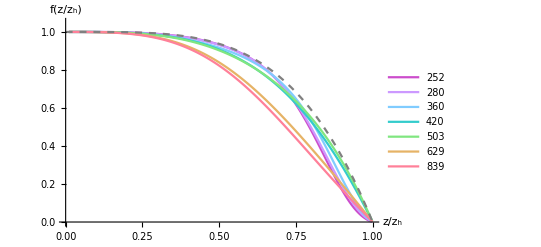

```mathematica
Show[ListLinePlot[Table[{z,fNet[parameters1410reg2[[i,2]],z]},{i,1,Length@parameters1410reg2},{z,gridzs}],PlotStyle->styleRainbow[[2;;]],PlotLegends->parameters1410reg2[[All,1]],PlotRange->{{0,1},{0,1.05}}],Plot[1-z^4,{z,0,1},PlotStyle->{Dashed,Gray}],AxesLabel->{"z/z_h","f(z/z_h)"}]
```

```mathematica
Export["/home/htakko/Desktop/f(z)-1410-reg2.pdf",%752,"PDF"]
```

/home/htakko/Desktop/f(z)-1410-reg2.pdf

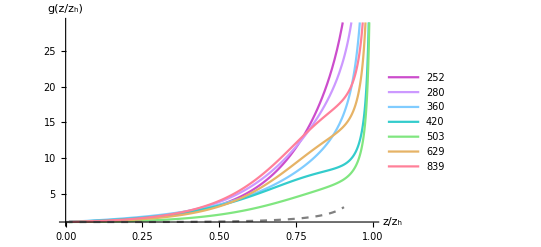

```mathematica
Show[ListLinePlot[Table[{z,gNet[parameters1410reg2[[i,2]],parameters1410reg2[[i,3]],z]},{i,1,Length@parameters1410reg2},{z,gridzs}],PlotStyle->styleRainbow[[2;;]],PlotLegends->parameters1410reg2[[All,1]],PlotRange->{{0,1},{1,29}}],Plot[1/(1-z^4),{z,0,1},PlotStyle->{Dashed,Gray}],AxesLabel->{"z/z_h","g(z/z_h)"}]
```

```mathematica
Export["/home/htakko/Desktop/g(z)-1410-reg2.pdf",%753,"PDF"]
```

/home/htakko/Desktop/g(z)-1410-reg2.pdf

#### Plot f/g ratio

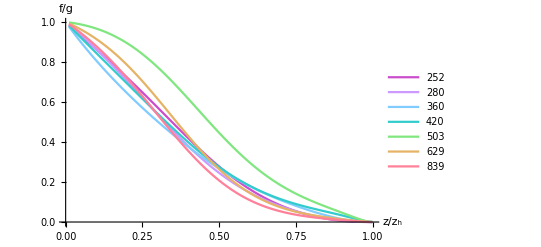

```mathematica
Show[ListLinePlot[Table[{z,fNet[parameters1410reg2[[i,2]],z]/gNet[parameters1410reg2[[i,2]],parameters1410reg2[[i,3]],z]},{i,1,Length@parameters1410reg2},{z,gridzs}],PlotStyle->styleRainbow[[2;;]],PlotLegends->parameters1410reg2[[All,1]],PlotRange->{{0,1},All}],AxesLabel->{"z/z_h","f/g"}]
```

```mathematica
Export["/home/htakko/Desktop/fdividedbyg-1410-reg2.pdf",%505,"PDF"]
```

/home/htakko/Desktop/fdividedbyg-1410-reg2.pdf

### 1607 data

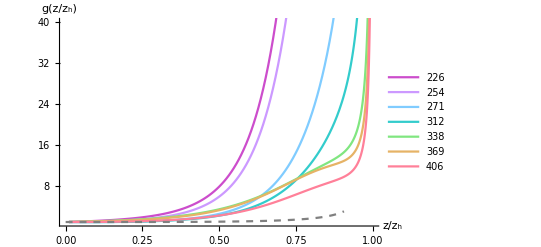

```mathematica
Show[ListLinePlot[Table[{z,gNet[parameters1607reg2[[i,2]],parameters1607reg2[[i,3]],z]},{i,1,Length@parameters1607reg2},{z,gridzs}],PlotStyle->styleRainbow[[2;;]],PlotLegends->parameters1607reg2[[All,1]]],Plot[1/(1-z^4),{z,0,1},PlotStyle->{Dashed,Gray}],PlotRange->{{0,1},{1,40}},AxesLabel->{"z/z_h","g(z/z_h)"}]
```

```mathematica
Export["/home/htakko/Desktop/g(z)-1607-reg2.pdf",%1090,"PDF"]
```

/home/htakko/Desktop/g(z)-1607-reg2.pdf

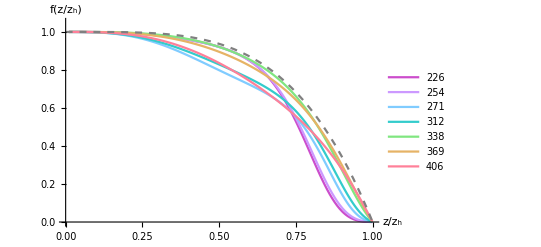

```mathematica
Show[ListLinePlot[Table[{z,fNet[parameters1607reg2[[i,2]],z]},{i,1,Length@parameters1607reg2},{z,gridzs}],PlotStyle->styleRainbow[[2;;]],PlotLegends->parameters1607reg2[[All,1]],PlotRange->{{0,1},{0,1.05}}],Plot[1-z^4,{z,0,1},PlotStyle->{Dashed,Gray}],AxesLabel->{"z/z_h","f(z/z_h)"}]
```

```mathematica
Export["/home/htakko/Desktop/f(z)-1607-reg2.pdf",%1089,"PDF"]
```

/home/htakko/Desktop/f(z)-1607-reg2.pdf

#### Plot f/g ratio

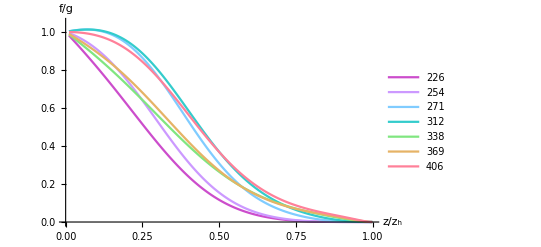

```mathematica
Show[ListLinePlot[Table[{z,fNet[parameters1607reg2[[i,2]],z]/gNet[parameters1607reg2[[i,2]],parameters1607reg2[[i,3]],z]},{i,1,Length@parameters1607reg2},{z,gridzs}],PlotStyle->styleRainbow[[2;;]],PlotLegends->parameters1607reg2[[All,1]],PlotRange->{{0,1},{0,1.05}}],AxesLabel->{"z/z_h","f/g"}]
```

```mathematica
Export["/home/htakko/Desktop/fdividedbyg(z)-1607-reg2.pdf",%500,"PDF"]
```

/home/htakko/Desktop/fdividedbyg(z)-1607-reg2.pdf

```mathematica
ListLinePlot[Table[{z,gNet[parameters1607[[i,2]],parameters1607[[i,3]],z]},{i,{5,6,7}},{z,gridzs}],PlotStyle->styleRainbow[[2;;]],PlotLegends->parameters1607[[All,1]]]
```

```mathematica
ListLinePlot[Table[{z,fNet[parameters1607[[i,2]],z]},{i,{5,6,7}},{z,gridzs}],PlotStyle->styleRainbow[[2;;]],PlotLegends->parameters1607[[All,1]],PlotRange->{{0,1},{0,1.2}}]
```

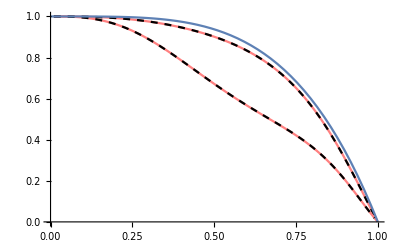

```mathematica
Show[ListLinePlot[Table[{z,fNet[parameters1607[[6,2]],z]},{z,gridzs}],PlotStyle->Pink],ListLinePlot[resultdata16Re[369][[All,{1,2}]],PlotStyle->{Black,Dashed}],ListLinePlot[Table[{z,fNet[parameters1607reg2[[6,2]],z]},{z,gridzs}],PlotStyle->Pink],ListLinePlot[resultdata16ReReg2[369][[All,{1,2}]],PlotStyle->{Black,Dashed}],Plot[1-z^4,{z,0,1}]]
```

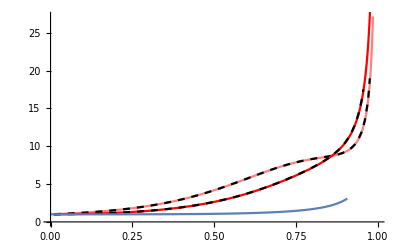

```mathematica
Show[ListLinePlot[Table[{z,gNet[parameters1607[[6,2]],parameters1607[[6,3]],z]},{z,gridzs}],PlotStyle->Pink],ListLinePlot[resultdata16Re[369][[All,{1,3}]],PlotStyle->{Black,Dashed}],ListLinePlot[Table[{z,gNet[parameters1607reg2[[6,2]],parameters1607reg2[[6,3]],z]},{z,gridzs}],PlotStyle->Red],ListLinePlot[resultdata16ReReg2[369][[All,{1,3}]],PlotStyle->{Black,Dashed}],Plot[1/(1-z^4),{z,0,1}]]
```

```mathematica
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/g-network-1607-new-reg-N4.pdf",%314,"PDF"]
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/f-network-1607-new-reg-N4.pdf",%315,"PDF"]
```

/home/htakko/Dropbox/Own/deep-learning-EE/figures/g-network-1607-new-reg-N4.pdf

/home/htakko/Dropbox/Own/deep-learning-EE/figures/f-network-1607-new-reg-N4.pdf

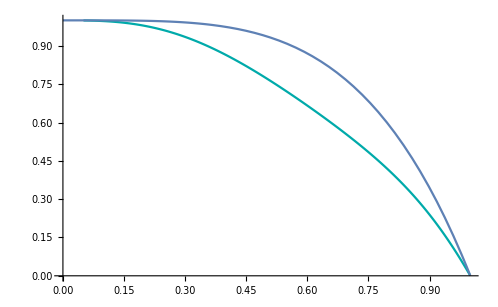

```mathematica
Show[ListLinePlot[Table[{z,fNet[{-3 ,1.5,2},z]},{z,gridzs}],PlotStyle->Darker[Cyan]],Plot[1-z^4,{z,0,1}]]
```

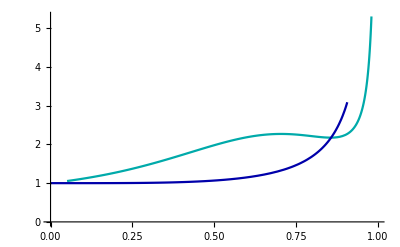

```mathematica
Show[ListLinePlot[Table[{z,gNet[{-3,1.5,2},{1,1,1},z]},{z,gridzs}],PlotStyle->Darker[Cyan]],Plot[1/(1-z^4),{z,0,1},PlotStyle->Darker[Blue]]]
```

```mathematica
Export["/home/htakko/temp2.jpg",%549,"JPEG"]
```

/home/htakko/temp2.jpg

```mathematica
Export["/home/htakko/temp.jpg",%514,"JPEG"]
```

/home/htakko/temp.jpg

Check the conserved quantity and potential equations :

```mathematica
(* Bulk coordinates. *)
X= {t,z,x1,x2,x3}/.x1->x1[z];
(* Metric *)
G=RR^2/z^2 DiagonalMatrix@{
-f[z],g[z],1,1,1};
(* Coordinates on embedding *)
σ={x2,z};
(* Induced metric *)
Gind=Table[(D[X, a]).G.(D[X, b]),{a,σ},{b,σ}]//FullSimplify
FullSimplify[√(-Det[Gind]),{z>0,RR>0}]
```

{{-(RR^2 f[z])/z^2,0},{0,(RR^2 (g[z]+x1'[z]^2))/z^2}}

√((RR^4 f[z] (g[z]+x1'[z]^2))/z^4)

```mathematica
Clear[f,g]
```

```mathematica
Lagr = z^-2(f[z](g[z]+x1'[z]^2))^(1/2);
(D[Lagr, x1'[z]])//FullSimplify
%/.z->z0
Limit[%,x1'[z0]->∞]
```

(f[z] x1'[z])/(z^2 √(f[z] (g[z]+x1'[z]^2)))

(f[z0] x1'[z0])/(z0^2 √(f[z0] (g[z0]+x1'[z0]^2)))

(√f[z0])/z0^2

```mathematica
Solve[{(D[Lagr, x1'[z]])==f[z0]^(1/2)/z0^2},x1'[z]]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{x1'[z]→-(z^2 √f[z0] √g[z])/(√(z0^4 f[z]-z^4 f[z0]))},{x1'[z]→(z^2 √f[z0] √g[z])/(√(z0^4 f[z]-z^4 f[z0]))}}

```mathematica
Clear[f,g]
```

```mathematica
Lagr/.x1'[z]->(√g[z])/(√((z0^4 f[z])/(z^4 f[z0])-1))//FullSimplify
Limit[%,z0->∞]
```

(√((z0^4 f[z]^2 g[z])/(z0^4 f[z]-z^4 f[z0])))/z^2

lim_(z0→∞) (√((z0^4 f[z]^2 g[z])/(z0^4 f[z]-z^4 f[z0])))/z^2

```mathematica
f[z_]:=1-z^4
g[z_]:=1/(1-z^4)
```

SEPARATION AND POTENTAL
update: use regularization of
V(z_*) = R^2/πα'(∫_ϵ)^(z_*)1/z^2(√((f(z)g(z))/(1-(z^4 f(z_*))/((z_*)^4 f(z))))-1)dz-R^2/πα' 1/(z_*)

```mathematica
computeLnetz[as_List,bs_List,zs_]:=2/π NIntegrate[(√gNet[as,bs,z])/(√((zs^4 fNet[as,z])/(z^4 fNet[as,zs])-1)),{z,0,zs}]
computeVnetz[as_List,bs_List,zs_]:=2π(NIntegrate[1/z^2((√(fNet[as,z]gNet[as,bs,z]))/(√(1-(z^4 fNet[as,zs])/(zs^4 fNet[as,z])))-1),{z,10^-2,zs}]-1/zs);(*2NIntegrate[(√((zs^4 fNet[as,z]^2 gNet[as,bs,z])/(zs^4 fNet[as,z]-z^4 fNet[as,zs])))/z^2-(√(gNet[as,bs,z]fNet[as,z]))/z^2,{z,0,zs}]-2NIntegrate[(√(gNet[as,bs,z]fNet[as,z]))/z^2,{z,zs,1}]*)
```

Functions to run to compute thze V and L in these coordinates, z = z_*(1-y^2)

```mathematica
Solve[ϵ==zs(1-y^2),y]//FullSimplify
```

{{y→-(√(zs-ϵ))/(√zs)},{y→(√(zs-ϵ))/(√zs)}}

```mathematica
(√(zs-ϵ))/(√zs)-√(1-ϵ/zs)//FullSimplify
```

(√(zs-ϵ))/(√zs)-√(1-ϵ/zs)

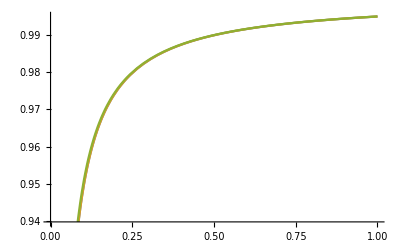

```mathematica
Plot[{(√(zs-ϵ))/(√zs)/.ϵ->0.01,√(1-ϵ/zs)/.ϵ->0.01,1-1/2(ϵ/zs)/.ϵ->0.01},{zs,0,1}]
```

```mathematica
Clear[computeLnet,computeVnetReg1,computeVnetReg2]
computeLnet[as_List,bs_List,zs_]:=4/π NIntegrate[(zs y √gNet[as,bs,z])/(√(fNet[as,z]/((1-y^2)^4 fNet[as,zs])-1))/.z->zs(1-y^2),{y,0,1}];computeVnetReg2[as_List,bs_List,zs_]:=2π NIntegrate[(2 y)/(zs(1-y^2)^2)((√(fNet[as,zs(1-y^2)]gNet[as,bs,zs(1-y^2)]))/(√(1-((1-y^2)^4 fNet[as,zs])/fNet[as,zs(1-y^2)]))-1),{y,0,√(1-10^-4/zs)}]-(2π)/zs;computeVnetReg1[as_List,bs_list,zs_]:=4 π NIntegrate[(√(fNet[as,z]gNet[as,bs,z]))/((1-y^2)^2)(1/(√(1-((1-y^2)^4 fNet[as,zs])/fNet[as,z]))-1)/.z->zs(1-y^2),{y,0,1}](*2π NIntegrate[(√(fNet[as,z]gNet[as,bs,z]))/z^2,{z,zs,1}]*)
```

The derivative of L wrt zs:

```mathematica
D[4/π Integrate[(zs y √gNet[as,bs,z])/(√(fNet[as,z]/((1-y)^4 fNet[as,zs])-1))/.z->zs(1-y^2),{y,0,1}],zs]//FullSimplify
```

```mathematica
Solve[zs==zs(1-y^2),y]
```

{{y→0},{y→0}}

To compute the potential from complex values of embedding, use the curve zs from the network code:

```mathematica
Clear[zsComplex1410,zsComplex1607,zsComplex1410Reg2,zsComplex1607Reg2]
(*Do[zsComplex1410[T]=resultdata14Imag[T][[All,1]],{T,{252,280,315,420,503,629,839}}];*)
Do[zsComplex1410Reg2[T]=resultdata14ImagReg2[T][[All,1]],{T,{252,280,360,420,503,629,839}}];
(*Do[zsComplex1607[T]=resultdata16Imag[T][[All,1]],{T,{271,312,338,369,406}}];*)
Do[zsComplex1607Reg2[T]=resultdata16ImagReg2[T][[All,1]],{T,{271,312,338,369,406}}];
```

Part::partd: Part specification resultdata14ImagReg2[252]⟦All,1⟧ is longer than depth of object.

Part::partd: Part specification resultdata14ImagReg2[280]⟦All,1⟧ is longer than depth of object.

Part::partd: Part specification resultdata14ImagReg2[360]⟦All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Compute potential for 1410 parameters:

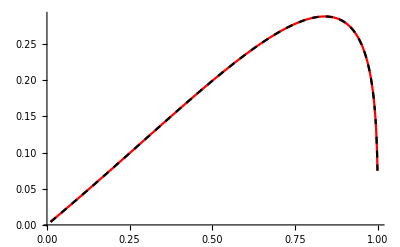

```mathematica
Show[ListLinePlot[Table[{zs,computeLnet[{0.5,-0.5},{0.5,-0.5},zs]},{zs,gridzs}],PlotStyle->Red],ListLinePlot[Table[{zs,computeLnetz[{0.5,-0.5},{0.5,-0.5},zs]},{zs,gridzs}],PlotStyle->{Black,Dashed}],PlotRange->All]
```

Compute potential for 1607 parameters:

```mathematica
Clear[potentials1607]
Monitor[Do[
T=parameters1607[[i,1]];
coef=parameters1607[[i,4]];
potentials1607[T]=Table[{zs,computeLnet[parameters1607[[i,2]],parameters1607[[i,3]],zs],coef*computeVnetReg1[parameters1607[[i,2]],parameters1607[[i,3]],zs]},{zs,gridzs}],{i,1,Length[parameters1607[[All,1]]]}],N[T]]
```

```mathematica
Clear[complexpotentials1607,complexpotentials1607Reg2]
Monitor[Do[
T=parameters1607[[i,1]];
coef=0.15089977670036966;
complexpotentials1607[T]=Table[{zs,computeLnet[parameters1607[[i,2]],parameters1607[[i,3]],zs],computeVnetReg1[parameters1607[[i,2]],parameters1607[[i,3]],zs]},{zs,zsComplex1607[T]}],{i,1,Length[parameters1607[[All,1]]]}],N[T]]
```

Compute potentials for 1607 parameters with new regularisation:

```mathematica
Clear[potentials1607Reg2]
Monitor[Do[
T=parameters1607reg2[[i,1]];
coef=0.15660072715672804;
shift=parameters1607reg2[[i,5]];
potentials1607Reg2[T]=Table[{zs,computeLnetz[parameters1607reg2[[i,2]],parameters1607reg2[[i,3]],zs],coef*computeVnetz[parameters1607reg2[[i,2]],parameters1607reg2[[i,3]],zs]+shift},{zs,gridzs}],{i,3,Length[parameters1607reg2[[All,1]]]}],N[T]]
```

```mathematica
Clear[complexpotentials1607Reg2]
Monitor[Do[
T=parameters1607reg2[[i,1]];
coef=0.15089977670036966;
shift=parameters1607reg2[[i,5]];
complexpotentials1607Reg2[T]=Table[{zs,computeLnetz[parameters1607reg2[[i,2]],parameters1607reg2[[i,3]],zs],coef*computeVnetz[parameters1607reg2[[i,2]],parameters1607reg2[[i,3]],zs]+shift},{zs,zsComplex1607Reg2[T]}],{i,3,Length[parameters1607reg2[[All,1]]]}],N[T]]
```

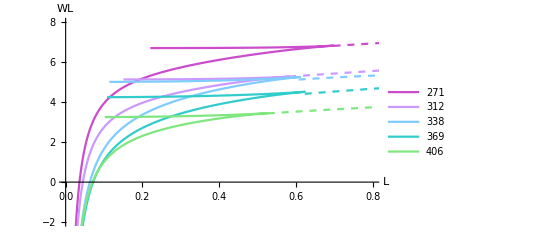

```mathematica
Show[(*ListLinePlot[Re[complexValuesPotential⟦All,{1,3}⟧],PlotStyle-> {Black,Dashed}],
ParametricPlot[{(π zH)^-1 distance[ζs],zH VqqAnalytic[ζs]},{ζs,0.25,1-10^-6},PlotStyle-> Black],*)ListLinePlot[Table[Re@complexpotentials1607Reg2[T][[All,{2,3}]],{T,parameters1607reg2[[3;;,1]]}],PlotStyle->dashedStyleRainbow[[2;;]]],ListLinePlot[Table[Re@potentials1607Reg2[T][[All,{2,3}]],{T,parameters1607reg2[[3;;,1]]}],PlotStyle->styleRainbow[[2;;]],PlotLegends->parameters1607reg2[[3;;,1]]],AxesLabel->{"L","WL"},BaseStyle->{Thick,FontSize->12},AxesStyle->Thick,AxesOrigin->{0,0},{PlotRange->{{0,0.8},{-2,8}}}]
```

```mathematica
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/1607-network-V(L)-new-reg-N4.pdf",%335,"PDF"]
```

/home/htakko/Dropbox/Own/deep-learning-EE/figures/1607-network-V(L)-new-reg-N4.pdf

## Network vs data vs IHQCD

To start with, let’s work with three different temperatures, from the IHQCD notebook:
T_c = 271 MeV
1.3 T_c = 345 MeV
2 T_c= 530 MeV
So from the network, the temperatures we can run from the data are 271, 338 and 406

### T = 271

```mathematica
dataRe1=Import[NotebookDirectory[]<>"data/1607.04049/ReVQuenched.dat"];
dataIm1=Import[NotebookDirectory[]<>"data/1607.04049/ImVQuenched.dat"];
Tidx1=4;
Print["Using T = ",T1=Union[dataRe1⟦;;,1⟧]⟦Tidx1⟧," GeV."]
dataRe1=Rest/@Select[dataRe1,First[#]==T1&];
dataIm1=Rest/@Select[dataIm1,First[#]==T1&];
```

Using T = 0.270667 GeV.

```mathematica
l1=dataRe1⟦;;,1⟧;
l1==dataIm1⟦;;,1⟧
ReV1=dataRe1⟦;;,2⟧;
ReVσ1=dataRe1⟦;;,3⟧;
ImV1=dataIm1⟦;;,2⟧;
ImVσ1=dataIm1⟦;;,3⟧;
```

True

This plot doesn’t have the manual shifts that Fig. 2 has.

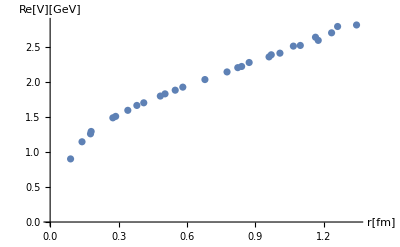

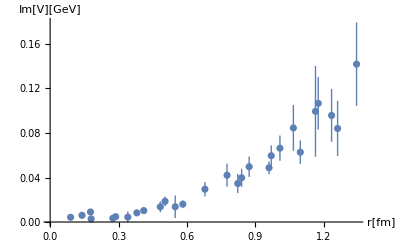

```mathematica
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataRe1,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Re[V][GeV]"}]
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataIm1,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Im[V][GeV]"}]
```

Interestingly, the dataset seems to be missing a few data points compared to Fig. 2. Im[V] extends to slightly higher r in the paper.

### Export data

Our statistical model expects data in the dimensionless combinations (T r,V/T). In addition, we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
```

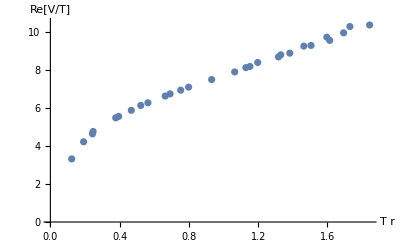

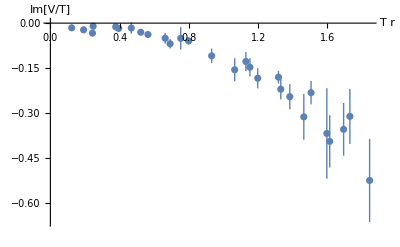

```mathematica
ListPlot[{T1 fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T1,(#⟦3⟧)/T1]}&/@dataRe1,AxesLabel->{"T r","Re[V/T]"}]
ListPlot[{T1 fmToInvGeV[#⟦1⟧],Around[-(#⟦2⟧)/T1,(#⟦3⟧)/T1]}&/@dataIm1,AxesLabel->{"T r","Im[V/T]"}]
```

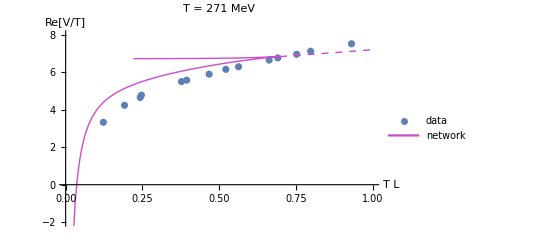

```mathematica
Show[ListPlot[{T1 fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T1,(#⟦3⟧)/T1]}&/@dataRe1,AxesLabel->{"T L","Re[V/T]"},PlotLegends->Placed[{"data"},{0.49,0.4}]],ListLinePlot[Table[Re@complexpotentials1607Reg2[T][[All,{2,3}]],{T,{271}}],PlotStyle->dashedStyleRainbow[[2;;]]],ListLinePlot[Table[Re@potentials1607Reg2[T][[All,{2,3}]],{T,{271}}],PlotStyle->styleRainbow[[2;;]],PlotLegends->Placed[{"network"},{0.5,0.3}]],BaseStyle->{Thick,FontSize->12},AxesStyle->Thick,AxesOrigin->{0,0},{PlotRange->{{0,1.},{-2,8}}},PlotLabel->"T = 271 MeV"]
```

### T = 338

```mathematica
dataRe2=Import[NotebookDirectory[]<>"data/1607.04049/ReVQuenched.dat"];
dataIm2=Import[NotebookDirectory[]<>"data/1607.04049/ImVQuenched.dat"];
Tidx2=7;
Print["Using T = ",T2=Union[dataRe2⟦;;,1⟧]⟦Tidx2⟧," GeV."]
dataRe2=Rest/@Select[dataRe2,First[#]==T2&];
dataIm2=Rest/@Select[dataIm2,First[#]==T2&];
```

Using T = 0.338333 GeV.

```mathematica
l2=dataRe2⟦;;,1⟧;
l2==dataIm2⟦;;,1⟧
ReV2=dataRe2⟦;;,2⟧;
ReVσ2=dataRe2⟦;;,3⟧;
ImV2=dataIm2⟦;;,2⟧;
ImVσ2=dataIm2⟦;;,3⟧;
```

True

This plot doesn’t have the manual shifts that Fig. 2 has.

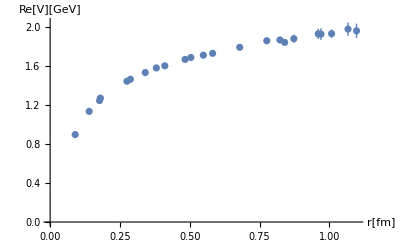

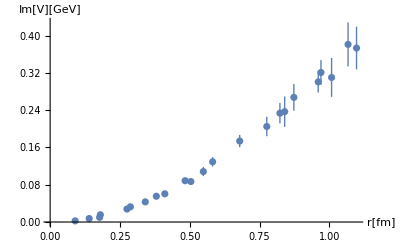

```mathematica
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataRe2,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Re[V][GeV]"}]
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataIm2,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Im[V][GeV]"}]
```

Interestingly, the dataset seems to be missing a few data points compared to Fig. 2. Im[V] extends to slightly higher r in the paper.

### Export data

Our statistical model expects data in the dimensionless combinations (T r,V/T). In addition, we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
```

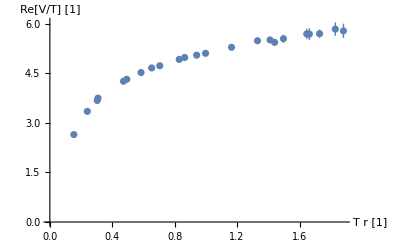

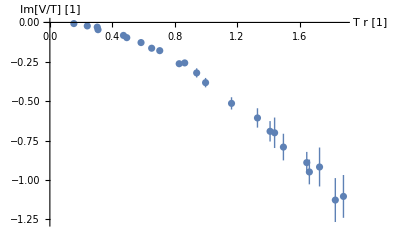

```mathematica
ListPlot[{T2 fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T2,(#⟦3⟧)/T2]}&/@dataRe2,AxesLabel->{"T r [1]","Re[V/T] [1]"}]
ListPlot[{T2 fmToInvGeV[#⟦1⟧],Around[-(#⟦2⟧)/T2,(#⟦3⟧)/T2]}&/@dataIm2,AxesLabel->{"T r [1]","Im[V/T] [1]"}]
```

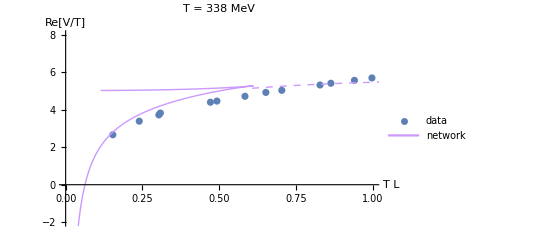

```mathematica
Show[ListPlot[{T2 fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T2,(#⟦3⟧)/T2]}&/@dataRe,AxesLabel->{"T L","Re[V/T]"},PlotLegends->Placed[{"data"},{0.49,0.4}]],ListLinePlot[Table[Re@complexpotentials1607Reg2[T][[All,{2,3}]],{T,{338}}],PlotStyle->dashedStyleRainbow[[3;;]]],ListLinePlot[Table[Re@potentials1607Reg2[T][[All,{2,3}]],{T,{338}}],PlotStyle->styleRainbow[[3;;]],PlotLegends->Placed[{"network"},{0.5,0.3}]],BaseStyle->{Thick,FontSize->12},AxesStyle->Thick,AxesOrigin->{0,0},{PlotRange->{{0,1.},{-2,8}}},PlotLabel->"T = 338 MeV"]
```

### T = 406

```mathematica
dataRe3=Import[NotebookDirectory[]<>"data/1607.04049/ReVQuenched.dat"];
dataIm3=Import[NotebookDirectory[]<>"data/1607.04049/ImVQuenched.dat"];
Tidx3=9;
Print["Using T = ",T3=Union[dataRe3⟦;;,1⟧]⟦Tidx3⟧," GeV."]
dataRe3=Rest/@Select[dataRe3,First[#]==T3&];
dataIm3=Rest/@Select[dataIm3,First[#]==T3&];
```

Using T = 0.406 GeV.

```mathematica
l3=dataRe3⟦;;,1⟧;
l3==dataIm3⟦;;,1⟧
ReV3=dataRe3⟦;;,2⟧;
ReVσ3=dataRe3⟦;;,3⟧;
ImV3=dataIm3⟦;;,2⟧;
ImVσ3=dataIm3⟦;;,3⟧;
```

True

This plot doesn’t have the manual shifts that Fig. 2 has.

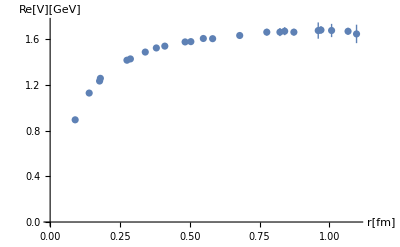

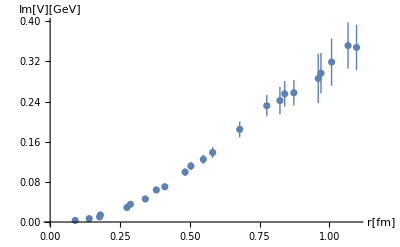

```mathematica
Show[ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataRe3,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Re[V][GeV]"}]]
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataIm3,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Im[V][GeV]"}]
```

Interestingly, the dataset seems to be missing a few data points compared to Fig. 2. Im[V] extends to slightly higher r in the paper.

### Export data

Our statistical model expects data in the dimensionless combinations (T r,V/T). In addition, we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
```

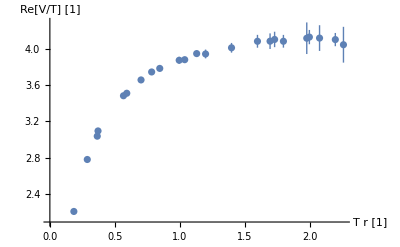

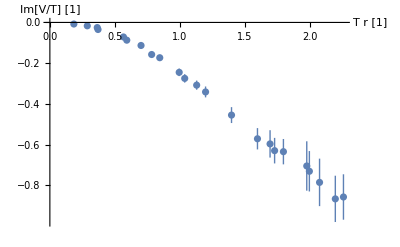

```mathematica
ListPlot[{T3 fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T3,(#⟦3⟧)/T3]}&/@dataRe3,AxesLabel->{"T r [1]","Re[V/T] [1]"}]
ListPlot[{T3 fmToInvGeV[#⟦1⟧],Around[-(#⟦2⟧)/T3,(#⟦3⟧)/T3]}&/@dataIm3,AxesLabel->{"T r [1]","Im[V/T] [1]"}]
```

### T = 369

```mathematica
dataRe4=Import[NotebookDirectory[]<>"data/1607.04049/ReVQuenched.dat"];
dataIm4=Import[NotebookDirectory[]<>"data/1607.04049/ImVQuenched.dat"];
Tidx4=8;
Print["Using T = ",T4=Union[dataRe4⟦;;,1⟧]⟦Tidx4⟧," GeV."]
dataRe4=Rest/@Select[dataRe4,First[#]==T4&];
dataIm4=Rest/@Select[dataIm4,First[#]==T4&];
```

Using T = 0.369091 GeV.

```mathematica
l4=dataRe4⟦;;,1⟧;
l4==dataIm4⟦;;,1⟧
ReV4=dataRe4⟦;;,2⟧;
ReVσ4=dataRe4⟦;;,3⟧;
ImV4=dataIm4⟦;;,2⟧;
ImVσ4=dataIm4⟦;;,3⟧;
```

True

This plot doesn’t have the manual shifts that Fig. 2 has.

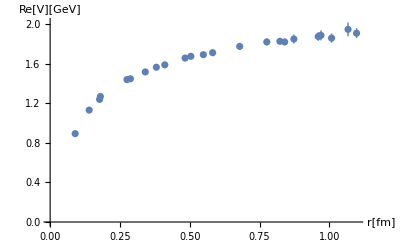

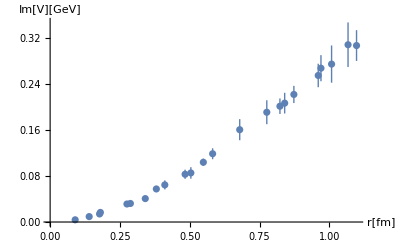

```mathematica
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataRe4,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Re[V][GeV]"}]
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataIm4,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Im[V][GeV]"}]
```

Interestingly, the dataset seems to be missing a few data points compared to Fig. 2. Im[V] extends to slightly higher r in the paper.

### Export data

Our statistical model expects data in the dimensionless combinations (T r,V/T). In addition, we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
```

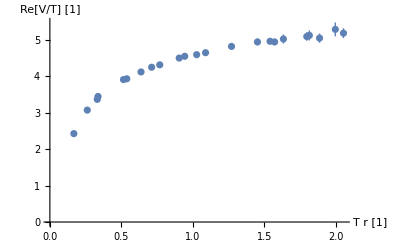

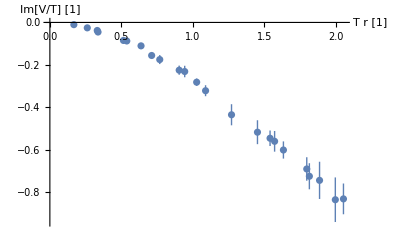

```mathematica
ListPlot[{T4 fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T4,(#⟦3⟧)/T4]}&/@dataRe4,AxesLabel->{"T r [1]","Re[V/T] [1]"}]
ListPlot[{T4 fmToInvGeV[#⟦1⟧],Around[-(#⟦2⟧)/T4,(#⟦3⟧)/T4]}&/@dataIm4,AxesLabel->{"T r [1]","Im[V/T] [1]"}]
```

```mathematica
Export[NotebookDirectory[]<>"1607latticeT369.txt",{T fmToInvGeV[l],ReV/T,ReVσ/T,-ImV/T,ImVσ/T},"Table"]
```

/home/local/htakko/Dropbox/Own/deep-learning-EE/env/complex_wilson/1607latticeT369.txt

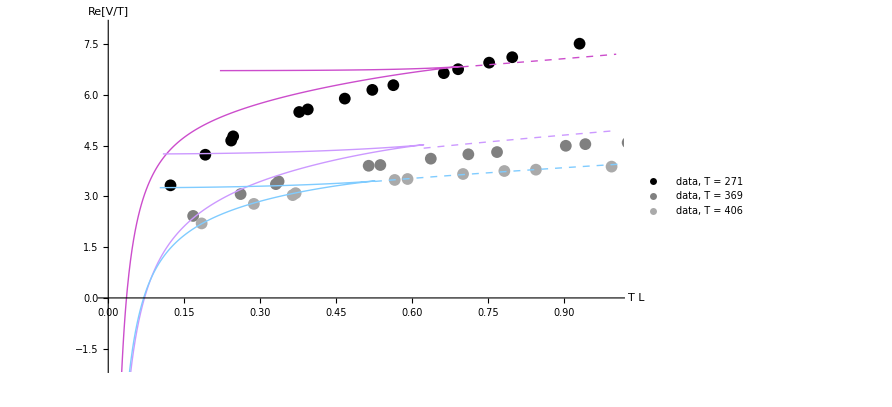

```mathematica
Show[ListPlot[{T1 fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T1,(#⟦3⟧)/T1]}&/@dataRe,AxesLabel->{"T L","Re[V/T]"},PlotLegends->Placed[{"data, T = 271"},Bottom],PlotStyle->Black],ListPlot[{T4 fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T4,(#⟦3⟧)/T4]}&/@dataRe4,AxesLabel->{"T L","Re[V/T]"},PlotLegends->Placed[{"data, T = 369"},Bottom],PlotStyle->Gray],ListPlot[{T3 fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T3,(#⟦3⟧)/T3]}&/@dataRe3,AxesLabel->{"T L","Re[V/T]"},PlotLegends->Placed[{"data, T = 406"},Bottom],PlotStyle->Lighter[Gray]],ListLinePlot[Table[Re@complexpotentials1607Reg2[T][[All,{2,3}]],{T,{271,369,406}}],PlotStyle->dashedStyleRainbow[[2;;]]],ListLinePlot[Table[Re@potentials1607Reg2[T][[All,{2,3}]],{T,{271,369,406}}],PlotStyle->styleRainbow[[2;;]],PlotLegends->Placed[{"network, T = 271","network, T = 369","network, T = 406"},Right]],BaseStyle->{Thick,FontSize->12},AxesStyle->Thick,AxesOrigin->{0,0},{PlotRange->{{0,1.},{-2,8}}}]
```

```mathematica
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/3-example-T-network-vs-data-NEW.png",%242,"PDF"]
```

/home/htakko/Dropbox/Own/deep-learning-EE/figures/3-example-T-network-vs-data-NEW.png

## Compute EE

Compute the potential using f(z) and g(z) numerically obtained from network training. Plot for all the temperatures, plot as V(L) s.t. can do parametric plot wrt z_* and we don’t need to evaluate the functions at that point. Formulas are
V(z_*)=TR^2/(π α')(∫_0)^(z_*)(√(f(z)g(z)))/z^2(1/(√(1-(z^4 f(z_*))/((z_*)^4 f(z))))-1)dz -TR^2/πα' 2(∫^1)_(z_*)(√(f(z)g(z)))/z^2 dz
l(z_*)= 2(∫_0)^(z_*)(√(g(z)))/(√(((z_*)^4 f(z))/(z^4 f(z_*))-1))dz

note that the metric and functions are in string frame and entropy would need to be in einstein frame --> how do we do this? dilaton from where?

The entropy equations for strip in z=x_1(z) (NOTE: in overleaf and WL, we have rectangle in (t,x_1)-plane at large T (0 <= t <= T). In the case of strip in z = x_1(z) we have actually time independent EE, and so only depend on the function g(z):
S_A(z_*) = (L^3 vol(R^2))/(2 G_5)((l(z_*))/(2(z_*)^3)+(∫_0)^(z_*)(√(g(z))√((z_*)^6-z^6))/((z_*)^3 z^3)dz) 
             = (L^3 vol(R^2))/(2 G_5)(∫_0)^(z_*)((z^3 √(g(z)))/((z_*)^3 √((z_*)^6-z^6))+(√(g(z))√((z_*)^6-z^6))/((z_*)^3 z^3)dz)
l(z_*)=2(∫_0)^(z_*)(z^3 √(g(z)))/(√((z_*)^6-z^6))dz
The entropy simplifies to
S_A(z_*) = (L^3 vol(R^2))/(2 G_5)((∫_0)^(z_*)(√(g(z))(z_*)^3)/(z^3 √((z_*)^6-z^6))dz)
From Niko’s paper JHEP12(2023)137 we would have
l(z_*)=2/πz_h(∫_0)^(z_*)(z^3 √(g(z)))/(√((z_*)^6-z^6))dz
 (4 G^5)/(R^3 V T^2)S_A(z_*) = 2 π^2 z_h^2(∫_0)^(z_*)(√(g(z))(z_*)^3)/(z^3 √((z_*)^6-z^6))dz
which agrees to the eqs above. Below are functions to compute EE directly from numerical data from the code.

```mathematica
Action=1/z^3 √(g[z]+x1'[z]^2);
D[Action, x1'[z]]/.z->zs
Limit[%,x1'[zs]->∞]
Solve[D[Action, x1'[z]]==%,x1'[z]]
```

x1'[zs]/(zs^3 √(g[zs]+x1'[zs]^2))

1/zs^3

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{x1'[z]→-(z^3 √g[z])/(√(-z^6+zs^6))},{x1'[z]→(z^3 √g[z])/(√(-z^6+zs^6))}}

```mathematica
Action/.x1'[z]->(z^3 √g[z])/(√(-z^6+zs^6))//FullSimplify
Limit[%,zs->∞]
```

(√((zs^6 g[z])/(-z^6+zs^6)))/z^3

(√g[z])/z^3

```mathematica
computedistanceEE[zs_?NumericQ]:=2NIntegrate[(√((zs^6 gNet[as,bs,z])/(-z^6+zs^6)))/z^3,{z,0.01,zs}];
```

```mathematica
(√g[z])/(z^3 √(1-z^6/zs^6))/.zs->∞//Simplify
```

(√g[z])/z^3

Here are functions to compute EE using the network g(z) and f(z) definitions and only a and b required from the code:

CHECK the regularizarion of EE - from ϵ to z_* instead of zero. subtract inside the integrand of divergent terms from g(z), disconnectd piece is just (√(g(z)))/z^3 so subtract that, have full integral fom ϵ to  z_*

```mathematica
Clear[computeEEnet,computedistanceEEnet]
computedistanceEEnet[as_List,bs_List,zs_]:=2NIntegrate[(z^3 √gNet[as,bs,z])/(√(-z^6+zs^6)),{z,0.001,zs}]
computeEEnet[as_List,bs_List,zs_]:=2NIntegrate[(√((zs^6 gNet[as,bs,z])/(-z^6+zs^6)))/z^3-(√gNet[as,bs,z])/z^3,{z,0.001,zs}]-2NIntegrate[(√gNet[as,bs,z])/z^3,{z,zs,1}];
sameSpacedGrid[in_,fin_,NPoints_:100]:=Table[in+(k (fin-in))/NPoints,{k,1,NPoints}];
gridzs=Join[sameSpacedGrid[0.05,1/10],sameSpacedGrid[1/10,9/10],sameSpacedGrid[9/10,0.999]];
```

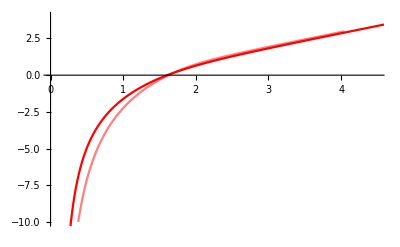

```mathematica
Show[ListLinePlot[Table[{computedistanceEEnet[parameters1607[[6,2]],parameters1607[[6,3]],zs],computeEEnet[parameters1607[[6,2]],parameters1607[[6,3]],zs]},{zs,gridzs}],PlotRange->{{0,4.5},{-10,4}},PlotStyle->Pink],ListLinePlot[Table[{computedistanceEEnet[parameters1607reg2[[6,2]],parameters1607reg2[[6,3]],zs],computeEEnet[parameters1607reg2[[6,2]],parameters1607reg2[[6,3]],zs]},{zs,gridzs}],PlotStyle->Red]]
```

Compute entanglement entropy for 1410’s parameters:

```mathematica
Clear[EEs1410reg1,EEs1410reg2]
Monitor[Do[
T=parameters1410[[i,1]];
EEs1410reg1[T]=Table[{zs,computedistanceEEnet[parameters1410[[i,2]],parameters1410[[i,3]],zs],computeEEnet[parameters1410[[i,2]],parameters1410[[i,3]],zs]},{zs,gridzs}],{i,1,Length[parameters1410[[All,1]]]}],N[T]]
```

```mathematica
Monitor[Do[
T=parameters1410reg2[[i,1]];
EEs1410reg2[T]=Table[{zs,computedistanceEEnet[parameters1410reg2[[i,2]],parameters1410reg2[[i,3]],zs],computeEEnet[parameters1410reg2[[i,2]],parameters1410reg2[[i,3]],zs]},{zs,gridzs}],{i,1,Length[parameters1410reg2[[All,1]]]}],N[T]]
```

Compute entanglement entropy for 1607’s parameters:

```mathematica
Clear[EEs1607reg1,EEs1607reg2]
Monitor[Do[
T=parameters1607[[i,1]];
EEs1607reg1[T]=Table[{zs,computedistanceEEnet[parameters1607[[i,2]],parameters1607[[i,3]],zs],computeEEnet[parameters1607[[i,2]],parameters1607[[i,3]],zs]},{zs,gridzs}],{i,1,Length[parameters1607[[All,1]]]}],N[T]]
```

```mathematica
Monitor[Do[
T=parameters1607reg2[[i,1]];
EEs1607reg2[T]=Table[{zs,computedistanceEEnet[parameters1607reg2[[i,2]],parameters1607reg2[[i,3]],zs],computeEEnet[parameters1607reg2[[i,2]],parameters1607reg2[[i,3]],zs]},{zs,gridzs}],{i,1,Length[parameters1607reg2[[All,1]]]}],N[T]]
```

Plot the results

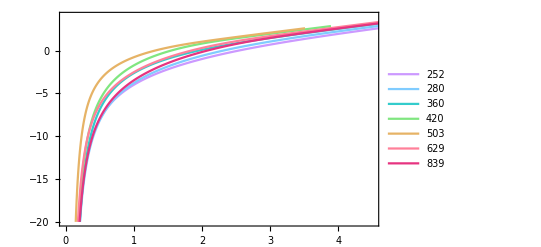

```mathematica
ListLinePlot[Table[EEs1410reg2[T][[All,{2,3}]],{T,parameters1410reg2[[All,1]]}],PlotLegends->parameters1410reg2[[All,1]],PlotRange->{{0,4.5},{-20,4}},PlotStyle->styleRainbow[[3;;]],Frame->{{True,False},{True,False}},FrameStyle->{{{Black,Thickness[0.002],FontSize->15},{Black,Thickness[0.002],FontSize->15}},{{Black,Thickness[0.002],FontSize->15},{Black,Thickness[0.002],FontSize->15}}},(*FrameTicks->{{0.5,1,1.5},{10100,10300}},Axes->None,*)ImageSize->400]
```

```mathematica
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/EE-1410-reg2.pdf",%1112,"PDF"]
```

/home/htakko/Dropbox/Own/deep-learning-EE/figures/EE-1410-reg2.pdf

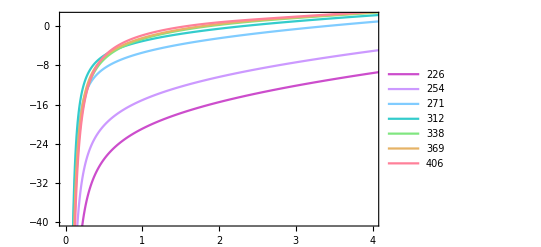

```mathematica
Show[ListLinePlot[Table[EEs1607reg2[T][[All,{2,3}]],{T,parameters1607reg2[[All,1]]}],PlotLegends->parameters1607reg2[[All,1]],PlotRange->Automatic,PlotStyle->styleRainbow[[2;;]]],Frame->{{True,False},{True,False}},FrameStyle->{{{Black,Thickness[0.002],FontSize->15},{Black,Thickness[0.002],FontSize->15}},{{Black,Thickness[0.002],FontSize->15},{Black,Thickness[0.002],FontSize->15}}}(*,FrameTicks->{{0.5,1,1.5},{10200,10400}},210Axes->None*),PlotRange->{{0,4},{-40,2}},ImageSize->400]
```

```mathematica
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/EE-1607-reg2.pdf",%1121,"PDF"]
```

/home/htakko/Dropbox/Own/deep-learning-EE/figures/EE-1607-reg2.pdf

```mathematica
Do[EEvsl1410reg2[T]=Interpolation@EEs1410reg2[T][[All,{2,3}]],{T,parameters1410reg2[[All,1]]}]
Do[dEEdl1410reg2[T]=EEvsl1410reg2[T]',{T,parameters1410reg2[[All,1]]}]
Do[EEvsl1607reg2[T]=Interpolation@EEs1607reg2[T][[All,{2,3}]],{T,parameters1607reg2[[All,1]]}]
Do[dEEdl1607reg2[T]=EEvsl1607reg2[T]',{T,parameters1607reg2[[All,1]]}]
```

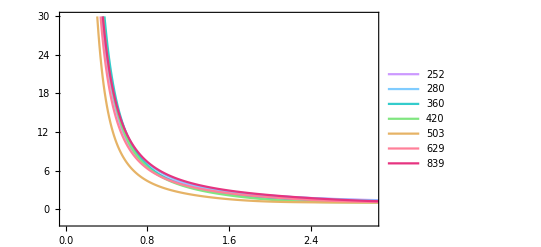

```mathematica
ListLinePlot[Table[dEEdl1410reg2[T],{T,parameters1410reg2[[All,1]]}],PlotRange->{{0,3},{-2,30}},PlotLegends->parameters1410reg2[[All,1]],PlotStyle->styleRainbow[[3;;]],Frame->{{True,False},{True,False}},FrameStyle->{{{Black,Thickness[0.002],FontSize->15},{Black,Thickness[0.002],FontSize->15}},{{Black,Thickness[0.002],FontSize->15},{Black,Thickness[0.002],FontSize->15}}}(*,FrameTicks->{{0.5,1,1.5},{10200,10400}},210Axes->None*),ImageSize->400]
```

```mathematica
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/dEEdl-1410.pdf",%2145,"PDF"]
```

/home/htakko/Dropbox/Own/deep-learning-EE/figures/dEEdl-1410.pdf

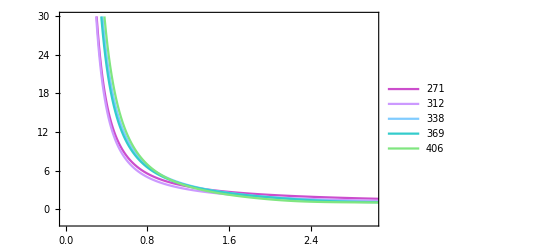

```mathematica
ListLinePlot[Table[dEEdl1607reg2[T],{T,parameters1607reg2[[All,1]]}],PlotRange->{{0,3},{-2,30}},PlotLegends->parameters1607reg2[[All,1]],PlotStyle->styleRainbow[[2;;]],Frame->{{True,False},{True,False}},FrameStyle->{{{Black,Thickness[0.002],FontSize->15},{Black,Thickness[0.002],FontSize->15}},{{Black,Thickness[0.002],FontSize->15},{Black,Thickness[0.002],FontSize->15}}}(*,FrameTicks->{{0.5,1,1.5},{10200,10400}},210Axes->None*),ImageSize->400]
```

```mathematica
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/dEEdl-1607.pdf",%2146,"PDF"]
```

/home/htakko/Dropbox/Own/deep-learning-EE/figures/dEEdl-1607.pdf

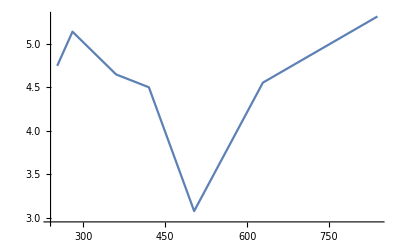

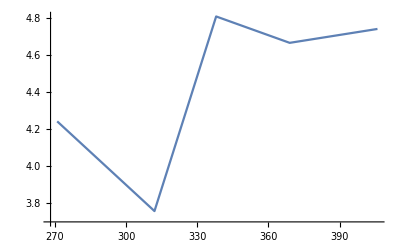

```mathematica
ListLinePlot[Table[{T,dEEdl1410reg2[T][1]},{T,parameters1410reg2[[All,1]]}]]
ListLinePlot[Table[{T,dEEdl1607reg2[T][1]},{T,parameters1607reg2[[All,1]]}]]
```

## Thermal entropy from metric

```mathematica
parameters1607[[All,1]]
```

{226,254,271,290,312,338,369,406}

Check the temperature data points: see what does the EE(T) curve looks like. See https://helda.helsinki.fi/server/api/core/bitstreams/7951f369-b666-48bd-a856-2554f96a5694/content sect. 3 particularly eq. (3.13), where it states that 
S_thermal=VR^3/(4 G_5 z_h^3)l = π^2/2 N_c^2 V l T^3 so is ∝ T^3.

```mathematica
Clear[zh]
```

```mathematica
(*Temperature[zh_,as_List,bs_List]:=1/(π zh)Sqrt[Exp[-aNet[as,1]-bNet[as,bs,1]]]/.zh->1*)
(*Sth[zh_,Rα_]:=Rα^4 π/(2 zh);*)
Sth[zh_,Rα_]:=-Rα^4 π/(2zh);
Temperature[as_List,bs_List,zh_]:=1/(π zh)Sqrt[Exp[aNet[as,1]/bNet[as,bs,1]]]
zh[T_,as_List,bs_List]:=1/(π T)Sqrt[Exp[aNet[as,1]/bNet[as,bs,1]]]
```

```mathematica
Stable1410reg2 = Table[{parameters1410reg2[[i,1]],Sth[zh[parameters1410reg2[[i,1]],parameters1410reg2[[i,2]],parameters1410reg2[[i,3]]],parameters1410reg2[[i,4]]]},{i,1,Length[parameters1410reg2]}]
```

{{252,-0.121851},{280,-0.116298},{360,-0.0809031},{420,-0.0953906},{503,-0.248933},{629,-0.115532},{839,-0.0571504}}

```mathematica
Stable1607reg2 = Table[{parameters1607reg2[[i,1]],Sth[zh[parameters1607reg2[[i,1]],parameters1607reg2[[i,2]],parameters1607reg2[[i,3]]],parameters1607reg2[[i,4]]]},{i,1,Length[parameters1607reg2]}]
```

{{226,-0.406824},{254,-0.389676},{271,-2.13166},{312,-1.27905},{338,-0.248809},{369,-0.255477},{406,-0.165896}}

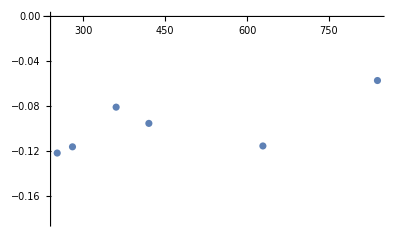

```mathematica
ListPlot[Stable1410reg2]
```

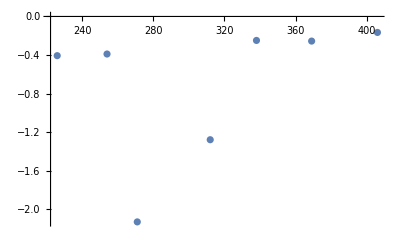

```mathematica
ListPlot[Stable1607reg2]
```

```mathematica
Temperature[zh_,as_List,bs_List]:=1/(π zh)Sqrt[Exp[-aNet[as,1]-bNet[as,bs,1]]];
```

InterpolatingFunction::dmval: Input value {0.01002} lies outside the range of data in the interpolating function. Extrapolation will be used.

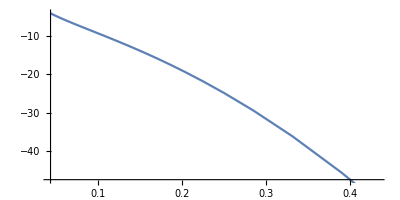

```mathematica
ParametricPlot[{Temperature[zs,parameters1410reg2[[1,2]],parameters1410reg2[[1,3]]],EEvsl1410reg2[parameters1410reg2[[1,1]]][zs]},{zs,0.01,0.99},AspectRatio->1/2]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[Symbol[],PlotStyle→{color,Thickness[Large]}],Frame→{{True,False},{True,False}},FrameStyle→{{{color,Thickness[0.002],FontSize→15},{color,Thickness[0.002],FontSize→15}},{{color,Thickness[0.002],FontSize→15},{color,Thickness[0.002],FontSize→15}}},ImageSize→400].

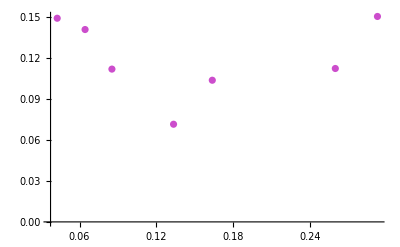
Show[-Graphics-,ListPlot[Symbol[],PlotStyle→{RGBColor[0, Rational[2, 3], Rational[2, 3]],Thickness[Large]}],Frame→{{True,False},{True,False}},FrameStyle→{{{GrayLevel[0],Thickness[0.002],FontSize→15},{GrayLevel[0],Thickness[0.002],FontSize→15}},{{GrayLevel[0],Thickness[0.002],FontSize→15},{GrayLevel[0],Thickness[0.002],FontSize→15}}},ImageSize→400]

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[Symbol[],PlotStyle→{color,Thickness[Large]}],Frame→{{True,False},{True,False}},FrameStyle→{{{color,Thickness[0.002],FontSize→15},{color,Thickness[0.002],FontSize→15}},{{color,Thickness[0.002],FontSize→15},{color,Thickness[0.002],FontSize→15}}},Axes→None,ImageSize→400].

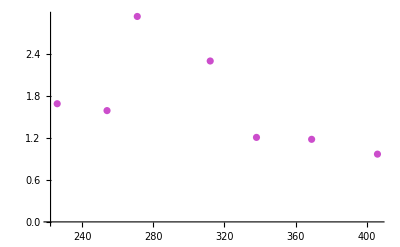
Show[-Graphics-,ListPlot[Symbol[],PlotStyle→{RGBColor[0, Rational[2, 3], Rational[2, 3]],Thickness[Large]}],Frame→{{True,False},{True,False}},FrameStyle→{{{GrayLevel[0],Thickness[0.002],FontSize→15},{GrayLevel[0],Thickness[0.002],FontSize→15}},{{GrayLevel[0],Thickness[0.002],FontSize→15},{GrayLevel[0],Thickness[0.002],FontSize→15}}},Axes→None,ImageSize→400]

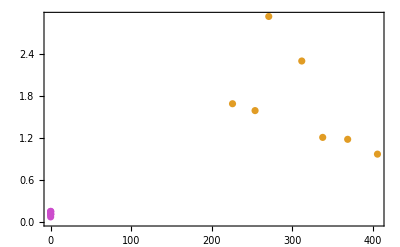

```mathematica
(*Sth[zh_,Rα_]:=Rα^4 π/(2 zh);*)
Sth[zh_,coef_,l_]:=(√coef √(2π))^3/(4 zh^3)l/.zh->1;
Sthermal1410reg2 = Table[{Temperature[1,parameters1410reg2[[i,2]],parameters1410reg2[[i,3]]],Sth[1,parameters1410reg2[[i,4]],1]},{i,1,Length@parameters1410reg2[[All,1]]}];

Sthermal1607reg2 = Table[{parameters1607reg2[[i,1]],Sth[zh[parameters1607reg2[[i,1]],parameters1607reg2[[i,2]],parameters1607reg2[[i,3]]],parameters1607reg2[[i,4]],1]/parameters1607reg2[[i,1]]^3},{i,1,Length@parameters1607reg2[[All,1]]}];


Show[ListPlot[{Sthermal1410reg2},PlotRange->All,PlotStyle->styleRainbow[[2]]],ListPlot[refData[[All,{1,4}]],PlotStyle->{Darker[Cyan],Thick}],Frame->{{True,False},{True,False}},FrameStyle->{{{Black,Thickness[0.002],FontSize->15},{Black,Thickness[0.002],FontSize->15}},{{Black,Thickness[0.002],FontSize->15},{Black,Thickness[0.002],FontSize->15}}},ImageSize->400]

Show[ListPlot[{Sthermal1607reg2},PlotRange->All,PlotStyle->styleRainbow[[2]]],ListPlot[refData[[All,{1,4}]],PlotStyle->{Darker[Cyan],Thick}],Frame->{{True,False},{True,False}},FrameStyle->{{{Black,Thickness[0.002],FontSize->15},{Black,Thickness[0.002],FontSize->15}},{{Black,Thickness[0.002],FontSize->15},{Black,Thickness[0.002],FontSize->15}}},Axes->None,ImageSize->400]

Show[ListPlot[{Sthermal1410reg2,Sthermal1607reg2},PlotRange->All,PlotStyle->styleRainbow[[2]]],Frame->{{True,False},{True,False}},FrameStyle->{{{Black,Thickness[0.002],FontSize->15},{Black,Thickness[0.002],FontSize->15}},{{Black,Thickness[0.002],FontSize->15},{Black,Thickness[0.002],FontSize->15}}},Axes->None,ImageSize->400]
```

```mathematica
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/1607-Sthermal.pdf",%540,"PDF"]
```

/home/htakko/Dropbox/Own/deep-learning-EE/figures/1607-Sthermal.pdf

## Compare to thermal entropy from

hiladata paperista https://arxiv.org/pdf/1204.6184 appendix table 1

S/T^3=I/T^4+4 P/T^4

Data is stored in “refData” as 
[[1]] = T/T_c
[[2]] = I/T^4
[[3]] = p/T^4
[[4]] = S/T^3=I/T^4+4 P/T^4

```mathematica
refData={{0.70 ,0.010425 ,0.00151,0.016465},{0.74 ,0.016227,0.0023,0.025426999999999998},{0.78 ,0.023231,0.00331,0.036471},{0.82 ,0.031822 ,0.00462,0.050302},{0.86 ,0.043319,0.00643,0.069039},{0.90 ,0.059422 ,0.00873,0.09434200000000001},{0.94, 0.085936, 0.01183,0.13325599999999999},{0.98 ,0.143347 ,0.01644,0.209107},{1.00 ,1.0008672 ,0.02224,1.0898272},{1.02, 2.0780137 ,0.05719,2.3067737},{1.06 ,2.430929,0.145510,3.012969},{1.10 ,2.483738,0.237010,3.4317779999999996},{1.14 ,2.430922 ,0.325010,3.730962},{1.18 ,2.342617 ,0.407410,3.972257 },{1.22, 2.234228,0.483710,4.169067999999999},{1.26 ,2.114520, 0.553910,4.33016},{1.30 ,1.998021, 0.61819,4.470781000000001},{1.34, 1.886721,0.67709,4.595081},{1.38 ,1.780919, 0.73099,4.704879},{1.42 ,1.681017,0.78049,4.802977},{1.46, 1.587217, 0.82589,4.890777},{1.5, 1.499519, 0.86759,4.969879},{2.0 ,0.803824, 1.18908,4.969879},{2.5, 0.505723,1.331912,5.560143999999999},{3.0 ,0.358927,1.409813,5.833371},{3.5 ,0.273620,1.458214,5.998179},{4.0 ,0.220711,1.491014,6.106476},{4.5 ,0.185515,1.514914,6.184767},{ 5.0 ,0.160621,1.533014,6.245171},{6.0 ,0.126613,1.559117,6.292677},{7.0 ,0.105010,1.576818,6.363081},{8.0 ,0.09039,1.589818,6.412282},{9.0 ,0.07988,1.599819,6.449662},{10 ,0.072015,1.607819,6.479156000000001},{20, 0.037516,1.644429,6.503291000000001},{30 ,0.026513,1.657235,6.615232},{40 ,0.021611,1.664140,6.655453},{50 ,0.019111,1.668643,6.678171},{ 60 ,0.017412,1.672046,6.693683},{80 ,0.015412,1.676748,6.705596},{80 ,0.015412,1.676748,6.722404},{100, 0.014212, 1.680050,6.734412},{200 ,0.011211,1.688753,6.766223},{ 300, 0.010012, 1.693053,6.782223999999999},{400, 0.009112,1.695853,6.792524},{ 500, 0.008512 ,1.697752,6.799519999999999},{600, 0.008012, 1.699252,6.80502},{ 800, 0.007311, 1.701452,6.8131189999999995},{1000 ,0.006810,1.703052,6.819018}};
```

```mathematica
refData[[All,2]]=refData[[All,2]]*refData[[All,1]]^2
```

{0.00510825,0.00888591,0.0141337,0.0213971,0.0320387,0.0481318,0.075933,0.13767,1.00087,2.16197,2.73139,3.00532,3.15923,3.26186,3.32542,3.35701,3.37666,3.3878,3.39158,3.3896,3.38331,3.37392,3.2153,3.16077,3.23034,3.35184,3.53138,3.75668,4.01553,4.55807,5.14549,5.78496,6.47028,7.2015,15.0064,23.8617,34.5776,47.7775,62.6832,98.6368,98.6368,142.12,448.44,901.08,1457.92,2128.,2884.32,4679.04,6810.}

```mathematica
refData[[All,4]]=refData[[All,4]]/refData[[All,1]]^3
```

{0.0480029,0.062748,0.0768535,0.0912313,0.108542,0.129413,0.160437,0.222173,1.08983,2.17372,2.52975,2.57835,2.51829,2.41764,2.29593,2.16467,2.03495,1.90976,1.79024,1.67743,1.57152,1.47256,0.621235,0.355849,0.216051,0.139899,0.0954137,0.0678712,0.0499614,0.0291328,0.0185513,0.012524,0.00884727,0.00647916,0.000812911,0.000245009,0.000103991,0.0000534254,0.0000309893,0.0000130969,0.0000131297,6.73441×10^-6,8.45778×10^-7,2.51193×10^-7,1.06133×10^-7,5.43962×10^-8,3.15047×10^-8,1.33069×10^-8,6.81902×10^-9}

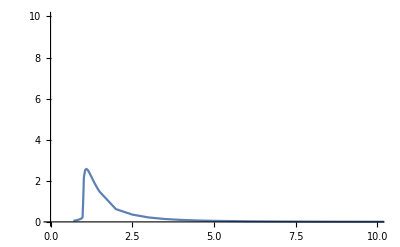

```mathematica
ListLinePlot[refData[[All,{1,4}]],PlotRange->{{0,10},{0,10}}]
```

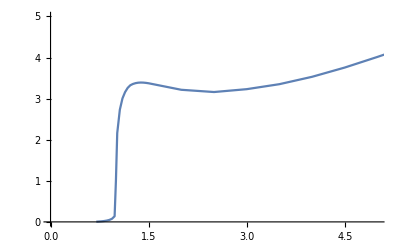

```mathematica
ListLinePlot[refData[[All,{1,2}]],PlotRange->{{0,5},{0,5}}]
```

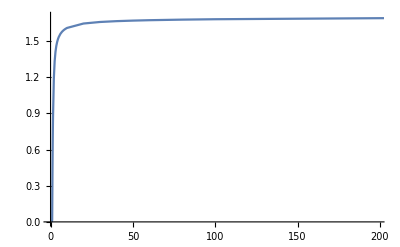

```mathematica
ListLinePlot[refData[[All,{1,3}]]]
```

## Stress-energy tensor and Null energy conditions

Another conistency check: Reissner-nordström BH with metric
ds^2 = -f(r)dt^2+1/(f(r))dr^2+r^2 dΩ^2
f(r) = 1-(2m)/r+q^2/r^2 
and the Ricci tensor components should be (diagonal) and Ricci scalar vanishes
R_tt=-q^2/r^4 g_tt
R_rr=-q^2/r^4 g_rr
R_θθ=q^2/r^4 g_θθ
R_ϕϕ=q^2/r^4 g_ϕϕ

```mathematica
gtemp={{-(1-x^2/a^2),0,0,0},{0,1/(1-x^2/a^2),0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[θ]^2}};
RicciTensor[gtemp,{t,x,θ,ϕ}]
```

{{(3 (-a^2+x^2))/a^4,0,0,0},{0,3/(a^2-x^2),0,0},{0,0,(3 x^2)/a^2,0},{0,0,0,(3 x^2 Sin[θ]^2)/a^2}}

Back to the general case:

```mathematica
dsnet=L^2/z^2 DiagonalMatrix[{-f[z],1,1,1,g[z]}];(*/.f->(1-2 m/#^4+q^2/#^6&)*);
null = {a,0,0,0,b};
nullcondNet=Solve[Sum[dsnet[[i,j]]null[[i]]null[[j]],{i,1,5},{j,1,5}]==0,a][[1]]
n = null/.nullcondNet/.b->1;
n={(-√g[z])/(√f[z]),0,0,0,1}
gInv=Inverse[dsnet];
xx = {t,x1,x2,x3,z};
RicciTensorNet=RicciTensor[dsnet,xx];
RicciScalarNet=RicciScalar[dsnet,xx]//FullSimplify
Nullcond =Sum[RicciTensorNet[[i,j]]n[[i]]n[[j]],{i,1,5},{j,1,5}]//FullSimplify
```

{a→-(b √g[z])/(√f[z])}

{-(√g[z])/(√f[z]),0,0,0,1}

1/(2 L^2 f[z]^2 g[z]^2)(z^2 g[z] f'[z]^2-8 f[z]^2 (5 g[z]+z g'[z])+z f[z] (f'[z] (8 g[z]+z g'[z])-2 z g[z] f''[z]))

-(3 (g[z] f'[z]+f[z] g'[z]))/(2 z f[z] g[z])

```mathematica
Sum[dsnet[[i,j]]n[[i]]n[[j]],{i,1,5},{j,1,5}]==0
```

True

```mathematica
Nullcond=-(3 (g[z] f'[z]+f[z] g'[z]))/(2 z f[z] g[z]);
```

```mathematica
Clear[computeRicciScalar]
computeRicciScalar[as_List,bs_List]:=1/(2 fNet[as,z]^2 gNet[as,bs,z]^2)(z^2 gNet[as,bs,z] D[fNet[as,z],z]^2-8 fNet[as,z]^2 (5 gNet[as,bs,z]+z D[gNet[as,bs,z],z])+z fNet[as,z] (D[fNet[as,z],z] (8 gNet[as,bs,z]+z D[gNet[as,bs,z],z])-2 z gNet[as,bs,z] D[D[fNet[as,z],z],z]))
```

```mathematica
NECab[a1_,a2_,b1_,b2_,z_]:=-3 b2-(3 b1)/(2 z)+9/10 (5 a1^2+5 a1 a2+2 a2^2+5 (b1+b2)) z+3 a1 a2 z^2+(3 a2^2 z^3)/2;
```

```mathematica
Clear[computeNEC]
computeNEC[as_List,bs_List]:=-1/(2 z fNet[as,z] gNet[as,bs,z])3 (gNet[as,bs,z]D[fNet[as,z],z]+fNet[as,z] D[gNet[as,bs,z],z]);
```

```mathematica
computeTrace[as_List,bs_List]:=1/(2 z^2 fNet[as,z]^2 gNet[as,bs,z]^2)(-z^2 gNet[as,bs,z] D[fNet[as,z],z]^2+3 fNet[as,z]^3 (4 gNet[as,bs,z]+z D[gNet[as,bs,z],z])+6 fNet[as,z]^2 (2 gNet[as,bs,z] (2+gNet[as,bs,z])+z D[gNet[as,bs,z],z])+z fNet[as,z] (-D[fNet[as,z]] (3 gNet[as,bs,z] (2+gNet[as,bs,z])+z D[gNet[as,bs,z],z])+2 z gNet[as,bs,z] D[D[fNet[as,z],z],z]));
```

```mathematica
computeEnergyDensity[as_List,bs_List]:=-((3 fNet[as,z] (4 gNet[as,bs,z]+z D[gNet[as,bs,z],z]))/(2 z^2 gNet[as,bs,z]^2));
computePressure[as_List,bs_List]:=1/(4 z^2 fNet[as,z]^2 gNet[as,bs,z]^2)(-z^2 gNet[as,bs,z] D[fNet[as,z],z]^2+6 fNet[as,z]^2 (4 gNet[as,bs,z]+z D[gNet[as,bs,z],z])+z fNet[as,z] (-D[fNet[as,z],z] (6 gNet[as,bs,z]+z D[gNet[as,bs,z],z])+2 z gNet[as,bs,z] D[D[fNet[as,z],z],z]));
computePressurez[as_List]:=(3 (4-(z D[fNet[as,z],z])/fNet[as,z]))/(2 z^2);
```

#### Compute and plot the Ricci scalar

Compute the Ricci scalar for each temperature, 1410:

```mathematica
Clear[Ricci1410reg2]
Monitor[Do[
T=parameters1410reg2[[i,1]];
Ricci1410reg2[T]=Table[{zz,computeRicciScalar[parameters1410reg2[[i,2]],parameters1410reg2[[i,3]]]/.z->zz},{zz,gridzs}],{i,1,Length[parameters1410reg2]}],N[T]]
```

Compute the Ricci scalar for each temperature, 1607:

```mathematica
Clear[Ricci1607reg2]
Monitor[Do[
T=parameters1607reg2[[i,1]];
Ricci1607reg2[T]=Table[{zz,computeRicciScalar[parameters1607reg2[[i,2]],parameters1607reg2[[i,3]]]/.z->zz},{zz,gridzs}],{i,1,Length[parameters1607reg2]}],N[T]]
```

Plot the results for Ricci scalar

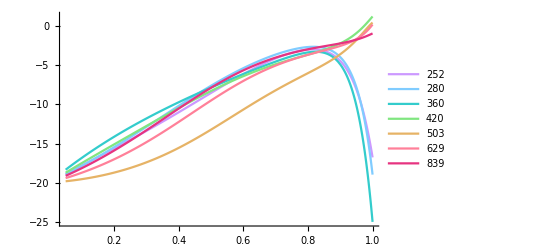

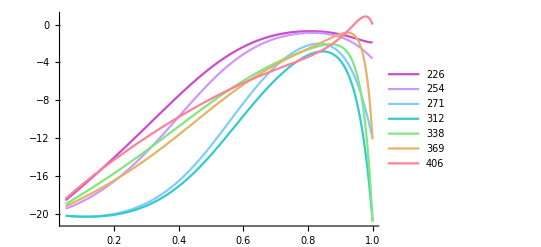

```mathematica
Show[ListLinePlot[Table[Ricci1410reg2[T][[All,{1,2}]],{T,parameters1410reg2[[All,1]]}],PlotStyle->styleRainbow[[3;;]],PlotLegends->parameters1410reg2[[All,1]]](*,
ListLinePlot[Table[Re@complexRicci1410[T][[All,{1,2}]],{T,parameters1410[[All,1]]}],PlotStyle->dashedStyleRainbow[[3;;]]]*),PlotRange->Automatic,ImageSize->400,AxesStyle->{{Thickness[0.003],FontSize->15},{Thickness[0.003],FontSize->15}}]

Show[ListLinePlot[Table[Ricci1607reg2[T][[All,{1,2}]],{T,parameters1607reg2[[All,1]]}],PlotStyle->styleRainbow[[2;;]],PlotLegends->parameters1607reg2[[All,1]]],
(*ListLinePlot[Table[Re@complexRicci1607[T][[All,{1,2}]],{T,parameters1607[[All,1]]}],PlotStyle->dashedStyleRainbow[[2;;]]],*)PlotRange->Automatic,ImageSize->400,AxesStyle->{{Thickness[0.003],FontSize->15},{Thickness[0.003],FontSize->15}}]
```

```mathematica
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/1410-RicciScalar-reg2.pdf",%1155,"PDF"];
```

```mathematica
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/1607-RicciScalar-reg2.pdf",%1156,"PDF"];
```

#### Compute and plot the trace of (T_νμ)

Compute the trace of stress-energy tensor “TT” for each temperature, 1410:

```mathematica
Clear[Trace1410]
Monitor[Do[
T=parameters1410[[i,1]];
Trace1410[T]=Table[{zz,computeTrace[parameters1410[[i,2]],parameters1410[[i,3]]]/.z->zz},{zz,gridzs}],{i,1,Length[parameters1410[[All,1]]]}],N[T]]
```

```mathematica
Clear[complexTrace1410]
Monitor[Do[
T=parameters1410[[i,1]];
complexTrace1410[T]=Table[{zz,computeTrace[parameters1410[[i,2]],parameters1410[[i,3]]]/.z->zz},{zz,zsComplex1410[T]}],{i,1,Length[parameters1410[[All,1]]]}],N[T]]
```

Compute the trace of stress-energy tensor “TT” for each temperature, 1607:

```mathematica
Clear[Trace1607]
Monitor[Do[
T=parameters1607[[i,1]];
Trace1607[T]=Table[{zz,computeTrace[parameters1607[[i,2]],parameters1607[[i,3]]]/.z->zz},{zz,gridzs}],{i,1,Length[parameters1607[[All,1]]]}],N[T]]
```

```mathematica
Clear[complexTrace1607]
Monitor[Do[
T=parameters1607[[i,1]];
complexTrace1607[T]=Table[{zz,computeTrace[parameters1607[[i,2]],parameters1607[[i,3]]]/.z->zz},{zz,zsComplex1607[T]}],{i,1,Length[parameters1607[[All,1]]]}],N[T]]
```

Plot the results for Tr(TT)

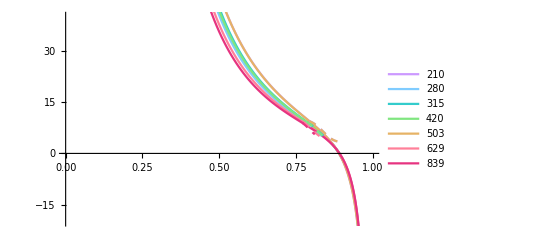

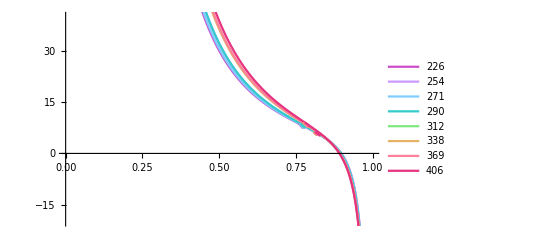

```mathematica
Show[ListLinePlot[Table[Trace1410[T][[All,{1,2}]],{T,parameters1410[[All,1]]}],PlotStyle->styleRainbow[[3;;]],PlotLegends->parameters1410[[All,1]]],
ListLinePlot[Table[Re@complexTrace1410[T][[All,{1,2}]],{T,parameters1410[[All,1]]}],PlotStyle->dashedStyleRainbow[[3;;]]],PlotRange->{{0,1},{-20,40}},ImageSize->400,AxesStyle->{{Thickness[0.003],FontSize->15},{Thickness[0.003],FontSize->15}}]

Show[ListLinePlot[Table[Trace1607[T][[All,{1,2}]],{T,parameters1607[[All,1]]}],PlotStyle->styleRainbow[[2;;]],PlotLegends->parameters1607[[All,1]]],
ListLinePlot[Table[Re@complexTrace1607[T][[All,{1,2}]],{T,parameters1607[[All,1]]}],PlotStyle->dashedStyleRainbow[[2;;]]],PlotRange->{{0,1},{-20,40}},ImageSize->400,AxesStyle->{{Thickness[0.003],FontSize->15},{Thickness[0.003],FontSize->15}}]
```

```mathematica
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/1410-Trace.pdf",%741,"PDF"]
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/1607-Trace.pdf",%742,"PDF"]
```

/home/htakko/Dropbox/Own/deep-learning-EE/figures/1410-Trace.pdf

/home/htakko/Dropbox/Own/deep-learning-EE/figures/1607-Trace.pdf

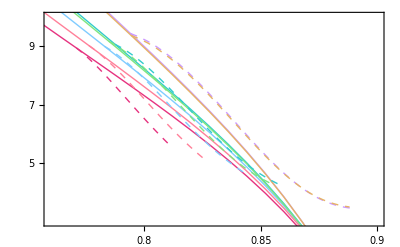

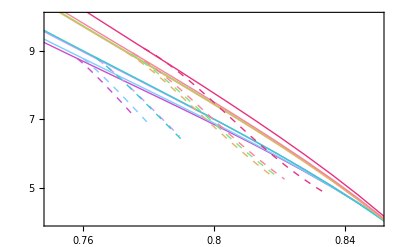

```mathematica
Show[ListLinePlot[Table[Trace1410[T][[All,{1,2}]],{T,parameters1410[[All,1]]}],PlotStyle->styleRainbow[[3;;]]],
ListLinePlot[Table[Re@complexTrace1410[T][[All,{1,2}]],{T,parameters1410[[All,1]]}],PlotStyle->dashedStyleRainbow[[3;;]]],PlotRange->{{0.76,0.9},{3,10}},ImageSize->400,Frame->{{True,True},{True,True}},FrameStyle->{{{Black,Thickness[0.002],FontSize->15},{Black,Thickness[0.002],FontSize->15}},{{Black,Thickness[0.002],FontSize->15},{Black,Thickness[0.002],FontSize->15}}},FrameTicks->{{0.8,0.85,0.9},{0,5,7,9}},Axes->None]

Show[ListLinePlot[Table[Trace1607[T][[All,{1,2}]],{T,parameters1607[[All,1]]}],PlotStyle->styleRainbow[[2;;]]],
ListLinePlot[Table[Re@complexTrace1607[T][[All,{1,2}]],{T,parameters1607[[All,1]]}],PlotStyle->dashedStyleRainbow[[2;;]]],PlotRange->{{0.75,0.85},{4,10}},ImageSize->400,Frame->{{True,True},{True,True}},FrameStyle->{{{Black,Thickness[0.002],FontSize->15},{Black,Thickness[0.002],FontSize->15}},{{Black,Thickness[0.002],FontSize->15},{Black,Thickness[0.002],FontSize->15}}},FrameTicks->{{0.76,0.8,0.84},{0,5,7,9}},Axes->None]
```

```mathematica
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/1410-Trace-closeup.pdf",%737,"PDF"]
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/1607-Trace-closeup.pdf",%738,"PDF"]
```

/home/htakko/Dropbox/Own/deep-learning-EE/figures/1410-Trace-closeup.pdf

/home/htakko/Dropbox/Own/deep-learning-EE/figures/1607-Trace-closeup.pdf

#### Compute and plot the NECs

Compute the NECs for each T in 1410, real and complex embedding values

```mathematica
computeNEC[parameters1410[[1,2]],parameters1410[[1,3]]]/.z->0.2
```

-5.6531

```mathematica
NECab[-1.80125653,2.78048834,0.51274877,1.40784087,0.2]
```

-5.6531

```mathematica
-(3 (g[z] f'[z]+f[z] g'[z]))/(2 z f[z] g[z])/.f->(fNet[{a1,a2},#]&)/.g->(gNet[{a1,a2},{b1,b2},#]&)//FullSimplify
```

-3 b2-(3 b1)/(2 z)+9/10 (5 a1^2+5 a1 a2+2 a2^2+5 (b1+b2)) z+3 a1 a2 z^2+(3 a2^2 z^3)/2

```mathematica
NECab[a1_,a2_,b1_,b2_,z_]=-3 b2-(3 b1)/(2 z)+9/10 (5 a1^2+5 a1 a2+2 a2^2+5 (b1+b2)) z+3 a1 a2 z^2+(3 a2^2 z^3)/2;
```

```mathematica
parameters1410[[5,2]]
parameters1410[[5,3]]
```

{-0.004105,0.0058}

{1.80755,2.60747}

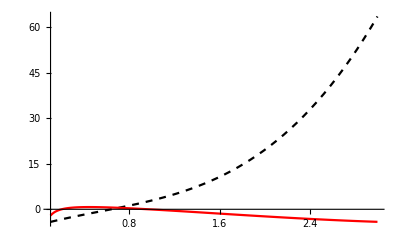

```mathematica
Plot[{NECab[-1.16,1.44,0,1.7,z],NECab[-0.5322,0.2957,0.308,-0.9145,z]},{z,0.1,3},PlotStyle->{{Black,Dashed},Red}]
```

```mathematica
fNet[{a1,a2},z]
gNet[{a1,a2},{b1,b2},z]
```

ⅇ^(-1/3 a1^2 z^3-1/2 a1 a2 z^4-(a2^2 z^5)/5) (1-z^4)

(ⅇ^(b1 z+b2 z^2-((2 a1^2)/3+a1 a2+(2 a2^2)/5+b1+b2) z^3))/(1-z^4)

```mathematica
Monitor[Do[
T=parameters1410reg2[[i,1]];
NECs1410reg2[T]=Table[{zz,computeNEC[parameters1410reg2[[i,2]],parameters1410reg2[[i,3]]]/.z->zz},{zz,gridzs}],{i,1,Length[parameters1410reg2[[All,1]]]}],N[T]]
```

Compute the NECs for each T in 1607, real and complex embedding values

```mathematica
Monitor[Do[
T=parameters1607reg2[[i,1]];
NECs1607reg2[T]=Table[{zz,computeNEC[parameters1607reg2[[i,2]],parameters1607reg2[[i,3]]]/.z->zz},{zz,gridzs}],{i,1,Length[parameters1607reg2[[All,1]]]}],N[T]]
```

Plot the results

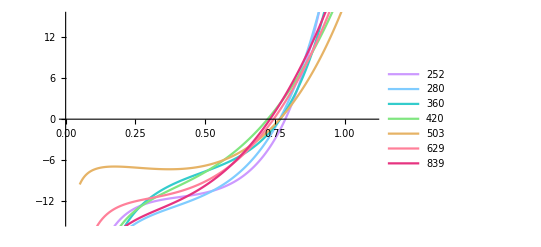

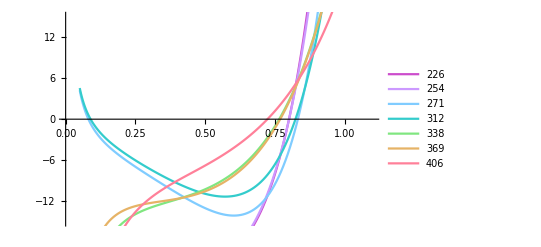

```mathematica
Show[ListLinePlot[Table[NECs1410reg2[T][[All,{1,2}]],{T,parameters1410reg2[[All,1]]}],PlotStyle->styleRainbow[[3;;]],PlotLegends->parameters1410reg2[[All,1]]],
(*ListLinePlot[Table[Re@complexNECs1410[T][[All,{1,2}]],{T,parameters1410[[All,1]]}],PlotStyle->dashedStyleRainbow[[3;;]]],*)PlotRange->{{0,1.1},{-15,15}},ImageSize->400,AxesStyle->{{Thickness[0.003],FontSize->15},{Thickness[0.003],FontSize->15}}]

Show[ListLinePlot[Table[NECs1607reg2[T][[All,{1,2}]],{T,parameters1607reg2[[All,1]]}],PlotStyle->styleRainbow[[2;;]],PlotLegends->parameters1607reg2[[All,1]]],
(*ListLinePlot[Table[Re@complexNECs1607[T][[All,{1,2}]],{T,parameters1607[[All,1]]}],PlotStyle->dashedStyleRainbow[[2;;]]],*)PlotRange->{{0,1.1},{-15,15}},ImageSize->400,AxesStyle->{{Thickness[0.003],FontSize->15},{Thickness[0.003],FontSize->15}}]
```

```mathematica
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/1410-NECs-reg2.pdf",%1159,"PDF"];
```

```mathematica
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/1607-NECs-reg2.pdf",%1160,"PDF"];
```

#### Compute and plot the energy density

Compute the energy density ρ for each T in 1410, real and complex embedding values

```mathematica
Clear[ρ1410]
Monitor[Do[
T=parameters1410[[i,1]];
ρ1410[T]=Table[{zz,-computeEnergyDensity[parameters1410[[i,2]],parameters1410[[i,3]]]/.z->zz},{zz,gridzs}],{i,1,Length[parameters1410[[All,1]]]}],N[T]]
```

```mathematica
Clear[complexρ1410]
Monitor[Do[
T=parameters1410[[i,1]];
complexρ1410[T]=Table[{zz,-computeEnergyDensity[parameters1410[[i,2]],parameters1410[[i,3]]]/.z->zz},{zz,zsComplex1410[T]}],{i,1,Length[parameters1410[[All,1]]]}],N[T]]
```

Compute the energy densities ρ for each T in 1607, real and complex embedding values

```mathematica
Clear[ρ1607]
Monitor[Do[
T=parameters1607[[i,1]];
ρ1607[T]=Table[{zz,-computeEnergyDensity[parameters1607[[i,2]],parameters1607[[i,3]]]/.z->zz},{zz,gridzs}],{i,1,Length[parameters1607[[All,1]]]}],N[T]]
```

```mathematica
Clear[complexρ1607]
Monitor[Do[
T=parameters1607[[i,1]];
complexρ1607[T]=Table[{zz,-computeEnergyDensity[parameters1607[[i,2]],parameters1607[[i,3]]]/.z->zz},{zz,zsComplex1607[T]}],{i,1,Length[parameters1607[[All,1]]]}],N[T]]
```

Plot the results

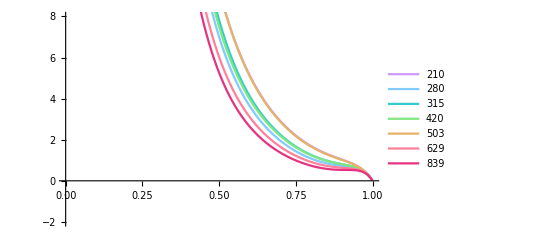

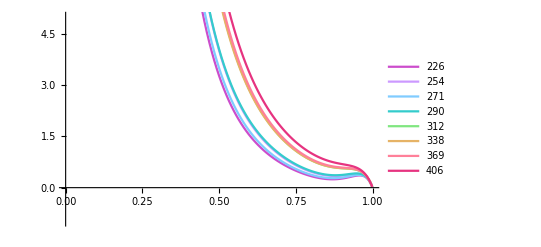

```mathematica
Show[ListLinePlot[Table[ρ1410[T][[All,{1,2}]],{T,parameters1410[[All,1]]}],PlotStyle->styleRainbow[[3;;]],PlotLegends->parameters1410[[All,1]]],
(*ListLinePlot[Table[Re@complexρ1410[T][[All,{1,2}]],{T,parameters1410[[All,1]]}],PlotStyle->dashedStyleRainbow[[3;;]]],*)PlotRange->{{0,1},{-2,8}},ImageSize->400,AxesStyle->{{Thickness[0.003],FontSize->15},{Thickness[0.003],FontSize->15}}]

Show[ListLinePlot[Table[ρ1607[T][[All,{1,2}]],{T,parameters1607[[All,1]]}],PlotStyle->styleRainbow[[2;;]],PlotLegends->parameters1607[[All,1]]],
(*ListLinePlot[Table[Re@complexρ1607[T][[All,{1,2}]],{T,parameters1607[[All,1]]}],PlotStyle->dashedStyleRainbow[[2;;]]],*)PlotRange->{{0,1},{-1,5}},ImageSize->400,AxesStyle->{{Thickness[0.003],FontSize->15},{Thickness[0.003],FontSize->15}}]
```

```mathematica
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/1410-energyDensity.pdf",%523,"PDF"];Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/1607-energyDensity.pdf",%524,"PDF"];
```

#### Compute and plot the pressure (from T_νμ)

Compute the pressures for each T in 1410, real and complex embedding values

```mathematica
Clear[pressures1410]
Monitor[Do[
T=parameters1410[[i,1]];
pressures1410[T]=Table[{zz,computePressure[parameters1410[[i,2]],parameters1410[[i,3]]]/.z->zz},{zz,gridzs}],{i,1,Length[parameters1410[[All,1]]]}],N[T]]
```

```mathematica
Clear[complexPressures1410]
Monitor[Do[
T=parameters1410[[i,1]];
complexPressures1410[T]=Table[{zz,computePressure[parameters1410[[i,2]],parameters1410[[i,3]]]/.z->zz},{zz,zsComplex1410[T]}],{i,1,Length[parameters1410[[All,1]]]}],N[T]]
```

Compute the pressures for each T in 1607, real and complex embedding values

```mathematica
Clear[pressures1607]
Monitor[Do[
T=parameters1607[[i,1]];
pressures1607[T]=Table[{zz,computePressure[parameters1607[[i,2]],parameters1607[[i,3]]]/.z->zz},{zz,gridzs}],{i,1,Length[parameters1607[[All,1]]]}],N[T]]
```

```mathematica
Clear[complexPressures1607]
Monitor[Do[
T=parameters1607[[i,1]];
complexPressures1607[T]=Table[{zz,computePressure[parameters1607[[i,2]],parameters1607[[i,3]]]/.z->zz},{zz,zsComplex1607[T]}],{i,1,Length[parameters1607[[All,1]]]}],N[T]]
```

Plot the results

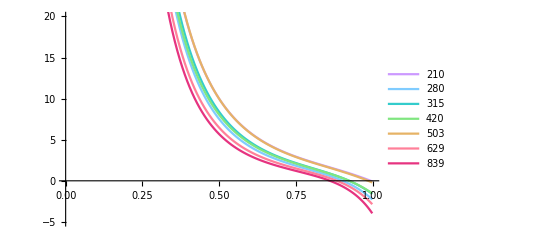

```mathematica
Show[ListLinePlot[Table[pressures1410[T][[All,{1,2}]],{T,parameters1410[[All,1]]}],PlotStyle->styleRainbow[[3;;]],PlotLegends->parameters1410[[All,1]]],
(*ListLinePlot[Table[Re@complexPressures1410[T][[All,{1,2}]],{T,parameters1410[[All,1]]}],PlotStyle->dashedStyleRainbow[[3;;]]],*)PlotRange->{{0,1},{-5,20}},ImageSize->400,AxesStyle->{{Thickness[0.003],FontSize->15},{Thickness[0.003],FontSize->15}}]
```

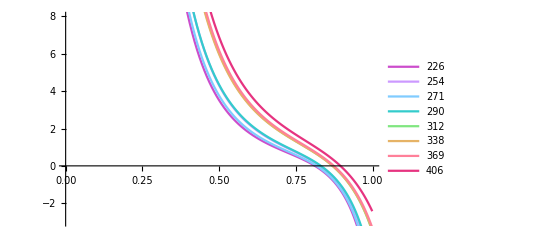

```mathematica
Show[ListLinePlot[Table[pressures1607[T][[All,{1,2}]],{T,parameters1607[[All,1]]}],PlotStyle->styleRainbow[[2;;]],PlotLegends->parameters1607[[All,1]]],
(*ListLinePlot[Table[Re@complexPressures1607[T][[All,{1,2}]],{T,parameters1607[[All,1]]}],PlotStyle->dashedStyleRainbow[[2;;]]],*)PlotRange->{{0,1},{-3,8}},ImageSize->400,AxesStyle->{{Thickness[0.003],FontSize->15},{Thickness[0.003],FontSize->15}}]
```

```mathematica
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/1410-pressure.pdf",%583,"PDF"];Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/1607-pressure.pdf",%584,"PDF"];
```

Compute the pressures of z-component for each T in 1410

```mathematica
Clear[pressuresz1410reg2]
Monitor[Do[
T=parameters1410reg2[[i,1]];
pressuresz1410reg2[T]=Table[{zz,computePressurez[parameters1410reg2[[i,2]]]/.z->zz},{zz,gridzs}],{i,1,Length[parameters1410[[All,1]]]}],N[T]]
```

Compute the pressures for each T in 1607

```mathematica
Clear[pressuresz1607]
Monitor[Do[
T=parameters1607[[i,1]];
pressuresz1607[T]=Table[{zz,computePressurez[parameters1607[[i,2]]]/.z->zz},{zz,gridzs}],{i,1,Length[parameters1607[[All,1]]]}],N[T]]
```

Plot the results

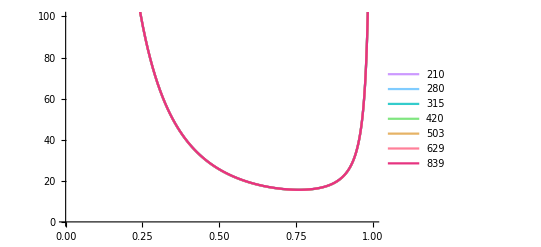

```mathematica
Show[ListLinePlot[Table[pressuresz1410[T][[All,{1,2}]],{T,parameters1410[[All,1]]}],PlotStyle->styleRainbow[[3;;]],PlotLegends->parameters1410[[All,1]]],
(*ListLinePlot[Table[Re@complexPressuresz1410[T][[All,{1,2}]],{T,parameters1410[[All,1]]}],PlotStyle->dashedStyleRainbow[[3;;]]],*)PlotRange->{{0,1},{0,100}},ImageSize->400,AxesStyle->{{Thickness[0.003],FontSize->15},{Thickness[0.003],FontSize->15}}]
```

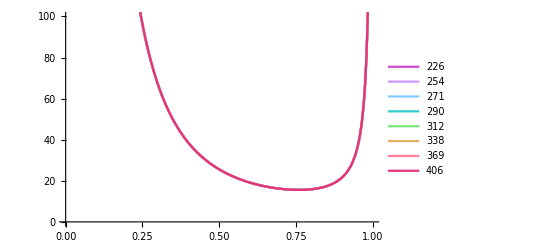

```mathematica
Show[ListLinePlot[Table[pressuresz1607[T][[All,{1,2}]],{T,parameters1607[[All,1]]}],PlotStyle->styleRainbow[[2;;]],PlotLegends->parameters1607[[All,1]]],(*
ListLinePlot[Table[Re@complexPressuresz1607[T][[All,{1,2}]],{T,parameters1607[[All,1]]}],PlotStyle->dashedStyleRainbow[[2;;]]],*)PlotRange->{{0,1},{0,100}},ImageSize->400,AxesStyle->{{Thickness[0.003],FontSize->15},{Thickness[0.003],FontSize->15}}]
```

```mathematica
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/1410-pressurez.pdf",%589,"PDF"];Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/1607-pressurez.pdf",%591,"PDF"];
```